```mathematica
SetDirectory[NotebookDirectory[]<>"\\SavedObjects"](*Set a directory to save results in*)
```

C:\Users\irisv\Documents\Universiteit\Master\Master Thesis\Mathematica study of paper 1\SavedObjects

## Projection Wetterich equation single scalar field

For the scalar field theory, we derived the integral in the shift-symmetric approximation (SSA). This integrand can be written in a series, given by my function intrd.

```mathematica
intrd[ω_] = 1/(4π)^2(2k^2*ω-ηs*ω*(k^2-ω))/(k^2+F'[X]*ω)*Sum[Gamma[2]/Gamma[2+n] Gamma[2*n]/Gamma[n](-(X *F''[X]* ω)/(2*(k^2+F '[X]*ω)))^n, {n, 0, ∞}]
```

((2 k^2 ω-(8 (k^2-ω) ω u[2,2])/(128 π^2+u[2,2])) (1/2+(-k^6-4 X ω u[2,2]+k^6 √((k^6+6 X ω u[2,2])/(k^6+2 X ω u[2,2]))+2 X ω u[2,2] √((k^6+6 X ω u[2,2])/(k^6+2 X ω u[2,2])))/(4 X ω u[2,2])))/(16 π^2 (k^2+(2 X ω u[2,2])/k^4))

This can be simplified to a square root as seen below

```mathematica
Simplify[1/(k^2+B*ω)(Sum[Gamma[2]/Gamma[2+n] Gamma[2*n]/Gamma[n](-(X *A* ω)/(2*(k^2+B*ω)))^n, {n, 0, ∞}])]
```

(-1+√((k^2+B ω+2 A X ω)/(k^2+B ω)))/(2 A X ω)

We want to solve this system using a polynomial expansion for X. This means it is easier to work with the integrand still written as a series. First we will choose the order of our polynomial. This is given by Nmaxi.

```mathematica
Nmaxi = 2
```

2

Next we add in the Nth order polynomial approximation of the interaction term (F)

```mathematica
F[X_] := Sum[k^(4-4n)u[n, Nmaxi]X^n , {n, 2, Nmaxi}]
```

```mathematica
F''[X]
```

(2 u[2,2])/k^4

Using this the generating functional as a whole becomes:

```mathematica
func:=Simplify[(-ηs * X +Sum[(β[n, Nmaxi]+4(1-n)u[n, Nmaxi]- n*ηs * u[n, Nmaxi])k^(4(1-n))X^n , {n, 2, Nmaxi}])*k^(-4)/. X-> k^4X]
```

Also the other side of the Wetterich equation has to be expanded in order X. This is the side with the integral.  This way one can solve every power of X separately. We start this by taking the integrand and expanding it into a series (sintrd)

```mathematica
sintrd[ω_]:= Normal[Simplify[Series[intrd[ω], {X, 0, Nmaxi}]]]
```

Next step is the actual integration, here called SInt

```mathematica
SInt[ω_] :=Integrate[sintrd[ω], ω]
```

Now we just need to add in the upper and lower bound of the integral, and collect our results.

```mathematica
SIntzero := SInt[ω] /. ω-> 0
```

```mathematica
SIntk := SInt[ω] /. ω-> k^2
```

```mathematica
IntegratedCollected := Collect[(SIntzero+SIntk)*k^(-4)/. X-> k^4X, X, Simplify]
```

Now that we have both sides of the expression, we can solve order by order for X.

```mathematica
Coefficient[IntegratedCollected, X,1 ]
```

((-8+ηs) u[2,2])/(128 π^2)

```mathematica
Solve[Coefficient[IntegratedCollected, X,1 ]==Coefficient[func, X, 1], ηs ]
```

{{ηs→(8 u[2,2])/(128 π^2+u[2,2])}}

```mathematica
β[2, Nmaxi] = 0
```

0

Eta is given by the same equation for every order of N, so in order to speed things up, we will define it here

```mathematica
ηs := (8 u[2,Nmaxi])/(128 π^2+u[2,Nmaxi])
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], u[2, Nmaxi] ]
```

{{u[2,2]→0},{u[2,2]→128 (-5-2 √6) π^2},{u[2,2]→128 (-5+2 √6) π^2}}

```mathematica
%12/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,2]→0.},{u[2,2]→-12505.5},{u[2,2]→-127.62}}

To then determine the stability coefficients  we have to set beta non-zero and determine the equation for beta--> i think like this I also derive eta, and we shouldn’t....

```mathematica
Clear[β]
```

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2], β[2, Nmaxi] ]
```

{{β[2,2]→(-(512 π^2 u[2,2])/(128 π^2+u[2,2])-(20 u[2,2]^2)/(128 π^2+u[2,2])-(u[2,2]^2 (640 π^2+u[2,2]))/(32 π^2 (128 π^2+u[2,2])))/(-(128 π^2)/(128 π^2+u[2,2])-u[2,2]/(128 π^2+u[2,2]))}}

```mathematica
β[2,2][u_[2,2]]:=(-(512 π^2 u[2,2])/(128 π^2+u[2,2])-(20 u[2,2]^2)/(128 π^2+u[2,2])-(u[2,2]^2 (640 π^2+u[2,2]))/(32 π^2 (128 π^2+u[2,2])))/(-(128 π^2)/(128 π^2+u[2,2])-u[2,2]/(128 π^2+u[2,2]))
```

By deriving beta to the different u[n, Nmax] we can get all components of the stability matrix

```mathematica
D[β[2,2][u[2,2]], u[2,2]]/. u[2,2]->-127.6201617733896
```

-4.40408

The beta equations are really complicated, so to do these last few steps, we will want to simplify more. This is done in the other notebook, where we set eta to zero.

We want to keep track of the u2 values, so we can plot them later for all N. Therefore I will make a list collecting them. (Check if this works)

```mathematica
Clear[u2values]
Clear[u3values]
Clear[u4values]
```

```mathematica
u2values = {{2,-127.6201617733896}}
```

{{2,-127.62}}

### N=3

#### Starting definitions

In this section all the necessary definitions to evaluate the system for N=3 (using the initialisation cells as well) are defined.

```mathematica
Nmaxi = 3;
```

```mathematica
func
```

(X (-20 X u[2,3]^2-128 π^2 X (8 X u[3,3]-β[2,3]-X β[3,3])+u[2,3] (-8-512 π^2 X+X β[2,3]+X^2 (-32 u[3,3]+β[3,3]))))/(128 π^2+u[2,3])

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,3])/(128 π^2+u[2,3])-(-384 π^2+u[2,3])/(96 π^2 (128 π^2+u[2,3]))+(X^2 (u[2,3]^3+128 π^2 (5 u[2,3]^2-4 u[3,3])))/(32 π^2 (128 π^2+u[2,3]))+(X^3 u[2,3] (-74 u[2,3]^3-384 π^2 (74 u[2,3]^2-105 u[3,3])+63 u[2,3] u[3,3]))/(480 π^2 (128 π^2+u[2,3]))

#### Fixed point

This section intends to solve the system for beta is 0 to find the fixed points of the system. We specifically look for system with the highest non-zero value for its coordinates. As this is the fixed point we want to follow.

```mathematica
Solve[Coefficient[IntegratedCollected, X,3 ]==Coefficient[func, X, 3], u[3, Nmaxi]]
```

{{u[3,3]→((296 u[2,3]^3)/(5 (128 π^2+u[2,3]))+(37 u[2,3]^4)/(240 π^2 (128 π^2+u[2,3])))/((1024 π^2)/(128 π^2+u[2,3])+(116 u[2,3])/(128 π^2+u[2,3])+(21 u[2,3]^2)/(160 π^2 (128 π^2+u[2,3])))}}

```mathematica
Solve[Coefficient[IntegratedCollected, X,2 ]==Coefficient[func, X, 2]/.%, u[2, Nmaxi]]
```

{{u[2,3]→0},{u[2,3]→π^2 Root-20.4Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,1]-20.36784540760949},{u[2,3]→π^2 Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596},{u[2,3]→π^2 Root-767.-541. ⅈRoot[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,3]-767.4654636337765},{u[2,3]→π^2 Root-767.+541. ⅈRoot[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,4]-767.4654636337765}}

```mathematica
%25/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,3]→0.},{u[2,3]→-201.023},{u[2,3]→-70.2116},{u[2,3]→-7574.58-5344.14 ⅈ},{u[2,3]→-7574.58+5344.14 ⅈ}}

```mathematica
%24 /. u[2,3]->-70.21163276820778
```

{{u[3,3]→-9919.06}}

So we have found the fixed points for N=3 as well.

```mathematica
u2values = Append[u2values, {3, -70.21163276820778}](*Collects the found values for u2*)
```

{{2,-127.62},{3,-70.2116}}

```mathematica
u3values = {{3,-9919.064618668466}} (*Collects the found values for u3*)
```

{{3,-9919.06}}

### N=4

#### Starting definitions

```mathematica
Nmaxi = 4;(*Define Subscript[N, max]*)
func
```

(X (-20 X u[2,4]^2-128 π^2 X (-β[2,4]+X (8 u[3,4]-β[3,4])+X^2 (12 u[4,4]-β[4,4]))+u[2,4] (-8-512 π^2 X+X β[2,4]+X^2 (-32 u[3,4]+β[3,4])+X^3 (-44 u[4,4]+β[4,4]))))/(128 π^2+u[2,4])

```mathematica
Factor[X^2 (-4 u[2,4]+β[2,4]+X (-8 u[3,4]+β[3,4])+X^2 (-12 u[4,4]+β[4,4]))]
```

-X^2 (4 u[2,4]+8 X u[3,4]+12 X^2 u[4,4]-β[2,4]-X β[3,4]-X^2 β[4,4])

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
```

In order to be able to quickly redo the calculation if necessary, the value of our integral (IntegratedCollected) for N=4 is redefined as IC4 . This means the fixed points can be recalculated without redoing the integration. Especially as N increases this integration starts to take quite some time.

```mathematica
IntegratedCollected
```

-(8 X u[2,4])/(128 π^2+u[2,4])-(-384 π^2+u[2,4])/(96 π^2 (128 π^2+u[2,4]))+(X^2 (u[2,4]^3+128 π^2 (5 u[2,4]^2-4 u[3,4])))/(32 π^2 (128 π^2+u[2,4]))+(X^3 (-74 u[2,4]^4+63 u[2,4]^2 u[3,4]-128 π^2 (222 u[2,4]^3-315 u[2,4] u[3,4]+100 u[4,4])))/(480 π^2 (128 π^2+u[2,4]))+(X^4 (3 u[2,4] (500 u[2,4]^4-756 u[2,4]^2 u[3,4]+105 u[3,4]^2+168 u[2,4] u[4,4])+896 π^2 (500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+360 u[2,4] u[4,4])))/(2240 π^2 (128 π^2+u[2,4]))

```mathematica
IC4 = -(8 X u[2,4])/(128 π^2+u[2,4])-(-384 π^2+u[2,4])/(96 π^2 (128 π^2+u[2,4]))+(X^2 (u[2,4]^3+128 π^2 (5 u[2,4]^2-4 u[3,4])))/(32 π^2 (128 π^2+u[2,4]))+(X^3 (-74 u[2,4]^4+63 u[2,4]^2 u[3,4]-128 π^2 (222 u[2,4]^3-315 u[2,4] u[3,4]+100 u[4,4])))/(480 π^2 (128 π^2+u[2,4]))+(X^4 (3 u[2,4] (500 u[2,4]^4-756 u[2,4]^2 u[3,4]+105 u[3,4]^2+168 u[2,4] u[4,4])+896 π^2 (500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+360 u[2,4] u[4,4])))/(2240 π^2 (128 π^2+u[2,4]))
```

-(8 X u[2,4])/(128 π^2+u[2,4])-(-384 π^2+u[2,4])/(96 π^2 (128 π^2+u[2,4]))+(X^2 (u[2,4]^3+128 π^2 (5 u[2,4]^2-4 u[3,4])))/(32 π^2 (128 π^2+u[2,4]))+(X^3 (-74 u[2,4]^4+63 u[2,4]^2 u[3,4]-128 π^2 (222 u[2,4]^3-315 u[2,4] u[3,4]+100 u[4,4])))/(480 π^2 (128 π^2+u[2,4]))+(X^4 (3 u[2,4] (500 u[2,4]^4-756 u[2,4]^2 u[3,4]+105 u[3,4]^2+168 u[2,4] u[4,4])+896 π^2 (500 u[2,4]^4-972 u[2,4]^2 u[3,4]+225 u[3,4]^2+360 u[2,4] u[4,4])))/(2240 π^2 (128 π^2+u[2,4]))

#### Fixed point

```mathematica
Solve[Coefficient[IC4, X,4 ]==Coefficient[func, X, 4], u[4, Nmaxi]]
```

{{u[4,4]→(-(200 u[2,4]^4)/(128 π^2+u[2,4])-(75 u[2,4]^5)/(112 π^2 (128 π^2+u[2,4]))+(1944 u[2,4]^2 u[3,4])/(5 (128 π^2+u[2,4]))+(81 u[2,4]^3 u[3,4])/(80 π^2 (128 π^2+u[2,4]))-(90 u[3,4]^2)/(128 π^2+u[2,4])-(9 u[2,4] u[3,4]^2)/(64 π^2 (128 π^2+u[2,4])))/((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4])))}}

```mathematica
Solve[Coefficient[IC4, X,3 ]==Coefficient[func, X, 3]/. %, u[3, Nmaxi]]
```

{{u[3,4]→(-3440640 π^2-389760 u[2,4]-(441 u[2,4]^2)/π^2+(34836480 u[2,4]^2)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(90720 u[2,4]^3)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))-√((3440640 π^2+389760 u[2,4]+(441 u[2,4]^2)/π^2-(34836480 u[2,4]^2)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))-(90720 u[2,4]^3)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4])))))^2-4 (8064000/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(12600 u[2,4])/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))) (-198912 u[2,4]^3-(518 u[2,4]^4)/π^2+(17920000 u[2,4]^4)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(60000 u[2,4]^5)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4])))))))/(2 (8064000/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(12600 u[2,4])/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))))},{u[3,4]→(-3440640 π^2-389760 u[2,4]-(441 u[2,4]^2)/π^2+(34836480 u[2,4]^2)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(90720 u[2,4]^3)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+√((3440640 π^2+389760 u[2,4]+(441 u[2,4]^2)/π^2-(34836480 u[2,4]^2)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))-(90720 u[2,4]^3)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4])))))^2-4 (8064000/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(12600 u[2,4])/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))) (-198912 u[2,4]^3-(518 u[2,4]^4)/π^2+(17920000 u[2,4]^4)/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(60000 u[2,4]^5)/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4])))))))/(2 (8064000/((128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))+(12600 u[2,4])/(π^2 (128 π^2+u[2,4]) ((1536 π^2)/(128 π^2+u[2,4])+(188 u[2,4])/(128 π^2+u[2,4])+(9 u[2,4]^2)/(40 π^2 (128 π^2+u[2,4]))))))}}

```mathematica
Solve[Coefficient[IC4, X,2 ]==Coefficient[func, X, 2]/. First[%42], u[2, Nmaxi], Reals]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,4]→-243.534},{u[2,4]→-40.0636}}

```mathematica
Solve[Coefficient[IC4, X,2 ]==Coefficient[func, X, 2]/. Last[%42], u[2, Nmaxi], Reals]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,4]→0.},{u[2,4]→-8215.44},{u[2,4]→-135.196}}

We are interested in the highest, nonzero value of u[2,4]

```mathematica
%42[[1]]/. %44[[2]]
```

{u[3,4]→-8653.17}

Here we need the first solution, since this is the one that relates to the solution we picked for u2.

```mathematica
%41[[1]]/.%51/.%44[[2]]
```

{u[4,4]→-1.63712×10^6}

#### u2-4 values

```mathematica
u2values = Append[u2values, {4, -40.06356677435844}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636}}

```mathematica
u3values = Append[u3values, {4, -8653.171927154015}]
```

{{3,-9919.06},{4,-8653.17}}

```mathematica
Clear[u4values]
```

```mathematica
u4values = {{4, -1.6371223133484824*^6}}
```

{{4,-1.63712×10^6}}

### N=5

#### Starting definitions

```mathematica
Nmaxi = 5;
```

```mathematica
func
```

1/(128 π^2+u[2,5])X (-20 X u[2,5]^2-128 π^2 X (-β[2,5]+X (8 u[3,5]-β[3,5])+X^2 (12 u[4,5]-β[4,5])+X^3 (16 u[5,5]-β[5,5]))+u[2,5] (-8-512 π^2 X+X β[2,5]+X^2 (-32 u[3,5]+β[3,5])+X^3 (-44 u[4,5]+β[4,5])+X^4 (-56 u[5,5]+β[5,5])))

```mathematica
β[2, Nmaxi] := 0(*Set beta to zero, to find fixed point location*)
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,5])/(128 π^2+u[2,5])-(-384 π^2+u[2,5])/(96 π^2 (128 π^2+u[2,5]))+(X^2 (u[2,5]^3+128 π^2 (5 u[2,5]^2-4 u[3,5])))/(32 π^2 (128 π^2+u[2,5]))+(X^3 (-74 u[2,5]^4+63 u[2,5]^2 u[3,5]-128 π^2 (222 u[2,5]^3-315 u[2,5] u[3,5]+100 u[4,5])))/(480 π^2 (128 π^2+u[2,5]))+1/(1120 π^2 (128 π^2+u[2,5]))X^5 (-128 π^2 (6540 u[2,5]^5-15820 u[2,5]^3 u[3,5]+5964 u[2,5]^2 u[4,5]-2730 u[3,5] u[4,5]+35 u[2,5] (216 u[3,5]^2-55 u[5,5]))+u[2,5] (-3270 u[2,5]^5+6780 u[2,5]^3 u[3,5]-1988 u[2,5]^2 u[4,5]+546 u[3,5] u[4,5]-35 u[2,5] (72 u[3,5]^2-11 u[5,5])))+1/(2240 π^2 (128 π^2+u[2,5]))X^4 (3 u[2,5] (500 u[2,5]^4-756 u[2,5]^2 u[3,5]+105 u[3,5]^2+168 u[2,5] u[4,5])+896 π^2 (500 u[2,5]^4-972 u[2,5]^2 u[3,5]+360 u[2,5] u[4,5]+25 (9 u[3,5]^2-4 u[5,5])))

```mathematica
IC5 = -(8 X u[2,5])/(128 π^2+u[2,5])-(-384 π^2+u[2,5])/(96 π^2 (128 π^2+u[2,5]))+(X^2 (u[2,5]^3+128 π^2 (5 u[2,5]^2-4 u[3,5])))/(32 π^2 (128 π^2+u[2,5]))+(X^3 (-74 u[2,5]^4+63 u[2,5]^2 u[3,5]-128 π^2 (222 u[2,5]^3-315 u[2,5] u[3,5]+100 u[4,5])))/(480 π^2 (128 π^2+u[2,5]))+1/(1120 π^2 (128 π^2+u[2,5]))X^5 (-128 π^2 (6540 u[2,5]^5-15820 u[2,5]^3 u[3,5]+5964 u[2,5]^2 u[4,5]-2730 u[3,5] u[4,5]+35 u[2,5] (216 u[3,5]^2-55 u[5,5]))+u[2,5] (-3270 u[2,5]^5+6780 u[2,5]^3 u[3,5]-1988 u[2,5]^2 u[4,5]+546 u[3,5] u[4,5]-35 u[2,5] (72 u[3,5]^2-11 u[5,5])))+1/(2240 π^2 (128 π^2+u[2,5]))X^4 (3 u[2,5] (500 u[2,5]^4-756 u[2,5]^2 u[3,5]+105 u[3,5]^2+168 u[2,5] u[4,5])+896 π^2 (500 u[2,5]^4-972 u[2,5]^2 u[3,5]+360 u[2,5] u[4,5]+25 (9 u[3,5]^2-4 u[5,5])))(*Again defines integral solution N=5 for easier reevaluation*)
```

-(8 X u[2,5])/(128 π^2+u[2,5])-(-384 π^2+u[2,5])/(96 π^2 (128 π^2+u[2,5]))+(X^2 (u[2,5]^3+128 π^2 (5 u[2,5]^2-4 u[3,5])))/(32 π^2 (128 π^2+u[2,5]))+(X^3 (-74 u[2,5]^4+63 u[2,5]^2 u[3,5]-128 π^2 (222 u[2,5]^3-315 u[2,5] u[3,5]+100 u[4,5])))/(480 π^2 (128 π^2+u[2,5]))+1/(1120 π^2 (128 π^2+u[2,5]))X^5 (-128 π^2 (6540 u[2,5]^5-15820 u[2,5]^3 u[3,5]+5964 u[2,5]^2 u[4,5]-2730 u[3,5] u[4,5]+35 u[2,5] (216 u[3,5]^2-55 u[5,5]))+u[2,5] (-3270 u[2,5]^5+6780 u[2,5]^3 u[3,5]-1988 u[2,5]^2 u[4,5]+546 u[3,5] u[4,5]-35 u[2,5] (72 u[3,5]^2-11 u[5,5])))+1/(2240 π^2 (128 π^2+u[2,5]))X^4 (3 u[2,5] (500 u[2,5]^4-756 u[2,5]^2 u[3,5]+105 u[3,5]^2+168 u[2,5] u[4,5])+896 π^2 (500 u[2,5]^4-972 u[2,5]^2 u[3,5]+360 u[2,5] u[4,5]+25 (9 u[3,5]^2-4 u[5,5])))

#### Fixed point

```mathematica
Solve[Coefficient[IC5, X,5 ]==Coefficient[func, X, 5], u[5, Nmaxi] ]
```

{{u[5,5]→((5232 u[2,5]^5)/(7 (128 π^2+u[2,5]))+(327 u[2,5]^6)/(112 π^2 (128 π^2+u[2,5]))-(1808 u[2,5]^3 u[3,5])/(128 π^2+u[2,5])-(339 u[2,5]^4 u[3,5])/(56 π^2 (128 π^2+u[2,5]))+(864 u[2,5] u[3,5]^2)/(128 π^2+u[2,5])+(9 u[2,5]^2 u[3,5]^2)/(4 π^2 (128 π^2+u[2,5]))+(3408 u[2,5]^2 u[4,5])/(5 (128 π^2+u[2,5]))+(71 u[2,5]^3 u[4,5])/(40 π^2 (128 π^2+u[2,5]))-(312 u[3,5] u[4,5])/(128 π^2+u[2,5])-(39 u[2,5] u[3,5] u[4,5])/(80 π^2 (128 π^2+u[2,5])))/((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5])))}}

```mathematica
Solve[Coefficient[IC5, X,4 ]==Coefficient[func, X, 4]/. %, u[4, Nmaxi] ]
```

{{u[4,5]→(-(200 u[2,5]^4)/(128 π^2+u[2,5])-(75 u[2,5]^5)/(112 π^2 (128 π^2+u[2,5]))+(209280 u[2,5]^5)/(7 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))+(1635 u[2,5]^6)/(14 π^2 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))+(1944 u[2,5]^2 u[3,5])/(5 (128 π^2+u[2,5]))+(81 u[2,5]^3 u[3,5])/(80 π^2 (128 π^2+u[2,5]))-(72320 u[2,5]^3 u[3,5])/((128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))-(1695 u[2,5]^4 u[3,5])/(7 π^2 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))-(90 u[3,5]^2)/(128 π^2+u[2,5])-(9 u[2,5] u[3,5]^2)/(64 π^2 (128 π^2+u[2,5]))+(34560 u[2,5] u[3,5]^2)/((128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))+(90 u[2,5]^2 u[3,5]^2)/(π^2 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5])))))/((1536 π^2)/(128 π^2+u[2,5])+(188 u[2,5])/(128 π^2+u[2,5])+(9 u[2,5]^2)/(40 π^2 (128 π^2+u[2,5]))-(27264 u[2,5]^2)/((128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))-(71 u[2,5]^3)/(π^2 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))+(12480 u[3,5])/((128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5]))))+(39 u[2,5] u[3,5])/(2 π^2 (128 π^2+u[2,5])^2 ((2048 π^2)/(128 π^2+u[2,5])+(276 u[2,5])/(128 π^2+u[2,5])+(11 u[2,5]^2)/(32 π^2 (128 π^2+u[2,5])))))}}

```mathematica
Solve[Coefficient[IC5, X,3 ]==Coefficient[func, X, 3]/. %, u[3, Nmaxi] ]
```

{{u[3,5]→(-13853846509977600 π^12-5132056421990400 π^10 u[2,5]-426837540864000 π^8 u[2,5]^2-6051984834560 π^6 u[2,5]^3-9753022464 π^4 u[2,5]^4-17195808 π^2 u[2,5]^5-43659 u[2,5]^6-√(191929063122018527776352501760000 π^24+142197443901599664459302830080000 π^22 u[2,5]+38164686670145201848146984960000 π^20 u[2,5]^2+4792601597103857004793823232000 π^18 u[2,5]^3+310367858067044107339746508800 π^16 u[2,5]^4+9900363902729906255875276800 π^14 u[2,5]^5+142857702694685625863372800 π^12 u[2,5]^6+708080242371223596564480 π^10 u[2,5]^7+2148455608387136126976 π^8 u[2,5]^8+4709755562051764224 π^6 u[2,5]^9+6113616173392896 π^4 u[2,5]^10+4896650937024 π^2 u[2,5]^11+1906108281 u[2,5]^12))/(40320 π^2 (3774873600 π^6+259440640 π^4 u[2,5]+716800 π^2 u[2,5]^2+821 u[2,5]^3))},{u[3,5]→(-13853846509977600 π^12-5132056421990400 π^10 u[2,5]-426837540864000 π^8 u[2,5]^2-6051984834560 π^6 u[2,5]^3-9753022464 π^4 u[2,5]^4-17195808 π^2 u[2,5]^5-43659 u[2,5]^6+√(191929063122018527776352501760000 π^24+142197443901599664459302830080000 π^22 u[2,5]+38164686670145201848146984960000 π^20 u[2,5]^2+4792601597103857004793823232000 π^18 u[2,5]^3+310367858067044107339746508800 π^16 u[2,5]^4+9900363902729906255875276800 π^14 u[2,5]^5+142857702694685625863372800 π^12 u[2,5]^6+708080242371223596564480 π^10 u[2,5]^7+2148455608387136126976 π^8 u[2,5]^8+4709755562051764224 π^6 u[2,5]^9+6113616173392896 π^4 u[2,5]^10+4896650937024 π^2 u[2,5]^11+1906108281 u[2,5]^12))/(2 (76101451776000 π^8+5230323302400 π^6 u[2,5]+14450688000 π^4 u[2,5]^2+16551360 π^2 u[2,5]^3))}}

```mathematica
Solve[Coefficient[IC5, X,2 ]==Coefficient[func, X, 2]/. First[%66], u[2, Nmaxi], Reals ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,5]→-271.48},{u[2,5]→-93.0272},{u[2,5]→-23.3201}}

```mathematica
Solve[Coefficient[IC5, X,2 ]==Coefficient[func, X, 2]/. Last[%66], u[2, Nmaxi] ]/.(lhs_->rhs_):>lhs->N[rhs]
```

{{u[2,5]→0.},{u[2,5]→-179.843}}

We are interested in the highest non-zero value, as this is the fixed point we track.

```mathematica
%67[[3]]
```

{u[2,5]→-23.3201}

```mathematica
First[%66]/.%67[[3]]
```

{u[3,5]→-6008.07}

```mathematica
%65/.%67[[3]]/.%69
```

{{u[4,5]→-1.64119×10^6}}

```mathematica
%64/.%67[[3]]/.%69/.%70
```

{{{u[5,5]→-3.28678×10^8}}}

```mathematica
Clear[β]
Clear[u]
```

#### u2-4 values

```mathematica
u2values = Append[u2values, {5,-23.320106215082077}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201}}

```mathematica
u3values = Append[u3values, {5, -6008.068449509373}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07}}

```mathematica
u4values = Append[u4values, {5, -1.64119×10^6}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6}}

### N=6

#### Starting definitions

```mathematica
Nmaxi = 6;
```

```mathematica
func
```

1/(128 π^2+u[2,6])X (-20 X u[2,6]^2-128 π^2 X (-β[2,6]+X (8 u[3,6]-β[3,6])+X^2 (12 u[4,6]-β[4,6])+X^3 (16 u[5,6]-β[5,6])+X^4 (20 u[6,6]-β[6,6]))+u[2,6] (-8-512 π^2 X+X β[2,6]+X^2 (-32 u[3,6]+β[3,6])+X^3 (-44 u[4,6]+β[4,6])+X^4 (-56 u[5,6]+β[5,6])+X^5 (-68 u[6,6]+β[6,6])))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,6])/(128 π^2+u[2,6])-(-384 π^2+u[2,6])/(96 π^2 (128 π^2+u[2,6]))+(X^2 (u[2,6]^3+128 π^2 (5 u[2,6]^2-4 u[3,6])))/(32 π^2 (128 π^2+u[2,6]))+(X^3 (-74 u[2,6]^4+63 u[2,6]^2 u[3,6]-128 π^2 (222 u[2,6]^3-315 u[2,6] u[3,6]+100 u[4,6])))/(480 π^2 (128 π^2+u[2,6]))+1/(2240 π^2 (128 π^2+u[2,6]))X^4 (3 u[2,6] (500 u[2,6]^4-756 u[2,6]^2 u[3,6]+105 u[3,6]^2+168 u[2,6] u[4,6])+896 π^2 (500 u[2,6]^4-972 u[2,6]^2 u[3,6]+360 u[2,6] u[4,6]+25 (9 u[3,6]^2-4 u[5,6])))+1/(3360 π^2 (128 π^2+u[2,6]))X^6 (896 π^2 (11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+12080 u[2,6]^3 u[4,6]+180 u[2,6]^2 (129 u[3,6]^2-22 u[5,6])-30 (81 u[3,6]^3-34 u[4,6]^2-60 u[3,6] u[5,6])-18 u[2,6] (636 u[3,6] u[4,6]-65 u[6,6]))+u[2,6] (43925 u[2,6]^6-113400 u[2,6]^4 u[3,6]+36240 u[2,6]^3 u[4,6]+60 u[2,6]^2 (1161 u[3,6]^2-154 u[5,6])+42 (-135 u[3,6]^3+34 u[4,6]^2+60 u[3,6] u[5,6])-126 u[2,6] (212 u[3,6] u[4,6]-13 u[6,6])))+1/(1120 π^2 (128 π^2+u[2,6]))X^5 (u[2,6] (-3270 u[2,6]^5+6780 u[2,6]^3 u[3,6]-1988 u[2,6]^2 u[4,6]+546 u[3,6] u[4,6]-35 u[2,6] (72 u[3,6]^2-11 u[5,6]))-128 π^2 (6540 u[2,6]^5-15820 u[2,6]^3 u[3,6]+5964 u[2,6]^2 u[4,6]+35 u[2,6] (216 u[3,6]^2-55 u[5,6])+70 (-39 u[3,6] u[4,6]+7 u[6,6])))

```mathematica
IC6 = -(8 X u[2,6])/(128 π^2+u[2,6])-(-384 π^2+u[2,6])/(96 π^2 (128 π^2+u[2,6]))+(X^2 (u[2,6]^3+128 π^2 (5 u[2,6]^2-4 u[3,6])))/(32 π^2 (128 π^2+u[2,6]))+(X^3 (-74 u[2,6]^4+63 u[2,6]^2 u[3,6]-128 π^2 (222 u[2,6]^3-315 u[2,6] u[3,6]+100 u[4,6])))/(480 π^2 (128 π^2+u[2,6]))+1/(2240 π^2 (128 π^2+u[2,6]))X^4 (3 u[2,6] (500 u[2,6]^4-756 u[2,6]^2 u[3,6]+105 u[3,6]^2+168 u[2,6] u[4,6])+896 π^2 (500 u[2,6]^4-972 u[2,6]^2 u[3,6]+360 u[2,6] u[4,6]+25 (9 u[3,6]^2-4 u[5,6])))+1/(3360 π^2 (128 π^2+u[2,6]))X^6 (896 π^2 (11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+12080 u[2,6]^3 u[4,6]+180 u[2,6]^2 (129 u[3,6]^2-22 u[5,6])-30 (81 u[3,6]^3-34 u[4,6]^2-60 u[3,6] u[5,6])-18 u[2,6] (636 u[3,6] u[4,6]-65 u[6,6]))+u[2,6] (43925 u[2,6]^6-113400 u[2,6]^4 u[3,6]+36240 u[2,6]^3 u[4,6]+60 u[2,6]^2 (1161 u[3,6]^2-154 u[5,6])+42 (-135 u[3,6]^3+34 u[4,6]^2+60 u[3,6] u[5,6])-126 u[2,6] (212 u[3,6] u[4,6]-13 u[6,6])))+1/(1120 π^2 (128 π^2+u[2,6]))X^5 (u[2,6] (-3270 u[2,6]^5+6780 u[2,6]^3 u[3,6]-1988 u[2,6]^2 u[4,6]+546 u[3,6] u[4,6]-35 u[2,6] (72 u[3,6]^2-11 u[5,6]))-128 π^2 (6540 u[2,6]^5-15820 u[2,6]^3 u[3,6]+5964 u[2,6]^2 u[4,6]+35 u[2,6] (216 u[3,6]^2-55 u[5,6])+70 (-39 u[3,6] u[4,6]+7 u[6,6])))
```

-(8 X u[2,6])/(128 π^2+u[2,6])-(-384 π^2+u[2,6])/(96 π^2 (128 π^2+u[2,6]))+(X^2 (u[2,6]^3+128 π^2 (5 u[2,6]^2-4 u[3,6])))/(32 π^2 (128 π^2+u[2,6]))+(X^3 (-74 u[2,6]^4+63 u[2,6]^2 u[3,6]-128 π^2 (222 u[2,6]^3-315 u[2,6] u[3,6]+100 u[4,6])))/(480 π^2 (128 π^2+u[2,6]))+1/(2240 π^2 (128 π^2+u[2,6]))X^4 (3 u[2,6] (500 u[2,6]^4-756 u[2,6]^2 u[3,6]+105 u[3,6]^2+168 u[2,6] u[4,6])+896 π^2 (500 u[2,6]^4-972 u[2,6]^2 u[3,6]+360 u[2,6] u[4,6]+25 (9 u[3,6]^2-4 u[5,6])))+1/(3360 π^2 (128 π^2+u[2,6]))X^6 (896 π^2 (11295 u[2,6]^6-32400 u[2,6]^4 u[3,6]+12080 u[2,6]^3 u[4,6]+180 u[2,6]^2 (129 u[3,6]^2-22 u[5,6])-30 (81 u[3,6]^3-34 u[4,6]^2-60 u[3,6] u[5,6])-18 u[2,6] (636 u[3,6] u[4,6]-65 u[6,6]))+u[2,6] (43925 u[2,6]^6-113400 u[2,6]^4 u[3,6]+36240 u[2,6]^3 u[4,6]+60 u[2,6]^2 (1161 u[3,6]^2-154 u[5,6])+42 (-135 u[3,6]^3+34 u[4,6]^2+60 u[3,6] u[5,6])-126 u[2,6] (212 u[3,6] u[4,6]-13 u[6,6])))+1/(1120 π^2 (128 π^2+u[2,6]))X^5 (u[2,6] (-3270 u[2,6]^5+6780 u[2,6]^3 u[3,6]-1988 u[2,6]^2 u[4,6]+546 u[3,6] u[4,6]-35 u[2,6] (72 u[3,6]^2-11 u[5,6]))-128 π^2 (6540 u[2,6]^5-15820 u[2,6]^3 u[3,6]+5964 u[2,6]^2 u[4,6]+35 u[2,6] (216 u[3,6]^2-55 u[5,6])+70 (-39 u[3,6] u[4,6]+7 u[6,6])))

#### Fixed points

```mathematica
Solve[Coefficient[IC6, X,6 ]==Coefficient[func, X, 6], u[6, Nmaxi] ]
```

{{u[6,6]→1/((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6])))(-(3012 u[2,6]^6)/(128 π^2+u[2,6])-(1255 u[2,6]^7)/(96 π^2 (128 π^2+u[2,6]))+(8640 u[2,6]^4 u[3,6])/(128 π^2+u[2,6])+(135 u[2,6]^5 u[3,6])/(4 π^2 (128 π^2+u[2,6]))-(9664 u[2,6]^3 u[4,6])/(3 (128 π^2+u[2,6]))-(151 u[2,6]^4 u[4,6])/(14 π^2 (128 π^2+u[2,6]))+(15264 u[2,6] u[3,6] u[4,6])/(5 (128 π^2+u[2,6]))+(159 u[2,6]^2 u[3,6] u[4,6])/(20 π^2 (128 π^2+u[2,6]))-(u[2,6]^3 (1161 u[3,6]^2-154 u[5,6]))/(56 π^2 (128 π^2+u[2,6]))-(48 u[2,6]^2 (129 u[3,6]^2-22 u[5,6]))/(128 π^2+u[2,6])+(8 (81 u[3,6]^3-34 u[4,6]^2-60 u[3,6] u[5,6]))/(128 π^2+u[2,6])-(u[2,6] (-135 u[3,6]^3+34 u[4,6]^2+60 u[3,6] u[5,6]))/(80 π^2 (128 π^2+u[2,6])))}}

```mathematica
Solve[Coefficient[IC6, X,5 ]==Coefficient[func, X, 5]/.%, u[5, Nmaxi] ]
```

{{u[5,6]→((5232 u[2,6]^5)/(7 (128 π^2+u[2,6]))+(327 u[2,6]^6)/(112 π^2 (128 π^2+u[2,6]))-(168672 u[2,6]^6)/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(8785 u[2,6]^7)/(12 π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(1808 u[2,6]^3 u[3,6])/(128 π^2+u[2,6])-(339 u[2,6]^4 u[3,6])/(56 π^2 (128 π^2+u[2,6]))+(483840 u[2,6]^4 u[3,6])/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(1890 u[2,6]^5 u[3,6])/(π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(864 u[2,6] u[3,6]^2)/(128 π^2+u[2,6])+(9 u[2,6]^2 u[3,6]^2)/(4 π^2 (128 π^2+u[2,6]))-(346752 u[2,6]^2 u[3,6]^2)/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(1161 u[2,6]^3 u[3,6]^2)/(π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(36288 u[3,6]^3)/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(189 u[2,6] u[3,6]^3)/(2 π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(3408 u[2,6]^2 u[4,6])/(5 (128 π^2+u[2,6]))+(71 u[2,6]^3 u[4,6])/(40 π^2 (128 π^2+u[2,6]))-(541184 u[2,6]^3 u[4,6])/(3 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(604 u[2,6]^4 u[4,6])/(π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(312 u[3,6] u[4,6])/(128 π^2+u[2,6])-(39 u[2,6] u[3,6] u[4,6])/(80 π^2 (128 π^2+u[2,6]))+(854784 u[2,6] u[3,6] u[4,6])/(5 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(2226 u[2,6]^2 u[3,6] u[4,6])/(5 π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(15232 u[4,6]^2)/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(119 u[2,6] u[4,6]^2)/(5 π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6])))))/((2048 π^2)/(128 π^2+u[2,6])+(276 u[2,6])/(128 π^2+u[2,6])+(11 u[2,6]^2)/(32 π^2 (128 π^2+u[2,6]))-(59136 u[2,6]^2)/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))-(154 u[2,6]^3)/(π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(26880 u[3,6])/((128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6]))))+(42 u[2,6] u[3,6])/(π^2 (128 π^2+u[2,6])^2 ((2560 π^2)/(128 π^2+u[2,6])+(380 u[2,6])/(128 π^2+u[2,6])+(39 u[2,6]^2)/(80 π^2 (128 π^2+u[2,6])))))}}

```mathematica
Solve[Coefficient[IC6, X,4 ]==Coefficient[func, X, 4]/. %, u[4, Nmaxi] ]
```

{{u[4,6]→1/(2 (4094361600/((128 π^2+u[2,6])^2 (1) ((2048 π^2)/(128 π^2+u[2,6])+(276 1)/1+5+1/1+(42 u[2,6] u[3,6])/(π^2 1 ((2560 1)/1+1+1))))+(6397440 u[2,6])/(π^2 1^2 (1) ((2048 π^2)/(128 π^2+u[2,6])+7+1/1))))},{u[4,6]→(16+1/1+√((10321920 π^2+14)^2-4 (4094361600/((128 1+1)^2 (1) (1))+(6397440 u[2,6])/(π^2 1^2 1 (1))) (1344000 u[2,6]^4+29)))/(2 (4094361600/((128 π^2+u[2,6])^2 (1) ((2048 π^2)/(128 π^2+u[2,6])+7+(42 1 1)/1))+(6397440 u[2,6])/(π^2 1^2 1 (1+8))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC6, X,3]==Coefficient[func, X, 3], Coefficient[IC6, X,2]==Coefficient[func, X, 2]}/.%94[[2]], {{u[3, Nmaxi],-6008 }, {u[2, Nmaxi], -23}}, WorkingPrecision->30]
```

{u[3,6]→-6.14576321992663229094481906603×10^-43+2.19635069808644532597467314068×10^-42 ⅈ,u[2,6]→-4.46245274912181897386862072172×10^-45+1.59644815362963710669867952405×10^-44 ⅈ}

```mathematica
FindRoot[{Coefficient[IC6, X,3]==Coefficient[func, X, 3], Coefficient[IC6, X,2]==Coefficient[func, X, 2]}/.%94[[1]], {{u[3, Nmaxi],-5000 }, {u[2, Nmaxi], -10}}, WorkingPrecision->100]
```

{u[3,6]→-3861.686270192115785503492735207521689536956463157235451180481902544421158601248867742167937485517538-1.665505671726590193100105986239973994635380560817078003402153287994704038292415089186358384443682052×10^-147 ⅈ,u[2,6]→-13.71442120980822791051358787942757285679142391429146159307429192688584837395508298472958030369333252-6.717996697082030525410177302081844996079467806480053766358426774560550973168352015991441737696587916×10^-150 ⅈ}

Notice that we now use findroot to find the root we are tracking. This significantly speeds up the process of finding the roots, since we do not need to calculate all of them.

Now we want the highest non-zero u2 value and using this, we can calculate all other values.

```mathematica
%94[[1]]/. %112
```

{u[4,6]→-1.2278283660336678318805112507829681253808693453319479804911728400284922562692003252413190687869684×10^6+1.639379582896601541335219290963491489995051931559862796284617062843026158845587471721268500751685×10^-143 ⅈ}

```mathematica
%93[[1]]/.%112/.%114
```

{u[5,6]→-3.456356981044887675828449963971279627284337014157959456874944614147188101408565719905985812656902×10^8+5.235920996594358703302142121292431460053020412093409936839301731078068024372026730506857102385777×10^-141 ⅈ}

```mathematica
%92[[1]]/.%112/.%114/.%116
```

{u[6,6]→-6.880300097146451281211397591321485701042728635250754192002148654036597563828396789162353100309616×10^10+1.177596972617340040058885243901688498511132346398130625391895705206935334299114596130422401030466×10^-138 ⅈ}

#### u2-4 values

```mathematica
u2values = Append[u2values, {6,-13.7144}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144}}

```mathematica
u3values = Append[u3values, {6, -3861.686270192115785503}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855}}

```mathematica
u4values = Append[u4values, {6, -1.227828*10^6}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6}}

### N=7

#### Starting definitions

```mathematica
Nmaxi = 7;
```

```mathematica
func
```

1/(128 π^2+u[2,7])X (-20 X u[2,7]^2-128 π^2 X (-β[2,7]+X (8 u[3,7]-β[3,7])+X^2 (12 u[4,7]-β[4,7])+X^3 (16 u[5,7]-β[5,7])+X^4 (20 u[6,7]-β[6,7])+X^5 (24 u[7,7]-β[7,7]))+u[2,7] (-8-512 π^2 X+X β[2,7]+X^2 (-32 u[3,7]+β[3,7])+X^3 (-44 u[4,7]+β[4,7])+X^4 (-56 u[5,7]+β[5,7])+X^5 (-68 u[6,7]+β[6,7])+X^6 (-80 u[7,7]+β[7,7])))

```mathematica
funcseven = 1/(128 π^2+u[2,7])X (-20 X u[2,7]^2-128 π^2 X (-β[2,7]+X (8 u[3,7]-β[3,7])+X^2 (12 u[4,7]-β[4,7])+X^3 (16 u[5,7]-β[5,7])+X^4 (20 u[6,7]-β[6,7])+X^5 (24 u[7,7]-β[7,7]))+u[2,7] (-8-512 π^2 X+X β[2,7]+X^2 (-32 u[3,7]+β[3,7])+X^3 (-44 u[4,7]+β[4,7])+X^4 (-56 u[5,7]+β[5,7])+X^5 (-68 u[6,7]+β[6,7])+X^6 (-80 u[7,7]+β[7,7])))
```

1/(128 π^2+u[2,7])X (-20 X u[2,7]^2-128 π^2 X (-β[2,7]+X (8 u[3,7]-β[3,7])+X^2 (12 u[4,7]-β[4,7])+X^3 (16 u[5,7]-β[5,7])+X^4 (20 u[6,7]-β[6,7])+X^5 (24 u[7,7]-β[7,7]))+u[2,7] (-8-512 π^2 X+X β[2,7]+X^2 (-32 u[3,7]+β[3,7])+X^3 (-44 u[4,7]+β[4,7])+X^4 (-56 u[5,7]+β[5,7])+X^5 (-68 u[6,7]+β[6,7])+X^6 (-80 u[7,7]+β[7,7])))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,7])/(128 π^2+u[2,7])-(-384 π^2+u[2,7])/(96 π^2 (128 π^2+u[2,7]))+(X^2 (u[2,7]^3+128 π^2 (5 u[2,7]^2-4 u[3,7])))/(32 π^2 (128 π^2+u[2,7]))+(X^3 (-74 u[2,7]^4+63 u[2,7]^2 u[3,7]-128 π^2 (222 u[2,7]^3-315 u[2,7] u[3,7]+100 u[4,7])))/(480 π^2 (128 π^2+u[2,7]))+1/(2240 π^2 (128 π^2+u[2,7]))X^4 (3 u[2,7] (500 u[2,7]^4-756 u[2,7]^2 u[3,7]+105 u[3,7]^2+168 u[2,7] u[4,7])+896 π^2 (500 u[2,7]^4-972 u[2,7]^2 u[3,7]+360 u[2,7] u[4,7]+25 (9 u[3,7]^2-4 u[5,7])))+1/(1120 π^2 (128 π^2+u[2,7]))X^5 (u[2,7] (-3270 u[2,7]^5+6780 u[2,7]^3 u[3,7]-1988 u[2,7]^2 u[4,7]+546 u[3,7] u[4,7]-35 u[2,7] (72 u[3,7]^2-11 u[5,7]))-128 π^2 (6540 u[2,7]^5-15820 u[2,7]^3 u[3,7]+5964 u[2,7]^2 u[4,7]+35 u[2,7] (216 u[3,7]^2-55 u[5,7])+70 (-39 u[3,7] u[4,7]+7 u[6,7])))+1/(3360 π^2 (128 π^2+u[2,7]))X^6 (u[2,7] (43925 u[2,7]^6-113400 u[2,7]^4 u[3,7]+36240 u[2,7]^3 u[4,7]+60 u[2,7]^2 (1161 u[3,7]^2-154 u[5,7])+42 (-135 u[3,7]^3+34 u[4,7]^2+60 u[3,7] u[5,7])-126 u[2,7] (212 u[3,7] u[4,7]-13 u[6,7]))+896 π^2 (11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+12080 u[2,7]^3 u[4,7]+180 u[2,7]^2 (129 u[3,7]^2-22 u[5,7])-18 u[2,7] (636 u[3,7] u[4,7]-65 u[6,7])+10 (-243 u[3,7]^3+102 u[4,7]^2+180 u[3,7] u[5,7]-28 u[7,7])))-1/(1120 π^2 (128 π^2+u[2,7]))3 X^7 (u[2,7] (22470 u[2,7]^7-68775 u[2,7]^5 u[3,7]+22700 u[2,7]^4 u[4,7]+150 u[2,7]^3 (391 u[3,7]^2-42 u[5,7])-210 u[2,7]^2 (132 u[3,7] u[4,7]-7 u[6,7])+7 (480 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])+u[2,7] (-11880 u[3,7]^3+2632 u[4,7]^2+4620 u[3,7] u[5,7]-245 u[7,7]))+128 π^2 (37450 u[2,7]^7-123795 u[2,7]^5 u[3,7]+45400 u[2,7]^4 u[4,7]+300 u[2,7]^3 (391 u[3,7]^2-49 u[5,7])-1470 u[2,7]^2 (44 u[3,7] u[4,7]-3 u[6,7])+35 (288 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])-7 u[2,7] (3960 u[3,7]^3-1128 u[4,7]^2-1980 u[3,7] u[5,7]+175 u[7,7])))

```mathematica
ICseven = -(8 X u[2,7])/(128 π^2+u[2,7])-(-384 π^2+u[2,7])/(96 π^2 (128 π^2+u[2,7]))+(X^2 (u[2,7]^3+128 π^2 (5 u[2,7]^2-4 u[3,7])))/(32 π^2 (128 π^2+u[2,7]))+(X^3 (-74 u[2,7]^4+63 u[2,7]^2 u[3,7]-128 π^2 (222 u[2,7]^3-315 u[2,7] u[3,7]+100 u[4,7])))/(480 π^2 (128 π^2+u[2,7]))+1/(2240 π^2 (128 π^2+u[2,7]))X^4 (3 u[2,7] (500 u[2,7]^4-756 u[2,7]^2 u[3,7]+105 u[3,7]^2+168 u[2,7] u[4,7])+896 π^2 (500 u[2,7]^4-972 u[2,7]^2 u[3,7]+360 u[2,7] u[4,7]+25 (9 u[3,7]^2-4 u[5,7])))+1/(1120 π^2 (128 π^2+u[2,7]))X^5 (u[2,7] (-3270 u[2,7]^5+6780 u[2,7]^3 u[3,7]-1988 u[2,7]^2 u[4,7]+546 u[3,7] u[4,7]-35 u[2,7] (72 u[3,7]^2-11 u[5,7]))-128 π^2 (6540 u[2,7]^5-15820 u[2,7]^3 u[3,7]+5964 u[2,7]^2 u[4,7]+35 u[2,7] (216 u[3,7]^2-55 u[5,7])+70 (-39 u[3,7] u[4,7]+7 u[6,7])))+1/(3360 π^2 (128 π^2+u[2,7]))X^6 (u[2,7] (43925 u[2,7]^6-113400 u[2,7]^4 u[3,7]+36240 u[2,7]^3 u[4,7]+60 u[2,7]^2 (1161 u[3,7]^2-154 u[5,7])+42 (-135 u[3,7]^3+34 u[4,7]^2+60 u[3,7] u[5,7])-126 u[2,7] (212 u[3,7] u[4,7]-13 u[6,7]))+896 π^2 (11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+12080 u[2,7]^3 u[4,7]+180 u[2,7]^2 (129 u[3,7]^2-22 u[5,7])-18 u[2,7] (636 u[3,7] u[4,7]-65 u[6,7])+10 (-243 u[3,7]^3+102 u[4,7]^2+180 u[3,7] u[5,7]-28 u[7,7])))-1/(1120 π^2 (128 π^2+u[2,7]))3 X^7 (u[2,7] (22470 u[2,7]^7-68775 u[2,7]^5 u[3,7]+22700 u[2,7]^4 u[4,7]+150 u[2,7]^3 (391 u[3,7]^2-42 u[5,7])-210 u[2,7]^2 (132 u[3,7] u[4,7]-7 u[6,7])+7 (480 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])+u[2,7] (-11880 u[3,7]^3+2632 u[4,7]^2+4620 u[3,7] u[5,7]-245 u[7,7]))+128 π^2 (37450 u[2,7]^7-123795 u[2,7]^5 u[3,7]+45400 u[2,7]^4 u[4,7]+300 u[2,7]^3 (391 u[3,7]^2-49 u[5,7])-1470 u[2,7]^2 (44 u[3,7] u[4,7]-3 u[6,7])+35 (288 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])-7 u[2,7] (3960 u[3,7]^3-1128 u[4,7]^2-1980 u[3,7] u[5,7]+175 u[7,7])))
```

-(8 X u[2,7])/(128 π^2+u[2,7])-(-384 π^2+u[2,7])/(96 π^2 (128 π^2+u[2,7]))+(X^2 (u[2,7]^3+128 π^2 (5 u[2,7]^2-4 u[3,7])))/(32 π^2 (128 π^2+u[2,7]))+(X^3 (-74 u[2,7]^4+63 u[2,7]^2 u[3,7]-128 π^2 (222 u[2,7]^3-315 u[2,7] u[3,7]+100 u[4,7])))/(480 π^2 (128 π^2+u[2,7]))+1/(2240 π^2 (128 π^2+u[2,7]))X^4 (3 u[2,7] (500 u[2,7]^4-756 u[2,7]^2 u[3,7]+105 u[3,7]^2+168 u[2,7] u[4,7])+896 π^2 (500 u[2,7]^4-972 u[2,7]^2 u[3,7]+360 u[2,7] u[4,7]+25 (9 u[3,7]^2-4 u[5,7])))+1/(1120 π^2 (128 π^2+u[2,7]))X^5 (u[2,7] (-3270 u[2,7]^5+6780 u[2,7]^3 u[3,7]-1988 u[2,7]^2 u[4,7]+546 u[3,7] u[4,7]-35 u[2,7] (72 u[3,7]^2-11 u[5,7]))-128 π^2 (6540 u[2,7]^5-15820 u[2,7]^3 u[3,7]+5964 u[2,7]^2 u[4,7]+35 u[2,7] (216 u[3,7]^2-55 u[5,7])+70 (-39 u[3,7] u[4,7]+7 u[6,7])))+1/(3360 π^2 (128 π^2+u[2,7]))X^6 (u[2,7] (43925 u[2,7]^6-113400 u[2,7]^4 u[3,7]+36240 u[2,7]^3 u[4,7]+60 u[2,7]^2 (1161 u[3,7]^2-154 u[5,7])+42 (-135 u[3,7]^3+34 u[4,7]^2+60 u[3,7] u[5,7])-126 u[2,7] (212 u[3,7] u[4,7]-13 u[6,7]))+896 π^2 (11295 u[2,7]^6-32400 u[2,7]^4 u[3,7]+12080 u[2,7]^3 u[4,7]+180 u[2,7]^2 (129 u[3,7]^2-22 u[5,7])-18 u[2,7] (636 u[3,7] u[4,7]-65 u[6,7])+10 (-243 u[3,7]^3+102 u[4,7]^2+180 u[3,7] u[5,7]-28 u[7,7])))-1/(1120 π^2 (128 π^2+u[2,7]))3 X^7 (u[2,7] (22470 u[2,7]^7-68775 u[2,7]^5 u[3,7]+22700 u[2,7]^4 u[4,7]+150 u[2,7]^3 (391 u[3,7]^2-42 u[5,7])-210 u[2,7]^2 (132 u[3,7] u[4,7]-7 u[6,7])+7 (480 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])+u[2,7] (-11880 u[3,7]^3+2632 u[4,7]^2+4620 u[3,7] u[5,7]-245 u[7,7]))+128 π^2 (37450 u[2,7]^7-123795 u[2,7]^5 u[3,7]+45400 u[2,7]^4 u[4,7]+300 u[2,7]^3 (391 u[3,7]^2-49 u[5,7])-1470 u[2,7]^2 (44 u[3,7] u[4,7]-3 u[6,7])+35 (288 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7])-7 u[2,7] (3960 u[3,7]^3-1128 u[4,7]^2-1980 u[3,7] u[5,7]+175 u[7,7])))

#### Fixed point

```mathematica
Solve[Coefficient[ICseven, X,7 ]==Coefficient[funcseven, X, 7], u[7, Nmaxi]]
```

{{u[7,7]→1/((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7])))((12840 u[2,7]^7)/(128 π^2+u[2,7])+(963 u[2,7]^8)/(16 π^2 (128 π^2+u[2,7]))-(42444 u[2,7]^5 u[3,7])/(128 π^2+u[2,7])-(5895 u[2,7]^6 u[3,7])/(32 π^2 (128 π^2+u[2,7]))-(9504 u[2,7] u[3,7]^3)/(128 π^2+u[2,7])-(891 u[2,7]^2 u[3,7]^3)/(28 π^2 (128 π^2+u[2,7]))+(108960 u[2,7]^4 u[4,7])/(7 (128 π^2+u[2,7]))+(3405 u[2,7]^5 u[4,7])/(56 π^2 (128 π^2+u[2,7]))+(13536 u[2,7] u[4,7]^2)/(5 (128 π^2+u[2,7]))+(141 u[2,7]^2 u[4,7]^2)/(20 π^2 (128 π^2+u[2,7]))+(720 u[2,7]^3 (391 u[3,7]^2-49 u[5,7]))/(7 (128 π^2+u[2,7]))+(45 u[2,7]^4 (391 u[3,7]^2-42 u[5,7]))/(112 π^2 (128 π^2+u[2,7]))+(4752 u[2,7] u[3,7] u[5,7])/(128 π^2+u[2,7])+(99 u[2,7]^2 u[3,7] u[5,7])/(8 π^2 (128 π^2+u[2,7]))-(9 u[2,7]^3 (132 u[3,7] u[4,7]-7 u[6,7]))/(16 π^2 (128 π^2+u[2,7]))-(504 u[2,7]^2 (44 u[3,7] u[4,7]-3 u[6,7]))/(128 π^2+u[2,7])+(12 (288 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7]))/(128 π^2+u[2,7])+(3 u[2,7] (480 u[3,7]^2 u[4,7]-70 u[4,7] u[5,7]-57 u[3,7] u[6,7]))/(160 π^2 (128 π^2+u[2,7])))}}

```mathematica
Solve[Coefficient[ICseven, X,6 ]==Coefficient[funcseven, X, 6]/.%, u[6, Nmaxi]]
```

{{u[6,7]→(-(3012 u[2,7]^6)/(128 π^2+u[2,7])-(1255 u[2,7]^7)/(96 π^2 (128 π^2+u[2,7]))+(958720 u[2,7]^7)/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(4494 u[2,7]^8)/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(8640 u[2,7]^4 u[3,7])/(128 π^2+u[2,7])+(135 u[2,7]^5 u[3,7])/(4 π^2 (128 π^2+u[2,7]))-(3169152 u[2,7]^5 u[3,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(13755 u[2,7]^6 u[3,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(648 u[3,7]^3)/(128 π^2+u[2,7])-(709632 u[2,7] u[3,7]^3)/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(2376 u[2,7]^2 u[3,7]^3)/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(9664 u[2,7]^3 u[4,7])/(3 (128 π^2+u[2,7]))-(151 u[2,7]^4 u[4,7])/(14 π^2 (128 π^2+u[2,7]))+(1162240 u[2,7]^4 u[4,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(4540 u[2,7]^5 u[4,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(15264 u[2,7] u[3,7] u[4,7])/(5 (128 π^2+u[2,7]))+(159 u[2,7]^2 u[3,7] u[4,7])/(20 π^2 (128 π^2+u[2,7]))-(1655808 u[2,7]^2 u[3,7] u[4,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(5544 u[2,7]^3 u[3,7] u[4,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(258048 u[3,7]^2 u[4,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(672 u[2,7] u[3,7]^2 u[4,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(272 u[4,7]^2)/(128 π^2+u[2,7])+(1010688 u[2,7] u[4,7]^2)/(5 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(2632 u[2,7]^2 u[4,7]^2)/(5 π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(u[2,7]^3 (1161 u[3,7]^2-154 u[5,7]))/(56 π^2 (128 π^2+u[2,7]))+(7680 u[2,7]^3 (391 u[3,7]^2-49 u[5,7]))/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(30 u[2,7]^4 (391 u[3,7]^2-42 u[5,7]))/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(48 u[2,7]^2 (129 u[3,7]^2-22 u[5,7]))/(128 π^2+u[2,7])-(480 u[3,7] u[5,7])/(128 π^2+u[2,7])+(354816 u[2,7] u[3,7] u[5,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(924 u[2,7]^2 u[3,7] u[5,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(62720 u[4,7] u[5,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(98 u[2,7] u[4,7] u[5,7])/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(u[2,7] (-135 u[3,7]^3+34 u[4,7]^2+60 u[3,7] u[5,7]))/(80 π^2 (128 π^2+u[2,7])))/((2560 π^2)/(128 π^2+u[2,7])+(380 u[2,7])/(128 π^2+u[2,7])+(39 u[2,7]^2)/(80 π^2 (128 π^2+u[2,7]))-(112896 u[2,7]^2)/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))-(294 u[2,7]^3)/(π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(51072 u[3,7])/((128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))))+(399 u[2,7] u[3,7])/(5 π^2 (128 π^2+u[2,7])^2 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7])))))}}

```mathematica
Solve[Coefficient[ICseven, X,5 ]==Coefficient[funcseven, X, 5]/.%, u[5, Nmaxi]]
```

{{u[5,7]→((5232 u[2,7]^5)/(7 (128 π^2+u[2,7]))+55+(56598528 u[2,7] u[4,7]^2)/(5 1^3 1 ((2560 π^2)/(128 π^2+u[2,7])+7+(399 u[2,7] u[3,7])/(5 2 (1))))+(147392 u[2,7]^2 u[4,7]^2)/(5 π^2 (128 π^2+u[2,7])^3 ((3072 π^2)/(128 π^2+u[2,7])+(500 u[2,7])/(128 π^2+u[2,7])+(21 u[2,7]^2)/(32 π^2 (128 π^2+u[2,7]))) (1)))/((2048 π^2)/(128 π^2+u[2,7])+(276 u[2,7])/(128 π^2+u[2,7])+13+(3512320 u[4,7])/((128 π^2+u[2,7])^3 (1) ((2560 1)/1+7+1))+(5488 u[2,7] u[4,7])/(π^2 2 ((2560 π^2)/(128 π^2+u[2,7])+(380 u[2,7])/(128 π^2+u[1])+5+1/1+(399 u[2,7] u[3,7])/(5 2 ((3072 π^2)/(1+1)+1+1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICseven, X,4 ]==Coefficient[funcseven, X, 4], Coefficient[ICseven, X,3]==Coefficient[funcseven, X, 3], Coefficient[ICseven, X,2 ]==Coefficient[funcseven, X, 2]}/. %161, {{u[4, Nmaxi], -1*10^6}, {u[3, Nmaxi], -3000}, {u[2, Nmaxi], -10}}, WorkingPrecision-> 30]
```

{u[4,7]→-821794.58436510166557448767792,u[3,7]→-2393.7578126702063283033050907,u[2,7]→-8.09809777921737030985077141561}

Now we can calculate all other u-values

```mathematica
%161[[1]]/. %166
```

{u[5,7]→-2.6578640132123225971003987801×10^8}

```mathematica
%160[[1]]/. %166/.%167
```

{u[6,7]→-7.2980897457200670667330607289×10^10}

```mathematica
%159[[1]]/. %166/.%167/.%168
```

{u[7,7]→-1.4083524878578155628465636146×10^13}

#### u2-4 values

Now again we save the u2-u4 values for our plot

```mathematica
u2values = Append[u2values, {7, -8.098}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098}}

```mathematica
u3values = Append[u3values, {7, -2393.8}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8}}

```mathematica
u4values = Append[u4values,{7, -821795}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795}}

### N=8

#### Starting definitions

```mathematica
Nmaxi= 8;
```

```mathematica
func
```

1/(128 π^2+u[2,8])X (-20 X u[2,8]^2-128 π^2 X (-β[2,8]+X (8 u[3,8]-β[3,8])+X^2 (12 u[4,8]-β[4,8])+X^3 (16 u[5,8]-β[5,8])+X^4 (20 u[6,8]-β[6,8])+X^5 (24 u[7,8]-β[7,8])+X^6 (28 u[8,8]-β[8,8]))+u[2,8] (-8-512 π^2 X+X β[2,8]+X^2 (-32 u[3,8]+β[3,8])+X^3 (-44 u[4,8]+β[4,8])+X^4 (-56 u[5,8]+β[5,8])+X^5 (-68 u[6,8]+β[6,8])+X^6 (-80 u[7,8]+β[7,8])+X^7 (-92 u[8,8]+β[8,8])))

```mathematica
funceight = 1/(128 π^2+u[2,8])X (-20 X u[2,8]^2-128 π^2 X (-β[2,8]+X (8 u[3,8]-β[3,8])+X^2 (12 u[4,8]-β[4,8])+X^3 (16 u[5,8]-β[5,8])+X^4 (20 u[6,8]-β[6,8])+X^5 (24 u[7,8]-β[7,8])+X^6 (28 u[8,8]-β[8,8]))+u[2,8] (-8-512 π^2 X+X β[2,8]+X^2 (-32 u[3,8]+β[3,8])+X^3 (-44 u[4,8]+β[4,8])+X^4 (-56 u[5,8]+β[5,8])+X^5 (-68 u[6,8]+β[6,8])+X^6 (-80 u[7,8]+β[7,8])+X^7 (-92 u[8,8]+β[8,8])))
```

1/(128 π^2+u[2,8])X (-20 X u[2,8]^2-128 π^2 X (-β[2,8]+X (8 u[3,8]-β[3,8])+X^2 (12 u[4,8]-β[4,8])+X^3 (16 u[5,8]-β[5,8])+X^4 (20 u[6,8]-β[6,8])+X^5 (24 u[7,8]-β[7,8])+X^6 (28 u[8,8]-β[8,8]))+u[2,8] (-8-512 π^2 X+X β[2,8]+X^2 (-32 u[3,8]+β[3,8])+X^3 (-44 u[4,8]+β[4,8])+X^4 (-56 u[5,8]+β[5,8])+X^5 (-68 u[6,8]+β[6,8])+X^6 (-80 u[7,8]+β[7,8])+X^7 (-92 u[8,8]+β[8,8])))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,8])/(128 π^2+u[2,8])-(-384 π^2+u[2,8])/(96 π^2 (128 π^2+u[2,8]))+(X^2 (u[2,8]^3+128 π^2 (5 u[2,8]^2-4 u[3,8])))/(32 π^2 (128 π^2+u[2,8]))+(X^3 (-74 u[2,8]^4+63 u[2,8]^2 u[3,8]-128 π^2 (222 u[2,8]^3-315 u[2,8] u[3,8]+100 u[4,8])))/(480 π^2 (128 π^2+u[2,8]))+1/(2240 π^2 (128 π^2+u[2,8]))X^4 (3 u[2,8] (500 u[2,8]^4-756 u[2,8]^2 u[3,8]+105 u[3,8]^2+168 u[2,8] u[4,8])+896 π^2 (500 u[2,8]^4-972 u[2,8]^2 u[3,8]+360 u[2,8] u[4,8]+25 (9 u[3,8]^2-4 u[5,8])))+1/(1120 π^2 (128 π^2+u[2,8]))X^5 (u[2,8] (-3270 u[2,8]^5+6780 u[2,8]^3 u[3,8]-1988 u[2,8]^2 u[4,8]+546 u[3,8] u[4,8]-35 u[2,8] (72 u[3,8]^2-11 u[5,8]))-128 π^2 (6540 u[2,8]^5-15820 u[2,8]^3 u[3,8]+5964 u[2,8]^2 u[4,8]+35 u[2,8] (216 u[3,8]^2-55 u[5,8])+70 (-39 u[3,8] u[4,8]+7 u[6,8])))+1/(3360 π^2 (128 π^2+u[2,8]))X^6 (u[2,8] (43925 u[2,8]^6-113400 u[2,8]^4 u[3,8]+36240 u[2,8]^3 u[4,8]+60 u[2,8]^2 (1161 u[3,8]^2-154 u[5,8])+42 (-135 u[3,8]^3+34 u[4,8]^2+60 u[3,8] u[5,8])-126 u[2,8] (212 u[3,8] u[4,8]-13 u[6,8]))+896 π^2 (11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+12080 u[2,8]^3 u[4,8]+180 u[2,8]^2 (129 u[3,8]^2-22 u[5,8])-18 u[2,8] (636 u[3,8] u[4,8]-65 u[6,8])+10 (-243 u[3,8]^3+102 u[4,8]^2+180 u[3,8] u[5,8]-28 u[7,8])))-1/(1120 π^2 (128 π^2+u[2,8]))3 X^7 (u[2,8] (22470 u[2,8]^7-68775 u[2,8]^5 u[3,8]+22700 u[2,8]^4 u[4,8]+150 u[2,8]^3 (391 u[3,8]^2-42 u[5,8])-210 u[2,8]^2 (132 u[3,8] u[4,8]-7 u[6,8])+7 (480 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8])+u[2,8] (-11880 u[3,8]^3+2632 u[4,8]^2+4620 u[3,8] u[5,8]-245 u[7,8]))+128 π^2 (37450 u[2,8]^7-123795 u[2,8]^5 u[3,8]+45400 u[2,8]^4 u[4,8]+300 u[2,8]^3 (391 u[3,8]^2-49 u[5,8])-1470 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8])-7 u[2,8] (3960 u[3,8]^3-1128 u[4,8]^2-1980 u[3,8] u[5,8]+175 u[7,8])+35 (288 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8]+8 u[8,8])))+1/(24640 π^2 (128 π^2+u[2,8]))X^8 (1408 π^2 (999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]+75 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8])-94500 u[3,8]^2 u[5,8]-80 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8])+875 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (2568 u[4,8]^2-385 u[7,8])-4 u[2,8]^2 (411750 u[3,8]^3-87080 u[4,8]^2-152250 u[3,8] u[5,8]+8967 u[7,8])+56 u[2,8] (16020 u[3,8]^2 u[4,8]-2640 u[4,8] u[5,8]-2133 u[3,8] u[6,8]+170 u[8,8]))+u[2,8] (6997004 u[2,8]^8-24649548 u[2,8]^6 u[3,8]+8239000 u[2,8]^5 u[4,8]+4125 u[2,8]^4 (6489 u[3,8]^2-572 u[5,8])-2640 u[2,8]^3 (5300 u[3,8] u[4,8]-227 u[6,8])+11 (41310 u[3,8]^4-31500 u[3,8]^2 u[5,8]+175 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (856 u[4,8]^2-77 u[7,8]))-44 u[2,8]^2 (205875 u[3,8]^3-37320 u[4,8]^2-65250 u[3,8] u[5,8]+2989 u[7,8])+88 u[2,8] (48060 u[3,8]^2 u[4,8]-6160 u[4,8] u[5,8]-4977 u[3,8] u[6,8]+238 u[8,8])))

```mathematica
ICeight =-(8 X u[2,8])/(128 π^2+u[2,8])-(-384 π^2+u[2,8])/(96 π^2 (128 π^2+u[2,8]))+(X^2 (u[2,8]^3+128 π^2 (5 u[2,8]^2-4 u[3,8])))/(32 π^2 (128 π^2+u[2,8]))+(X^3 (-74 u[2,8]^4+63 u[2,8]^2 u[3,8]-128 π^2 (222 u[2,8]^3-315 u[2,8] u[3,8]+100 u[4,8])))/(480 π^2 (128 π^2+u[2,8]))+1/(2240 π^2 (128 π^2+u[2,8]))X^4 (3 u[2,8] (500 u[2,8]^4-756 u[2,8]^2 u[3,8]+105 u[3,8]^2+168 u[2,8] u[4,8])+896 π^2 (500 u[2,8]^4-972 u[2,8]^2 u[3,8]+360 u[2,8] u[4,8]+25 (9 u[3,8]^2-4 u[5,8])))+1/(1120 π^2 (128 π^2+u[2,8]))X^5 (u[2,8] (-3270 u[2,8]^5+6780 u[2,8]^3 u[3,8]-1988 u[2,8]^2 u[4,8]+546 u[3,8] u[4,8]-35 u[2,8] (72 u[3,8]^2-11 u[5,8]))-128 π^2 (6540 u[2,8]^5-15820 u[2,8]^3 u[3,8]+5964 u[2,8]^2 u[4,8]+35 u[2,8] (216 u[3,8]^2-55 u[5,8])+70 (-39 u[3,8] u[4,8]+7 u[6,8])))+1/(3360 π^2 (128 π^2+u[2,8]))X^6 (u[2,8] (43925 u[2,8]^6-113400 u[2,8]^4 u[3,8]+36240 u[2,8]^3 u[4,8]+60 u[2,8]^2 (1161 u[3,8]^2-154 u[5,8])+42 (-135 u[3,8]^3+34 u[4,8]^2+60 u[3,8] u[5,8])-126 u[2,8] (212 u[3,8] u[4,8]-13 u[6,8]))+896 π^2 (11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+12080 u[2,8]^3 u[4,8]+180 u[2,8]^2 (129 u[3,8]^2-22 u[5,8])-18 u[2,8] (636 u[3,8] u[4,8]-65 u[6,8])+10 (-243 u[3,8]^3+102 u[4,8]^2+180 u[3,8] u[5,8]-28 u[7,8])))-1/(1120 π^2 (128 π^2+u[2,8]))3 X^7 (u[2,8] (22470 u[2,8]^7-68775 u[2,8]^5 u[3,8]+22700 u[2,8]^4 u[4,8]+150 u[2,8]^3 (391 u[3,8]^2-42 u[5,8])-210 u[2,8]^2 (132 u[3,8] u[4,8]-7 u[6,8])+7 (480 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8])+u[2,8] (-11880 u[3,8]^3+2632 u[4,8]^2+4620 u[3,8] u[5,8]-245 u[7,8]))+128 π^2 (37450 u[2,8]^7-123795 u[2,8]^5 u[3,8]+45400 u[2,8]^4 u[4,8]+300 u[2,8]^3 (391 u[3,8]^2-49 u[5,8])-1470 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8])-7 u[2,8] (3960 u[3,8]^3-1128 u[4,8]^2-1980 u[3,8] u[5,8]+175 u[7,8])+35 (288 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8]+8 u[8,8])))+1/(24640 π^2 (128 π^2+u[2,8]))X^8 (1408 π^2 (999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]+75 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8])-94500 u[3,8]^2 u[5,8]-80 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8])+875 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (2568 u[4,8]^2-385 u[7,8])-4 u[2,8]^2 (411750 u[3,8]^3-87080 u[4,8]^2-152250 u[3,8] u[5,8]+8967 u[7,8])+56 u[2,8] (16020 u[3,8]^2 u[4,8]-2640 u[4,8] u[5,8]-2133 u[3,8] u[6,8]+170 u[8,8]))+u[2,8] (6997004 u[2,8]^8-24649548 u[2,8]^6 u[3,8]+8239000 u[2,8]^5 u[4,8]+4125 u[2,8]^4 (6489 u[3,8]^2-572 u[5,8])-2640 u[2,8]^3 (5300 u[3,8] u[4,8]-227 u[6,8])+11 (41310 u[3,8]^4-31500 u[3,8]^2 u[5,8]+175 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (856 u[4,8]^2-77 u[7,8]))-44 u[2,8]^2 (205875 u[3,8]^3-37320 u[4,8]^2-65250 u[3,8] u[5,8]+2989 u[7,8])+88 u[2,8] (48060 u[3,8]^2 u[4,8]-6160 u[4,8] u[5,8]-4977 u[3,8] u[6,8]+238 u[8,8])))
```

-(8 X u[2,8])/(128 π^2+u[2,8])-(-384 π^2+u[2,8])/(96 π^2 (128 π^2+u[2,8]))+(X^2 (u[2,8]^3+128 π^2 (5 u[2,8]^2-4 u[3,8])))/(32 π^2 (128 π^2+u[2,8]))+(X^3 (-74 u[2,8]^4+63 u[2,8]^2 u[3,8]-128 π^2 (222 u[2,8]^3-315 u[2,8] u[3,8]+100 u[4,8])))/(480 π^2 (128 π^2+u[2,8]))+1/(2240 π^2 (128 π^2+u[2,8]))X^4 (3 u[2,8] (500 u[2,8]^4-756 u[2,8]^2 u[3,8]+105 u[3,8]^2+168 u[2,8] u[4,8])+896 π^2 (500 u[2,8]^4-972 u[2,8]^2 u[3,8]+360 u[2,8] u[4,8]+25 (9 u[3,8]^2-4 u[5,8])))+1/(1120 π^2 (128 π^2+u[2,8]))X^5 (u[2,8] (-3270 u[2,8]^5+6780 u[2,8]^3 u[3,8]-1988 u[2,8]^2 u[4,8]+546 u[3,8] u[4,8]-35 u[2,8] (72 u[3,8]^2-11 u[5,8]))-128 π^2 (6540 u[2,8]^5-15820 u[2,8]^3 u[3,8]+5964 u[2,8]^2 u[4,8]+35 u[2,8] (216 u[3,8]^2-55 u[5,8])+70 (-39 u[3,8] u[4,8]+7 u[6,8])))+1/(3360 π^2 (128 π^2+u[2,8]))X^6 (u[2,8] (43925 u[2,8]^6-113400 u[2,8]^4 u[3,8]+36240 u[2,8]^3 u[4,8]+60 u[2,8]^2 (1161 u[3,8]^2-154 u[5,8])+42 (-135 u[3,8]^3+34 u[4,8]^2+60 u[3,8] u[5,8])-126 u[2,8] (212 u[3,8] u[4,8]-13 u[6,8]))+896 π^2 (11295 u[2,8]^6-32400 u[2,8]^4 u[3,8]+12080 u[2,8]^3 u[4,8]+180 u[2,8]^2 (129 u[3,8]^2-22 u[5,8])-18 u[2,8] (636 u[3,8] u[4,8]-65 u[6,8])+10 (-243 u[3,8]^3+102 u[4,8]^2+180 u[3,8] u[5,8]-28 u[7,8])))-1/(1120 π^2 (128 π^2+u[2,8]))3 X^7 (u[2,8] (22470 u[2,8]^7-68775 u[2,8]^5 u[3,8]+22700 u[2,8]^4 u[4,8]+150 u[2,8]^3 (391 u[3,8]^2-42 u[5,8])-210 u[2,8]^2 (132 u[3,8] u[4,8]-7 u[6,8])+7 (480 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8])+u[2,8] (-11880 u[3,8]^3+2632 u[4,8]^2+4620 u[3,8] u[5,8]-245 u[7,8]))+128 π^2 (37450 u[2,8]^7-123795 u[2,8]^5 u[3,8]+45400 u[2,8]^4 u[4,8]+300 u[2,8]^3 (391 u[3,8]^2-49 u[5,8])-1470 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8])-7 u[2,8] (3960 u[3,8]^3-1128 u[4,8]^2-1980 u[3,8] u[5,8]+175 u[7,8])+35 (288 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8]+8 u[8,8])))+1/(24640 π^2 (128 π^2+u[2,8]))X^8 (1408 π^2 (999572 u[2,8]^8-3734780 u[2,8]^6 u[3,8]+96390 u[3,8]^4+1348200 u[2,8]^5 u[4,8]+75 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8])-94500 u[3,8]^2 u[5,8]-80 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8])+875 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (2568 u[4,8]^2-385 u[7,8])-4 u[2,8]^2 (411750 u[3,8]^3-87080 u[4,8]^2-152250 u[3,8] u[5,8]+8967 u[7,8])+56 u[2,8] (16020 u[3,8]^2 u[4,8]-2640 u[4,8] u[5,8]-2133 u[3,8] u[6,8]+170 u[8,8]))+u[2,8] (6997004 u[2,8]^8-24649548 u[2,8]^6 u[3,8]+8239000 u[2,8]^5 u[4,8]+4125 u[2,8]^4 (6489 u[3,8]^2-572 u[5,8])-2640 u[2,8]^3 (5300 u[3,8] u[4,8]-227 u[6,8])+11 (41310 u[3,8]^4-31500 u[3,8]^2 u[5,8]+175 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (856 u[4,8]^2-77 u[7,8]))-44 u[2,8]^2 (205875 u[3,8]^3-37320 u[4,8]^2-65250 u[3,8] u[5,8]+2989 u[7,8])+88 u[2,8] (48060 u[3,8]^2 u[4,8]-6160 u[4,8] u[5,8]-4977 u[3,8] u[6,8]+238 u[8,8])))

#### Fixed point

```mathematica
Solve[Coefficient[ICeight, X,8 ]==Coefficient[funceight, X, 8], u[8, Nmaxi]]
```

{{u[8,8]→1/((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8])))(-(285592 u[2,8]^8)/(5 (128 π^2+u[2,8]))-(249893 u[2,8]^9)/(880 π^2 (128 π^2+u[2,8]))+(213416 u[2,8]^6 u[3,8])/(128 π^2+u[2,8])+(80031 u[2,8]^7 u[3,8])/(80 π^2 (128 π^2+u[2,8]))-(5508 u[3,8]^4)/(128 π^2+u[2,8])-(77040 u[2,8]^5 u[4,8])/(128 π^2+u[2,8])-(2675 u[2,8]^6 u[4,8])/(8 π^2 (128 π^2+u[2,8]))-(51264 u[2,8] u[3,8]^2 u[4,8])/(128 π^2+u[2,8])-(2403 u[2,8]^2 u[3,8]^2 u[4,8])/(14 π^2 (128 π^2+u[2,8]))-(30 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8]))/(7 (128 π^2+u[2,8]))-(75 u[2,8]^5 (6489 u[3,8]^2-572 u[5,8]))/(448 π^2 (128 π^2+u[2,8]))+(5400 u[3,8]^2 u[5,8])/(128 π^2+u[2,8])+(8448 u[2,8] u[4,8] u[5,8])/(128 π^2+u[2,8])+(22 u[2,8]^2 u[4,8] u[5,8])/(π^2 (128 π^2+u[2,8]))+(32 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8]))/(7 (128 π^2+u[2,8]))+(3 u[2,8]^4 (5300 u[3,8] u[4,8]-227 u[6,8]))/(28 π^2 (128 π^2+u[2,8]))+(34128 u[2,8] u[3,8] u[6,8])/(5 (128 π^2+u[2,8]))+(711 u[2,8]^2 u[3,8] u[6,8])/(40 π^2 (128 π^2+u[2,8]))-(50 (13 u[5,8]^2+24 u[4,8] u[6,8]))/(128 π^2+u[2,8])-(u[2,8] (41310 u[3,8]^4-31500 u[3,8]^2 u[5,8]+175 (13 u[5,8]^2+24 u[4,8] u[6,8])-42 u[3,8] (856 u[4,8]^2-77 u[7,8])))/(2240 π^2 (128 π^2+u[2,8]))+(12 u[3,8] (2568 u[4,8]^2-385 u[7,8]))/(5 (128 π^2+u[2,8]))+(u[2,8]^3 (205875 u[3,8]^3-37320 u[4,8]^2-65250 u[3,8] u[5,8]+2989 u[7,8]))/(560 π^2 (128 π^2+u[2,8]))+(8 u[2,8]^2 (411750 u[3,8]^3-87080 u[4,8]^2-152250 u[3,8] u[5,8]+8967 u[7,8]))/(35 (128 π^2+u[2,8])))}}

```mathematica
Solve[Coefficient[ICeight, X,7 ]==Coefficient[funceight, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,8]→((12840 u[2,8]^7)/(128 π^2+u[2,8])+(963 u[2,8]^8)/(16 π^2 (128 π^2+u[2,8]))-(27416832 u[2,8]^8)/(5 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(1499358 u[2,8]^9)/(55 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(42444 u[2,8]^5 u[3,8])/(128 π^2+u[2,8])-(5895 u[2,8]^6 u[3,8])/(32 π^2 (128 π^2+u[2,8]))+(20487936 u[2,8]^6 u[3,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(480186 u[2,8]^7 u[3,8])/(5 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(9504 u[2,8] u[3,8]^3)/(128 π^2+u[2,8])-(891 u[2,8]^2 u[3,8]^3)/(28 π^2 (128 π^2+u[2,8]))+(63244800 u[2,8]^2 u[3,8]^3)/(7 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(247050 u[2,8]^3 u[3,8]^3)/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(528768 u[3,8]^4)/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(12393 u[2,8] u[3,8]^4)/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(108960 u[2,8]^4 u[4,8])/(7 (128 π^2+u[2,8]))+(3405 u[2,8]^5 u[4,8])/(56 π^2 (128 π^2+u[2,8]))-(7395840 u[2,8]^5 u[4,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(32100 u[2,8]^6 u[4,8])/(π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(3456 u[3,8]^2 u[4,8])/(128 π^2+u[2,8])-(4921344 u[2,8] u[3,8]^2 u[4,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(115344 u[2,8]^2 u[3,8]^2 u[4,8])/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(13536 u[2,8] u[4,8]^2)/(5 (128 π^2+u[2,8]))+(141 u[2,8]^2 u[4,8]^2)/(20 π^2 (128 π^2+u[2,8]))-(1910784 u[2,8]^2 u[4,8]^2)/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(44784 u[2,8]^3 u[4,8]^2)/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(2958336 u[3,8] u[4,8]^2)/(5 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(7704 u[2,8] u[3,8] u[4,8]^2)/(5 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(2880 u[2,8]^4 (58401 u[3,8]^2-5720 u[5,8]))/(7 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(225 u[2,8]^5 (6489 u[3,8]^2-572 u[5,8]))/(14 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(720 u[2,8]^3 (391 u[3,8]^2-49 u[5,8]))/(7 (128 π^2+u[2,8]))+(45 u[2,8]^4 (391 u[3,8]^2-42 u[5,8]))/(112 π^2 (128 π^2+u[2,8]))+(4752 u[2,8] u[3,8] u[5,8])/(128 π^2+u[2,8])+(99 u[2,8]^2 u[3,8] u[5,8])/(8 π^2 (128 π^2+u[2,8]))-(3340800 u[2,8]^2 u[3,8] u[5,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(78300 u[2,8]^3 u[3,8] u[5,8])/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(518400 u[3,8]^2 u[5,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(1350 u[2,8] u[3,8]^2 u[5,8])/(π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(840 u[4,8] u[5,8])/(128 π^2+u[2,8])+(811008 u[2,8] u[4,8] u[5,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(2112 u[2,8]^2 u[4,8] u[5,8])/(π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(3072 u[2,8]^3 (31800 u[3,8] u[4,8]-1589 u[6,8]))/(7 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(72 u[2,8]^4 (5300 u[3,8] u[4,8]-227 u[6,8]))/(7 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(9 u[2,8]^3 (132 u[3,8] u[4,8]-7 u[6,8]))/(16 π^2 (128 π^2+u[2,8]))-(504 u[2,8]^2 (44 u[3,8] u[4,8]-3 u[6,8]))/(128 π^2+u[2,8])-(684 u[3,8] u[6,8])/(128 π^2+u[2,8])+(3276288 u[2,8] u[3,8] u[6,8])/(5 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(8532 u[2,8]^2 u[3,8] u[6,8])/(5 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(3 u[2,8] (480 u[3,8]^2 u[4,8]-70 u[4,8] u[5,8]-57 u[3,8] u[6,8]))/(160 π^2 (128 π^2+u[2,8]))-(4800 (13 u[5,8]^2+24 u[4,8] u[6,8]))/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(15 u[2,8] (13 u[5,8]^2+24 u[4,8] u[6,8]))/(2 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8])))))/((3072 π^2)/(128 π^2+u[2,8])+(500 u[2,8])/(128 π^2+u[2,8])+(21 u[2,8]^2)/(32 π^2 (128 π^2+u[2,8]))-(983808 u[2,8]^2)/(5 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))-(2562 u[2,8]^3)/(5 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(88704 u[3,8])/((128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8]))))+(693 u[2,8] u[3,8])/(5 π^2 (128 π^2+u[2,8])^2 ((3584 π^2)/(128 π^2+u[2,8])+(636 u[2,8])/(128 π^2+u[2,8])+(17 u[2,8]^2)/(20 π^2 (128 π^2+u[2,8])))))}}

```mathematica
Solve[Coefficient[ICeight, X,6 ]==Coefficient[funceight, X, 6]/.%, u[6, Nmaxi]]
```

{{u[6,8]→(-(3012 u[2,8]^6)/(128 π^2+u[2,8])-(1255 u[2,8]^7)/(96 π^2 (128 π^2+u[2,8]))+(8640 u[2,8]^4 u[3,8])/(128 π^2+u[2,8])+(135 1^5 u[3,8])/(4 π^2 (1))+82+1/1-(4659200 u[5,8]^2)/((1)^3 (1) (1))-(7280 u[2,8] u[5,8]^2)/(π^2 (1)^3 (1) ((3072 π^2)/(128 π^2+u[2,8])+7+(693 u[2,8] u[3,8])/(5 π^2 1^2 (1))))-(u[2,8] (-135 u[3,8]^3+34 u[4,8]^2+60 u[3,8] u[5,8]))/(80 π^2 (128 π^2+u[2,8])))/((2560 π^2)/(128 π^2+u[2,8])+(380 u[2,8])/(128 π^2+u[2,8])+13+(8601600 u[4,8])/((128 π^2+1)^3 (1+1+1/1) (1))+(13440 u[2,8] u[4,8])/(π^2 2 ((3072 π^2)/(128 π^2+u[2,8])+(500 u[2,8])/(128 π^2+u[1])+5+1/1+(693 u[2,8] u[3,8])/(5 2 ((3584 π^2)/(1+1)+1+1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICeight, X,5 ]==Coefficient[funceight, X, 5], Coefficient[ICeight, X,4 ]==Coefficient[funceight, X, 4], Coefficient[ICeight, X,3 ]==Coefficient[funceight, X, 3], Coefficient[ICeight, X,2 ]==Coefficient[funceight, X, 2]}/. %187, {{u[5, Nmaxi],-2^8 }, {u[4, Nmaxi], -882749}, {u[3, Nmaxi],-2394}, {u[2, Nmaxi], -8}}, WorkingPrecision->50]
```

{u[5,8]→-1.8039506379495822554245106424658847608659863929897×10^8,u[4,8]→-520190.80438467768068280851560887997734544586033692,u[3,8]→-1452.8867076533393293406775628299079070096861204228,u[2,8]→-4.7811351911560460136987332165162722059388614225802}

```mathematica
%187[[1]]/. %188
```

{u[6,8]→-5.635170364328155975062001398979508732952329830216×10^10}

```mathematica
%186[[1]]/.%188/.%189
```

{u[7,8]→-1.479079040692074375240037487315479671933944598749×10^13}

```mathematica
%185[[1]]/. %188/.%189/.%190
```

{u[8,8]→-2.735134415118978502726769327496882939098674559133×10^15}

#### u2-4 values

Again save value for u2-4

```mathematica
u2values = Append[u2values, {8, -4.78}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78}}

```mathematica
u3values = Append[u3values, {8, -1452.89}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89}}

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89}}
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89}}

```mathematica
u4values = Append[u4values, {8, -520191}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191}}

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191}}
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191}}

### N=9

#### Starting definitions

```mathematica
Nmaxi = 9;
```

```mathematica
func
```

1/(128 π^2+u[2,9])X (-20 X u[2,9]^2-128 π^2 X (-β[2,9]+X (8 u[3,9]-β[3,9])+X^2 (12 u[4,9]-β[4,9])+X^3 (16 u[5,9]-β[5,9])+X^4 (20 u[6,9]-β[6,9])+X^5 (24 u[7,9]-β[7,9])+X^6 (28 u[8,9]-β[8,9])+X^7 (32 u[9,9]-β[9,9]))+u[2,9] (-8-512 π^2 X+X β[2,9]+X^2 (-32 u[3,9]+β[3,9])+X^3 (-44 u[4,9]+β[4,9])+X^4 (-56 u[5,9]+β[5,9])+X^5 (-68 u[6,9]+β[6,9])+X^6 (-80 u[7,9]+β[7,9])+X^7 (-92 u[8,9]+β[8,9])+X^8 (-104 u[9,9]+β[9,9])))

```mathematica
funcnine = 1/(128 π^2+u[2,9])X (-20 X u[2,9]^2-128 π^2 X (-β[2,9]+X (8 u[3,9]-β[3,9])+X^2 (12 u[4,9]-β[4,9])+X^3 (16 u[5,9]-β[5,9])+X^4 (20 u[6,9]-β[6,9])+X^5 (24 u[7,9]-β[7,9])+X^6 (28 u[8,9]-β[8,9])+X^7 (32 u[9,9]-β[9,9]))+u[2,9] (-8-512 π^2 X+X β[2,9]+X^2 (-32 u[3,9]+β[3,9])+X^3 (-44 u[4,9]+β[4,9])+X^4 (-56 u[5,9]+β[5,9])+X^5 (-68 u[6,9]+β[6,9])+X^6 (-80 u[7,9]+β[7,9])+X^7 (-92 u[8,9]+β[8,9])+X^8 (-104 u[9,9]+β[9,9])))
```

1/(128 π^2+u[2,9])X (-20 X u[2,9]^2-128 π^2 X (-β[2,9]+X (8 u[3,9]-β[3,9])+X^2 (12 u[4,9]-β[4,9])+X^3 (16 u[5,9]-β[5,9])+X^4 (20 u[6,9]-β[6,9])+X^5 (24 u[7,9]-β[7,9])+X^6 (28 u[8,9]-β[8,9])+X^7 (32 u[9,9]-β[9,9]))+u[2,9] (-8-512 π^2 X+X β[2,9]+X^2 (-32 u[3,9]+β[3,9])+X^3 (-44 u[4,9]+β[4,9])+X^4 (-56 u[5,9]+β[5,9])+X^5 (-68 u[6,9]+β[6,9])+X^6 (-80 u[7,9]+β[7,9])+X^7 (-92 u[8,9]+β[8,9])+X^8 (-104 u[9,9]+β[9,9])))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,9])/(128 π^2+u[2,9])-(-384 π^2+u[2,9])/(96 π^2 (128 π^2+u[2,9]))+(X^2 (u[2,9]^3+128 π^2 (5 u[2,9]^2-4 u[3,9])))/(32 π^2 (128 π^2+u[2,9]))+(X^3 (-74 u[2,9]^4+63 u[2,9]^2 u[3,9]-128 π^2 (222 u[2,9]^3-315 u[2,9] u[3,9]+100 u[4,9])))/(480 π^2 (128 π^2+u[2,9]))+1/(2240 π^2 (128 π^2+u[2,9]))X^4 (3 u[2,9] (500 u[2,9]^4-756 u[2,9]^2 u[3,9]+105 u[3,9]^2+168 u[2,9] u[4,9])+896 π^2 (500 u[2,9]^4-972 u[2,9]^2 u[3,9]+360 u[2,9] u[4,9]+25 (9 u[3,9]^2-4 u[5,9])))+1/(1120 π^2 (128 π^2+u[2,9]))X^5 (u[2,9] (-3270 u[2,9]^5+6780 u[2,9]^3 u[3,9]-1988 u[2,9]^2 u[4,9]+546 u[3,9] u[4,9]-35 u[2,9] (72 u[3,9]^2-11 u[5,9]))-128 π^2 (6540 u[2,9]^5-15820 u[2,9]^3 u[3,9]+5964 u[2,9]^2 u[4,9]+35 u[2,9] (216 u[3,9]^2-55 u[5,9])+70 (-39 u[3,9] u[4,9]+7 u[6,9])))+1/(3360 π^2 (128 π^2+u[2,9]))X^6 (u[2,9] (43925 u[2,9]^6-113400 u[2,9]^4 u[3,9]+36240 u[2,9]^3 u[4,9]+60 u[2,9]^2 (1161 u[3,9]^2-154 u[5,9])+42 (-135 u[3,9]^3+34 u[4,9]^2+60 u[3,9] u[5,9])-126 u[2,9] (212 u[3,9] u[4,9]-13 u[6,9]))+896 π^2 (11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+12080 u[2,9]^3 u[4,9]+180 u[2,9]^2 (129 u[3,9]^2-22 u[5,9])-18 u[2,9] (636 u[3,9] u[4,9]-65 u[6,9])+10 (-243 u[3,9]^3+102 u[4,9]^2+180 u[3,9] u[5,9]-28 u[7,9])))-1/(1120 π^2 (128 π^2+u[2,9]))3 X^7 (u[2,9] (22470 u[2,9]^7-68775 u[2,9]^5 u[3,9]+22700 u[2,9]^4 u[4,9]+150 u[2,9]^3 (391 u[3,9]^2-42 u[5,9])-210 u[2,9]^2 (132 u[3,9] u[4,9]-7 u[6,9])+7 (480 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9])+u[2,9] (-11880 u[3,9]^3+2632 u[4,9]^2+4620 u[3,9] u[5,9]-245 u[7,9]))+128 π^2 (37450 u[2,9]^7-123795 u[2,9]^5 u[3,9]+45400 u[2,9]^4 u[4,9]+300 u[2,9]^3 (391 u[3,9]^2-49 u[5,9])-1470 u[2,9]^2 (44 u[3,9] u[4,9]-3 u[6,9])-7 u[2,9] (3960 u[3,9]^3-1128 u[4,9]^2-1980 u[3,9] u[5,9]+175 u[7,9])+35 (288 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9]+8 u[8,9])))+1/(36960 π^2 (128 π^2+u[2,9]))X^9 (-128 π^2 (75833940 u[2,9]^9-315747432 u[2,9]^7 u[3,9]+112424620 u[2,9]^6 u[4,9]+51975 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9])-44550 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9])-275 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9])-231 (49680 u[3,9]^3 u[4,9]-4592 u[4,9]^3-9720 u[3,9]^2 u[6,9]+2325 u[5,9] u[6,9]+2030 u[4,9] u[7,9]-60 u[3,9] (402 u[4,9] u[5,9]-25 u[8,9]))+132 u[2,9]^2 (1119150 u[3,9]^2 u[4,9]-136850 u[4,9] u[5,9]-109935 u[3,9] u[6,9]+5838 u[8,9])+99 u[2,9] (322650 u[3,9]^4-235200 u[3,9]^2 u[5,9]-56 u[3,9] (4810 u[4,9]^2-483 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-285 u[9,9])))+u[2,9] (-50555960 u[2,9]^9+200930184 u[2,9]^7 u[3,9]-67454772 u[2,9]^6 u[4,9]-5775 u[2,9]^5 (45738 u[3,9]^2-3385 u[5,9])+74250 u[2,9]^4 (1967 u[3,9] u[4,9]-69 u[6,9])+825 u[2,9]^3 (153615 u[3,9]^3-23024 u[4,9]^2-40140 u[3,9] u[5,9]+1484 u[7,9])+11 (447120 u[3,9]^3 u[4,9]-32144 u[4,9]^3-68040 u[3,9]^2 u[6,9]+9765 u[5,9] u[6,9]+8526 u[4,9] u[7,9]-1260 u[3,9] (134 u[4,9] u[5,9]-5 u[8,9]))-132 u[2,9]^2 (559575 u[3,9]^2 u[4,9]-58650 u[4,9] u[5,9]-47115 u[3,9] u[6,9]+1946 u[8,9])-33 u[2,9] (483975 u[3,9]^4-302400 u[3,9]^2 u[5,9]+u[3,9] (-346320 u[4,9]^2+27048 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-171 u[9,9]))))+1/(24640 π^2 (128 π^2+u[2,9]))X^8 (u[2,9] (6997004 u[2,9]^8-24649548 u[2,9]^6 u[3,9]+8239000 u[2,9]^5 u[4,9]+4125 u[2,9]^4 (6489 u[3,9]^2-572 u[5,9])-2640 u[2,9]^3 (5300 u[3,9] u[4,9]-227 u[6,9])+11 (41310 u[3,9]^4-31500 u[3,9]^2 u[5,9]+175 (13 u[5,9]^2+24 u[4,9] u[6,9])-42 u[3,9] (856 u[4,9]^2-77 u[7,9]))-44 u[2,9]^2 (205875 u[3,9]^3-37320 u[4,9]^2-65250 u[3,9] u[5,9]+2989 u[7,9])+88 u[2,9] (48060 u[3,9]^2 u[4,9]-6160 u[4,9] u[5,9]-4977 u[3,9] u[6,9]+238 u[8,9]))+1408 π^2 (999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]+75 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9])-94500 u[3,9]^2 u[5,9]-80 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9])-42 u[3,9] (2568 u[4,9]^2-385 u[7,9])-4 u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9])+56 u[2,9] (16020 u[3,9]^2 u[4,9]-2640 u[4,9] u[5,9]-2133 u[3,9] u[6,9]+170 u[8,9])+175 (65 u[5,9]^2+120 u[4,9] u[6,9]-12 u[9,9])))

```mathematica
ICnine = -(8 X u[2,9])/(128 π^2+u[2,9])-(-384 π^2+u[2,9])/(96 π^2 (128 π^2+u[2,9]))+(X^2 (u[2,9]^3+128 π^2 (5 u[2,9]^2-4 u[3,9])))/(32 π^2 (128 π^2+u[2,9]))+(X^3 (-74 u[2,9]^4+63 u[2,9]^2 u[3,9]-128 π^2 (222 u[2,9]^3-315 u[2,9] u[3,9]+100 u[4,9])))/(480 π^2 (128 π^2+u[2,9]))+1/(2240 π^2 (128 π^2+u[2,9]))X^4 (3 u[2,9] (500 u[2,9]^4-756 u[2,9]^2 u[3,9]+105 u[3,9]^2+168 u[2,9] u[4,9])+896 π^2 (500 u[2,9]^4-972 u[2,9]^2 u[3,9]+360 u[2,9] u[4,9]+25 (9 u[3,9]^2-4 u[5,9])))+1/(1120 π^2 (128 π^2+u[2,9]))X^5 (u[2,9] (-3270 u[2,9]^5+6780 u[2,9]^3 u[3,9]-1988 u[2,9]^2 u[4,9]+546 u[3,9] u[4,9]-35 u[2,9] (72 u[3,9]^2-11 u[5,9]))-128 π^2 (6540 u[2,9]^5-15820 u[2,9]^3 u[3,9]+5964 u[2,9]^2 u[4,9]+35 u[2,9] (216 u[3,9]^2-55 u[5,9])+70 (-39 u[3,9] u[4,9]+7 u[6,9])))+1/(3360 π^2 (128 π^2+u[2,9]))X^6 (u[2,9] (43925 u[2,9]^6-113400 u[2,9]^4 u[3,9]+36240 u[2,9]^3 u[4,9]+60 u[2,9]^2 (1161 u[3,9]^2-154 u[5,9])+42 (-135 u[3,9]^3+34 u[4,9]^2+60 u[3,9] u[5,9])-126 u[2,9] (212 u[3,9] u[4,9]-13 u[6,9]))+896 π^2 (11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+12080 u[2,9]^3 u[4,9]+180 u[2,9]^2 (129 u[3,9]^2-22 u[5,9])-18 u[2,9] (636 u[3,9] u[4,9]-65 u[6,9])+10 (-243 u[3,9]^3+102 u[4,9]^2+180 u[3,9] u[5,9]-28 u[7,9])))-1/(1120 π^2 (128 π^2+u[2,9]))3 X^7 (u[2,9] (22470 u[2,9]^7-68775 u[2,9]^5 u[3,9]+22700 u[2,9]^4 u[4,9]+150 u[2,9]^3 (391 u[3,9]^2-42 u[5,9])-210 u[2,9]^2 (132 u[3,9] u[4,9]-7 u[6,9])+7 (480 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9])+u[2,9] (-11880 u[3,9]^3+2632 u[4,9]^2+4620 u[3,9] u[5,9]-245 u[7,9]))+128 π^2 (37450 u[2,9]^7-123795 u[2,9]^5 u[3,9]+45400 u[2,9]^4 u[4,9]+300 u[2,9]^3 (391 u[3,9]^2-49 u[5,9])-1470 u[2,9]^2 (44 u[3,9] u[4,9]-3 u[6,9])-7 u[2,9] (3960 u[3,9]^3-1128 u[4,9]^2-1980 u[3,9] u[5,9]+175 u[7,9])+35 (288 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9]+8 u[8,9])))+1/(36960 π^2 (128 π^2+u[2,9]))X^9 (-128 π^2 (75833940 u[2,9]^9-315747432 u[2,9]^7 u[3,9]+112424620 u[2,9]^6 u[4,9]+51975 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9])-44550 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9])-275 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9])-231 (49680 u[3,9]^3 u[4,9]-4592 u[4,9]^3-9720 u[3,9]^2 u[6,9]+2325 u[5,9] u[6,9]+2030 u[4,9] u[7,9]-60 u[3,9] (402 u[4,9] u[5,9]-25 u[8,9]))+132 u[2,9]^2 (1119150 u[3,9]^2 u[4,9]-136850 u[4,9] u[5,9]-109935 u[3,9] u[6,9]+5838 u[8,9])+99 u[2,9] (322650 u[3,9]^4-235200 u[3,9]^2 u[5,9]-56 u[3,9] (4810 u[4,9]^2-483 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-285 u[9,9])))+u[2,9] (-50555960 u[2,9]^9+200930184 u[2,9]^7 u[3,9]-67454772 u[2,9]^6 u[4,9]-5775 u[2,9]^5 (45738 u[3,9]^2-3385 u[5,9])+74250 u[2,9]^4 (1967 u[3,9] u[4,9]-69 u[6,9])+825 u[2,9]^3 (153615 u[3,9]^3-23024 u[4,9]^2-40140 u[3,9] u[5,9]+1484 u[7,9])+11 (447120 u[3,9]^3 u[4,9]-32144 u[4,9]^3-68040 u[3,9]^2 u[6,9]+9765 u[5,9] u[6,9]+8526 u[4,9] u[7,9]-1260 u[3,9] (134 u[4,9] u[5,9]-5 u[8,9]))-132 u[2,9]^2 (559575 u[3,9]^2 u[4,9]-58650 u[4,9] u[5,9]-47115 u[3,9] u[6,9]+1946 u[8,9])-33 u[2,9] (483975 u[3,9]^4-302400 u[3,9]^2 u[5,9]+u[3,9] (-346320 u[4,9]^2+27048 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-171 u[9,9]))))+1/(24640 π^2 (128 π^2+u[2,9]))X^8 (u[2,9] (6997004 u[2,9]^8-24649548 u[2,9]^6 u[3,9]+8239000 u[2,9]^5 u[4,9]+4125 u[2,9]^4 (6489 u[3,9]^2-572 u[5,9])-2640 u[2,9]^3 (5300 u[3,9] u[4,9]-227 u[6,9])+11 (41310 u[3,9]^4-31500 u[3,9]^2 u[5,9]+175 (13 u[5,9]^2+24 u[4,9] u[6,9])-42 u[3,9] (856 u[4,9]^2-77 u[7,9]))-44 u[2,9]^2 (205875 u[3,9]^3-37320 u[4,9]^2-65250 u[3,9] u[5,9]+2989 u[7,9])+88 u[2,9] (48060 u[3,9]^2 u[4,9]-6160 u[4,9] u[5,9]-4977 u[3,9] u[6,9]+238 u[8,9]))+1408 π^2 (999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]+75 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9])-94500 u[3,9]^2 u[5,9]-80 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9])-42 u[3,9] (2568 u[4,9]^2-385 u[7,9])-4 u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9])+56 u[2,9] (16020 u[3,9]^2 u[4,9]-2640 u[4,9] u[5,9]-2133 u[3,9] u[6,9]+170 u[8,9])+175 (65 u[5,9]^2+120 u[4,9] u[6,9]-12 u[9,9])))
```

-(8 X u[2,9])/(128 π^2+u[2,9])-(-384 π^2+u[2,9])/(96 π^2 (128 π^2+u[2,9]))+(X^2 (u[2,9]^3+128 π^2 (5 u[2,9]^2-4 u[3,9])))/(32 π^2 (128 π^2+u[2,9]))+(X^3 (-74 u[2,9]^4+63 u[2,9]^2 u[3,9]-128 π^2 (222 u[2,9]^3-315 u[2,9] u[3,9]+100 u[4,9])))/(480 π^2 (128 π^2+u[2,9]))+1/(2240 π^2 (128 π^2+u[2,9]))X^4 (3 u[2,9] (500 u[2,9]^4-756 u[2,9]^2 u[3,9]+105 u[3,9]^2+168 u[2,9] u[4,9])+896 π^2 (500 u[2,9]^4-972 u[2,9]^2 u[3,9]+360 u[2,9] u[4,9]+25 (9 u[3,9]^2-4 u[5,9])))+1/(1120 π^2 (128 π^2+u[2,9]))X^5 (u[2,9] (-3270 u[2,9]^5+6780 u[2,9]^3 u[3,9]-1988 u[2,9]^2 u[4,9]+546 u[3,9] u[4,9]-35 u[2,9] (72 u[3,9]^2-11 u[5,9]))-128 π^2 (6540 u[2,9]^5-15820 u[2,9]^3 u[3,9]+5964 u[2,9]^2 u[4,9]+35 u[2,9] (216 u[3,9]^2-55 u[5,9])+70 (-39 u[3,9] u[4,9]+7 u[6,9])))+1/(3360 π^2 (128 π^2+u[2,9]))X^6 (u[2,9] (43925 u[2,9]^6-113400 u[2,9]^4 u[3,9]+36240 u[2,9]^3 u[4,9]+60 u[2,9]^2 (1161 u[3,9]^2-154 u[5,9])+42 (-135 u[3,9]^3+34 u[4,9]^2+60 u[3,9] u[5,9])-126 u[2,9] (212 u[3,9] u[4,9]-13 u[6,9]))+896 π^2 (11295 u[2,9]^6-32400 u[2,9]^4 u[3,9]+12080 u[2,9]^3 u[4,9]+180 u[2,9]^2 (129 u[3,9]^2-22 u[5,9])-18 u[2,9] (636 u[3,9] u[4,9]-65 u[6,9])+10 (-243 u[3,9]^3+102 u[4,9]^2+180 u[3,9] u[5,9]-28 u[7,9])))-1/(1120 π^2 (128 π^2+u[2,9]))3 X^7 (u[2,9] (22470 u[2,9]^7-68775 u[2,9]^5 u[3,9]+22700 u[2,9]^4 u[4,9]+150 u[2,9]^3 (391 u[3,9]^2-42 u[5,9])-210 u[2,9]^2 (132 u[3,9] u[4,9]-7 u[6,9])+7 (480 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9])+u[2,9] (-11880 u[3,9]^3+2632 u[4,9]^2+4620 u[3,9] u[5,9]-245 u[7,9]))+128 π^2 (37450 u[2,9]^7-123795 u[2,9]^5 u[3,9]+45400 u[2,9]^4 u[4,9]+300 u[2,9]^3 (391 u[3,9]^2-49 u[5,9])-1470 u[2,9]^2 (44 u[3,9] u[4,9]-3 u[6,9])-7 u[2,9] (3960 u[3,9]^3-1128 u[4,9]^2-1980 u[3,9] u[5,9]+175 u[7,9])+35 (288 u[3,9]^2 u[4,9]-70 u[4,9] u[5,9]-57 u[3,9] u[6,9]+8 u[8,9])))+1/(36960 π^2 (128 π^2+u[2,9]))X^9 (-128 π^2 (75833940 u[2,9]^9-315747432 u[2,9]^7 u[3,9]+112424620 u[2,9]^6 u[4,9]+51975 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9])-44550 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9])-275 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9])-231 (49680 u[3,9]^3 u[4,9]-4592 u[4,9]^3-9720 u[3,9]^2 u[6,9]+2325 u[5,9] u[6,9]+2030 u[4,9] u[7,9]-60 u[3,9] (402 u[4,9] u[5,9]-25 u[8,9]))+132 u[2,9]^2 (1119150 u[3,9]^2 u[4,9]-136850 u[4,9] u[5,9]-109935 u[3,9] u[6,9]+5838 u[8,9])+99 u[2,9] (322650 u[3,9]^4-235200 u[3,9]^2 u[5,9]-56 u[3,9] (4810 u[4,9]^2-483 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-285 u[9,9])))+u[2,9] (-50555960 u[2,9]^9+200930184 u[2,9]^7 u[3,9]-67454772 u[2,9]^6 u[4,9]-5775 u[2,9]^5 (45738 u[3,9]^2-3385 u[5,9])+74250 u[2,9]^4 (1967 u[3,9] u[4,9]-69 u[6,9])+825 u[2,9]^3 (153615 u[3,9]^3-23024 u[4,9]^2-40140 u[3,9] u[5,9]+1484 u[7,9])+11 (447120 u[3,9]^3 u[4,9]-32144 u[4,9]^3-68040 u[3,9]^2 u[6,9]+9765 u[5,9] u[6,9]+8526 u[4,9] u[7,9]-1260 u[3,9] (134 u[4,9] u[5,9]-5 u[8,9]))-132 u[2,9]^2 (559575 u[3,9]^2 u[4,9]-58650 u[4,9] u[5,9]-47115 u[3,9] u[6,9]+1946 u[8,9])-33 u[2,9] (483975 u[3,9]^4-302400 u[3,9]^2 u[5,9]+u[3,9] (-346320 u[4,9]^2+27048 u[7,9])+7 (2750 u[5,9]^2+5064 u[4,9] u[6,9]-171 u[9,9]))))+1/(24640 π^2 (128 π^2+u[2,9]))X^8 (u[2,9] (6997004 u[2,9]^8-24649548 u[2,9]^6 u[3,9]+8239000 u[2,9]^5 u[4,9]+4125 u[2,9]^4 (6489 u[3,9]^2-572 u[5,9])-2640 u[2,9]^3 (5300 u[3,9] u[4,9]-227 u[6,9])+11 (41310 u[3,9]^4-31500 u[3,9]^2 u[5,9]+175 (13 u[5,9]^2+24 u[4,9] u[6,9])-42 u[3,9] (856 u[4,9]^2-77 u[7,9]))-44 u[2,9]^2 (205875 u[3,9]^3-37320 u[4,9]^2-65250 u[3,9] u[5,9]+2989 u[7,9])+88 u[2,9] (48060 u[3,9]^2 u[4,9]-6160 u[4,9] u[5,9]-4977 u[3,9] u[6,9]+238 u[8,9]))+1408 π^2 (999572 u[2,9]^8-3734780 u[2,9]^6 u[3,9]+96390 u[3,9]^4+1348200 u[2,9]^5 u[4,9]+75 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9])-94500 u[3,9]^2 u[5,9]-80 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9])-42 u[3,9] (2568 u[4,9]^2-385 u[7,9])-4 u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9])+56 u[2,9] (16020 u[3,9]^2 u[4,9]-2640 u[4,9] u[5,9]-2133 u[3,9] u[6,9]+170 u[8,9])+175 (65 u[5,9]^2+120 u[4,9] u[6,9]-12 u[9,9])))

#### Fixed points

```mathematica
Solve[Coefficient[ICnine, X, 9]== Coefficient[funcnine, X, 9], u[9, Nmaxi]]
```

{{u[9,9]→1/((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9])))((2888912 u[2,9]^9)/(11 (128 π^2+u[2,9]))+(180557 u[2,9]^10)/(132 π^2 (128 π^2+u[2,9]))-(5467488 u[2,9]^7 u[3,9])/(5 (128 π^2+u[2,9]))-(1196013 u[2,9]^8 u[3,9])/(220 π^2 (128 π^2+u[2,9]))+(774360 u[2,9] u[3,9]^4)/(7 (128 π^2+u[2,9]))+(96795 u[2,9]^2 u[3,9]^4)/(224 π^2 (128 π^2+u[2,9]))+(1168048 u[2,9]^6 u[4,9])/(3 (128 π^2+u[2,9]))+(73003 u[2,9]^7 u[4,9])/(40 π^2 (128 π^2+u[2,9]))+(5 u[2,9]^6 (45738 u[3,9]^2-3385 u[5,9]))/(32 π^2 (128 π^2+u[2,9]))+(180 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9]))/(128 π^2+u[2,9])-(80640 u[2,9] u[3,9]^2 u[5,9])/(128 π^2+u[2,9])-(270 u[2,9]^2 u[3,9]^2 u[5,9])/(π^2 (128 π^2+u[2,9]))+(6600 u[2,9] u[5,9]^2)/(128 π^2+u[2,9])+(275 u[2,9]^2 u[5,9]^2)/(16 π^2 (128 π^2+u[2,9]))-(1080 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9]))/(7 (128 π^2+u[2,9]))-(225 u[2,9]^5 (1967 u[3,9] u[4,9]-69 u[6,9]))/(112 π^2 (128 π^2+u[2,9]))+(60768 u[2,9] u[4,9] u[6,9])/(5 (128 π^2+u[2,9]))+(633 u[2,9]^2 u[4,9] u[6,9])/(20 π^2 (128 π^2+u[2,9]))-(96 u[2,9] u[3,9] (4810 u[4,9]^2-483 u[7,9]))/(5 (128 π^2+u[2,9]))-(5 u[2,9]^4 (153615 u[3,9]^3-23024 u[4,9]^2-40140 u[3,9] u[5,9]+1484 u[7,9]))/(224 π^2 (128 π^2+u[2,9]))-(20 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9]))/(21 (128 π^2+u[2,9]))+(u[2,9]^2 u[3,9] (-346320 u[4,9]^2+27048 u[7,9]))/(1120 π^2 (128 π^2+u[2,9]))-(4 (49680 u[3,9]^3 u[4,9]-4592 u[4,9]^3-9720 u[3,9]^2 u[6,9]+2325 u[5,9] u[6,9]+2030 u[4,9] u[7,9]-60 u[3,9] (402 u[4,9] u[5,9]-25 u[8,9])))/(5 (128 π^2+u[2,9]))-(u[2,9] (447120 u[3,9]^3 u[4,9]-32144 u[4,9]^3-68040 u[3,9]^2 u[6,9]+9765 u[5,9] u[6,9]+8526 u[4,9] u[7,9]-1260 u[3,9] (134 u[4,9] u[5,9]-5 u[8,9])))/(3360 π^2 (128 π^2+u[2,9]))+(u[2,9]^3 (559575 u[3,9]^2 u[4,9]-58650 u[4,9] u[5,9]-47115 u[3,9] u[6,9]+1946 u[8,9]))/(280 π^2 (128 π^2+u[2,9]))+(16 u[2,9]^2 (1119150 u[3,9]^2 u[4,9]-136850 u[4,9] u[5,9]-109935 u[3,9] u[6,9]+5838 u[8,9]))/(35 (128 π^2+u[2,9])))}}

```mathematica
Solve[Coefficient[ICnine, X, 8]== Coefficient[funcnine, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,9]→(-(285592 u[2,9]^8)/(5 (128 π^2+u[2,9]))-(249893 u[2,9]^9)/(880 π^2 (128 π^2+u[2,9]))+(346669440 u[2,9]^9)/(11 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(1805570 u[2,9]^10)/(11 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(213416 u[2,9]^6 u[3,9])/(128 π^2+u[2,9])+(80031 u[2,9]^7 u[3,9])/(80 π^2 (128 π^2+u[2,9]))-(131219712 u[2,9]^7 u[3,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(7176078 u[2,9]^8 u[3,9])/(11 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(5508 u[3,9]^4)/(128 π^2+u[2,9])+(92923200 u[2,9] u[3,9]^4)/(7 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(1451925 u[2,9]^2 u[3,9]^4)/(28 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(77040 u[2,9]^5 u[4,9])/(128 π^2+u[2,9])-(2675 u[2,9]^6 u[4,9])/(8 π^2 (128 π^2+u[2,9]))+(46721920 u[2,9]^6 u[4,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(219009 u[2,9]^7 u[4,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(51264 u[2,9] u[3,9]^2 u[4,9])/(128 π^2+u[2,9])-(2403 u[2,9]^2 u[3,9]^2 u[4,9])/(14 π^2 (128 π^2+u[2,9]))+(429753600 u[2,9]^2 u[3,9]^2 u[4,9])/(7 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(1678725 u[2,9]^3 u[3,9]^2 u[4,9])/(7 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(4769280 u[3,9]^3 u[4,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(111780 u[2,9] u[3,9]^3 u[4,9])/(7 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(440832 u[4,9]^3)/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(1148 u[2,9] u[4,9]^3)/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(30 u[2,9]^4 (58401 u[3,9]^2-5720 u[5,9]))/(7 (128 π^2+u[2,9]))+(75 u[2,9]^6 (45738 u[3,9]^2-3385 u[5,9]))/(4 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(21600 u[2,9]^5 (8470 u[3,9]^2-677 u[5,9]))/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(75 u[2,9]^5 (6489 u[3,9]^2-572 u[5,9]))/(448 π^2 (128 π^2+u[2,9]))+(5400 u[3,9]^2 u[5,9])/(128 π^2+u[2,9])-(9676800 u[2,9] u[3,9]^2 u[5,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(32400 u[2,9]^2 u[3,9]^2 u[5,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(8448 u[2,9] u[4,9] u[5,9])/(128 π^2+u[2,9])+(22 u[2,9]^2 u[4,9] u[5,9])/(π^2 (128 π^2+u[2,9]))-(7507200 u[2,9]^2 u[4,9] u[5,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(175950 u[2,9]^3 u[4,9] u[5,9])/(7 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(2315520 u[3,9] u[4,9] u[5,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(6030 u[2,9] u[3,9] u[4,9] u[5,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(650 u[5,9]^2)/(128 π^2+u[2,9])+(792000 u[2,9] u[5,9]^2)/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(4125 u[2,9]^2 u[5,9]^2)/(2 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(32 u[2,9]^3 (31800 u[3,9] u[4,9]-1589 u[6,9]))/(7 (128 π^2+u[2,9]))-(129600 u[2,9]^4 (5901 u[3,9] u[4,9]-230 u[6,9]))/(7 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(3 u[2,9]^4 (5300 u[3,9] u[4,9]-227 u[6,9]))/(28 π^2 (128 π^2+u[2,9]))-(3375 u[2,9]^5 (1967 u[3,9] u[4,9]-69 u[6,9]))/(14 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(34128 u[2,9] u[3,9] u[6,9])/(5 (128 π^2+u[2,9]))+(711 u[2,9]^2 u[3,9] u[6,9])/(40 π^2 (128 π^2+u[2,9]))-(6030720 u[2,9]^2 u[3,9] u[6,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(141345 u[2,9]^3 u[3,9] u[6,9])/(7 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(933120 u[3,9]^2 u[6,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(2430 u[2,9] u[3,9]^2 u[6,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(1200 u[4,9] u[6,9])/(128 π^2+u[2,9])+(1458432 u[2,9] u[4,9] u[6,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(3798 u[2,9]^2 u[4,9] u[6,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(223200 u[5,9] u[6,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(1395 u[2,9] u[5,9] u[6,9])/(4 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(u[2,9] (41310 u[3,9]^4-31500 u[3,9]^2 u[5,9]+175 (13 u[5,9]^2+24 u[4,9] u[6,9])-42 u[3,9] (856 u[4,9]^2-77 u[7,9])))/(2240 π^2 (128 π^2+u[2,9]))-(2304 u[2,9] u[3,9] (4810 u[4,9]^2-483 u[7,9]))/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(12 u[3,9] (2568 u[4,9]^2-385 u[7,9]))/(5 (128 π^2+u[2,9]))-(194880 u[4,9] u[7,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(609 u[2,9] u[4,9] u[7,9])/(2 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(75 u[2,9]^4 (153615 u[3,9]^3-23024 u[4,9]^2-40140 u[3,9] u[5,9]+1484 u[7,9]))/(28 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(u[2,9]^3 (205875 u[3,9]^3-37320 u[4,9]^2-65250 u[3,9] u[5,9]+2989 u[7,9]))/(560 π^2 (128 π^2+u[2,9]))+(8 u[2,9]^2 (411750 u[3,9]^3-87080 u[4,9]^2-152250 u[3,9] u[5,9]+8967 u[7,9]))/(35 (128 π^2+u[2,9]))-(800 u[2,9]^3 (829521 u[3,9]^3-138144 u[4,9]^2-240840 u[3,9] u[5,9]+10388 u[7,9]))/(7 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(3 u[2,9]^2 u[3,9] (-346320 u[4,9]^2+27048 u[7,9]))/(28 π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9])))))/((3584 π^2)/(128 π^2+u[2,9])+(636 u[2,9])/(128 π^2+u[2,9])+(17 u[2,9]^2)/(20 π^2 (128 π^2+u[2,9]))-(320256 u[2,9]^2)/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))-(834 u[2,9]^3)/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(144000 u[3,9])/((128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9]))))+(225 u[2,9] u[3,9])/(π^2 (128 π^2+u[2,9])^2 ((4096 π^2)/(128 π^2+u[2,9])+(788 u[2,9])/(128 π^2+u[2,9])+(171 u[2,9]^2)/(160 π^2 (128 π^2+u[2,9])))))}}

```mathematica
Solve[Coefficient[ICnine, X, 7]== Coefficient[funcnine, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,9]→((12840 u[2,9]^7)/(128 π^2+u[2,9])+132+(3 u[2,9] (480 u[3,9]^2 u[4,9]-1-57 u[3,9] u[6,9]))/(160 π^2 (128 π^2+u[2,9]))-(15 u[2,9] (13 u[5,9]^2+24 u[4,9] u[6,9]))/(2 π^2 1^2 ((3584 π^2)/(128 π^2+u[2,9])+(636 u[2,9])/(128 π^2+u[2,9])+5+(144000 1)/(1^2 1)+(225 u[2,9] u[3,9])/(π^2 (1+1)^2 (1)))))/((3072 π^2)/(128 π^2+u[2,9])+(500 u[2,9])/(128 π^2+u[2,9])+13+(18708480 u[4,9])/((128 π^2+u[1])^3 (1) (1))+(29232 u[2,9] u[4,9])/(π^2 2 ((3584 π^2)/(128 π^2+u[2,9])+(636 u[2,9])/(128 π^2+u[2,9])+1-1-1+(144000 u[3,9])/(((11)^2 1)+(225 u[2,9] u[3,9])/(π^2 (1)^2 (1)))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICnine, X, 6]== Coefficient[funcnine, X, 6]/.%, u[6, Nmaxi]]
```

{{u[6,9]→(-(3012 u[2,9]^6)/(128 π^2+u[2,9])-(1255 u[2,9]^7)/(96 π^2 (128 π^2+u[2,9]))+(8640 u[2,9]^4 u[3,9])/(128 π^2+u[2,9])+134+(5677056000 u[2,9] 1^2)/((1)^4 2 (1))+(14784000 u[2,9]^2 u[5,9]^2)/(π^2 (1)^4 (1) (1) ((3072 π^2)/(128 π^2+u[2,9])+15+(29232 u[2,9] u[4,9])/(π^2 1^3 1 (1))))-(u[2,9] (-135 u[3,9]^3+34 u[4,9]^2+60 u[3,9] u[5,9]))/(80 π^2 (128 π^2+u[2,9])))/((2560 π^2)/(128 π^2+u[2,9])+(380 u[2,9])/(128 π^2+u[2,9])+29+(1599897600 u[5,9])/((128 1+1)^4 (1) 1 (1))+(2499840 u[2,9] u[5,9])/(π^2 (1)^4 (1) (1) ((3072 π^2)/(128 π^2+u[2,9])+(500 u[2,9])/(128 π^2+u[2,9])+13+(18708480 1)/1+(29232 u[2,9] u[4,9])/(π^2 (1)^3 (1) (1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICnine, X,5 ]==Coefficient[funcnine, X, 5], Coefficient[ICnine, X,4 ]==Coefficient[funcnine, X, 4], Coefficient[ICnine, X,3 ]==Coefficient[funcnine, X, 3], Coefficient[ICnine, X,2 ]==Coefficient[funcnine, X, 2]}/. %45, {{u[5, Nmaxi],-1.2*10^8 }, {u[4, Nmaxi], -300000}, {u[3, Nmaxi],-900}, {u[2, Nmaxi], -3}}, WorkingPrecision->20]
```

{u[5,9]→-1.1480303578912875168×10^8,u[4,9]→-318695.41972001949736,u[3,9]→-869.09799262358760539,u[2,9]→-2.814503497763933847}

```mathematica
%45[[1]]/. %47
```

{u[6,9]→-3.82391406958714782×10^10}

```mathematica
%44[[1]]/. %47/.%48
```

{u[7,9]→-1.13299206547229409×10^13}

```mathematica
%43[[1]]/. %47/.%48/.%49
```

{u[8,9]→-2.819392175593176897×10^15}

```mathematica
%42[[1]]/. %47/.%48/. %49/. %50
```

{u[9,9]→-4.968166998530040323×10^17}

#### u2-4 values

```mathematica
u2values=Append[u2values, {9, -2.81}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81}}

```mathematica
u3values= Append[u3values, {9, -869.10}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1}}

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89},{9,-869.1}}
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1}}

```mathematica
u4values=Append[u4values, {9, -318695}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695}}

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191},{9,-318695}}
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695}}

Now that we have all the coordinates of the fixed point, we can continue with evaluating the beta functions.

### N=10

#### Starting definitions

```mathematica
Nmaxi = 10;
```

```mathematica
func
```

1/(128 π^2+u[2,10])X (-20 X u[2,10]^2-128 π^2 X (-β[2,10]+X (8 u[3,10]-β[3,10])+X^2 (12 u[4,10]-β[4,10])+X^3 (16 u[5,10]-β[5,10])+X^4 (20 u[6,10]-β[6,10])+X^5 (24 u[7,10]-β[7,10])+X^6 (28 u[8,10]-β[8,10])+X^7 (32 u[9,10]-β[9,10])+X^8 (36 u[10,10]-β[10,10]))+u[2,10] (-8-512 π^2 X+X β[2,10]+X^2 (-32 u[3,10]+β[3,10])+X^3 (-44 u[4,10]+β[4,10])+X^4 (-56 u[5,10]+β[5,10])+X^5 (-68 u[6,10]+β[6,10])+X^6 (-80 u[7,10]+β[7,10])+X^7 (-92 u[8,10]+β[8,10])+X^8 (-104 u[9,10]+β[9,10])+X^9 (-116 u[10,10]+β[10,10])))

```mathematica
ften = 1/(128 π^2+u[2,10])X (-20 X u[2,10]^2-128 π^2 X (-β[2,10]+X (8 u[3,10]-β[3,10])+X^2 (12 u[4,10]-β[4,10])+X^3 (16 u[5,10]-β[5,10])+X^4 (20 u[6,10]-β[6,10])+X^5 (24 u[7,10]-β[7,10])+X^6 (28 u[8,10]-β[8,10])+X^7 (32 u[9,10]-β[9,10])+X^8 (36 u[10,10]-β[10,10]))+u[2,10] (-8-512 π^2 X+X β[2,10]+X^2 (-32 u[3,10]+β[3,10])+X^3 (-44 u[4,10]+β[4,10])+X^4 (-56 u[5,10]+β[5,10])+X^5 (-68 u[6,10]+β[6,10])+X^6 (-80 u[7,10]+β[7,10])+X^7 (-92 u[8,10]+β[8,10])+X^8 (-104 u[9,10]+β[9,10])+X^9 (-116 u[10,10]+β[10,10])))
```

1/(128 π^2+u[2,10])X (-20 X u[2,10]^2-128 π^2 X (-β[2,10]+X (8 u[3,10]-β[3,10])+X^2 (12 u[4,10]-β[4,10])+X^3 (16 u[5,10]-β[5,10])+X^4 (20 u[6,10]-β[6,10])+X^5 (24 u[7,10]-β[7,10])+X^6 (28 u[8,10]-β[8,10])+X^7 (32 u[9,10]-β[9,10])+X^8 (36 u[10,10]-β[10,10]))+u[2,10] (-8-512 π^2 X+X β[2,10]+X^2 (-32 u[3,10]+β[3,10])+X^3 (-44 u[4,10]+β[4,10])+X^4 (-56 u[5,10]+β[5,10])+X^5 (-68 u[6,10]+β[6,10])+X^6 (-80 u[7,10]+β[7,10])+X^7 (-92 u[8,10]+β[8,10])+X^8 (-104 u[9,10]+β[9,10])+X^9 (-116 u[10,10]+β[10,10])))

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,10])/(128 π^2+u[2,10])-(-384 π^2+u[2,10])/(96 π^2 (128 π^2+u[2,10]))+(X^2 (u[2,10]^3+128 π^2 (5 u[2,10]^2-4 u[3,10])))/(32 π^2 (128 π^2+u[2,10]))+(X^3 (-74 u[2,10]^4+63 u[2,10]^2 u[3,10]-128 π^2 (222 u[2,10]^3-315 u[2,10] u[3,10]+100 u[4,10])))/(480 π^2 (128 π^2+u[2,10]))+1/(2240 π^2 (128 π^2+u[2,10]))X^4 (3 u[2,10] (500 u[2,10]^4-756 u[2,10]^2 u[3,10]+105 u[3,10]^2+168 u[2,10] u[4,10])+896 π^2 (500 u[2,10]^4-972 u[2,10]^2 u[3,10]+360 u[2,10] u[4,10]+25 (9 u[3,10]^2-4 u[5,10])))+1/(1120 π^2 (128 π^2+u[2,10]))X^5 (u[2,10] (-3270 u[2,10]^5+6780 u[2,10]^3 u[3,10]-1988 u[2,10]^2 u[4,10]+546 u[3,10] u[4,10]-35 u[2,10] (72 u[3,10]^2-11 u[5,10]))-128 π^2 (6540 u[2,10]^5-15820 u[2,10]^3 u[3,10]+5964 u[2,10]^2 u[4,10]+35 u[2,10] (216 u[3,10]^2-55 u[5,10])+70 (-39 u[3,10] u[4,10]+7 u[6,10])))+1/(3360 π^2 (128 π^2+u[2,10]))X^6 (u[2,10] (43925 u[2,10]^6-113400 u[2,10]^4 u[3,10]+36240 u[2,10]^3 u[4,10]+60 u[2,10]^2 (1161 u[3,10]^2-154 u[5,10])+42 (-135 u[3,10]^3+34 u[4,10]^2+60 u[3,10] u[5,10])-126 u[2,10] (212 u[3,10] u[4,10]-13 u[6,10]))+896 π^2 (11295 u[2,10]^6-32400 u[2,10]^4 u[3,10]+12080 u[2,10]^3 u[4,10]+180 u[2,10]^2 (129 u[3,10]^2-22 u[5,10])-18 u[2,10] (636 u[3,10] u[4,10]-65 u[6,10])+10 (-243 u[3,10]^3+102 u[4,10]^2+180 u[3,10] u[5,10]-28 u[7,10])))-1/(1120 π^2 (128 π^2+u[2,10]))3 X^7 (u[2,10] (22470 u[2,10]^7-68775 u[2,10]^5 u[3,10]+22700 u[2,10]^4 u[4,10]+150 u[2,10]^3 (391 u[3,10]^2-42 u[5,10])-210 u[2,10]^2 (132 u[3,10] u[4,10]-7 u[6,10])+7 (480 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10])+u[2,10] (-11880 u[3,10]^3+2632 u[4,10]^2+4620 u[3,10] u[5,10]-245 u[7,10]))+128 π^2 (37450 u[2,10]^7-123795 u[2,10]^5 u[3,10]+45400 u[2,10]^4 u[4,10]+300 u[2,10]^3 (391 u[3,10]^2-49 u[5,10])-1470 u[2,10]^2 (44 u[3,10] u[4,10]-3 u[6,10])-7 u[2,10] (3960 u[3,10]^3-1128 u[4,10]^2-1980 u[3,10] u[5,10]+175 u[7,10])+35 (288 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10]+8 u[8,10])))+1/(24640 π^2 (128 π^2+u[2,10]))X^8 (u[2,10] (6997004 u[2,10]^8-24649548 u[2,10]^6 u[3,10]+8239000 u[2,10]^5 u[4,10]+4125 u[2,10]^4 (6489 u[3,10]^2-572 u[5,10])-2640 u[2,10]^3 (5300 u[3,10] u[4,10]-227 u[6,10])+11 (41310 u[3,10]^4-31500 u[3,10]^2 u[5,10]+175 (13 u[5,10]^2+24 u[4,10] u[6,10])-42 u[3,10] (856 u[4,10]^2-77 u[7,10]))-44 u[2,10]^2 (205875 u[3,10]^3-37320 u[4,10]^2-65250 u[3,10] u[5,10]+2989 u[7,10])+88 u[2,10] (48060 u[3,10]^2 u[4,10]-6160 u[4,10] u[5,10]-4977 u[3,10] u[6,10]+238 u[8,10]))+1408 π^2 (999572 u[2,10]^8-3734780 u[2,10]^6 u[3,10]+96390 u[3,10]^4+1348200 u[2,10]^5 u[4,10]+75 u[2,10]^4 (58401 u[3,10]^2-5720 u[5,10])-94500 u[3,10]^2 u[5,10]-80 u[2,10]^3 (31800 u[3,10] u[4,10]-1589 u[6,10])-42 u[3,10] (2568 u[4,10]^2-385 u[7,10])-4 u[2,10]^2 (411750 u[3,10]^3-87080 u[4,10]^2-152250 u[3,10] u[5,10]+8967 u[7,10])+56 u[2,10] (16020 u[3,10]^2 u[4,10]-2640 u[4,10] u[5,10]-2133 u[3,10] u[6,10]+170 u[8,10])+175 (65 u[5,10]^2+120 u[4,10] u[6,10]-12 u[9,10])))+1/(36960 π^2 (128 π^2+u[2,10]))X^9 (u[2,10] (-50555960 u[2,10]^9+200930184 u[2,10]^7 u[3,10]-67454772 u[2,10]^6 u[4,10]-5775 u[2,10]^5 (45738 u[3,10]^2-3385 u[5,10])+74250 u[2,10]^4 (1967 u[3,10] u[4,10]-69 u[6,10])+825 u[2,10]^3 (153615 u[3,10]^3-23024 u[4,10]^2-40140 u[3,10] u[5,10]+1484 u[7,10])+11 (447120 u[3,10]^3 u[4,10]-32144 u[4,10]^3-68040 u[3,10]^2 u[6,10]+9765 u[5,10] u[6,10]+8526 u[4,10] u[7,10]-1260 u[3,10] (134 u[4,10] u[5,10]-5 u[8,10]))-132 u[2,10]^2 (559575 u[3,10]^2 u[4,10]-58650 u[4,10] u[5,10]-47115 u[3,10] u[6,10]+1946 u[8,10])-33 u[2,10] (483975 u[3,10]^4-302400 u[3,10]^2 u[5,10]+u[3,10] (-346320 u[4,10]^2+27048 u[7,10])+7 (2750 u[5,10]^2+5064 u[4,10] u[6,10]-171 u[9,10])))-128 π^2 (75833940 u[2,10]^9-315747432 u[2,10]^7 u[3,10]+112424620 u[2,10]^6 u[4,10]+51975 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10])-44550 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10])-275 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10])+132 u[2,10]^2 (1119150 u[3,10]^2 u[4,10]-136850 u[4,10] u[5,10]-109935 u[3,10] u[6,10]+5838 u[8,10])+99 u[2,10] (322650 u[3,10]^4-235200 u[3,10]^2 u[5,10]-56 u[3,10] (4810 u[4,10]^2-483 u[7,10])+7 (2750 u[5,10]^2+5064 u[4,10] u[6,10]-285 u[9,10]))-77 (149040 u[3,10]^3 u[4,10]-13776 u[4,10]^3-29160 u[3,10]^2 u[6,10]+6975 u[5,10] u[6,10]+6090 u[4,10] u[7,10]-180 u[3,10] (402 u[4,10] u[5,10]-25 u[8,10])-550 u[10,10])))+1/(320320 π^2 (128 π^2+u[2,10]))X^10 (1664 π^2 (238652260 u[2,10]^10-1095126480 u[2,10]^8 u[3,10]+385404096 u[2,10]^7 u[4,10]+21560 u[2,10]^6 (81936 u[3,10]^2-5515 u[5,10])-873180 u[2,10]^5 (1228 u[3,10] u[4,10]-39 u[6,10])-23100 u[2,10]^4 (50547 u[3,10]^3-6906 u[4,10]^2-12015 u[3,10] u[5,10]+404 u[7,10])+440 u[2,10]^3 (1889055 u[3,10]^2 u[4,10]-145440 u[3,10] u[6,10]-808 (225 u[4,10] u[5,10]-7 u[8,10]))+33 u[2,10]^2 (8207325 u[3,10]^4-4716000 u[3,10]^2 u[5,10]-480 u[3,10] (11280 u[4,10]^2-833 u[7,10])+56 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-351 u[9,10]))-66 (152280 u[3,10]^5-182700 u[3,10]^3 u[5,10]-210 u[3,10]^2 (1496 u[4,10]^2-147 u[7,10])+35 (1440 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+882 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-5 u[9,10]))-308 u[2,10] (502200 u[3,10]^3 u[4,10]-34720 u[4,10]^3-72900 u[3,10]^2 u[6,10]+11880 u[5,10] u[6,10]+10332 u[4,10] u[7,10]-360 u[3,10] (505 u[4,10] u[5,10]-21 u[8,10])-525 u[10,10]))+u[2,10] (2147870340 u[2,10]^10-9491096160 u[2,10]^8 u[3,10]+3188342976 u[2,10]^7 u[4,10]+76440 u[2,10]^6 (191184 u[3,10]^2-12133 u[5,10])-756756 u[2,10]^5 (11052 u[3,10] u[4,10]-325 u[6,10])-20020 u[2,10]^4 (454923 u[3,10]^3-57550 u[4,10]^2-100125 u[3,10] u[5,10]+3030 u[7,10])+17160 u[2,10]^3 (349825 u[3,10]^2 u[4,10]-24240 u[3,10] u[6,10]+404 (-75 u[4,10] u[5,10]+2 u[8,10]))+1287 u[2,10]^2 (1519875 u[3,10]^4-786000 u[3,10]^2 u[5,10]-480 u[3,10] (1880 u[4,10]^2-119 u[7,10])+8 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-273 u[9,10]))-858 (76140 u[3,10]^5-78300 u[3,10]^3 u[5,10]-30 u[3,10]^2 (4488 u[4,10]^2-343 u[7,10])+7 (2400 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+294 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-3 u[9,10]))-1716 u[2,10] (585900 u[3,10]^3 u[4,10]-34720 u[4,10]^3-72900 u[3,10]^2 u[6,10]+9240 u[5,10] u[6,10]+8036 u[4,10] u[7,10]-120 u[3,10] (1515 u[4,10] u[5,10]-49 u[8,10])-245 u[10,10])))

```mathematica
ICten = -(8 X u[2,10])/(128 π^2+u[2,10])-(-384 π^2+u[2,10])/(96 π^2 (128 π^2+u[2,10]))+(X^2 (u[2,10]^3+128 π^2 (5 u[2,10]^2-4 u[3,10])))/(32 π^2 (128 π^2+u[2,10]))+(X^3 (-74 u[2,10]^4+63 u[2,10]^2 u[3,10]-128 π^2 (222 u[2,10]^3-315 u[2,10] u[3,10]+100 u[4,10])))/(480 π^2 (128 π^2+u[2,10]))+1/(2240 π^2 (128 π^2+u[2,10]))X^4 (3 u[2,10] (500 u[2,10]^4-756 u[2,10]^2 u[3,10]+105 u[3,10]^2+168 u[2,10] u[4,10])+896 π^2 (500 u[2,10]^4-972 u[2,10]^2 u[3,10]+360 u[2,10] u[4,10]+25 (9 u[3,10]^2-4 u[5,10])))+1/(1120 π^2 (128 π^2+u[2,10]))X^5 (u[2,10] (-3270 u[2,10]^5+6780 u[2,10]^3 u[3,10]-1988 u[2,10]^2 u[4,10]+546 u[3,10] u[4,10]-35 u[2,10] (72 u[3,10]^2-11 u[5,10]))-128 π^2 (6540 u[2,10]^5-15820 u[2,10]^3 u[3,10]+5964 u[2,10]^2 u[4,10]+35 u[2,10] (216 u[3,10]^2-55 u[5,10])+70 (-39 u[3,10] u[4,10]+7 u[6,10])))+1/(3360 π^2 (128 π^2+u[2,10]))X^6 (u[2,10] (43925 u[2,10]^6-113400 u[2,10]^4 u[3,10]+36240 u[2,10]^3 u[4,10]+60 u[2,10]^2 (1161 u[3,10]^2-154 u[5,10])+42 (-135 u[3,10]^3+34 u[4,10]^2+60 u[3,10] u[5,10])-126 u[2,10] (212 u[3,10] u[4,10]-13 u[6,10]))+896 π^2 (11295 u[2,10]^6-32400 u[2,10]^4 u[3,10]+12080 u[2,10]^3 u[4,10]+180 u[2,10]^2 (129 u[3,10]^2-22 u[5,10])-18 u[2,10] (636 u[3,10] u[4,10]-65 u[6,10])+10 (-243 u[3,10]^3+102 u[4,10]^2+180 u[3,10] u[5,10]-28 u[7,10])))-1/(1120 π^2 (128 π^2+u[2,10]))3 X^7 (u[2,10] (22470 u[2,10]^7-68775 u[2,10]^5 u[3,10]+22700 u[2,10]^4 u[4,10]+150 u[2,10]^3 (391 u[3,10]^2-42 u[5,10])-210 u[2,10]^2 (132 u[3,10] u[4,10]-7 u[6,10])+7 (480 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10])+u[2,10] (-11880 u[3,10]^3+2632 u[4,10]^2+4620 u[3,10] u[5,10]-245 u[7,10]))+128 π^2 (37450 u[2,10]^7-123795 u[2,10]^5 u[3,10]+45400 u[2,10]^4 u[4,10]+300 u[2,10]^3 (391 u[3,10]^2-49 u[5,10])-1470 u[2,10]^2 (44 u[3,10] u[4,10]-3 u[6,10])-7 u[2,10] (3960 u[3,10]^3-1128 u[4,10]^2-1980 u[3,10] u[5,10]+175 u[7,10])+35 (288 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10]+8 u[8,10])))+1/(24640 π^2 (128 π^2+u[2,10]))X^8 (u[2,10] (6997004 u[2,10]^8-24649548 u[2,10]^6 u[3,10]+8239000 u[2,10]^5 u[4,10]+4125 u[2,10]^4 (6489 u[3,10]^2-572 u[5,10])-2640 u[2,10]^3 (5300 u[3,10] u[4,10]-227 u[6,10])+11 (41310 u[3,10]^4-31500 u[3,10]^2 u[5,10]+175 (13 u[5,10]^2+24 u[4,10] u[6,10])-42 u[3,10] (856 u[4,10]^2-77 u[7,10]))-44 u[2,10]^2 (205875 u[3,10]^3-37320 u[4,10]^2-65250 u[3,10] u[5,10]+2989 u[7,10])+88 u[2,10] (48060 u[3,10]^2 u[4,10]-6160 u[4,10] u[5,10]-4977 u[3,10] u[6,10]+238 u[8,10]))+1408 π^2 (999572 u[2,10]^8-3734780 u[2,10]^6 u[3,10]+96390 u[3,10]^4+1348200 u[2,10]^5 u[4,10]+75 u[2,10]^4 (58401 u[3,10]^2-5720 u[5,10])-94500 u[3,10]^2 u[5,10]-80 u[2,10]^3 (31800 u[3,10] u[4,10]-1589 u[6,10])-42 u[3,10] (2568 u[4,10]^2-385 u[7,10])-4 u[2,10]^2 (411750 u[3,10]^3-87080 u[4,10]^2-152250 u[3,10] u[5,10]+8967 u[7,10])+56 u[2,10] (16020 u[3,10]^2 u[4,10]-2640 u[4,10] u[5,10]-2133 u[3,10] u[6,10]+170 u[8,10])+175 (65 u[5,10]^2+120 u[4,10] u[6,10]-12 u[9,10])))+1/(36960 π^2 (128 π^2+u[2,10]))X^9 (u[2,10] (-50555960 u[2,10]^9+200930184 u[2,10]^7 u[3,10]-67454772 u[2,10]^6 u[4,10]-5775 u[2,10]^5 (45738 u[3,10]^2-3385 u[5,10])+74250 u[2,10]^4 (1967 u[3,10] u[4,10]-69 u[6,10])+825 u[2,10]^3 (153615 u[3,10]^3-23024 u[4,10]^2-40140 u[3,10] u[5,10]+1484 u[7,10])+11 (447120 u[3,10]^3 u[4,10]-32144 u[4,10]^3-68040 u[3,10]^2 u[6,10]+9765 u[5,10] u[6,10]+8526 u[4,10] u[7,10]-1260 u[3,10] (134 u[4,10] u[5,10]-5 u[8,10]))-132 u[2,10]^2 (559575 u[3,10]^2 u[4,10]-58650 u[4,10] u[5,10]-47115 u[3,10] u[6,10]+1946 u[8,10])-33 u[2,10] (483975 u[3,10]^4-302400 u[3,10]^2 u[5,10]+u[3,10] (-346320 u[4,10]^2+27048 u[7,10])+7 (2750 u[5,10]^2+5064 u[4,10] u[6,10]-171 u[9,10])))-128 π^2 (75833940 u[2,10]^9-315747432 u[2,10]^7 u[3,10]+112424620 u[2,10]^6 u[4,10]+51975 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10])-44550 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10])-275 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10])+132 u[2,10]^2 (1119150 u[3,10]^2 u[4,10]-136850 u[4,10] u[5,10]-109935 u[3,10] u[6,10]+5838 u[8,10])+99 u[2,10] (322650 u[3,10]^4-235200 u[3,10]^2 u[5,10]-56 u[3,10] (4810 u[4,10]^2-483 u[7,10])+7 (2750 u[5,10]^2+5064 u[4,10] u[6,10]-285 u[9,10]))-77 (149040 u[3,10]^3 u[4,10]-13776 u[4,10]^3-29160 u[3,10]^2 u[6,10]+6975 u[5,10] u[6,10]+6090 u[4,10] u[7,10]-180 u[3,10] (402 u[4,10] u[5,10]-25 u[8,10])-550 u[10,10])))+1/(320320 π^2 (128 π^2+u[2,10]))X^10 (1664 π^2 (238652260 u[2,10]^10-1095126480 u[2,10]^8 u[3,10]+385404096 u[2,10]^7 u[4,10]+21560 u[2,10]^6 (81936 u[3,10]^2-5515 u[5,10])-873180 u[2,10]^5 (1228 u[3,10] u[4,10]-39 u[6,10])-23100 u[2,10]^4 (50547 u[3,10]^3-6906 u[4,10]^2-12015 u[3,10] u[5,10]+404 u[7,10])+440 u[2,10]^3 (1889055 u[3,10]^2 u[4,10]-145440 u[3,10] u[6,10]-808 (225 u[4,10] u[5,10]-7 u[8,10]))+33 u[2,10]^2 (8207325 u[3,10]^4-4716000 u[3,10]^2 u[5,10]-480 u[3,10] (11280 u[4,10]^2-833 u[7,10])+56 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-351 u[9,10]))-66 (152280 u[3,10]^5-182700 u[3,10]^3 u[5,10]-210 u[3,10]^2 (1496 u[4,10]^2-147 u[7,10])+35 (1440 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+882 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-5 u[9,10]))-308 u[2,10] (502200 u[3,10]^3 u[4,10]-34720 u[4,10]^3-72900 u[3,10]^2 u[6,10]+11880 u[5,10] u[6,10]+10332 u[4,10] u[7,10]-360 u[3,10] (505 u[4,10] u[5,10]-21 u[8,10])-525 u[10,10]))+u[2,10] (2147870340 u[2,10]^10-9491096160 u[2,10]^8 u[3,10]+3188342976 u[2,10]^7 u[4,10]+76440 u[2,10]^6 (191184 u[3,10]^2-12133 u[5,10])-756756 u[2,10]^5 (11052 u[3,10] u[4,10]-325 u[6,10])-20020 u[2,10]^4 (454923 u[3,10]^3-57550 u[4,10]^2-100125 u[3,10] u[5,10]+3030 u[7,10])+17160 u[2,10]^3 (349825 u[3,10]^2 u[4,10]-24240 u[3,10] u[6,10]+404 (-75 u[4,10] u[5,10]+2 u[8,10]))+1287 u[2,10]^2 (1519875 u[3,10]^4-786000 u[3,10]^2 u[5,10]-480 u[3,10] (1880 u[4,10]^2-119 u[7,10])+8 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-273 u[9,10]))-858 (76140 u[3,10]^5-78300 u[3,10]^3 u[5,10]-30 u[3,10]^2 (4488 u[4,10]^2-343 u[7,10])+7 (2400 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+294 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-3 u[9,10]))-1716 u[2,10] (585900 u[3,10]^3 u[4,10]-34720 u[4,10]^3-72900 u[3,10]^2 u[6,10]+9240 u[5,10] u[6,10]+8036 u[4,10] u[7,10]-120 u[3,10] (1515 u[4,10] u[5,10]-49 u[8,10])-245 u[10,10])));
```

#### Fixed Point

```mathematica
Solve[Coefficient[ICten, X, 10]== Coefficient[ften, X, 10], u[10, Nmaxi]]
```

{{u[10,10]→1/((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10])))(-(1239752 u[2,10]^10)/(128 π^2+u[2,10])-(1394721 u[2,10]^11)/(208 π^2 (128 π^2+u[2,10]))+(62578656 u[2,10]^8 u[3,10])/(11 (128 π^2+u[2,10]))+(651861 u[2,10]^9 u[3,10])/(22 π^2 (128 π^2+u[2,10]))-(10010496 u[2,10]^7 u[4,10])/(5 (128 π^2+u[2,10]))-(547449 u[2,10]^8 u[4,10])/(55 π^2 (128 π^2+u[2,10]))+(803520 u[2,10] u[3,10]^3 u[4,10])/(128 π^2+u[2,10])+(12555 u[2,10]^2 u[3,10]^3 u[4,10])/(4 π^2 (128 π^2+u[2,10]))-(55552 u[2,10] u[4,10]^3)/(128 π^2+u[2,10])-(186 u[2,10]^2 u[4,10]^3)/(π^2 (128 π^2+u[2,10]))-(21 u[2,10]^7 (191184 u[3,10]^2-12133 u[5,10]))/(88 π^2 (128 π^2+u[2,10]))-(112 u[2,10]^6 (81936 u[3,10]^2-5515 u[5,10]))/(128 π^2+u[2,10])+(189 u[2,10]^6 (11052 u[3,10] u[4,10]-325 u[6,10]))/(80 π^2 (128 π^2+u[2,10]))+(4536 u[2,10]^5 (1228 u[3,10] u[4,10]-39 u[6,10]))/(128 π^2+u[2,10])-(116640 u[2,10] u[3,10]^2 u[6,10])/(128 π^2+u[2,10])-(10935 u[2,10]^2 u[3,10]^2 u[6,10])/(28 π^2 (128 π^2+u[2,10]))+(19008 u[2,10] u[5,10] u[6,10])/(128 π^2+u[2,10])+(99 u[2,10]^2 u[5,10] u[6,10])/(2 π^2 (128 π^2+u[2,10]))+(82656 u[2,10] u[4,10] u[7,10])/(5 (128 π^2+u[2,10]))+(861 u[2,10]^2 u[4,10] u[7,10])/(20 π^2 (128 π^2+u[2,10]))+(120 u[2,10]^4 (50547 u[3,10]^3-6906 u[4,10]^2-12015 u[3,10] u[5,10]+404 u[7,10]))/(128 π^2+u[2,10])+(u[2,10]^5 (454923 u[3,10]^3-57550 u[4,10]^2-100125 u[3,10] u[5,10]+3030 u[7,10]))/(16 π^2 (128 π^2+u[2,10]))-(16 u[2,10]^3 (1889055 u[3,10]^2 u[4,10]-145440 u[3,10] u[6,10]-808 (225 u[4,10] u[5,10]-7 u[8,10])))/(7 (128 π^2+u[2,10]))-(9 u[2,10]^2 u[3,10] (1515 u[4,10] u[5,10]-49 u[8,10]))/(14 π^2 (128 π^2+u[2,10]))-(576 u[2,10] u[3,10] (505 u[4,10] u[5,10]-21 u[8,10]))/(128 π^2+u[2,10])-(3 u[2,10]^4 (349825 u[3,10]^2 u[4,10]-24240 u[3,10] u[6,10]+404 (-75 u[4,10] u[5,10]+2 u[8,10])))/(56 π^2 (128 π^2+u[2,10]))-(6 u[2,10]^2 (8207325 u[3,10]^4-4716000 u[3,10]^2 u[5,10]-480 u[3,10] (11280 u[4,10]^2-833 u[7,10])+56 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-351 u[9,10])))/(35 (128 π^2+u[2,10]))-(9 u[2,10]^3 (1519875 u[3,10]^4-786000 u[3,10]^2 u[5,10]-480 u[3,10] (1880 u[4,10]^2-119 u[7,10])+8 (5125 u[5,10]^2+9420 u[4,10] u[6,10]-273 u[9,10])))/(2240 π^2 (128 π^2+u[2,10]))+1/(35 (128 π^2+u[2,10]))12 (152280 u[3,10]^5-182700 u[3,10]^3 u[5,10]-210 u[3,10]^2 (1496 u[4,10]^2-147 u[7,10])+35 (1440 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+882 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-5 u[9,10]))+1/(1120 π^2 (128 π^2+u[2,10]))3 u[2,10] (76140 u[3,10]^5-78300 u[3,10]^3 u[5,10]-30 u[3,10]^2 (4488 u[4,10]^2-343 u[7,10])+7 (2400 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10])+294 u[3,10] (50 u[5,10]^2+92 u[4,10] u[6,10]-3 u[9,10])))}}

```mathematica
Solve[Coefficient[ICten, X, 9]== Coefficient[ften, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,10]→((2888912 u[2,10]^9)/(11 (128 π^2+u[2,10]))+(180557 u[2,10]^10)/(132 π^2 (128 π^2+u[2,10]))-(545490880 u[2,10]^10)/(3 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(25569885 u[2,10]^11)/(26 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(5467488 u[2,10]^7 u[3,10])/(5 (128 π^2+u[2,10]))-(1196013 u[2,10]^8 u[3,10])/(220 π^2 (128 π^2+u[2,10]))+(834382080 u[2,10]^8 u[3,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(4345740 u[2,10]^9 u[3,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(774360 u[2,10] u[3,10]^4)/(7 (128 π^2+u[2,10]))+(96795 u[2,10]^2 u[3,10]^4)/(224 π^2 (128 π^2+u[2,10]))-(206355600 u[2,10]^2 u[3,10]^4)/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(7165125 u[2,10]^3 u[3,10]^4)/(8 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(53602560 u[3,10]^5)/(7 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(209385 u[2,10] u[3,10]^5)/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(1168048 u[2,10]^6 u[4,10])/(3 (128 π^2+u[2,10]))+(73003 u[2,10]^7 u[4,10])/(40 π^2 (128 π^2+u[2,10]))-(293641216 u[2,10]^7 u[4,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(1459864 u[2,10]^8 u[4,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(39744 u[3,10]^3 u[4,10])/(128 π^2+u[2,10])+(117849600 u[2,10] u[3,10]^3 u[4,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(460350 u[2,10]^2 u[3,10]^3 u[4,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(18368 u[4,10]^3)/(5 (128 π^2+u[2,10]))-(24442880 u[2,10] u[4,10]^3)/(3 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(27280 u[2,10]^2 u[4,10]^3)/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(35 u[2,10]^7 (191184 u[3,10]^2-12133 u[5,10]))/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(49280 u[2,10]^6 (81936 u[3,10]^2-5515 u[5,10]))/(3 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(5 u[2,10]^6 (45738 u[3,10]^2-3385 u[5,10]))/(32 π^2 (128 π^2+u[2,10]))+(180 u[2,10]^5 (8470 u[3,10]^2-677 u[5,10]))/(128 π^2+u[2,10])-(80640 u[2,10] u[3,10]^2 u[5,10])/(128 π^2+u[2,10])-(270 u[2,10]^2 u[3,10]^2 u[5,10])/(π^2 (128 π^2+u[2,10]))+(830016000 u[2,10]^2 u[3,10]^2 u[5,10])/(7 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(3242250 u[2,10]^3 u[3,10]^2 u[5,10])/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(9187200 u[3,10]^3 u[5,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(215325 u[2,10] u[3,10]^3 u[5,10])/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(6600 u[2,10] u[5,10]^2)/(128 π^2+u[2,10])+(275 u[2,10]^2 u[5,10]^2)/(16 π^2 (128 π^2+u[2,10]))-(7216000 u[2,10]^2 u[5,10]^2)/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(169125 u[2,10]^3 u[5,10]^2)/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(2217600 u[3,10] u[5,10]^2)/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(5775 u[2,10] u[3,10] u[5,10]^2)/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(693 u[2,10]^6 (11052 u[3,10] u[4,10]-325 u[6,10]))/(2 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(1080 u[2,10]^4 (5901 u[3,10] u[4,10]-230 u[6,10]))/(7 (128 π^2+u[2,10]))-(225 u[2,10]^5 (1967 u[3,10] u[4,10]-69 u[6,10]))/(112 π^2 (128 π^2+u[2,10]))+(665280 u[2,10]^5 (1228 u[3,10] u[4,10]-39 u[6,10]))/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(7776 u[3,10]^2 u[6,10])/(128 π^2+u[2,10])-(17107200 u[2,10] u[3,10]^2 u[6,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(400950 u[2,10]^2 u[3,10]^2 u[6,10])/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(60768 u[2,10] u[4,10] u[6,10])/(5 (128 π^2+u[2,10]))+(633 u[2,10]^2 u[4,10] u[6,10])/(20 π^2 (128 π^2+u[2,10]))-(13263360 u[2,10]^2 u[4,10] u[6,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(310860 u[2,10]^3 u[4,10] u[6,10])/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(4080384 u[3,10] u[4,10] u[6,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(10626 u[2,10] u[3,10] u[4,10] u[6,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(1860 u[5,10] u[6,10])/(128 π^2+u[2,10])+(2787840 u[2,10] u[5,10] u[6,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(7260 u[2,10]^2 u[5,10] u[6,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(84480 u[2,10]^2 u[3,10] (11280 u[4,10]^2-833 u[7,10]))/(7 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(96 u[2,10] u[3,10] (4810 u[4,10]^2-483 u[7,10]))/(5 (128 π^2+u[2,10]))-(165 u[2,10] u[3,10]^2 (4488 u[4,10]^2-343 u[7,10]))/(14 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(10560 u[3,10]^2 (1496 u[4,10]^2-147 u[7,10]))/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(1980 u[2,10]^3 u[3,10] (1880 u[4,10]^2-119 u[7,10]))/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(1624 u[4,10] u[7,10])/(128 π^2+u[2,10])+(2424576 u[2,10] u[4,10] u[7,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(6314 u[2,10]^2 u[4,10] u[7,10])/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(17600 u[2,10]^4 (50547 u[3,10]^3-6906 u[4,10]^2-12015 u[3,10] u[5,10]+404 u[7,10]))/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(5 u[2,10]^4 (153615 u[3,10]^3-23024 u[4,10]^2-40140 u[3,10] u[5,10]+1484 u[7,10]))/(224 π^2 (128 π^2+u[2,10]))+(55 u[2,10]^5 (454923 u[3,10]^3-57550 u[4,10]^2-100125 u[3,10] u[5,10]+3030 u[7,10]))/(6 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(20 u[2,10]^3 (829521 u[3,10]^3-138144 u[4,10]^2-240840 u[3,10] u[5,10]+10388 u[7,10]))/(21 (128 π^2+u[2,10]))+(u[2,10]^2 u[3,10] (-346320 u[4,10]^2+27048 u[7,10]))/(1120 π^2 (128 π^2+u[2,10]))-(7040 u[2,10]^3 (1889055 u[3,10]^2 u[4,10]-145440 u[3,10] u[6,10]-808 (225 u[4,10] u[5,10]-7 u[8,10])))/(21 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-1/(3360 π^2 (128 π^2+u[2,10]))u[2,10] (447120 u[3,10]^3 u[4,10]-32144 u[4,10]^3-68040 u[3,10]^2 u[6,10]+9765 u[5,10] u[6,10]+8526 u[4,10] u[7,10]-1260 u[3,10] (134 u[4,10] u[5,10]-5 u[8,10]))-(660 u[2,10]^2 u[3,10] (1515 u[4,10] u[5,10]-49 u[8,10]))/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(48 u[3,10] (402 u[4,10] u[5,10]-25 u[8,10]))/(128 π^2+u[2,10])-(84480 u[2,10] u[3,10] (505 u[4,10] u[5,10]-21 u[8,10]))/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(u[2,10]^3 (559575 u[3,10]^2 u[4,10]-58650 u[4,10] u[5,10]-47115 u[3,10] u[6,10]+1946 u[8,10]))/(280 π^2 (128 π^2+u[2,10]))+(16 u[2,10]^2 (1119150 u[3,10]^2 u[4,10]-136850 u[4,10] u[5,10]-109935 u[3,10] u[6,10]+5838 u[8,10]))/(35 (128 π^2+u[2,10]))+(1760 (1440 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10]))/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(11 u[2,10] (2400 u[4,10]^2 u[5,10]-111 u[6,10]^2-210 u[5,10] u[7,10]-176 u[4,10] u[8,10]))/(4 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(55 u[2,10]^4 (349825 u[3,10]^2 u[4,10]-24240 u[3,10] u[6,10]+404 (-75 u[4,10] u[5,10]+2 u[8,10])))/(7 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10])))))/((4096 π^2)/(128 π^2+u[2,10])+(788 u[2,10])/(128 π^2+u[2,10])+(171 u[2,10]^2)/(160 π^2 (128 π^2+u[2,10]))-(494208 u[2,10]^2)/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))-(1287 u[2,10]^3)/(π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(221760 u[3,10])/((128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10]))))+(693 u[2,10] u[3,10])/(2 π^2 (128 π^2+u[2,10])^2 ((4608 π^2)/(128 π^2+u[2,10])+(956 u[2,10])/(128 π^2+u[2,10])+(21 u[2,10]^2)/(16 π^2 (128 π^2+u[2,10])))))}}

```mathematica
Solve[Coefficient[ICten, X, 8]== Coefficient[ften, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,10]→(-(285592 u[2,10]^8)/(5 (128 π^2+u[2,10]))-(249893 u[2,10]^9)/(880 π^2 (128 π^2+u[2,10]))+1/1+170+1-(800 u[2,10]^3 (5+10388 1))/(7 1^2 ((4096 π^2)/(1+1)+7+1))+(3 u[2,10]^2 u[3,10] (-346320 u[4,10]^2+27048 u[7,10]))/(28 π^2 (1)^2 ((4096 π^2)/(128 π^2+u[2,10])+7+(693 u[2,10] u[3,10])/(2 2 ((4608 π^2)/1+1+1/1)))))/((3584 π^2)/(128 π^2+u[2,10])+(636 u[2,10])/(128 π^2+u[2,10])+13+(37171200 u[4,10])/((1)^3 (1) (1))+(58080 u[2,10] u[4,10])/(π^2 111 ((4096 π^2)/(128 π^2+u[2,10])+(788 u[2,10])/(128 π^2+u[2,10])+5+(221760 u[3,10])/(1^2 1(11)+(693 u[2,10] u[3,10])/(2 π^2 (1)^2 (1)))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICten, X, 7]== Coefficient[ften, X, 7]/.%, u[7, Nmaxi]]
```

{{u[7,10]→((12840 u[2,10]^7)/(128 π^2+u[2,10])+218+(3 u[2,10] (480 u[3,10]^2 u[4,10]-70 u[4,10] u[5,10]-57 u[3,10] u[6,10]))/(160 π^2 (128 π^2+u[2,10]))-(15 u[2,10] (13 u[5,10]^2+24 u[4,10] u[6,10]))/(2 π^2 (1)^2 ((3584 π^2)/(128 π^2+u[2,10])+15+(58080 u[2,10] u[4,10])/(π^2 2 ((4096 π^2)/1+7+1/1)))))/((3072 π^2)/(128 π^2+u[2,10])+(500 u[2,10])/(128 π^2+u[2,10])+29+(4257792000 u[5,10])/((128 1+1)^4 (1) 1 (1))+(6652800 u[2,10] u[5,10])/(π^2 3 ((3584 π^2)/(128 π^2+u[2,10])+(636 u[1])/(128 1+1)+13+1+(58080 u[2,10] u[4,10])/(π^2 2 ((4096 π^2)/1+7+1/1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICten, X, 6]== Coefficient[ften, X, 6], Coefficient[ICten, X,5 ]==Coefficient[ften, X, 5], Coefficient[ICten, X,4 ]==Coefficient[ften, X, 4], Coefficient[ICten, X,3 ]==Coefficient[ften, X, 3], Coefficient[ICten, X,2 ]==Coefficient[ften, X, 2]}/. %80, {{u[6, Nmaxi], -3.98*10^10},{u[5, Nmaxi],-1.2*10^8 }, {u[4, Nmaxi], -326121}, {u[3, Nmaxi],-881}, {u[2, Nmaxi], -2}}, WorkingPrecision->100]
```

{u[6,10]→-2.425571914582846361221157245681012530970744712760727069953421628010036589978143774133952994932785246×10^10,u[5,10]→-7.033580232891943858667380992829037731137991061189481377187249147496635444265973802992518341136264605×10^7,u[4,10]→-191096.8319372426251640479588733901345329357927401042317559359603762288649906575820128322772058812617,u[3,10]→-513.9746619408441247961307138652807275393421033868096578813151740689553542019693107034963811347061696,u[2,10]→-1.648910567765687630419469918541647644825539768250856085151631430376245496180273241746801379956303968}

```mathematica
%80[[1]]/. %81
```

{u[7,10]→-7.62837188675064510029168659027612659412248177875667012940071537772896159706571767044595064794370406×10^12}

```mathematica
%79[[1]]/. %82/.%81
```

{u[8,10]→-2.12976660010748195093705951149374808631599962748495460151400393066883809393205231013198047771505643×10^15}

```mathematica
%78[[1]]/.%81/.%82/.%83
```

{u[9,10]→-5.00902669126816156105251398806791655093494971728323497664689994634806084099697993060019422297213492×10^17}

```mathematica
%77[[1]]/.%81/.%82/.%83/.%84
```

{u[10,10]→-8.3896161990850191849352174576573257427850037760573499543962605139287142408872602660777434016560039×10^19}

#### u2-4 values

```mathematica
u2values=Append[u2values, {10, -1.65}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65}}

```mathematica
u3values=Append[u3values, {10, -513.97}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97}}

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97}}
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97}}

```mathematica
u4values=Append[u4values, {10, -191096.83}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.}}

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191},{9,-318695},{10,-191096.83}}
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.}}

### N=11

#### Starting definitions

```mathematica
Nmaxi = 11;
```

```mathematica
func
```

1/(128 π^2+u[2,11])X (-20 X u[2,11]^2-128 π^2 X (-β[2,11]+X (8 u[3,11]-β[3,11])+X^2 (12 u[4,11]-β[4,11])+X^3 (16 u[5,11]-β[5,11])+X^4 (20 u[6,11]-β[6,11])+X^5 (24 u[7,11]-β[7,11])+X^6 (28 u[8,11]-β[8,11])+X^7 (32 u[9,11]-β[9,11])+X^8 (36 u[10,11]-β[10,11])+X^9 (40 u[11,11]-β[11,11]))+u[2,11] (-8-512 π^2 X+X β[2,11]+X^2 (-32 u[3,11]+β[3,11])+X^3 (-44 u[4,11]+β[4,11])+X^4 (-56 u[5,11]+β[5,11])+X^5 (-68 u[6,11]+β[6,11])+X^6 (-80 u[7,11]+β[7,11])+X^7 (-92 u[8,11]+β[8,11])+X^8 (-104 u[9,11]+β[9,11])+X^9 (-116 u[10,11]+β[10,11])+X^10 (-128 u[11,11]+β[11,11])))

```mathematica
feleven =1/(128 π^2+u[2,11])X (-20 X u[2,11]^2-128 π^2 X (-β[2,11]+X (8 u[3,11]-β[3,11])+X^2 (12 u[4,11]-β[4,11])+X^3 (16 u[5,11]-β[5,11])+X^4 (20 u[6,11]-β[6,11])+X^5 (24 u[7,11]-β[7,11])+X^6 (28 u[8,11]-β[8,11])+X^7 (32 u[9,11]-β[9,11])+X^8 (36 u[10,11]-β[10,11])+X^9 (40 u[11,11]-β[11,11]))+u[2,11] (-8-512 π^2 X+X β[2,11]+X^2 (-32 u[3,11]+β[3,11])+X^3 (-44 u[4,11]+β[4,11])+X^4 (-56 u[5,11]+β[5,11])+X^5 (-68 u[6,11]+β[6,11])+X^6 (-80 u[7,11]+β[7,11])+X^7 (-92 u[8,11]+β[8,11])+X^8 (-104 u[9,11]+β[9,11])+X^9 (-116 u[10,11]+β[10,11])+X^10 (-128 u[11,11]+β[11,11])));
```

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
β[11,Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,11])/(128 π^2+u[2,11])-(-384 π^2+u[2,11])/(96 π^2 (128 π^2+u[2,11]))+(X^2 (u[2,11]^3+128 π^2 (5 u[2,11]^2-4 u[3,11])))/(32 π^2 (128 π^2+u[2,11]))+(X^3 (-74 u[2,11]^4+63 u[2,11]^2 u[3,11]-128 π^2 (222 u[2,11]^3-315 u[2,11] u[3,11]+100 u[4,11])))/(480 π^2 (128 π^2+u[2,11]))+1/(2240 π^2 (128 π^2+u[2,11]))X^4 (3 u[2,11] (500 u[2,11]^4-756 u[2,11]^2 u[3,11]+105 u[3,11]^2+168 u[2,11] u[4,11])+896 π^2 (500 u[2,11]^4-972 u[2,11]^2 u[3,11]+360 u[2,11] u[4,11]+25 (9 u[3,11]^2-4 u[5,11])))+1/(1120 π^2 (128 π^2+u[2,11]))X^5 (u[2,11] (-3270 u[2,11]^5+6780 u[2,11]^3 u[3,11]-1988 u[2,11]^2 u[4,11]+546 u[3,11] u[4,11]-35 u[2,11] (72 u[3,11]^2-11 u[5,11]))-128 π^2 (6540 u[2,11]^5-15820 u[2,11]^3 u[3,11]+5964 u[2,11]^2 u[4,11]+35 u[2,11] (216 u[3,11]^2-55 u[5,11])+70 (-39 u[3,11] u[4,11]+7 u[6,11])))+1/(3360 π^2 (128 π^2+u[2,11]))X^6 (u[2,11] (43925 u[2,11]^6-113400 u[2,11]^4 u[3,11]+36240 u[2,11]^3 u[4,11]+60 u[2,11]^2 (1161 u[3,11]^2-154 u[5,11])+42 (-135 u[3,11]^3+34 u[4,11]^2+60 u[3,11] u[5,11])-126 u[2,11] (212 u[3,11] u[4,11]-13 u[6,11]))+896 π^2 (11295 u[2,11]^6-32400 u[2,11]^4 u[3,11]+12080 u[2,11]^3 u[4,11]+180 u[2,11]^2 (129 u[3,11]^2-22 u[5,11])-18 u[2,11] (636 u[3,11] u[4,11]-65 u[6,11])+10 (-243 u[3,11]^3+102 u[4,11]^2+180 u[3,11] u[5,11]-28 u[7,11])))-1/(1120 π^2 (128 π^2+u[2,11]))3 X^7 (u[2,11] (22470 u[2,11]^7-68775 u[2,11]^5 u[3,11]+22700 u[2,11]^4 u[4,11]+150 u[2,11]^3 (391 u[3,11]^2-42 u[5,11])-210 u[2,11]^2 (132 u[3,11] u[4,11]-7 u[6,11])+7 (480 u[3,11]^2 u[4,11]-70 u[4,11] u[5,11]-57 u[3,11] u[6,11])+u[2,11] (-11880 u[3,11]^3+2632 u[4,11]^2+4620 u[3,11] u[5,11]-245 u[7,11]))+128 π^2 (37450 u[2,11]^7-123795 u[2,11]^5 u[3,11]+45400 u[2,11]^4 u[4,11]+300 u[2,11]^3 (391 u[3,11]^2-49 u[5,11])-1470 u[2,11]^2 (44 u[3,11] u[4,11]-3 u[6,11])-7 u[2,11] (3960 u[3,11]^3-1128 u[4,11]^2-1980 u[3,11] u[5,11]+175 u[7,11])+35 (288 u[3,11]^2 u[4,11]-70 u[4,11] u[5,11]-57 u[3,11] u[6,11]+8 u[8,11])))+1/(24640 π^2 (128 π^2+u[2,11]))X^8 (u[2,11] (6997004 u[2,11]^8-24649548 u[2,11]^6 u[3,11]+8239000 u[2,11]^5 u[4,11]+4125 u[2,11]^4 (6489 u[3,11]^2-572 u[5,11])-2640 u[2,11]^3 (5300 u[3,11] u[4,11]-227 u[6,11])+11 (41310 u[3,11]^4-31500 u[3,11]^2 u[5,11]+175 (13 u[5,11]^2+24 u[4,11] u[6,11])-42 u[3,11] (856 u[4,11]^2-77 u[7,11]))-44 u[2,11]^2 (205875 u[3,11]^3-37320 u[4,11]^2-65250 u[3,11] u[5,11]+2989 u[7,11])+88 u[2,11] (48060 u[3,11]^2 u[4,11]-6160 u[4,11] u[5,11]-4977 u[3,11] u[6,11]+238 u[8,11]))+1408 π^2 (999572 u[2,11]^8-3734780 u[2,11]^6 u[3,11]+96390 u[3,11]^4+1348200 u[2,11]^5 u[4,11]+75 u[2,11]^4 (58401 u[3,11]^2-5720 u[5,11])-94500 u[3,11]^2 u[5,11]-80 u[2,11]^3 (31800 u[3,11] u[4,11]-1589 u[6,11])-42 u[3,11] (2568 u[4,11]^2-385 u[7,11])-4 u[2,11]^2 (411750 u[3,11]^3-87080 u[4,11]^2-152250 u[3,11] u[5,11]+8967 u[7,11])+56 u[2,11] (16020 u[3,11]^2 u[4,11]-2640 u[4,11] u[5,11]-2133 u[3,11] u[6,11]+170 u[8,11])+175 (65 u[5,11]^2+120 u[4,11] u[6,11]-12 u[9,11])))+1/(36960 π^2 (128 π^2+u[2,11]))X^9 (u[2,11] (-50555960 u[2,11]^9+200930184 u[2,11]^7 u[3,11]-67454772 u[2,11]^6 u[4,11]-5775 u[2,11]^5 (45738 u[3,11]^2-3385 u[5,11])+74250 u[2,11]^4 (1967 u[3,11] u[4,11]-69 u[6,11])+825 u[2,11]^3 (153615 u[3,11]^3-23024 u[4,11]^2-40140 u[3,11] u[5,11]+1484 u[7,11])+11 (447120 u[3,11]^3 u[4,11]-32144 u[4,11]^3-68040 u[3,11]^2 u[6,11]+9765 u[5,11] u[6,11]+8526 u[4,11] u[7,11]-1260 u[3,11] (134 u[4,11] u[5,11]-5 u[8,11]))-132 u[2,11]^2 (559575 u[3,11]^2 u[4,11]-58650 u[4,11] u[5,11]-47115 u[3,11] u[6,11]+1946 u[8,11])-33 u[2,11] (483975 u[3,11]^4-302400 u[3,11]^2 u[5,11]+u[3,11] (-346320 u[4,11]^2+27048 u[7,11])+7 (2750 u[5,11]^2+5064 u[4,11] u[6,11]-171 u[9,11])))-128 π^2 (75833940 u[2,11]^9-315747432 u[2,11]^7 u[3,11]+112424620 u[2,11]^6 u[4,11]+51975 u[2,11]^5 (8470 u[3,11]^2-677 u[5,11])-44550 u[2,11]^4 (5901 u[3,11] u[4,11]-230 u[6,11])-275 u[2,11]^3 (829521 u[3,11]^3-138144 u[4,11]^2-240840 u[3,11] u[5,11]+10388 u[7,11])+132 u[2,11]^2 (1119150 u[3,11]^2 u[4,11]-136850 u[4,11] u[5,11]-109935 u[3,11] u[6,11]+5838 u[8,11])+99 u[2,11] (322650 u[3,11]^4-235200 u[3,11]^2 u[5,11]-56 u[3,11] (4810 u[4,11]^2-483 u[7,11])+7 (2750 u[5,11]^2+5064 u[4,11] u[6,11]-285 u[9,11]))-77 (149040 u[3,11]^3 u[4,11]-13776 u[4,11]^3-29160 u[3,11]^2 u[6,11]+6975 u[5,11] u[6,11]+6090 u[4,11] u[7,11]-180 u[3,11] (402 u[4,11] u[5,11]-25 u[8,11])-550 u[10,11])))+1/(320320 π^2 (128 π^2+u[2,11]))X^10 (u[2,11] (2147870340 u[2,11]^10-9491096160 u[2,11]^8 u[3,11]+3188342976 u[2,11]^7 u[4,11]+76440 u[2,11]^6 (191184 u[3,11]^2-12133 u[5,11])-756756 u[2,11]^5 (11052 u[3,11] u[4,11]-325 u[6,11])-20020 u[2,11]^4 (454923 u[3,11]^3-57550 u[4,11]^2-100125 u[3,11] u[5,11]+3030 u[7,11])+17160 u[2,11]^3 (349825 u[3,11]^2 u[4,11]-24240 u[3,11] u[6,11]+404 (-75 u[4,11] u[5,11]+2 u[8,11]))+1287 u[2,11]^2 (1519875 u[3,11]^4-786000 u[3,11]^2 u[5,11]-480 u[3,11] (1880 u[4,11]^2-119 u[7,11])+8 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-273 u[9,11]))-858 (76140 u[3,11]^5-78300 u[3,11]^3 u[5,11]-30 u[3,11]^2 (4488 u[4,11]^2-343 u[7,11])+7 (2400 u[4,11]^2 u[5,11]-111 u[6,11]^2-210 u[5,11] u[7,11]-176 u[4,11] u[8,11])+294 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-3 u[9,11]))-1716 u[2,11] (585900 u[3,11]^3 u[4,11]-34720 u[4,11]^3-72900 u[3,11]^2 u[6,11]+9240 u[5,11] u[6,11]+8036 u[4,11] u[7,11]-120 u[3,11] (1515 u[4,11] u[5,11]-49 u[8,11])-245 u[10,11]))+1664 π^2 (238652260 u[2,11]^10-1095126480 u[2,11]^8 u[3,11]+385404096 u[2,11]^7 u[4,11]+21560 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11])-873180 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11])-23100 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11])+440 u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11]))+33 u[2,11]^2 (8207325 u[3,11]^4-4716000 u[3,11]^2 u[5,11]-480 u[3,11] (11280 u[4,11]^2-833 u[7,11])+56 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-351 u[9,11]))-308 u[2,11] (502200 u[3,11]^3 u[4,11]-34720 u[4,11]^3-72900 u[3,11]^2 u[6,11]+11880 u[5,11] u[6,11]+10332 u[4,11] u[7,11]-360 u[3,11] (505 u[4,11] u[5,11]-21 u[8,11])-525 u[10,11])-22 (456840 u[3,11]^5-548100 u[3,11]^3 u[5,11]-630 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11])+2646 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-5 u[9,11])+35 (4320 u[4,11]^2 u[5,11]-333 u[6,11]^2-630 u[5,11] u[7,11]-528 u[4,11] u[8,11]+44 u[11,11]))))+1/(320320 π^2 (128 π^2+u[2,11]))X^11 (-128 π^2 (14962938760 u[2,11]^11-75000625700 u[2,11]^9 u[3,11]+26134290000 u[2,11]^8 u[4,11]+7280 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11])-28028 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11])-70070 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11])+21450 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11])+4290 u[2,11]^3 (8464260 u[3,11]^4-3992625 u[3,11]^2 u[5,11]-280 u[3,11] (16401 u[4,11]^2-947 u[7,11])+4 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2387 u[9,11]))-2860 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-1026270 u[3,11]^2 u[6,11]+u[3,11] (-2568600 u[4,11] u[5,11]+78456 u[8,11])-7 (70240 u[4,11]^3-17790 u[5,11] u[6,11]-15428 u[4,11] u[7,11]+519 u[10,11]))+286 (4155300 u[3,11]^4 u[4,11]-793800 u[3,11]^3 u[6,11]-10080 u[3,11]^2 (295 u[4,11] u[5,11]-12 u[8,11])+7 (31176 u[4,11]^2 u[6,11]-5 (903 u[6,11] u[7,11]+820 u[5,11] u[8,11])+30 u[4,11] (1130 u[5,11]^2-111 u[9,11]))-7 u[3,11] (162400 u[4,11]^3-54540 u[5,11] u[6,11]-47376 u[4,11] u[7,11]+2325 u[10,11]))-143 u[2,11] (23448285 u[3,11]^5-22248000 u[3,11]^3 u[5,11]-720 u[3,11]^2 (53250 u[4,11]^2-3871 u[7,11])+168 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1593 u[9,11])+14 (328400 u[4,11]^2 u[5,11]-17118 u[6,11]^2-32340 u[5,11] u[7,11]-26976 u[4,11] u[8,11]+1265 u[11,11])))+u[2,11] (-10687813400 u[2,11]^11+51923510100 u[2,11]^9 u[3,11]-17422860000 u[2,11]^8 u[4,11]-7280 u[2,11]^7 (12569202 u[3,11]^2-696227 u[5,11])+7644 u[2,11]^6 (7007112 u[3,11] u[4,11]-176473 u[6,11])+1274 u[2,11]^5 (55104840 u[3,11]^3-5999928 u[4,11]^2-10422720 u[3,11] u[5,11]+264275 u[7,11])-1430 u[2,11]^4 (34943076 u[3,11]^2 u[4,11]-2553250 u[4,11] u[5,11]-2036475 u[3,11] u[6,11]+55560 u[8,11])-1430 u[2,11]^3 (15235668 u[3,11]^4-6654375 u[3,11]^2 u[5,11]-140 u[3,11] (54670 u[4,11]^2-2841 u[7,11])+6 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2046 u[9,11]))+2860 u[2,11]^2 (4991175 u[3,11]^3 u[4,11]-245840 u[4,11]^3-513135 u[3,11]^2 u[6,11]+53370 u[5,11] u[6,11]+46284 u[4,11] u[7,11]-36 u[3,11] (35675 u[4,11] u[5,11]-934 u[8,11])-1211 u[10,11])-286 (2077650 u[3,11]^4 u[4,11]-340200 u[3,11]^3 u[6,11]-1440 u[3,11]^2 (885 u[4,11] u[5,11]-28 u[8,11])+7 (10392 u[4,11]^2 u[6,11]-903 u[6,11] u[7,11]-820 u[5,11] u[8,11]+2 u[4,11] (5650 u[5,11]^2-333 u[9,11]))-21 u[3,11] (23200 u[4,11]^3-6060 u[5,11] u[6,11]-5264 u[4,11] u[7,11]+155 u[10,11]))+143 u[2,11] (13026825 u[3,11]^5-11124000 u[3,11]^3 u[5,11]-2160 u[3,11]^2 (8875 u[4,11]^2-553 u[7,11])+72 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1239 u[9,11])+2 (985200 u[4,11]^2 u[5,11]-39942 u[6,11]^2-75460 u[5,11] u[7,11]-62944 u[4,11] u[8,11]+1771 u[11,11]))))

```mathematica
ICeleven = -(8 X u[2,11])/(128 π^2+u[2,11])-(-384 π^2+u[2,11])/(96 π^2 (128 π^2+u[2,11]))+(X^2 (u[2,11]^3+128 π^2 (5 u[2,11]^2-4 u[3,11])))/(32 π^2 (128 π^2+u[2,11]))+(X^3 (-74 u[2,11]^4+63 u[2,11]^2 u[3,11]-128 π^2 (222 u[2,11]^3-315 u[2,11] u[3,11]+100 u[4,11])))/(480 π^2 (128 π^2+u[2,11]))+1/(2240 π^2 (128 π^2+u[2,11]))X^4 (3 u[2,11] (500 u[2,11]^4-756 u[2,11]^2 u[3,11]+105 u[3,11]^2+168 u[2,11] u[4,11])+896 π^2 (500 u[2,11]^4-972 u[2,11]^2 u[3,11]+360 u[2,11] u[4,11]+25 (9 u[3,11]^2-4 u[5,11])))+1/(1120 π^2 (128 π^2+u[2,11]))X^5 (u[2,11] (-3270 u[2,11]^5+6780 u[2,11]^3 u[3,11]-1988 u[2,11]^2 u[4,11]+546 u[3,11] u[4,11]-35 u[2,11] (72 u[3,11]^2-11 u[5,11]))-128 π^2 (6540 u[2,11]^5-15820 u[2,11]^3 u[3,11]+5964 u[2,11]^2 u[4,11]+35 u[2,11] (216 u[3,11]^2-55 u[5,11])+70 (-39 u[3,11] u[4,11]+7 u[6,11])))+1/(3360 π^2 (128 π^2+u[2,11]))X^6 (u[2,11] (43925 u[2,11]^6-113400 u[2,11]^4 u[3,11]+36240 u[2,11]^3 u[4,11]+60 u[2,11]^2 (1161 u[3,11]^2-154 u[5,11])+42 (-135 u[3,11]^3+34 u[4,11]^2+60 u[3,11] u[5,11])-126 u[2,11] (212 u[3,11] u[4,11]-13 u[6,11]))+896 π^2 (11295 u[2,11]^6-32400 u[2,11]^4 u[3,11]+12080 u[2,11]^3 u[4,11]+180 u[2,11]^2 (129 u[3,11]^2-22 u[5,11])-18 u[2,11] (636 u[3,11] u[4,11]-65 u[6,11])+10 (-243 u[3,11]^3+102 u[4,11]^2+180 u[3,11] u[5,11]-28 u[7,11])))-1/(1120 π^2 (128 π^2+u[2,11]))3 X^7 (u[2,11] (22470 u[2,11]^7-68775 u[2,11]^5 u[3,11]+22700 u[2,11]^4 u[4,11]+150 u[2,11]^3 (391 u[3,11]^2-42 u[5,11])-210 u[2,11]^2 (132 u[3,11] u[4,11]-7 u[6,11])+7 (480 u[3,11]^2 u[4,11]-70 u[4,11] u[5,11]-57 u[3,11] u[6,11])+u[2,11] (-11880 u[3,11]^3+2632 u[4,11]^2+4620 u[3,11] u[5,11]-245 u[7,11]))+128 π^2 (37450 u[2,11]^7-123795 u[2,11]^5 u[3,11]+45400 u[2,11]^4 u[4,11]+300 u[2,11]^3 (391 u[3,11]^2-49 u[5,11])-1470 u[2,11]^2 (44 u[3,11] u[4,11]-3 u[6,11])-7 u[2,11] (3960 u[3,11]^3-1128 u[4,11]^2-1980 u[3,11] u[5,11]+175 u[7,11])+35 (288 u[3,11]^2 u[4,11]-70 u[4,11] u[5,11]-57 u[3,11] u[6,11]+8 u[8,11])))+1/(24640 π^2 (128 π^2+u[2,11]))X^8 (u[2,11] (6997004 u[2,11]^8-24649548 u[2,11]^6 u[3,11]+8239000 u[2,11]^5 u[4,11]+4125 u[2,11]^4 (6489 u[3,11]^2-572 u[5,11])-2640 u[2,11]^3 (5300 u[3,11] u[4,11]-227 u[6,11])+11 (41310 u[3,11]^4-31500 u[3,11]^2 u[5,11]+175 (13 u[5,11]^2+24 u[4,11] u[6,11])-42 u[3,11] (856 u[4,11]^2-77 u[7,11]))-44 u[2,11]^2 (205875 u[3,11]^3-37320 u[4,11]^2-65250 u[3,11] u[5,11]+2989 u[7,11])+88 u[2,11] (48060 u[3,11]^2 u[4,11]-6160 u[4,11] u[5,11]-4977 u[3,11] u[6,11]+238 u[8,11]))+1408 π^2 (999572 u[2,11]^8-3734780 u[2,11]^6 u[3,11]+96390 u[3,11]^4+1348200 u[2,11]^5 u[4,11]+75 u[2,11]^4 (58401 u[3,11]^2-5720 u[5,11])-94500 u[3,11]^2 u[5,11]-80 u[2,11]^3 (31800 u[3,11] u[4,11]-1589 u[6,11])-42 u[3,11] (2568 u[4,11]^2-385 u[7,11])-4 u[2,11]^2 (411750 u[3,11]^3-87080 u[4,11]^2-152250 u[3,11] u[5,11]+8967 u[7,11])+56 u[2,11] (16020 u[3,11]^2 u[4,11]-2640 u[4,11] u[5,11]-2133 u[3,11] u[6,11]+170 u[8,11])+175 (65 u[5,11]^2+120 u[4,11] u[6,11]-12 u[9,11])))+1/(36960 π^2 (128 π^2+u[2,11]))X^9 (u[2,11] (-50555960 u[2,11]^9+200930184 u[2,11]^7 u[3,11]-67454772 u[2,11]^6 u[4,11]-5775 u[2,11]^5 (45738 u[3,11]^2-3385 u[5,11])+74250 u[2,11]^4 (1967 u[3,11] u[4,11]-69 u[6,11])+825 u[2,11]^3 (153615 u[3,11]^3-23024 u[4,11]^2-40140 u[3,11] u[5,11]+1484 u[7,11])+11 (447120 u[3,11]^3 u[4,11]-32144 u[4,11]^3-68040 u[3,11]^2 u[6,11]+9765 u[5,11] u[6,11]+8526 u[4,11] u[7,11]-1260 u[3,11] (134 u[4,11] u[5,11]-5 u[8,11]))-132 u[2,11]^2 (559575 u[3,11]^2 u[4,11]-58650 u[4,11] u[5,11]-47115 u[3,11] u[6,11]+1946 u[8,11])-33 u[2,11] (483975 u[3,11]^4-302400 u[3,11]^2 u[5,11]+u[3,11] (-346320 u[4,11]^2+27048 u[7,11])+7 (2750 u[5,11]^2+5064 u[4,11] u[6,11]-171 u[9,11])))-128 π^2 (75833940 u[2,11]^9-315747432 u[2,11]^7 u[3,11]+112424620 u[2,11]^6 u[4,11]+51975 u[2,11]^5 (8470 u[3,11]^2-677 u[5,11])-44550 u[2,11]^4 (5901 u[3,11] u[4,11]-230 u[6,11])-275 u[2,11]^3 (829521 u[3,11]^3-138144 u[4,11]^2-240840 u[3,11] u[5,11]+10388 u[7,11])+132 u[2,11]^2 (1119150 u[3,11]^2 u[4,11]-136850 u[4,11] u[5,11]-109935 u[3,11] u[6,11]+5838 u[8,11])+99 u[2,11] (322650 u[3,11]^4-235200 u[3,11]^2 u[5,11]-56 u[3,11] (4810 u[4,11]^2-483 u[7,11])+7 (2750 u[5,11]^2+5064 u[4,11] u[6,11]-285 u[9,11]))-77 (149040 u[3,11]^3 u[4,11]-13776 u[4,11]^3-29160 u[3,11]^2 u[6,11]+6975 u[5,11] u[6,11]+6090 u[4,11] u[7,11]-180 u[3,11] (402 u[4,11] u[5,11]-25 u[8,11])-550 u[10,11])))+1/(320320 π^2 (128 π^2+u[2,11]))X^10 (u[2,11] (2147870340 u[2,11]^10-9491096160 u[2,11]^8 u[3,11]+3188342976 u[2,11]^7 u[4,11]+76440 u[2,11]^6 (191184 u[3,11]^2-12133 u[5,11])-756756 u[2,11]^5 (11052 u[3,11] u[4,11]-325 u[6,11])-20020 u[2,11]^4 (454923 u[3,11]^3-57550 u[4,11]^2-100125 u[3,11] u[5,11]+3030 u[7,11])+17160 u[2,11]^3 (349825 u[3,11]^2 u[4,11]-24240 u[3,11] u[6,11]+404 (-75 u[4,11] u[5,11]+2 u[8,11]))+1287 u[2,11]^2 (1519875 u[3,11]^4-786000 u[3,11]^2 u[5,11]-480 u[3,11] (1880 u[4,11]^2-119 u[7,11])+8 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-273 u[9,11]))-858 (76140 u[3,11]^5-78300 u[3,11]^3 u[5,11]-30 u[3,11]^2 (4488 u[4,11]^2-343 u[7,11])+7 (2400 u[4,11]^2 u[5,11]-111 u[6,11]^2-210 u[5,11] u[7,11]-176 u[4,11] u[8,11])+294 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-3 u[9,11]))-1716 u[2,11] (585900 u[3,11]^3 u[4,11]-34720 u[4,11]^3-72900 u[3,11]^2 u[6,11]+9240 u[5,11] u[6,11]+8036 u[4,11] u[7,11]-120 u[3,11] (1515 u[4,11] u[5,11]-49 u[8,11])-245 u[10,11]))+1664 π^2 (238652260 u[2,11]^10-1095126480 u[2,11]^8 u[3,11]+385404096 u[2,11]^7 u[4,11]+21560 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11])-873180 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11])-23100 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11])+440 u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11]))+33 u[2,11]^2 (8207325 u[3,11]^4-4716000 u[3,11]^2 u[5,11]-480 u[3,11] (11280 u[4,11]^2-833 u[7,11])+56 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-351 u[9,11]))-308 u[2,11] (502200 u[3,11]^3 u[4,11]-34720 u[4,11]^3-72900 u[3,11]^2 u[6,11]+11880 u[5,11] u[6,11]+10332 u[4,11] u[7,11]-360 u[3,11] (505 u[4,11] u[5,11]-21 u[8,11])-525 u[10,11])-22 (456840 u[3,11]^5-548100 u[3,11]^3 u[5,11]-630 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11])+2646 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-5 u[9,11])+35 (4320 u[4,11]^2 u[5,11]-333 u[6,11]^2-630 u[5,11] u[7,11]-528 u[4,11] u[8,11]+44 u[11,11]))))+1/(320320 π^2 (128 π^2+u[2,11]))X^11 (-128 π^2 (14962938760 u[2,11]^11-75000625700 u[2,11]^9 u[3,11]+26134290000 u[2,11]^8 u[4,11]+7280 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11])-28028 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11])-70070 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11])+21450 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11])+4290 u[2,11]^3 (8464260 u[3,11]^4-3992625 u[3,11]^2 u[5,11]-280 u[3,11] (16401 u[4,11]^2-947 u[7,11])+4 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2387 u[9,11]))-2860 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-1026270 u[3,11]^2 u[6,11]+u[3,11] (-2568600 u[4,11] u[5,11]+78456 u[8,11])-7 (70240 u[4,11]^3-17790 u[5,11] u[6,11]-15428 u[4,11] u[7,11]+519 u[10,11]))+286 (4155300 u[3,11]^4 u[4,11]-793800 u[3,11]^3 u[6,11]-10080 u[3,11]^2 (295 u[4,11] u[5,11]-12 u[8,11])+7 (31176 u[4,11]^2 u[6,11]-5 (903 u[6,11] u[7,11]+820 u[5,11] u[8,11])+30 u[4,11] (1130 u[5,11]^2-111 u[9,11]))-7 u[3,11] (162400 u[4,11]^3-54540 u[5,11] u[6,11]-47376 u[4,11] u[7,11]+2325 u[10,11]))-143 u[2,11] (23448285 u[3,11]^5-22248000 u[3,11]^3 u[5,11]-720 u[3,11]^2 (53250 u[4,11]^2-3871 u[7,11])+168 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1593 u[9,11])+14 (328400 u[4,11]^2 u[5,11]-17118 u[6,11]^2-32340 u[5,11] u[7,11]-26976 u[4,11] u[8,11]+1265 u[11,11])))+u[2,11] (-10687813400 u[2,11]^11+51923510100 u[2,11]^9 u[3,11]-17422860000 u[2,11]^8 u[4,11]-7280 u[2,11]^7 (12569202 u[3,11]^2-696227 u[5,11])+7644 u[2,11]^6 (7007112 u[3,11] u[4,11]-176473 u[6,11])+1274 u[2,11]^5 (55104840 u[3,11]^3-5999928 u[4,11]^2-10422720 u[3,11] u[5,11]+264275 u[7,11])-1430 u[2,11]^4 (34943076 u[3,11]^2 u[4,11]-2553250 u[4,11] u[5,11]-2036475 u[3,11] u[6,11]+55560 u[8,11])-1430 u[2,11]^3 (15235668 u[3,11]^4-6654375 u[3,11]^2 u[5,11]-140 u[3,11] (54670 u[4,11]^2-2841 u[7,11])+6 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2046 u[9,11]))+2860 u[2,11]^2 (4991175 u[3,11]^3 u[4,11]-245840 u[4,11]^3-513135 u[3,11]^2 u[6,11]+53370 u[5,11] u[6,11]+46284 u[4,11] u[7,11]-36 u[3,11] (35675 u[4,11] u[5,11]-934 u[8,11])-1211 u[10,11])-286 (2077650 u[3,11]^4 u[4,11]-340200 u[3,11]^3 u[6,11]-1440 u[3,11]^2 (885 u[4,11] u[5,11]-28 u[8,11])+7 (10392 u[4,11]^2 u[6,11]-903 u[6,11] u[7,11]-820 u[5,11] u[8,11]+2 u[4,11] (5650 u[5,11]^2-333 u[9,11]))-21 u[3,11] (23200 u[4,11]^3-6060 u[5,11] u[6,11]-5264 u[4,11] u[7,11]+155 u[10,11]))+143 u[2,11] (13026825 u[3,11]^5-11124000 u[3,11]^3 u[5,11]-2160 u[3,11]^2 (8875 u[4,11]^2-553 u[7,11])+72 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1239 u[9,11])+2 (985200 u[4,11]^2 u[5,11]-39942 u[6,11]^2-75460 u[5,11] u[7,11]-62944 u[4,11] u[8,11]+1771 u[11,11]))));
```

#### Fixed points

```mathematica
Solve[Coefficient[ICeleven, X, 11]== Coefficient[feleven, X, 11], u[11, Nmaxi]]
```

{{u[11,11]→((77729552 u[2,11]^11)/(13 (128 π^2+u[2,11]))+(24290485 u[2,11]^12)/(728 π^2 (128 π^2+u[2,11]))-(29970280 u[2,11]^9 u[3,11])/(128 π^2+u[2,11])-(33716565 u[2,11]^10 u[3,11])/(208 π^2 (128 π^2+u[2,11]))-(1339902 u[2,11] u[3,11]^5)/(128 π^2+u[2,11])-(372195 u[2,11]^2 u[3,11]^5)/(64 π^2 (128 π^2+u[2,11]))+(114876000 u[2,11]^8 u[4,11])/(11 (128 π^2+u[2,11]))+(1196625 u[2,11]^9 u[4,11])/(22 π^2 (128 π^2+u[2,11]))+(32 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11]))/(11 (128 π^2+u[2,11]))+(u[2,11]^8 (12569202 u[3,11]^2-696227 u[5,11]))/(44 π^2 (128 π^2+u[2,11]))+(8899200 u[2,11] u[3,11]^3 u[5,11])/(7 (128 π^2+u[2,11]))+(69525 u[2,11]^2 u[3,11]^3 u[5,11])/(14 π^2 (128 π^2+u[2,11]))-(262720 u[2,11] u[4,11]^2 u[5,11])/(128 π^2+u[2,11])-(12315 u[2,11]^2 u[4,11]^2 u[5,11])/(14 π^2 (128 π^2+u[2,11]))-(21 u[2,11]^7 (7007112 u[3,11] u[4,11]-176473 u[6,11]))/(880 π^2 (128 π^2+u[2,11]))-(56 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11]))/(5 (128 π^2+u[2,11]))+(68472 u[2,11] u[6,11]^2)/(5 (128 π^2+u[2,11]))+(2853 u[2,11]^2 u[6,11]^2)/(80 π^2 (128 π^2+u[2,11]))+(288 u[2,11] u[3,11]^2 (53250 u[4,11]^2-3871 u[7,11]))/(7 (128 π^2+u[2,11]))+(27 u[2,11]^2 u[3,11]^2 (8875 u[4,11]^2-553 u[7,11]))/(28 π^2 (128 π^2+u[2,11]))+(25872 u[2,11] u[5,11] u[7,11])/(128 π^2+u[2,11])+(539 u[2,11]^2 u[5,11] u[7,11])/(8 π^2 (128 π^2+u[2,11]))-(28 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11]))/(128 π^2+u[2,11])-(7 u[2,11]^6 (55104840 u[3,11]^3-5999928 u[4,11]^2-10422720 u[3,11] u[5,11]+264275 u[7,11]))/(1760 π^2 (128 π^2+u[2,11]))+(107904 u[2,11] u[4,11] u[8,11])/(5 (128 π^2+u[2,11]))+(281 u[2,11]^2 u[4,11] u[8,11])/(5 π^2 (128 π^2+u[2,11]))+(60 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11]))/(7 (128 π^2+u[2,11]))+(u[2,11]^5 (34943076 u[3,11]^2 u[4,11]-2553250 u[4,11] u[5,11]-2036475 u[3,11] u[6,11]+55560 u[8,11]))/(224 π^2 (128 π^2+u[2,11]))+(12 u[2,11]^3 (8464260 u[3,11]^4-3992625 u[3,11]^2 u[5,11]-280 u[3,11] (16401 u[4,11]^2-947 u[7,11])+4 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2387 u[9,11])))/(7 (128 π^2+u[2,11]))+(u[2,11]^4 (15235668 u[3,11]^4-6654375 u[3,11]^2 u[5,11]-140 u[3,11] (54670 u[4,11]^2-2841 u[7,11])+6 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2046 u[9,11])))/(224 π^2 (128 π^2+u[2,11]))-(48 u[2,11] u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1593 u[9,11]))/(5 (128 π^2+u[2,11]))-(9 u[2,11]^2 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1239 u[9,11]))/(280 π^2 (128 π^2+u[2,11]))-1/(112 π^2 (128 π^2+u[2,11]))u[2,11]^3 (4991175 u[3,11]^3 u[4,11]-245840 u[4,11]^3-513135 u[3,11]^2 u[6,11]+53370 u[5,11] u[6,11]+46284 u[4,11] u[7,11]-36 u[3,11] (35675 u[4,11] u[5,11]-934 u[8,11])-1211 u[10,11])+1/(1120 π^2 (128 π^2+u[2,11]))u[2,11] (2077650 u[3,11]^4 u[4,11]-340200 u[3,11]^3 u[6,11]-1440 u[3,11]^2 (885 u[4,11] u[5,11]-28 u[8,11])+7 (10392 u[4,11]^2 u[6,11]-903 u[6,11] u[7,11]-820 u[5,11] u[8,11]+2 u[4,11] (5650 u[5,11]^2-333 u[9,11]))-21 u[3,11] (23200 u[4,11]^3-6060 u[5,11] u[6,11]-5264 u[4,11] u[7,11]+155 u[10,11]))-1/(7 (128 π^2+u[2,11]))8 u[2,11]^2 (8984115 u[3,11]^3 u[4,11]-1026270 u[3,11]^2 u[6,11]+u[3,11] (-2568600 u[4,11] u[5,11]+78456 u[8,11])-7 (70240 u[4,11]^3-17790 u[5,11] u[6,11]-15428 u[4,11] u[7,11]+519 u[10,11]))+1/(35 (128 π^2+u[2,11]))4 (4155300 u[3,11]^4 u[4,11]-793800 u[3,11]^3 u[6,11]-10080 u[3,11]^2 (295 u[4,11] u[5,11]-12 u[8,11])+7 (31176 u[4,11]^2 u[6,11]-5 (903 u[6,11] u[7,11]+820 u[5,11] u[8,11])+30 u[4,11] (1130 u[5,11]^2-111 u[9,11]))-7 u[3,11] (162400 u[4,11]^3-54540 u[5,11] u[6,11]-47376 u[4,11] u[7,11]+2325 u[10,11])))/((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11])))}}

```mathematica
Solve[Coefficient[ICeleven, X, 10]== Coefficient[feleven, X, 10]/.%, u[10, Nmaxi]]
```

{{u[10,11]→(-(1239752 u[2,11]^10)/(128 π^2+u[2,11])-(1394721 u[2,11]^11)/(208 π^2 (128 π^2+u[2,11]))+(13680401152 u[2,11]^11)/(13 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(534390670 u[2,11]^12)/(91 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(62578656 u[2,11]^8 u[3,11])/(11 (128 π^2+u[2,11]))+(651861 u[2,11]^9 u[3,11])/(22 π^2 (128 π^2+u[2,11]))-(5274769280 u[2,11]^9 u[3,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(370882215 u[2,11]^10 u[3,11])/(13 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(365472 u[3,11]^5)/(7 (128 π^2+u[2,11]))-(235822752 u[2,11] u[3,11]^5)/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(4094145 u[2,11]^2 u[3,11]^5)/(4 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(10010496 u[2,11]^7 u[4,11])/(5 (128 π^2+u[2,11]))-(547449 u[2,11]^8 u[4,11])/(55 π^2 (128 π^2+u[2,11]))+(1838016000 u[2,11]^8 u[4,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(9573000 u[2,11]^9 u[4,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(803520 u[2,11] u[3,11]^3 u[4,11])/(128 π^2+u[2,11])+(12555 u[2,11]^2 u[3,11]^3 u[4,11])/(4 π^2 (128 π^2+u[2,11]))-(1807090560 u[2,11]^2 u[3,11]^3 u[4,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(7843275 u[2,11]^3 u[3,11]^3 u[4,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(585066240 u[3,11]^4 u[4,11])/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(2285415 u[2,11] u[3,11]^4 u[4,11])/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(55552 u[2,11] u[4,11]^3)/(128 π^2+u[2,11])-(186 u[2,11]^2 u[4,11]^3)/(π^2 (128 π^2+u[2,11]))+(98897920 u[2,11]^2 u[4,11]^3)/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(386320 u[2,11]^3 u[4,11]^3)/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(22865920 u[3,11] u[4,11]^3)/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(76560 u[2,11] u[3,11] u[4,11]^3)/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(512 u[2,11]^7 (18853803 u[3,11]^2-1094071 u[5,11]))/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(4 u[2,11]^8 (12569202 u[3,11]^2-696227 u[5,11]))/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(21 u[2,11]^7 (191184 u[3,11]^2-12133 u[5,11]))/(88 π^2 (128 π^2+u[2,11]))-(112 u[2,11]^6 (81936 u[3,11]^2-5515 u[5,11]))/(128 π^2+u[2,11])-(62640 u[3,11]^3 u[5,11])/(128 π^2+u[2,11])+(1566259200 u[2,11] u[3,11]^3 u[5,11])/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(6118200 u[2,11]^2 u[3,11]^3 u[5,11])/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(17280 u[4,11]^2 u[5,11])/(128 π^2+u[2,11])-(46238720 u[2,11] u[4,11]^2 u[5,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(1083720 u[2,11]^2 u[4,11]^2 u[5,11])/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(21 u[2,11]^7 (7007112 u[3,11] u[4,11]-176473 u[6,11]))/(5 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(9856 u[2,11]^6 (3003048 u[3,11] u[4,11]-80215 u[6,11]))/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(189 u[2,11]^6 (11052 u[3,11] u[4,11]-325 u[6,11]))/(80 π^2 (128 π^2+u[2,11]))+(4536 u[2,11]^5 (1228 u[3,11] u[4,11]-39 u[6,11]))/(128 π^2+u[2,11])-(116640 u[2,11] u[3,11]^2 u[6,11])/(128 π^2+u[2,11])-(10935 u[2,11]^2 u[3,11]^2 u[6,11])/(28 π^2 (128 π^2+u[2,11]))+(206426880 u[2,11]^2 u[3,11]^2 u[6,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(806355 u[2,11]^3 u[3,11]^2 u[6,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(15966720 u[3,11]^3 u[6,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(53460 u[2,11] u[3,11]^3 u[6,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(19008 u[2,11] u[5,11] u[6,11])/(128 π^2+u[2,11])+(99 u[2,11]^2 u[5,11] u[6,11])/(2 π^2 (128 π^2+u[2,11]))-(25048320 u[2,11]^2 u[5,11] u[6,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(587070 u[2,11]^3 u[5,11] u[6,11])/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(7679232 u[3,11] u[5,11] u[6,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(19998 u[2,11] u[3,11] u[5,11] u[6,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(1332 u[6,11]^2)/(128 π^2+u[2,11])+(12051072 u[2,11] u[6,11]^2)/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(31383 u[2,11]^2 u[6,11]^2)/(5 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(50688 u[2,11] u[3,11]^2 (53250 u[4,11]^2-3871 u[7,11]))/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(1188 u[2,11]^2 u[3,11]^2 (8875 u[4,11]^2-553 u[7,11]))/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(72 u[3,11]^2 (1496 u[4,11]^2-147 u[7,11]))/(128 π^2+u[2,11])+(82656 u[2,11] u[4,11] u[7,11])/(5 (128 π^2+u[2,11]))+(861 u[2,11]^2 u[4,11] u[7,11])/(20 π^2 (128 π^2+u[2,11]))-(21722624 u[2,11]^2 u[4,11] u[7,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(72732 u[2,11]^3 u[4,11] u[7,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(33352704 u[3,11] u[4,11] u[7,11])/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(86856 u[2,11] u[3,11] u[4,11] u[7,11])/(5 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(2520 u[5,11] u[7,11])/(128 π^2+u[2,11])+(4553472 u[2,11] u[5,11] u[7,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(11858 u[2,11]^2 u[5,11] u[7,11])/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(120 u[2,11]^4 (50547 u[3,11]^3-6906 u[4,11]^2-12015 u[3,11] u[5,11]+404 u[7,11]))/(128 π^2+u[2,11])+(u[2,11]^5 (454923 u[3,11]^3-57550 u[4,11]^2-100125 u[3,11] u[5,11]+3030 u[7,11]))/(16 π^2 (128 π^2+u[2,11]))-(4928 u[2,11]^5 (1574424 u[3,11]^3-181816 u[4,11]^2-315840 u[3,11] u[5,11]+8649 u[7,11]))/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(7 u[2,11]^6 (55104840 u[3,11]^3-5999928 u[4,11]^2-10422720 u[3,11] u[5,11]+264275 u[7,11]))/(10 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(16 u[2,11]^3 (1889055 u[3,11]^2 u[4,11]-145440 u[3,11] u[6,11]-808 (225 u[4,11] u[5,11]-7 u[8,11])))/(7 (128 π^2+u[2,11]))+(396 u[2,11]^3 u[3,11] (35675 u[4,11] u[5,11]-934 u[8,11]))/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(9 u[2,11]^2 u[3,11] (1515 u[4,11] u[5,11]-49 u[8,11]))/(14 π^2 (128 π^2+u[2,11]))-(1584 u[2,11] u[3,11]^2 (885 u[4,11] u[5,11]-28 u[8,11]))/(7 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(576 u[2,11] u[3,11] (505 u[4,11] u[5,11]-21 u[8,11]))/(128 π^2+u[2,11])-(202752 u[3,11]^2 (295 u[4,11] u[5,11]-12 u[8,11]))/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(2112 u[4,11] u[8,11])/(128 π^2+u[2,11])+(18991104 u[2,11] u[4,11] u[8,11])/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(49456 u[2,11]^2 u[4,11] u[8,11])/(5 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(10560 u[2,11]^4 (3882564 u[3,11]^2 u[4,11]-306390 u[4,11] u[5,11]-244377 u[3,11] u[6,11]+7408 u[8,11]))/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(11 u[2,11]^5 (34943076 u[3,11]^2 u[4,11]-2553250 u[4,11] u[5,11]-2036475 u[3,11] u[6,11]+55560 u[8,11]))/(14 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(1408 u[2,11]^2 u[3,11] (-2568600 u[4,11] u[5,11]+78456 u[8,11]))/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(3 u[2,11]^4 (349825 u[3,11]^2 u[4,11]-24240 u[3,11] u[6,11]+404 (-75 u[4,11] u[5,11]+2 u[8,11])))/(56 π^2 (128 π^2+u[2,11]))+(2112 u[2,11]^3 (8464260 u[3,11]^4-3992625 u[3,11]^2 u[5,11]-280 u[3,11] (16401 u[4,11]^2-947 u[7,11])+4 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2387 u[9,11])))/(7 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(11 u[2,11]^4 (15235668 u[3,11]^4-6654375 u[3,11]^2 u[5,11]-140 u[3,11] (54670 u[4,11]^2-2841 u[7,11])+6 (47875 u[5,11]^2+87880 u[4,11] u[6,11]-2046 u[9,11])))/(14 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(6 u[2,11]^2 (8207325 u[3,11]^4-4716000 u[3,11]^2 u[5,11]-480 u[3,11] (11280 u[4,11]^2-833 u[7,11])+56 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-351 u[9,11])))/(35 (128 π^2+u[2,11]))+(11 u[2,11] (10392 u[4,11]^2 u[6,11]-903 u[6,11] u[7,11]-820 u[5,11] u[8,11]+2 u[4,11] (5650 u[5,11]^2-333 u[9,11])))/(10 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(9 u[2,11]^3 (1519875 u[3,11]^4-786000 u[3,11]^2 u[5,11]-480 u[3,11] (1880 u[4,11]^2-119 u[7,11])+8 (5125 u[5,11]^2+9420 u[4,11] u[6,11]-273 u[9,11])))/(2240 π^2 (128 π^2+u[2,11]))+(704 (31176 u[4,11]^2 u[6,11]-5 (903 u[6,11] u[7,11]+820 u[5,11] u[8,11])+30 u[4,11] (1130 u[5,11]^2-111 u[9,11])))/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+1/(1120 π^2 (128 π^2+u[2,11]))3 u[2,11] (76140 u[3,11]^5-78300 u[3,11]^3 u[5,11]-30 u[3,11]^2 (4488 u[4,11]^2-343 u[7,11])+7 (2400 u[4,11]^2 u[5,11]-111 u[6,11]^2-210 u[5,11] u[7,11]-176 u[4,11] u[8,11])+294 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-3 u[9,11]))-(8448 u[2,11] u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1593 u[9,11]))/(5 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(198 u[2,11]^2 u[3,11] (23875 u[5,11]^2+43860 u[4,11] u[6,11]-1239 u[9,11]))/(35 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(1512 u[3,11] (50 u[5,11]^2+92 u[4,11] u[6,11]-5 u[9,11]))/(5 (128 π^2+u[2,11])))/((4608 π^2)/(128 π^2+u[2,11])+(956 u[2,11])/(128 π^2+u[2,11])+(21 u[2,11]^2)/(16 π^2 (128 π^2+u[2,11]))-(730752 u[2,11]^2)/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))-(1903 u[2,11]^3)/(π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(327360 u[3,11])/((128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11]))))+(1023 u[2,11] u[3,11])/(2 π^2 (128 π^2+u[2,11])^2 ((5120 π^2)/(128 π^2+u[2,11])+(1140 u[2,11])/(128 π^2+u[2,11])+(253 u[2,11]^2)/(160 π^2 (128 π^2+u[2,11])))))}}

```mathematica
Solve[Coefficient[ICeleven, X, 9]== Coefficient[feleven, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,11]→((2888912 u[2,11]^9)/(11 (128 π^2+u[2,11]))+228)/((4096 π^2)/(128 π^2+u[2,11])+(788 u[2,11])/(128 π^2+u[2,11])+13+(68766720 u[4,11])/((128 π^2+1)^3 (1+1+1/1) (1))+(107448 u[2,11] u[4,11])/(π^2 (1)^3 (1) ((4608 π^2)/(128 π^2+u[2,11])+(956 u[2,11])/(128 π^2+u[2,11])+5+(327360 u[3,11])/(1^2 1)+(1023 u[2,11] u[3,11])/(2 π^2 (1)^2 (1)))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICeleven, X, 8]== Coefficient[feleven, X, 8]/.%, u[8, Nmaxi]]
```

{{u[8,11]→(-(285592 u[2,11]^8)/(5 (128 π^2+u[2,11]))-(249893 1^9)/(880 π^2 (128 π^2+u[2,11]))+282+(3 2 (1))/(28 2 (1))-(12320 u[2,11]^6 (55104840 u[3,11]^3-5999928 u[4,11]^2-10422720 u[3,11] u[5,11]+264275 u[7,11]))/(π^2 3 ((4096 π^2)/(128 π^2+u[2,11])+(788 1)/1+13+1/1+(107448 u[2,11] u[4,11])/(π^2 2 ((4608 1)/1+7+1)))))/((3584 π^2)/(128 π^2+u[2,11])+(636 u[2,11])/(128 π^2+u[2,11])+29+(10160128000 u[5,11])/((128 1+1)^4 (1) 1 (1))+(15875200 u[2,11] u[5,11])/(π^2 3 ((4096 π^2)/(128 π^2+u[2,11])+(788 1)/(128 1+1)+13+1+(107448 u[2,11] u[4,11])/(π^2 2 ((4608 π^2)/1+7+1/1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICeleven, X, 7]== Coefficient[feleven, X, 7], Coefficient[ICeleven, X, 6]== Coefficient[feleven, X, 6], Coefficient[ICeleven, X,5 ]==Coefficient[feleven, X, 5], Coefficient[ICeleven, X,4 ]==Coefficient[feleven, X, 4], Coefficient[ICeleven, X,3 ]==Coefficient[feleven, X, 3], Coefficient[ICeleven, X,2 ]==Coefficient[feleven, X, 2]}/. %110, {{u[7,Nmaxi], -8*10^12}, {u[6, Nmaxi], -3*10^10},{u[5, Nmaxi],-8*10^7 }, {u[4, Nmaxi], -100009}, {u[3, Nmaxi],-500}, {u[2, Nmaxi], -1.65}}, WorkingPrecision->20]
```

{u[7,11]→-4.800542090311328718×10^12,u[6,11]→-1.4783718230835659954×10^10,u[5,11]→-4.2040847508929824454×10^7,u[4,11]→-112816.15877306312109,u[3,11]→-300.99618955972027698,u[2,11]→-0.96034005813746589302}

```mathematica
%110[[1]] /. %112
```

{u[8,11]→-1.417399681036856485×10^15}

```mathematica
%109[[1]]/.%112/.%113
```

{u[9,11]→-3.722062468686756111×10^17}

```mathematica
%108[[1]]/.%112/.%113/.%114
```

{u[10,11]→-8.268063220179386512×10^19}

```mathematica
%107[[1]]/.%112/. %113/.%114/. %115
```

{u[11,11]→-1.315152390571291294×10^22}

#### u2-4 values

```mathematica
u2values = Append[u2values, {11, -0.96034}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034}}

```mathematica
u3values =Append[u3values, {11, -300.996}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996}}

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996}}
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996}}

```mathematica
u4values = Append[u4values, {11, -112816.1588}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.}}

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191},{9,-318695},{10,-191096.83},{11,-112816.1588}}
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.}}

### N=12

#### Starting definitions

```mathematica
Nmaxi = 12;
```

```mathematica
func
```

1/(128 π^2+u[2,12])X (-20 X u[2,12]^2-128 π^2 X (-β[2,12]+X (8 u[3,12]-β[3,12])+X^2 (12 u[4,12]-β[4,12])+X^3 (16 u[5,12]-β[5,12])+X^4 (20 u[6,12]-β[6,12])+X^5 (24 u[7,12]-β[7,12])+X^6 (28 u[8,12]-β[8,12])+X^7 (32 u[9,12]-β[9,12])+X^8 (36 u[10,12]-β[10,12])+X^9 (40 u[11,12]-β[11,12])+X^10 (44 u[12,12]-β[12,12]))+u[2,12] (-8-512 π^2 X+X β[2,12]+X^2 (-32 u[3,12]+β[3,12])+X^3 (-44 u[4,12]+β[4,12])+X^4 (-56 u[5,12]+β[5,12])+X^5 (-68 u[6,12]+β[6,12])+X^6 (-80 u[7,12]+β[7,12])+X^7 (-92 u[8,12]+β[8,12])+X^8 (-104 u[9,12]+β[9,12])+X^9 (-116 u[10,12]+β[10,12])+X^10 (-128 u[11,12]+β[11,12])+X^11 (-140 u[12,12]+β[12,12])))

```mathematica
ftwelve = 1/(128 π^2+u[2,12])X (-20 X u[2,12]^2-128 π^2 X (-β[2,12]+X (8 u[3,12]-β[3,12])+X^2 (12 u[4,12]-β[4,12])+X^3 (16 u[5,12]-β[5,12])+X^4 (20 u[6,12]-β[6,12])+X^5 (24 u[7,12]-β[7,12])+X^6 (28 u[8,12]-β[8,12])+X^7 (32 u[9,12]-β[9,12])+X^8 (36 u[10,12]-β[10,12])+X^9 (40 u[11,12]-β[11,12])+X^10 (44 u[12,12]-β[12,12]))+u[2,12] (-8-512 π^2 X+X β[2,12]+X^2 (-32 u[3,12]+β[3,12])+X^3 (-44 u[4,12]+β[4,12])+X^4 (-56 u[5,12]+β[5,12])+X^5 (-68 u[6,12]+β[6,12])+X^6 (-80 u[7,12]+β[7,12])+X^7 (-92 u[8,12]+β[8,12])+X^8 (-104 u[9,12]+β[9,12])+X^9 (-116 u[10,12]+β[10,12])+X^10 (-128 u[11,12]+β[11,12])+X^11 (-140 u[12,12]+β[12,12])));
```

```mathematica
β[2, Nmaxi] := 0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi] := 0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:= 0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,12])/(128 π^2+u[2,12])-(-384 π^2+u[2,12])/(96 π^2 (128 π^2+u[2,12]))+(X^2 (u[2,12]^3+128 π^2 (5 u[2,12]^2-4 u[3,12])))/(32 π^2 (128 π^2+u[2,12]))+(X^3 (-74 u[2,12]^4+63 u[2,12]^2 u[3,12]-128 π^2 (222 u[2,12]^3-315 u[2,12] u[3,12]+100 u[4,12])))/(480 π^2 (128 π^2+u[2,12]))+1/(2240 π^2 (128 π^2+u[2,12]))X^4 (3 u[2,12] (500 u[2,12]^4-756 u[2,12]^2 u[3,12]+105 u[3,12]^2+168 u[2,12] u[4,12])+896 π^2 (500 u[2,12]^4-972 u[2,12]^2 u[3,12]+360 u[2,12] u[4,12]+25 (9 u[3,12]^2-4 u[5,12])))+1/(1120 π^2 (128 π^2+u[2,12]))X^5 (u[2,12] (-3270 u[2,12]^5+6780 u[2,12]^3 u[3,12]-1988 u[2,12]^2 u[4,12]+546 u[3,12] u[4,12]-35 u[2,12] (72 u[3,12]^2-11 u[5,12]))-128 π^2 (6540 u[2,12]^5-15820 u[2,12]^3 u[3,12]+5964 u[2,12]^2 u[4,12]+35 u[2,12] (216 u[3,12]^2-55 u[5,12])+70 (-39 u[3,12] u[4,12]+7 u[6,12])))+1/(3360 π^2 (128 π^2+u[2,12]))X^6 (u[2,12] (43925 u[2,12]^6-113400 u[2,12]^4 u[3,12]+36240 u[2,12]^3 u[4,12]+60 u[2,12]^2 (1161 u[3,12]^2-154 u[5,12])+42 (-135 u[3,12]^3+34 u[4,12]^2+60 u[3,12] u[5,12])-126 u[2,12] (212 u[3,12] u[4,12]-13 u[6,12]))+896 π^2 (11295 u[2,12]^6-32400 u[2,12]^4 u[3,12]+12080 u[2,12]^3 u[4,12]+180 u[2,12]^2 (129 u[3,12]^2-22 u[5,12])-18 u[2,12] (636 u[3,12] u[4,12]-65 u[6,12])+10 (-243 u[3,12]^3+102 u[4,12]^2+180 u[3,12] u[5,12]-28 u[7,12])))-1/(1120 π^2 (128 π^2+u[2,12]))3 X^7 (u[2,12] (22470 u[2,12]^7-68775 u[2,12]^5 u[3,12]+22700 u[2,12]^4 u[4,12]+150 u[2,12]^3 (391 u[3,12]^2-42 u[5,12])-210 u[2,12]^2 (132 u[3,12] u[4,12]-7 u[6,12])+7 (480 u[3,12]^2 u[4,12]-70 u[4,12] u[5,12]-57 u[3,12] u[6,12])+u[2,12] (-11880 u[3,12]^3+2632 u[4,12]^2+4620 u[3,12] u[5,12]-245 u[7,12]))+128 π^2 (37450 u[2,12]^7-123795 u[2,12]^5 u[3,12]+45400 u[2,12]^4 u[4,12]+300 u[2,12]^3 (391 u[3,12]^2-49 u[5,12])-1470 u[2,12]^2 (44 u[3,12] u[4,12]-3 u[6,12])-7 u[2,12] (3960 u[3,12]^3-1128 u[4,12]^2-1980 u[3,12] u[5,12]+175 u[7,12])+35 (288 u[3,12]^2 u[4,12]-70 u[4,12] u[5,12]-57 u[3,12] u[6,12]+8 u[8,12])))+1/(24640 π^2 (128 π^2+u[2,12]))X^8 (u[2,12] (6997004 u[2,12]^8-24649548 u[2,12]^6 u[3,12]+8239000 u[2,12]^5 u[4,12]+4125 u[2,12]^4 (6489 u[3,12]^2-572 u[5,12])-2640 u[2,12]^3 (5300 u[3,12] u[4,12]-227 u[6,12])+11 (41310 u[3,12]^4-31500 u[3,12]^2 u[5,12]+175 (13 u[5,12]^2+24 u[4,12] u[6,12])-42 u[3,12] (856 u[4,12]^2-77 u[7,12]))-44 u[2,12]^2 (205875 u[3,12]^3-37320 u[4,12]^2-65250 u[3,12] u[5,12]+2989 u[7,12])+88 u[2,12] (48060 u[3,12]^2 u[4,12]-6160 u[4,12] u[5,12]-4977 u[3,12] u[6,12]+238 u[8,12]))+1408 π^2 (999572 u[2,12]^8-3734780 u[2,12]^6 u[3,12]+96390 u[3,12]^4+1348200 u[2,12]^5 u[4,12]+75 u[2,12]^4 (58401 u[3,12]^2-5720 u[5,12])-94500 u[3,12]^2 u[5,12]-80 u[2,12]^3 (31800 u[3,12] u[4,12]-1589 u[6,12])-42 u[3,12] (2568 u[4,12]^2-385 u[7,12])-4 u[2,12]^2 (411750 u[3,12]^3-87080 u[4,12]^2-152250 u[3,12] u[5,12]+8967 u[7,12])+56 u[2,12] (16020 u[3,12]^2 u[4,12]-2640 u[4,12] u[5,12]-2133 u[3,12] u[6,12]+170 u[8,12])+175 (65 u[5,12]^2+120 u[4,12] u[6,12]-12 u[9,12])))+1/(36960 π^2 (128 π^2+u[2,12]))X^9 (u[2,12] (-50555960 u[2,12]^9+200930184 u[2,12]^7 u[3,12]-67454772 u[2,12]^6 u[4,12]-5775 u[2,12]^5 (45738 u[3,12]^2-3385 u[5,12])+74250 u[2,12]^4 (1967 u[3,12] u[4,12]-69 u[6,12])+825 u[2,12]^3 (153615 u[3,12]^3-23024 u[4,12]^2-40140 u[3,12] u[5,12]+1484 u[7,12])+11 (447120 u[3,12]^3 u[4,12]-32144 u[4,12]^3-68040 u[3,12]^2 u[6,12]+9765 u[5,12] u[6,12]+8526 u[4,12] u[7,12]-1260 u[3,12] (134 u[4,12] u[5,12]-5 u[8,12]))-132 u[2,12]^2 (559575 u[3,12]^2 u[4,12]-58650 u[4,12] u[5,12]-47115 u[3,12] u[6,12]+1946 u[8,12])-33 u[2,12] (483975 u[3,12]^4-302400 u[3,12]^2 u[5,12]+u[3,12] (-346320 u[4,12]^2+27048 u[7,12])+7 (2750 u[5,12]^2+5064 u[4,12] u[6,12]-171 u[9,12])))-128 π^2 (75833940 u[2,12]^9-315747432 u[2,12]^7 u[3,12]+112424620 u[2,12]^6 u[4,12]+51975 u[2,12]^5 (8470 u[3,12]^2-677 u[5,12])-44550 u[2,12]^4 (5901 u[3,12] u[4,12]-230 u[6,12])-275 u[2,12]^3 (829521 u[3,12]^3-138144 u[4,12]^2-240840 u[3,12] u[5,12]+10388 u[7,12])+132 u[2,12]^2 (1119150 u[3,12]^2 u[4,12]-136850 u[4,12] u[5,12]-109935 u[3,12] u[6,12]+5838 u[8,12])+99 u[2,12] (322650 u[3,12]^4-235200 u[3,12]^2 u[5,12]-56 u[3,12] (4810 u[4,12]^2-483 u[7,12])+7 (2750 u[5,12]^2+5064 u[4,12] u[6,12]-285 u[9,12]))-77 (149040 u[3,12]^3 u[4,12]-13776 u[4,12]^3-29160 u[3,12]^2 u[6,12]+6975 u[5,12] u[6,12]+6090 u[4,12] u[7,12]-180 u[3,12] (402 u[4,12] u[5,12]-25 u[8,12])-550 u[10,12])))+1/(320320 π^2 (128 π^2+u[2,12]))X^10 (u[2,12] (2147870340 u[2,12]^10-9491096160 u[2,12]^8 u[3,12]+3188342976 u[2,12]^7 u[4,12]+76440 u[2,12]^6 (191184 u[3,12]^2-12133 u[5,12])-756756 u[2,12]^5 (11052 u[3,12] u[4,12]-325 u[6,12])-20020 u[2,12]^4 (454923 u[3,12]^3-57550 u[4,12]^2-100125 u[3,12] u[5,12]+3030 u[7,12])+17160 u[2,12]^3 (349825 u[3,12]^2 u[4,12]-24240 u[3,12] u[6,12]+404 (-75 u[4,12] u[5,12]+2 u[8,12]))+1287 u[2,12]^2 (1519875 u[3,12]^4-786000 u[3,12]^2 u[5,12]-480 u[3,12] (1880 u[4,12]^2-119 u[7,12])+8 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-273 u[9,12]))-858 (76140 u[3,12]^5-78300 u[3,12]^3 u[5,12]-30 u[3,12]^2 (4488 u[4,12]^2-343 u[7,12])+7 (2400 u[4,12]^2 u[5,12]-111 u[6,12]^2-210 u[5,12] u[7,12]-176 u[4,12] u[8,12])+294 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-3 u[9,12]))-1716 u[2,12] (585900 u[3,12]^3 u[4,12]-34720 u[4,12]^3-72900 u[3,12]^2 u[6,12]+9240 u[5,12] u[6,12]+8036 u[4,12] u[7,12]-120 u[3,12] (1515 u[4,12] u[5,12]-49 u[8,12])-245 u[10,12]))+1664 π^2 (238652260 u[2,12]^10-1095126480 u[2,12]^8 u[3,12]+385404096 u[2,12]^7 u[4,12]+21560 u[2,12]^6 (81936 u[3,12]^2-5515 u[5,12])-873180 u[2,12]^5 (1228 u[3,12] u[4,12]-39 u[6,12])-23100 u[2,12]^4 (50547 u[3,12]^3-6906 u[4,12]^2-12015 u[3,12] u[5,12]+404 u[7,12])+440 u[2,12]^3 (1889055 u[3,12]^2 u[4,12]-145440 u[3,12] u[6,12]-808 (225 u[4,12] u[5,12]-7 u[8,12]))+33 u[2,12]^2 (8207325 u[3,12]^4-4716000 u[3,12]^2 u[5,12]-480 u[3,12] (11280 u[4,12]^2-833 u[7,12])+56 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-351 u[9,12]))-308 u[2,12] (502200 u[3,12]^3 u[4,12]-34720 u[4,12]^3-72900 u[3,12]^2 u[6,12]+11880 u[5,12] u[6,12]+10332 u[4,12] u[7,12]-360 u[3,12] (505 u[4,12] u[5,12]-21 u[8,12])-525 u[10,12])-22 (456840 u[3,12]^5-548100 u[3,12]^3 u[5,12]-630 u[3,12]^2 (1496 u[4,12]^2-147 u[7,12])+2646 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-5 u[9,12])+35 (4320 u[4,12]^2 u[5,12]-333 u[6,12]^2-630 u[5,12] u[7,12]-528 u[4,12] u[8,12]+44 u[11,12]))))+1/(320320 π^2 (128 π^2+u[2,12]))X^11 (u[2,12] (-10687813400 u[2,12]^11+51923510100 u[2,12]^9 u[3,12]-17422860000 u[2,12]^8 u[4,12]-7280 u[2,12]^7 (12569202 u[3,12]^2-696227 u[5,12])+7644 u[2,12]^6 (7007112 u[3,12] u[4,12]-176473 u[6,12])+1274 u[2,12]^5 (55104840 u[3,12]^3-5999928 u[4,12]^2-10422720 u[3,12] u[5,12]+264275 u[7,12])-1430 u[2,12]^4 (34943076 u[3,12]^2 u[4,12]-2553250 u[4,12] u[5,12]-2036475 u[3,12] u[6,12]+55560 u[8,12])-1430 u[2,12]^3 (15235668 u[3,12]^4-6654375 u[3,12]^2 u[5,12]-140 u[3,12] (54670 u[4,12]^2-2841 u[7,12])+6 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2046 u[9,12]))+2860 u[2,12]^2 (4991175 u[3,12]^3 u[4,12]-245840 u[4,12]^3-513135 u[3,12]^2 u[6,12]+53370 u[5,12] u[6,12]+46284 u[4,12] u[7,12]-36 u[3,12] (35675 u[4,12] u[5,12]-934 u[8,12])-1211 u[10,12])-286 (2077650 u[3,12]^4 u[4,12]-340200 u[3,12]^3 u[6,12]-1440 u[3,12]^2 (885 u[4,12] u[5,12]-28 u[8,12])+7 (10392 u[4,12]^2 u[6,12]-903 u[6,12] u[7,12]-820 u[5,12] u[8,12]+2 u[4,12] (5650 u[5,12]^2-333 u[9,12]))-21 u[3,12] (23200 u[4,12]^3-6060 u[5,12] u[6,12]-5264 u[4,12] u[7,12]+155 u[10,12]))+143 u[2,12] (13026825 u[3,12]^5-11124000 u[3,12]^3 u[5,12]-2160 u[3,12]^2 (8875 u[4,12]^2-553 u[7,12])+72 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1239 u[9,12])+2 (985200 u[4,12]^2 u[5,12]-39942 u[6,12]^2-75460 u[5,12] u[7,12]-62944 u[4,12] u[8,12]+1771 u[11,12])))-128 π^2 (14962938760 u[2,12]^11-75000625700 u[2,12]^9 u[3,12]+26134290000 u[2,12]^8 u[4,12]+7280 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12])-28028 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12])-70070 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12])+21450 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12])+4290 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12]))-2860 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-1026270 u[3,12]^2 u[6,12]+u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12])-7 (70240 u[4,12]^3-17790 u[5,12] u[6,12]-15428 u[4,12] u[7,12]+519 u[10,12]))-143 u[2,12] (23448285 u[3,12]^5-22248000 u[3,12]^3 u[5,12]-720 u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12])+168 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12])+14 (328400 u[4,12]^2 u[5,12]-17118 u[6,12]^2-32340 u[5,12] u[7,12]-26976 u[4,12] u[8,12]+1265 u[11,12]))+286 (4155300 u[3,12]^4 u[4,12]-793800 u[3,12]^3 u[6,12]-10080 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12])-7 u[3,12] (162400 u[4,12]^3-54540 u[5,12] u[6,12]-47376 u[4,12] u[7,12]+2325 u[10,12])+7 (31176 u[4,12]^2 u[6,12]+30 u[4,12] (1130 u[5,12]^2-111 u[9,12])-5 (903 u[6,12] u[7,12]+820 u[5,12] u[8,12]-52 u[12,12])))))+1/(5765760 π^2 (128 π^2+u[2,12]))X^12 (384 π^2 (440781884400 u[2,12]^12-2395624104720 u[2,12]^10 u[3,12]+827712485600 u[2,12]^9 u[4,12]+245700 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12])-262080 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12])-5096 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12])+240240 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12])+38610 u[2,12]^4 (51551136 u[3,12]^4-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2-490 u[3,12] (48328 u[4,12]^2-2277 u[7,12])+360 (4123 u[4,12] u[6,12]-87 u[9,12]))-28600 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]-432 u[3,12] (30345 u[4,12] u[5,12]-724 u[8,12])-10612 u[10,12])-8580 u[2,12]^2 (36514800 u[3,12]^5-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]-180180 u[6,12]^2-3780 u[3,12]^2 (13017 u[4,12]^2-743 u[7,12])-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]+108 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1841 u[9,12])+8778 u[11,12])+143 (55954395 u[3,12]^6-78975000 u[3,12]^4 u[5,12]-6480 u[3,12]^3 (28020 u[4,12]^2-2009 u[7,12])+7560 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-243 u[9,12])+14 (441280 u[4,12]^4-255024 u[4,12]^2 u[7,12]+15 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12])-120 u[4,12] (4896 u[5,12] u[6,12]-205 u[10,12]))+252 u[3,12] (256400 u[4,12]^2 u[5,12]-13122 u[6,12]^2-24780 u[5,12] u[7,12]-20640 u[4,12] u[8,12]+935 u[11,12]))+3432 u[2,12] (53538975 u[3,12]^4 u[4,12]-8075700 u[3,12]^3 u[6,12]+1664880 u[4,12]^2 u[6,12]-720 u[3,12]^2 (42150 u[4,12] u[5,12]-1267 u[8,12])+56 u[4,12] (32375 u[5,12]^2-2133 u[9,12])-210 u[3,12] (55360 u[4,12]^3-13830 u[5,12] u[6,12]-11984 u[4,12] u[7,12]+393 u[10,12])-210 (777 u[6,12] u[7,12]+704 u[5,12] u[8,12]-25 u[12,12])))+u[2,12] (969720145680 u[2,12]^12-5133480224400 u[2,12]^10 u[3,12]+1719095162400 u[2,12]^9 u[4,12]+18900 u[2,12]^8 (538519509 u[3,12]^2-26417768 u[5,12])-786240 u[2,12]^7 (7696032 u[3,12] u[4,12]-169001 u[6,12])-321048 u[2,12]^6 (28888920 u[3,12]^3-2752752 u[4,12]^2-4776420 u[3,12] u[5,12]+103675 u[7,12])+13104 u[2,12]^5 (530575920 u[3,12]^2 u[4,12]-33351780 u[4,12] u[5,12]-26542593 u[3,12] u[6,12]+606650 u[8,12])+1170 u[2,12]^4 (3247721568 u[3,12]^4-1221287760 u[3,12]^2 u[5,12]-9702 u[3,12] (144984 u[4,12]^2-6325 u[7,12])+55 (809375 u[5,12]^2+36 (41230 u[4,12] u[6,12]-783 u[9,12])))-5720 u[2,12]^3 (502030872 u[3,12]^3 u[4,12]-43531425 u[3,12]^2 u[6,12]-2160 u[3,12] (50575 u[4,12] u[5,12]-1086 u[8,12])+20 (-1047340 u[4,12]^3+187515 u[5,12] u[6,12]+162288 u[4,12] u[7,12]-3411 u[10,12]))+429 (31085775 u[3,12]^6-39487500 u[3,12]^4 u[5,12]-19440 u[3,12]^3 (4670 u[4,12]^2-287 u[7,12])+3240 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-189 u[9,12])+14 (189120 u[4,12]^4-35500 u[5,12]^3-85008 u[4,12]^2 u[7,12]+3675 u[7,12]^2+7056 u[6,12] u[8,12]+6210 u[5,12] u[9,12]-120 u[4,12] (1632 u[5,12] u[6,12]-41 u[10,12]))+36 u[3,12] (769200 u[4,12]^2 u[5,12]-48160 u[4,12] u[8,12]-7 (4374 u[6,12]^2+8260 u[5,12] u[7,12]-187 u[11,12])))-25740 u[2,12]^2 (21908880 u[3,12]^5-15836625 u[3,12]^3 u[5,12]-630 u[3,12]^2 (43390 u[4,12]^2-2229 u[7,12])+54 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1578 u[9,12])+2 (1167000 u[4,12]^2 u[5,12]-38610 u[6,12]^2-72870 u[5,12] u[7,12]-60576 u[4,12] u[8,12]+1463 u[11,12]))+10296 u[2,12] (29743875 u[3,12]^4 u[4,12]-4037850 u[3,12]^3 u[6,12]+713520 u[4,12]^2 u[6,12]-2160 u[3,12]^2 (7025 u[4,12] u[5,12]-181 u[8,12])+168 u[4,12] (4625 u[5,12]^2-237 u[9,12])-30 u[3,12] (193760 u[4,12]^3-41490 u[5,12] u[6,12]-35952 u[4,12] u[7,12]+917 u[10,12])-70 (777 u[6,12] u[7,12]+704 u[5,12] u[8,12]-15 u[12,12]))))

```mathematica
ICtwelve =-(8 X u[2,12])/(128 π^2+u[2,12])-(-384 π^2+u[2,12])/(96 π^2 (128 π^2+u[2,12]))+(X^2 (u[2,12]^3+128 π^2 (5 u[2,12]^2-4 u[3,12])))/(32 π^2 (128 π^2+u[2,12]))+(X^3 (-74 u[2,12]^4+63 u[2,12]^2 u[3,12]-128 π^2 (222 u[2,12]^3-315 u[2,12] u[3,12]+100 u[4,12])))/(480 π^2 (128 π^2+u[2,12]))+1/(2240 π^2 (128 π^2+u[2,12]))X^4 (3 u[2,12] (500 u[2,12]^4-756 u[2,12]^2 u[3,12]+105 u[3,12]^2+168 u[2,12] u[4,12])+896 π^2 (500 u[2,12]^4-972 u[2,12]^2 u[3,12]+360 u[2,12] u[4,12]+25 (9 u[3,12]^2-4 u[5,12])))+1/(1120 π^2 (128 π^2+u[2,12]))X^5 (u[2,12] (-3270 u[2,12]^5+6780 u[2,12]^3 u[3,12]-1988 u[2,12]^2 u[4,12]+546 u[3,12] u[4,12]-35 u[2,12] (72 u[3,12]^2-11 u[5,12]))-128 π^2 (6540 u[2,12]^5-15820 u[2,12]^3 u[3,12]+5964 u[2,12]^2 u[4,12]+35 u[2,12] (216 u[3,12]^2-55 u[5,12])+70 (-39 u[3,12] u[4,12]+7 u[6,12])))+1/(3360 π^2 (128 π^2+u[2,12]))X^6 (u[2,12] (43925 u[2,12]^6-113400 u[2,12]^4 u[3,12]+36240 u[2,12]^3 u[4,12]+60 u[2,12]^2 (1161 u[3,12]^2-154 u[5,12])+42 (-135 u[3,12]^3+34 u[4,12]^2+60 u[3,12] u[5,12])-126 u[2,12] (212 u[3,12] u[4,12]-13 u[6,12]))+896 π^2 (11295 u[2,12]^6-32400 u[2,12]^4 u[3,12]+12080 u[2,12]^3 u[4,12]+180 u[2,12]^2 (129 u[3,12]^2-22 u[5,12])-18 u[2,12] (636 u[3,12] u[4,12]-65 u[6,12])+10 (-243 u[3,12]^3+102 u[4,12]^2+180 u[3,12] u[5,12]-28 u[7,12])))-1/(1120 π^2 (128 π^2+u[2,12]))3 X^7 (u[2,12] (22470 u[2,12]^7-68775 u[2,12]^5 u[3,12]+22700 u[2,12]^4 u[4,12]+150 u[2,12]^3 (391 u[3,12]^2-42 u[5,12])-210 u[2,12]^2 (132 u[3,12] u[4,12]-7 u[6,12])+7 (480 u[3,12]^2 u[4,12]-70 u[4,12] u[5,12]-57 u[3,12] u[6,12])+u[2,12] (-11880 u[3,12]^3+2632 u[4,12]^2+4620 u[3,12] u[5,12]-245 u[7,12]))+128 π^2 (37450 u[2,12]^7-123795 u[2,12]^5 u[3,12]+45400 u[2,12]^4 u[4,12]+300 u[2,12]^3 (391 u[3,12]^2-49 u[5,12])-1470 u[2,12]^2 (44 u[3,12] u[4,12]-3 u[6,12])-7 u[2,12] (3960 u[3,12]^3-1128 u[4,12]^2-1980 u[3,12] u[5,12]+175 u[7,12])+35 (288 u[3,12]^2 u[4,12]-70 u[4,12] u[5,12]-57 u[3,12] u[6,12]+8 u[8,12])))+1/(24640 π^2 (128 π^2+u[2,12]))X^8 (u[2,12] (6997004 u[2,12]^8-24649548 u[2,12]^6 u[3,12]+8239000 u[2,12]^5 u[4,12]+4125 u[2,12]^4 (6489 u[3,12]^2-572 u[5,12])-2640 u[2,12]^3 (5300 u[3,12] u[4,12]-227 u[6,12])+11 (41310 u[3,12]^4-31500 u[3,12]^2 u[5,12]+175 (13 u[5,12]^2+24 u[4,12] u[6,12])-42 u[3,12] (856 u[4,12]^2-77 u[7,12]))-44 u[2,12]^2 (205875 u[3,12]^3-37320 u[4,12]^2-65250 u[3,12] u[5,12]+2989 u[7,12])+88 u[2,12] (48060 u[3,12]^2 u[4,12]-6160 u[4,12] u[5,12]-4977 u[3,12] u[6,12]+238 u[8,12]))+1408 π^2 (999572 u[2,12]^8-3734780 u[2,12]^6 u[3,12]+96390 u[3,12]^4+1348200 u[2,12]^5 u[4,12]+75 u[2,12]^4 (58401 u[3,12]^2-5720 u[5,12])-94500 u[3,12]^2 u[5,12]-80 u[2,12]^3 (31800 u[3,12] u[4,12]-1589 u[6,12])-42 u[3,12] (2568 u[4,12]^2-385 u[7,12])-4 u[2,12]^2 (411750 u[3,12]^3-87080 u[4,12]^2-152250 u[3,12] u[5,12]+8967 u[7,12])+56 u[2,12] (16020 u[3,12]^2 u[4,12]-2640 u[4,12] u[5,12]-2133 u[3,12] u[6,12]+170 u[8,12])+175 (65 u[5,12]^2+120 u[4,12] u[6,12]-12 u[9,12])))+1/(36960 π^2 (128 π^2+u[2,12]))X^9 (u[2,12] (-50555960 u[2,12]^9+200930184 u[2,12]^7 u[3,12]-67454772 u[2,12]^6 u[4,12]-5775 u[2,12]^5 (45738 u[3,12]^2-3385 u[5,12])+74250 u[2,12]^4 (1967 u[3,12] u[4,12]-69 u[6,12])+825 u[2,12]^3 (153615 u[3,12]^3-23024 u[4,12]^2-40140 u[3,12] u[5,12]+1484 u[7,12])+11 (447120 u[3,12]^3 u[4,12]-32144 u[4,12]^3-68040 u[3,12]^2 u[6,12]+9765 u[5,12] u[6,12]+8526 u[4,12] u[7,12]-1260 u[3,12] (134 u[4,12] u[5,12]-5 u[8,12]))-132 u[2,12]^2 (559575 u[3,12]^2 u[4,12]-58650 u[4,12] u[5,12]-47115 u[3,12] u[6,12]+1946 u[8,12])-33 u[2,12] (483975 u[3,12]^4-302400 u[3,12]^2 u[5,12]+u[3,12] (-346320 u[4,12]^2+27048 u[7,12])+7 (2750 u[5,12]^2+5064 u[4,12] u[6,12]-171 u[9,12])))-128 π^2 (75833940 u[2,12]^9-315747432 u[2,12]^7 u[3,12]+112424620 u[2,12]^6 u[4,12]+51975 u[2,12]^5 (8470 u[3,12]^2-677 u[5,12])-44550 u[2,12]^4 (5901 u[3,12] u[4,12]-230 u[6,12])-275 u[2,12]^3 (829521 u[3,12]^3-138144 u[4,12]^2-240840 u[3,12] u[5,12]+10388 u[7,12])+132 u[2,12]^2 (1119150 u[3,12]^2 u[4,12]-136850 u[4,12] u[5,12]-109935 u[3,12] u[6,12]+5838 u[8,12])+99 u[2,12] (322650 u[3,12]^4-235200 u[3,12]^2 u[5,12]-56 u[3,12] (4810 u[4,12]^2-483 u[7,12])+7 (2750 u[5,12]^2+5064 u[4,12] u[6,12]-285 u[9,12]))-77 (149040 u[3,12]^3 u[4,12]-13776 u[4,12]^3-29160 u[3,12]^2 u[6,12]+6975 u[5,12] u[6,12]+6090 u[4,12] u[7,12]-180 u[3,12] (402 u[4,12] u[5,12]-25 u[8,12])-550 u[10,12])))+1/(320320 π^2 (128 π^2+u[2,12]))X^10 (u[2,12] (2147870340 u[2,12]^10-9491096160 u[2,12]^8 u[3,12]+3188342976 u[2,12]^7 u[4,12]+76440 u[2,12]^6 (191184 u[3,12]^2-12133 u[5,12])-756756 u[2,12]^5 (11052 u[3,12] u[4,12]-325 u[6,12])-20020 u[2,12]^4 (454923 u[3,12]^3-57550 u[4,12]^2-100125 u[3,12] u[5,12]+3030 u[7,12])+17160 u[2,12]^3 (349825 u[3,12]^2 u[4,12]-24240 u[3,12] u[6,12]+404 (-75 u[4,12] u[5,12]+2 u[8,12]))+1287 u[2,12]^2 (1519875 u[3,12]^4-786000 u[3,12]^2 u[5,12]-480 u[3,12] (1880 u[4,12]^2-119 u[7,12])+8 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-273 u[9,12]))-858 (76140 u[3,12]^5-78300 u[3,12]^3 u[5,12]-30 u[3,12]^2 (4488 u[4,12]^2-343 u[7,12])+7 (2400 u[4,12]^2 u[5,12]-111 u[6,12]^2-210 u[5,12] u[7,12]-176 u[4,12] u[8,12])+294 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-3 u[9,12]))-1716 u[2,12] (585900 u[3,12]^3 u[4,12]-34720 u[4,12]^3-72900 u[3,12]^2 u[6,12]+9240 u[5,12] u[6,12]+8036 u[4,12] u[7,12]-120 u[3,12] (1515 u[4,12] u[5,12]-49 u[8,12])-245 u[10,12]))+1664 π^2 (238652260 u[2,12]^10-1095126480 u[2,12]^8 u[3,12]+385404096 u[2,12]^7 u[4,12]+21560 u[2,12]^6 (81936 u[3,12]^2-5515 u[5,12])-873180 u[2,12]^5 (1228 u[3,12] u[4,12]-39 u[6,12])-23100 u[2,12]^4 (50547 u[3,12]^3-6906 u[4,12]^2-12015 u[3,12] u[5,12]+404 u[7,12])+440 u[2,12]^3 (1889055 u[3,12]^2 u[4,12]-145440 u[3,12] u[6,12]-808 (225 u[4,12] u[5,12]-7 u[8,12]))+33 u[2,12]^2 (8207325 u[3,12]^4-4716000 u[3,12]^2 u[5,12]-480 u[3,12] (11280 u[4,12]^2-833 u[7,12])+56 (5125 u[5,12]^2+9420 u[4,12] u[6,12]-351 u[9,12]))-308 u[2,12] (502200 u[3,12]^3 u[4,12]-34720 u[4,12]^3-72900 u[3,12]^2 u[6,12]+11880 u[5,12] u[6,12]+10332 u[4,12] u[7,12]-360 u[3,12] (505 u[4,12] u[5,12]-21 u[8,12])-525 u[10,12])-22 (456840 u[3,12]^5-548100 u[3,12]^3 u[5,12]-630 u[3,12]^2 (1496 u[4,12]^2-147 u[7,12])+2646 u[3,12] (50 u[5,12]^2+92 u[4,12] u[6,12]-5 u[9,12])+35 (4320 u[4,12]^2 u[5,12]-333 u[6,12]^2-630 u[5,12] u[7,12]-528 u[4,12] u[8,12]+44 u[11,12]))))+1/(320320 π^2 (128 π^2+u[2,12]))X^11 (u[2,12] (-10687813400 u[2,12]^11+51923510100 u[2,12]^9 u[3,12]-17422860000 u[2,12]^8 u[4,12]-7280 u[2,12]^7 (12569202 u[3,12]^2-696227 u[5,12])+7644 u[2,12]^6 (7007112 u[3,12] u[4,12]-176473 u[6,12])+1274 u[2,12]^5 (55104840 u[3,12]^3-5999928 u[4,12]^2-10422720 u[3,12] u[5,12]+264275 u[7,12])-1430 u[2,12]^4 (34943076 u[3,12]^2 u[4,12]-2553250 u[4,12] u[5,12]-2036475 u[3,12] u[6,12]+55560 u[8,12])-1430 u[2,12]^3 (15235668 u[3,12]^4-6654375 u[3,12]^2 u[5,12]-140 u[3,12] (54670 u[4,12]^2-2841 u[7,12])+6 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2046 u[9,12]))+2860 u[2,12]^2 (4991175 u[3,12]^3 u[4,12]-245840 u[4,12]^3-513135 u[3,12]^2 u[6,12]+53370 u[5,12] u[6,12]+46284 u[4,12] u[7,12]-36 u[3,12] (35675 u[4,12] u[5,12]-934 u[8,12])-1211 u[10,12])-286 (2077650 u[3,12]^4 u[4,12]-340200 u[3,12]^3 u[6,12]-1440 u[3,12]^2 (885 u[4,12] u[5,12]-28 u[8,12])+7 (10392 u[4,12]^2 u[6,12]-903 u[6,12] u[7,12]-820 u[5,12] u[8,12]+2 u[4,12] (5650 u[5,12]^2-333 u[9,12]))-21 u[3,12] (23200 u[4,12]^3-6060 u[5,12] u[6,12]-5264 u[4,12] u[7,12]+155 u[10,12]))+143 u[2,12] (13026825 u[3,12]^5-11124000 u[3,12]^3 u[5,12]-2160 u[3,12]^2 (8875 u[4,12]^2-553 u[7,12])+72 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1239 u[9,12])+2 (985200 u[4,12]^2 u[5,12]-39942 u[6,12]^2-75460 u[5,12] u[7,12]-62944 u[4,12] u[8,12]+1771 u[11,12])))-128 π^2 (14962938760 u[2,12]^11-75000625700 u[2,12]^9 u[3,12]+26134290000 u[2,12]^8 u[4,12]+7280 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12])-28028 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12])-70070 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12])+21450 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12])+4290 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12]))-2860 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-1026270 u[3,12]^2 u[6,12]+u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12])-7 (70240 u[4,12]^3-17790 u[5,12] u[6,12]-15428 u[4,12] u[7,12]+519 u[10,12]))-143 u[2,12] (23448285 u[3,12]^5-22248000 u[3,12]^3 u[5,12]-720 u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12])+168 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12])+14 (328400 u[4,12]^2 u[5,12]-17118 u[6,12]^2-32340 u[5,12] u[7,12]-26976 u[4,12] u[8,12]+1265 u[11,12]))+286 (4155300 u[3,12]^4 u[4,12]-793800 u[3,12]^3 u[6,12]-10080 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12])-7 u[3,12] (162400 u[4,12]^3-54540 u[5,12] u[6,12]-47376 u[4,12] u[7,12]+2325 u[10,12])+7 (31176 u[4,12]^2 u[6,12]+30 u[4,12] (1130 u[5,12]^2-111 u[9,12])-5 (903 u[6,12] u[7,12]+820 u[5,12] u[8,12]-52 u[12,12])))))+1/(5765760 π^2 (128 π^2+u[2,12]))X^12 (384 π^2 (440781884400 u[2,12]^12-2395624104720 u[2,12]^10 u[3,12]+827712485600 u[2,12]^9 u[4,12]+245700 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12])-262080 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12])-5096 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12])+240240 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12])+38610 u[2,12]^4 (51551136 u[3,12]^4-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2-490 u[3,12] (48328 u[4,12]^2-2277 u[7,12])+360 (4123 u[4,12] u[6,12]-87 u[9,12]))-28600 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]-432 u[3,12] (30345 u[4,12] u[5,12]-724 u[8,12])-10612 u[10,12])-8580 u[2,12]^2 (36514800 u[3,12]^5-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]-180180 u[6,12]^2-3780 u[3,12]^2 (13017 u[4,12]^2-743 u[7,12])-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]+108 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1841 u[9,12])+8778 u[11,12])+143 (55954395 u[3,12]^6-78975000 u[3,12]^4 u[5,12]-6480 u[3,12]^3 (28020 u[4,12]^2-2009 u[7,12])+7560 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-243 u[9,12])+14 (441280 u[4,12]^4-255024 u[4,12]^2 u[7,12]+15 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12])-120 u[4,12] (4896 u[5,12] u[6,12]-205 u[10,12]))+252 u[3,12] (256400 u[4,12]^2 u[5,12]-13122 u[6,12]^2-24780 u[5,12] u[7,12]-20640 u[4,12] u[8,12]+935 u[11,12]))+3432 u[2,12] (53538975 u[3,12]^4 u[4,12]-8075700 u[3,12]^3 u[6,12]+1664880 u[4,12]^2 u[6,12]-720 u[3,12]^2 (42150 u[4,12] u[5,12]-1267 u[8,12])+56 u[4,12] (32375 u[5,12]^2-2133 u[9,12])-210 u[3,12] (55360 u[4,12]^3-13830 u[5,12] u[6,12]-11984 u[4,12] u[7,12]+393 u[10,12])-210 (777 u[6,12] u[7,12]+704 u[5,12] u[8,12]-25 u[12,12])))+u[2,12] (969720145680 u[2,12]^12-5133480224400 u[2,12]^10 u[3,12]+1719095162400 u[2,12]^9 u[4,12]+18900 u[2,12]^8 (538519509 u[3,12]^2-26417768 u[5,12])-786240 u[2,12]^7 (7696032 u[3,12] u[4,12]-169001 u[6,12])-321048 u[2,12]^6 (28888920 u[3,12]^3-2752752 u[4,12]^2-4776420 u[3,12] u[5,12]+103675 u[7,12])+13104 u[2,12]^5 (530575920 u[3,12]^2 u[4,12]-33351780 u[4,12] u[5,12]-26542593 u[3,12] u[6,12]+606650 u[8,12])+1170 u[2,12]^4 (3247721568 u[3,12]^4-1221287760 u[3,12]^2 u[5,12]-9702 u[3,12] (144984 u[4,12]^2-6325 u[7,12])+55 (809375 u[5,12]^2+36 (41230 u[4,12] u[6,12]-783 u[9,12])))-5720 u[2,12]^3 (502030872 u[3,12]^3 u[4,12]-43531425 u[3,12]^2 u[6,12]-2160 u[3,12] (50575 u[4,12] u[5,12]-1086 u[8,12])+20 (-1047340 u[4,12]^3+187515 u[5,12] u[6,12]+162288 u[4,12] u[7,12]-3411 u[10,12]))+429 (31085775 u[3,12]^6-39487500 u[3,12]^4 u[5,12]-19440 u[3,12]^3 (4670 u[4,12]^2-287 u[7,12])+3240 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-189 u[9,12])+14 (189120 u[4,12]^4-35500 u[5,12]^3-85008 u[4,12]^2 u[7,12]+3675 u[7,12]^2+7056 u[6,12] u[8,12]+6210 u[5,12] u[9,12]-120 u[4,12] (1632 u[5,12] u[6,12]-41 u[10,12]))+36 u[3,12] (769200 u[4,12]^2 u[5,12]-48160 u[4,12] u[8,12]-7 (4374 u[6,12]^2+8260 u[5,12] u[7,12]-187 u[11,12])))-25740 u[2,12]^2 (21908880 u[3,12]^5-15836625 u[3,12]^3 u[5,12]-630 u[3,12]^2 (43390 u[4,12]^2-2229 u[7,12])+54 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1578 u[9,12])+2 (1167000 u[4,12]^2 u[5,12]-38610 u[6,12]^2-72870 u[5,12] u[7,12]-60576 u[4,12] u[8,12]+1463 u[11,12]))+10296 u[2,12] (29743875 u[3,12]^4 u[4,12]-4037850 u[3,12]^3 u[6,12]+713520 u[4,12]^2 u[6,12]-2160 u[3,12]^2 (7025 u[4,12] u[5,12]-181 u[8,12])+168 u[4,12] (4625 u[5,12]^2-237 u[9,12])-30 u[3,12] (193760 u[4,12]^3-41490 u[5,12] u[6,12]-35952 u[4,12] u[7,12]+917 u[10,12])-70 (777 u[6,12] u[7,12]+704 u[5,12] u[8,12]-15 u[12,12]))));
```

#### Fixed point

```mathematica
Solve[Coefficient[ICtwelve, X, 12]== Coefficient[ftwelve, X, 12], u[12, Nmaxi]]
```

{{u[12,12]→1/((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12])))(-(205492720 u[2,12]^12)/(7 (128 π^2+u[2,12]))-(28255249 u[2,12]^13)/(168 π^2 (128 π^2+u[2,12]))+(2074133424 u[2,12]^10 u[3,12])/(13 (128 π^2+u[2,12]))+(648166695 u[2,12]^11 u[3,12])/(728 π^2 (128 π^2+u[2,12]))-(165377120 u[2,12]^9 u[4,12])/(3 (128 π^2+u[2,12]))-(15504105 u[2,12]^10 u[4,12])/(52 π^2 (128 π^2+u[2,12]))-(12237480 u[2,12] u[3,12]^4 u[4,12])/(128 π^2+u[2,12])-(849825 u[2,12]^2 u[3,12]^4 u[4,12])/(16 π^2 (128 π^2+u[2,12]))-(15 u[2,12]^9 (538519509 u[3,12]^2-26417768 u[5,12]))/(4576 π^2 (128 π^2+u[2,12]))-(180 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12]))/(11 (128 π^2+u[2,12]))+(192 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12]))/(11 (128 π^2+u[2,12]))+(3 u[2,12]^8 (7696032 u[3,12] u[4,12]-169001 u[6,12]))/(22 π^2 (128 π^2+u[2,12]))+(12921120 u[2,12] u[3,12]^3 u[6,12])/(7 (128 π^2+u[2,12]))+(403785 u[2,12]^2 u[3,12]^3 u[6,12])/(56 π^2 (128 π^2+u[2,12]))-(380544 u[2,12] u[4,12]^2 u[6,12])/(128 π^2+u[2,12])-(8919 u[2,12]^2 u[4,12]^2 u[6,12])/(7 π^2 (128 π^2+u[2,12]))+(37296 u[2,12] u[6,12] u[7,12])/(128 π^2+u[2,12])+(777 u[2,12]^2 u[6,12] u[7,12])/(8 π^2 (128 π^2+u[2,12]))+(49 u[2,12]^7 (28888920 u[3,12]^3-2752752 u[4,12]^2-4776420 u[3,12] u[5,12]+103675 u[7,12]))/(880 π^2 (128 π^2+u[2,12]))+(56 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12]))/(165 (128 π^2+u[2,12]))+(1152 u[2,12] u[3,12]^2 (42150 u[4,12] u[5,12]-1267 u[8,12]))/(7 (128 π^2+u[2,12]))+(27 u[2,12]^2 u[3,12]^2 (7025 u[4,12] u[5,12]-181 u[8,12]))/(7 π^2 (128 π^2+u[2,12]))+(33792 u[2,12] u[5,12] u[8,12])/(128 π^2+u[2,12])+(88 u[2,12]^2 u[5,12] u[8,12])/(π^2 (128 π^2+u[2,12]))-(16 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12]))/(128 π^2+u[2,12])-(u[2,12]^6 (530575920 u[3,12]^2 u[4,12]-33351780 u[4,12] u[5,12]-26542593 u[3,12] u[6,12]+606650 u[8,12]))/(440 π^2 (128 π^2+u[2,12]))-1/(4928 π^2 (128 π^2+u[2,12]))u[2,12]^5 (3247721568 u[3,12]^4-1221287760 u[3,12]^2 u[5,12]-9702 u[3,12] (144984 u[4,12]^2-6325 u[7,12])+55 (809375 u[5,12]^2+36 (41230 u[4,12] u[6,12]-783 u[9,12])))-1/(7 (128 π^2+u[2,12]))18 u[2,12]^4 (51551136 u[3,12]^4-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2-490 u[3,12] (48328 u[4,12]^2-2277 u[7,12])+360 (4123 u[4,12] u[6,12]-87 u[9,12]))-(64 u[2,12] u[4,12] (32375 u[5,12]^2-2133 u[9,12]))/(5 (128 π^2+u[2,12]))-(3 u[2,12]^2 u[4,12] (4625 u[5,12]^2-237 u[9,12]))/(10 π^2 (128 π^2+u[2,12]))+1/(1008 π^2 (128 π^2+u[2,12]))u[2,12]^4 (502030872 u[3,12]^3 u[4,12]-43531425 u[3,12]^2 u[6,12]-2160 u[3,12] (50575 u[4,12] u[5,12]-1086 u[8,12])+20 (-1047340 u[4,12]^3+187515 u[5,12] u[6,12]+162288 u[4,12] u[7,12]-3411 u[10,12]))+1/(21 (128 π^2+u[2,12]))40 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]-432 u[3,12] (30345 u[4,12] u[5,12]-724 u[8,12])-10612 u[10,12])+(48 u[2,12] u[3,12] (55360 u[4,12]^3-13830 u[5,12] u[6,12]-11984 u[4,12] u[7,12]+393 u[10,12]))/(128 π^2+u[2,12])+(3 u[2,12]^2 u[3,12] (193760 u[4,12]^3-41490 u[5,12] u[6,12]-35952 u[4,12] u[7,12]+917 u[10,12]))/(56 π^2 (128 π^2+u[2,12]))-1/(13440 π^2 (128 π^2+u[2,12]))u[2,12] (31085775 u[3,12]^6-39487500 u[3,12]^4 u[5,12]-19440 u[3,12]^3 (4670 u[4,12]^2-287 u[7,12])+3240 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-189 u[9,12])+14 (189120 u[4,12]^4-35500 u[5,12]^3-85008 u[4,12]^2 u[7,12]+3675 u[7,12]^2+7056 u[6,12] u[8,12]+6210 u[5,12] u[9,12]-120 u[4,12] (1632 u[5,12] u[6,12]-41 u[10,12]))+36 u[3,12] (769200 u[4,12]^2 u[5,12]-48160 u[4,12] u[8,12]-7 (4374 u[6,12]^2+8260 u[5,12] u[7,12]-187 u[11,12])))+1/(7 (128 π^2+u[2,12]))4 u[2,12]^2 (36514800 u[3,12]^5-28505925 u[3,12]^3 u[5,12]+4668000 u[4,12]^2 u[5,12]-180180 u[6,12]^2-3780 u[3,12]^2 (13017 u[4,12]^2-743 u[7,12])-340060 u[5,12] u[7,12]-282688 u[4,12] u[8,12]+108 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1841 u[9,12])+8778 u[11,12])-1/(105 (128 π^2+u[2,12]))(55954395 u[3,12]^6-78975000 u[3,12]^4 u[5,12]-6480 u[3,12]^3 (28020 u[4,12]^2-2009 u[7,12])+7560 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-243 u[9,12])+14 (441280 u[4,12]^4-255024 u[4,12]^2 u[7,12]+15 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12])-120 u[4,12] (4896 u[5,12] u[6,12]-205 u[10,12]))+252 u[3,12] (256400 u[4,12]^2 u[5,12]-13122 u[6,12]^2-24780 u[5,12] u[7,12]-20640 u[4,12] u[8,12]+935 u[11,12]))+1/(224 π^2 (128 π^2+u[2,12]))u[2,12]^3 (21908880 u[3,12]^5-15836625 u[3,12]^3 u[5,12]-630 u[3,12]^2 (43390 u[4,12]^2-2229 u[7,12])+54 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1578 u[9,12])+2 (1167000 u[4,12]^2 u[5,12]-38610 u[6,12]^2-72870 u[5,12] u[7,12]-60576 u[4,12] u[8,12]+1463 u[11,12])))}}

```mathematica
Solve[Coefficient[ICtwelve, X, 11]== Coefficient[ftwelve, X, 11]/.%, u[11, Nmaxi]]
```

{{u[11,12]→((77729552 u[2,12]^11)/(13 (128 π^2+u[2,12]))+(24290485 u[2,12]^12)/(728 π^2 (128 π^2+u[2,12]))-(42742485760 u[2,12]^12)/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(734636474 u[2,12]^13)/(21 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(29970280 u[2,12]^9 u[3,12])/(128 π^2+u[2,12])-(33716565 u[2,12]^10 u[3,12])/(208 π^2 (128 π^2+u[2,12]))+(33186134784 u[2,12]^10 u[3,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(1296333390 u[2,12]^11 u[3,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(1339902 u[2,12] u[3,12]^5)/(128 π^2+u[2,12])-(372195 u[2,12]^2 u[3,12]^5)/(64 π^2 (128 π^2+u[2,12]))+(4340044800 u[2,12]^2 u[3,12]^5)/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(20343960 u[2,12]^3 u[3,12]^5)/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(110842992 u[3,12]^6)/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(3848715 u[2,12] u[3,12]^6)/(8 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(114876000 u[2,12]^8 u[4,12])/(11 (128 π^2+u[2,12]))+(1196625 u[2,12]^9 u[4,12])/(22 π^2 (128 π^2+u[2,12]))-(34398440960 u[2,12]^9 u[4,12])/(3 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(62016420 u[2,12]^10 u[4,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(3324240 u[3,12]^4 u[4,12])/(7 (128 π^2+u[2,12]))-(2545395840 u[2,12] u[3,12]^4 u[4,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(11047725 u[2,12]^2 u[3,12]^4 u[4,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(15 u[2,12]^9 (538519509 u[3,12]^2-26417768 u[5,12]))/(22 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(32 u[2,12]^7 (18853803 u[3,12]^2-1094071 u[5,12]))/(11 (128 π^2+u[2,12]))-(37440 u[2,12]^8 (19945167 u[3,12]^2-1016068 u[5,12]))/(11 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(u[2,12]^8 (12569202 u[3,12]^2-696227 u[5,12]))/(44 π^2 (128 π^2+u[2,12]))+(8899200 u[2,12] u[3,12]^3 u[5,12])/(7 (128 π^2+u[2,12]))+(69525 u[2,12]^2 u[3,12]^3 u[5,12])/(14 π^2 (128 π^2+u[2,12]))-(3388132800 u[2,12]^2 u[3,12]^3 u[5,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(29410875 u[2,12]^3 u[3,12]^3 u[5,12])/(2 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(1095120000 u[3,12]^4 u[5,12])/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(8555625 u[2,12] u[3,12]^4 u[5,12])/(14 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(262720 u[2,12] u[4,12]^2 u[5,12])/(128 π^2+u[2,12])-(12315 u[2,12]^2 u[4,12]^2 u[5,12])/(14 π^2 (128 π^2+u[2,12]))+(3883776000 u[2,12]^2 u[4,12]^2 u[5,12])/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(15171000 u[2,12]^3 u[4,12]^2 u[5,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(127994880 u[3,12] u[4,12]^2 u[5,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(2999880 u[2,12] u[3,12] u[4,12]^2 u[5,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(39936 u[2,12]^7 (11544048 u[3,12] u[4,12]-265573 u[6,12]))/(11 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(21 u[2,12]^7 (7007112 u[3,12] u[4,12]-176473 u[6,12]))/(880 π^2 (128 π^2+u[2,12]))+(312 u[2,12]^8 (7696032 u[3,12] u[4,12]-169001 u[6,12]))/(11 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(56 u[2,12]^6 (3003048 u[3,12] u[4,12]-80215 u[6,12]))/(5 (128 π^2+u[2,12]))-(90720 u[3,12]^3 u[6,12])/(128 π^2+u[2,12])+(2687592960 u[2,12] u[3,12]^3 u[6,12])/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(10498410 u[2,12]^2 u[3,12]^3 u[6,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(124704 u[4,12]^2 u[6,12])/(5 (128 π^2+u[2,12]))-(79153152 u[2,12] u[4,12]^2 u[6,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(1855152 u[2,12]^2 u[4,12]^2 u[6,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(68472 u[2,12] u[6,12]^2)/(5 (128 π^2+u[2,12]))+(2853 u[2,12]^2 u[6,12]^2)/(80 π^2 (128 π^2+u[2,12]))-(21415680 u[2,12]^2 u[6,12]^2)/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(501930 u[2,12]^3 u[6,12]^2)/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(32752512 u[3,12] u[6,12]^2)/(5 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(85293 u[2,12] u[3,12] u[6,12]^2)/(5 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(288 u[2,12] u[3,12]^2 (53250 u[4,12]^2-3871 u[7,12]))/(7 (128 π^2+u[2,12]))-(585 u[2,12]^3 u[3,12]^2 (43390 u[4,12]^2-2229 u[7,12]))/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(89856 u[3,12]^3 (28020 u[4,12]^2-2009 u[7,12]))/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(449280 u[2,12]^2 u[3,12]^2 (13017 u[4,12]^2-743 u[7,12]))/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(27 u[2,12]^2 u[3,12]^2 (8875 u[4,12]^2-553 u[7,12]))/(28 π^2 (128 π^2+u[2,12]))+(2106 u[2,12] u[3,12]^3 (4670 u[4,12]^2-287 u[7,12]))/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(25872 u[2,12] u[5,12] u[7,12])/(128 π^2+u[2,12])+(539 u[2,12]^2 u[5,12] u[7,12])/(8 π^2 (128 π^2+u[2,12]))-(40418560 u[2,12]^2 u[5,12] u[7,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(135330 u[2,12]^3 u[5,12] u[7,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(12370176 u[3,12] u[5,12] u[7,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(32214 u[2,12] u[3,12] u[5,12] u[7,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(3612 u[6,12] u[7,12])/(128 π^2+u[2,12])+(7757568 u[2,12] u[6,12] u[7,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(20202 u[2,12]^2 u[6,12] u[7,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(28 u[2,12]^5 (1574424 u[3,12]^3-181816 u[4,12]^2-315840 u[3,12] u[5,12]+8649 u[7,12]))/(128 π^2+u[2,12])+(637 u[2,12]^7 (28888920 u[3,12]^3-2752752 u[4,12]^2-4776420 u[3,12] u[5,12]+103675 u[7,12]))/(55 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(7 u[2,12]^6 (55104840 u[3,12]^3-5999928 u[4,12]^2-10422720 u[3,12] u[5,12]+264275 u[7,12]))/(1760 π^2 (128 π^2+u[2,12]))+(11648 u[2,12]^6 (910000980 u[3,12]^3-90840816 u[4,12]^2-157621860 u[3,12] u[5,12]+3628625 u[7,12]))/(165 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(239616 u[2,12] u[3,12]^2 (42150 u[4,12] u[5,12]-1267 u[8,12]))/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(5616 u[2,12]^2 u[3,12]^2 (7025 u[4,12] u[5,12]-181 u[8,12]))/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(1152 u[3,12]^2 (295 u[4,12] u[5,12]-12 u[8,12]))/(128 π^2+u[2,12])+(107904 u[2,12] u[4,12] u[8,12])/(5 (128 π^2+u[2,12]))+(281 u[2,12]^2 u[4,12] u[8,12])/(5 π^2 (128 π^2+u[2,12]))-(33599488 u[2,12]^2 u[4,12] u[8,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(787488 u[2,12]^3 u[4,12] u[8,12])/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(10303488 u[3,12] u[4,12] u[8,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(26832 u[2,12] u[3,12] u[4,12] u[8,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(3280 u[5,12] u[8,12])/(128 π^2+u[2,12])+(7028736 u[2,12] u[5,12] u[8,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(18304 u[2,12]^2 u[5,12] u[8,12])/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(60 u[2,12]^4 (3882564 u[3,12]^2 u[4,12]-306390 u[4,12] u[5,12]-244377 u[3,12] u[6,12]+7408 u[8,12]))/(7 (128 π^2+u[2,12]))-(3328 u[2,12]^5 (15159312 u[3,12]^2 u[4,12]-1010660 u[4,12] u[5,12]-804321 u[3,12] u[6,12]+19854 u[8,12]))/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(u[2,12]^5 (34943076 u[3,12]^2 u[4,12]-2553250 u[4,12] u[5,12]-2036475 u[3,12] u[6,12]+55560 u[8,12]))/(224 π^2 (128 π^2+u[2,12]))-(26 u[2,12]^6 (530575920 u[3,12]^2 u[4,12]-33351780 u[4,12] u[5,12]-26542593 u[3,12] u[6,12]+606650 u[8,12]))/(55 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(13 u[2,12]^5 (3247721568 u[3,12]^4-1221287760 u[3,12]^2 u[5,12]-9702 u[3,12] (144984 u[4,12]^2-6325 u[7,12])+55 (809375 u[5,12]^2+36 (41230 u[4,12] u[6,12]-783 u[9,12]))))/(308 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(12 u[2,12]^3 (8464260 u[3,12]^4-3992625 u[3,12]^2 u[5,12]-280 u[3,12] (16401 u[4,12]^2-947 u[7,12])+4 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2387 u[9,12])))/(7 (128 π^2+u[2,12]))+(u[2,12]^4 (15235668 u[3,12]^4-6654375 u[3,12]^2 u[5,12]-140 u[3,12] (54670 u[4,12]^2-2841 u[7,12])+6 (47875 u[5,12]^2+87880 u[4,12] u[6,12]-2046 u[9,12])))/(224 π^2 (128 π^2+u[2,12]))-(3744 u[2,12]^4 (51551136 u[3,12]^4-20560400 u[3,12]^2 u[5,12]+809375 u[5,12]^2-490 u[3,12] (48328 u[4,12]^2-2277 u[7,12])+360 (4123 u[4,12] u[6,12]-87 u[9,12])))/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(13312 u[2,12] u[4,12] (32375 u[5,12]^2-2133 u[9,12]))/(5 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(89856 u[2,12]^2 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1841 u[9,12]))/(7 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(48 u[2,12] u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1593 u[9,12]))/(5 (128 π^2+u[2,12]))+(351 u[2,12]^3 u[3,12] (37625 u[5,12]^2+69040 u[4,12] u[6,12]-1578 u[9,12]))/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(9 u[2,12]^2 u[3,12] (23875 u[5,12]^2+43860 u[4,12] u[6,12]-1239 u[9,12]))/(280 π^2 (128 π^2+u[2,12]))-(14976 u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-243 u[9,12]))/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(312 u[2,12]^2 u[4,12] (4625 u[5,12]^2-237 u[9,12]))/(5 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(351 u[2,12] u[3,12]^2 (3725 u[5,12]^2+6840 u[4,12] u[6,12]-189 u[9,12]))/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(24 u[4,12] (1130 u[5,12]^2-111 u[9,12]))/(128 π^2+u[2,12])+(13 u[2,12]^4 (502030872 u[3,12]^3 u[4,12]-43531425 u[3,12]^2 u[6,12]-2160 u[3,12] (50575 u[4,12] u[5,12]-1086 u[8,12])+20 (-1047340 u[4,12]^3+187515 u[5,12] u[6,12]+162288 u[4,12] u[7,12]-3411 u[10,12])))/(63 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(416 (441280 u[4,12]^4-255024 u[4,12]^2 u[7,12]+15 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12])-120 u[4,12] (4896 u[5,12] u[6,12]-205 u[10,12])))/(15 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(13 u[2,12] (189120 u[4,12]^4-35500 u[5,12]^3-85008 u[4,12]^2 u[7,12]+3675 u[7,12]^2+7056 u[6,12] u[8,12]+6210 u[5,12] u[9,12]-120 u[4,12] (1632 u[5,12] u[6,12]-41 u[10,12])))/(60 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(8320 u[2,12]^3 (55781208 u[3,12]^3 u[4,12]-2513616 u[4,12]^3-5223771 u[3,12]^2 u[6,12]+500040 u[5,12] u[6,12]+432768 u[4,12] u[7,12]-432 u[3,12] (30345 u[4,12] u[5,12]-724 u[8,12])-10612 u[10,12]))/(21 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-1/(112 π^2 (128 π^2+u[2,12]))u[2,12]^3 (4991175 u[3,12]^3 u[4,12]-245840 u[4,12]^3-513135 u[3,12]^2 u[6,12]+53370 u[5,12] u[6,12]+46284 u[4,12] u[7,12]-36 u[3,12] (35675 u[4,12] u[5,12]-934 u[8,12])-1211 u[10,12])+(9984 u[2,12] u[3,12] (55360 u[4,12]^3-13830 u[5,12] u[6,12]-11984 u[4,12] u[7,12]+393 u[10,12]))/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(78 u[2,12]^2 u[3,12] (193760 u[4,12]^3-41490 u[5,12] u[6,12]-35952 u[4,12] u[7,12]+917 u[10,12]))/(7 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(4 u[3,12] (162400 u[4,12]^3-54540 u[5,12] u[6,12]-47376 u[4,12] u[7,12]+2325 u[10,12]))/(5 (128 π^2+u[2,12]))+1/(1120 π^2 (128 π^2+u[2,12]))u[2,12] (2077650 u[3,12]^4 u[4,12]-340200 u[3,12]^3 u[6,12]-1440 u[3,12]^2 (885 u[4,12] u[5,12]-28 u[8,12])+7 (10392 u[4,12]^2 u[6,12]-903 u[6,12] u[7,12]-820 u[5,12] u[8,12]+2 u[4,12] (5650 u[5,12]^2-333 u[9,12]))-21 u[3,12] (23200 u[4,12]^3-6060 u[5,12] u[6,12]-5264 u[4,12] u[7,12]+155 u[10,12]))-1/(7 (128 π^2+u[2,12]))8 u[2,12]^2 (8984115 u[3,12]^3 u[4,12]-1026270 u[3,12]^2 u[6,12]+u[3,12] (-2568600 u[4,12] u[5,12]+78456 u[8,12])-7 (70240 u[4,12]^3-17790 u[5,12] u[6,12]-15428 u[4,12] u[7,12]+519 u[10,12])))/((5120 π^2)/(128 π^2+u[2,12])+(1140 u[2,12])/(128 π^2+u[2,12])+(253 u[2,12]^2)/(160 π^2 (128 π^2+u[2,12]))-(1043328 u[2,12]^2)/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))-(2717 u[2,12]^3)/(π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(466752 u[3,12])/((128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12]))))+(7293 u[2,12] u[3,12])/(10 π^2 (128 π^2+u[2,12])^2 ((5632 π^2)/(128 π^2+u[2,12])+(1340 u[2,12])/(128 π^2+u[2,12])+(15 u[2,12]^2)/(8 π^2 (128 π^2+u[2,12])))))}}

```mathematica
Solve[Coefficient[ICtwelve, X, 10]== Coefficient[ftwelve, X, 10]/.%, u[10, Nmaxi]]
```

{{u[10,12]→(-(1239752 u[2,12]^10)/(128 π^2+u[2,12])-(1394721 u[2,12]^11)/(208 π^2 (128 π^2+u[2,12]))+1/(11 1)+275+1-(236808 u[2,12] u[5,12] u[9,12])/(π^2 1^3 (1) (1))-(73216 (-7100 u[5,12]^3+1225 u[7,12]^2+2352 u[6,12] u[8,12]+2070 u[5,12] u[9,12]))/((128 π^2+u[2,12])^3 (1) ((5120 π^2)/(128 π^2+u[2,12])+(1140 u[2,12])/(128 π^2+u[2,12])+5+1+(7293 u[2,12] u[3,12])/(10 π^2 (1)^2 (1)))))/((4608 π^2)/(128 π^2+u[2,12])+(956 u[2,12])/(128 π^2+u[2,12])+13+(120074240 u[4,12])/((128 1+1)^3 (1) (1))+(187616 u[2,12] u[4,12])/(π^2 1^3 1 ((5120 π^2)/(128 π^2+u[2,12])+(1140 u[2,12])/(128 π^2+u[2,12])+5+(466752 u[3,2])/(1^2 1)+(7293 u[2,12] u[3,12])/(10 π^2 (1)^2 (1)))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICtwelve, X, 9]== Coefficient[ftwelve, X, 9]/.%, u[9, Nmaxi]]
```

{{u[9,12]→((2888912 u[2,12]^9)/(11 (128 π^2+u[2,12]))+385+1-(55 u[2,12]^4 (349825 u[3,12]^2 u[4,12]-24240 u[3,12] u[6,12]+404 (-75 u[4,12] u[5,12]+2 u[8,12])))/(7 2 ((4608 π^2)/(128 π^2+u[2,12])+(956 1)/1+13+1/1+(187616 u[2,12] u[4,12])/(π^2 2 ((5120 1)/1+7+1)))))/((4096 π^2)/(128 π^2+u[2,12])+(788 u[2,12])/(128 π^2+u[2,12])+29+(22228377600 u[5,12])/((128 1+1)^4 (1) 1 (1))+(34731840 u[2,12] u[5,12])/(π^2 3 ((4608 π^2)/(128 π^2+u[2,12])+(956 1)/(128 1+1)+13+1+(187616 u[2,12] u[4,12])/(π^2 2 ((5120 π^2)/1+7+1/1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICtwelve, X, 8]== Coefficient[ftwelve, X, 8], Coefficient[ICtwelve, X, 7]== Coefficient[ftwelve, X, 7], Coefficient[ICtwelve, X, 6]== Coefficient[ftwelve, X, 6], Coefficient[ICtwelve, X, 5]== Coefficient[ftwelve, X, 5], Coefficient[ICtwelve, X, 4]== Coefficient[ftwelve, X, 4],Coefficient[ICtwelve, X, 3]== Coefficient[ftwelve, X, 3], Coefficient[ICtwelve, X, 2]== Coefficient[ftwelve, X, 2]}/. %147, {{u[8, Nmaxi], -1.44*10^(15)}, {u[7, Nmaxi], -5*10^(12)}, {u[6,Nmaxi], -1.5*10^(10)}, {u[5,Nmaxi], -4*10^7}, {u[4, Nmaxi], -113646}, {u[3, Nmaxi], -302}, {u[2, Nmaxi], -0.96}}, WorkingPrecision->30]
```

{u[8,12]→-8.82928512209819828648418975309×10^14,u[7,12]→-2.90278632719117756028603371684×10^12,u[6,12]→-8.78149879345594241926815768407×10^9,u[5,12]→-2.46953632343721407437979297543×10^7,u[4,12]→-65796.4914757982543014160913802,u[3,12]→-174.724114311090680607997878826,u[2,12]→-0.555670717933220444056394515894}

```mathematica
%147[[1]]/. %148
```

{u[9,12]→-2.4447582567793762390480612329×10^17}

```mathematica
%146[[1]]/.%148/.%149
```

{u[10,12]→-6.0404324768783193330563062245×10^19}

```mathematica
%145[[1]]/.%148/.%149/.%151
```

{u[11,12]→-1.268054283080323793669198234×10^22}

```mathematica
%144[[1]]/.%148/.%149/.%151/.%152
```

{u[12,12]→-1.9158707835945701004433845156×10^24}

#### u2-4 values

```mathematica
u2values= Append[u2values, {12, -0.55567}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567}}

```mathematica
u3values = Append[u3values, {12, -174.724}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724}}

```mathematica
u4values = Append[u4values, {12, -65796.4915}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.},{12,-65796.5}}

### N=13

#### Starting definitions

```mathematica
Nmaxi = 13;
```

```mathematica
func
```

1/(128 π^2+u[2,13])X (-20 X u[2,13]^2-128 π^2 X (-β[2,13]+X (8 u[3,13]-β[3,13])+X^2 (12 u[4,13]-β[4,13])+X^3 (16 u[5,13]-β[5,13])+X^4 (20 u[6,13]-β[6,13])+X^5 (24 u[7,13]-β[7,13])+X^6 (28 u[8,13]-β[8,13])+X^7 (32 u[9,13]-β[9,13])+X^8 (36 u[10,13]-β[10,13])+X^9 (40 u[11,13]-β[11,13])+X^10 (44 u[12,13]-β[12,13])+X^11 (48 u[13,13]-β[13,13]))+u[2,13] (-8-512 π^2 X+X β[2,13]+X^2 (-32 u[3,13]+β[3,13])+X^3 (-44 u[4,13]+β[4,13])+X^4 (-56 u[5,13]+β[5,13])+X^5 (-68 u[6,13]+β[6,13])+X^6 (-80 u[7,13]+β[7,13])+X^7 (-92 u[8,13]+β[8,13])+X^8 (-104 u[9,13]+β[9,13])+X^9 (-116 u[10,13]+β[10,13])+X^10 (-128 u[11,13]+β[11,13])+X^11 (-140 u[12,13]+β[12,13])+X^12 (-152 u[13,13]+β[13,13])))

```mathematica
fthirteen =1/(128 π^2+u[2,13])X (-20 X u[2,13]^2-128 π^2 X (-β[2,13]+X (8 u[3,13]-β[3,13])+X^2 (12 u[4,13]-β[4,13])+X^3 (16 u[5,13]-β[5,13])+X^4 (20 u[6,13]-β[6,13])+X^5 (24 u[7,13]-β[7,13])+X^6 (28 u[8,13]-β[8,13])+X^7 (32 u[9,13]-β[9,13])+X^8 (36 u[10,13]-β[10,13])+X^9 (40 u[11,13]-β[11,13])+X^10 (44 u[12,13]-β[12,13])+X^11 (48 u[13,13]-β[13,13]))+u[2,13] (-8-512 π^2 X+X β[2,13]+X^2 (-32 u[3,13]+β[3,13])+X^3 (-44 u[4,13]+β[4,13])+X^4 (-56 u[5,13]+β[5,13])+X^5 (-68 u[6,13]+β[6,13])+X^6 (-80 u[7,13]+β[7,13])+X^7 (-92 u[8,13]+β[8,13])+X^8 (-104 u[9,13]+β[9,13])+X^9 (-116 u[10,13]+β[10,13])+X^10 (-128 u[11,13]+β[11,13])+X^11 (-140 u[12,13]+β[12,13])+X^12 (-152 u[13,13]+β[13,13])));
```

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,13])/(128 π^2+u[2,13])-(-384 π^2+u[2,13])/(96 π^2 (128 π^2+u[2,13]))+(X^2 (u[2,13]^3+128 π^2 (5 u[2,13]^2-4 u[3,13])))/(32 π^2 (128 π^2+u[2,13]))+(X^3 (-74 u[2,13]^4+63 u[2,13]^2 u[3,13]-128 π^2 (222 u[2,13]^3-315 u[2,13] u[3,13]+100 u[4,13])))/(480 π^2 (128 π^2+u[2,13]))+1/(2240 π^2 (128 π^2+u[2,13]))X^4 (3 u[2,13] (500 u[2,13]^4-756 u[2,13]^2 u[3,13]+105 u[3,13]^2+168 u[2,13] u[4,13])+896 π^2 (500 u[2,13]^4-972 u[2,13]^2 u[3,13]+360 u[2,13] u[4,13]+25 (9 u[3,13]^2-4 u[5,13])))+1/(1120 π^2 (128 π^2+u[2,13]))X^5 (u[2,13] (-3270 u[2,13]^5+6780 u[2,13]^3 u[3,13]-1988 u[2,13]^2 u[4,13]+546 u[3,13] u[4,13]-35 u[2,13] (72 u[3,13]^2-11 u[5,13]))-128 π^2 (6540 u[2,13]^5-15820 u[2,13]^3 u[3,13]+5964 u[2,13]^2 u[4,13]+35 u[2,13] (216 u[3,13]^2-55 u[5,13])+70 (-39 u[3,13] u[4,13]+7 u[6,13])))+1/(3360 π^2 (128 π^2+u[2,13]))X^6 (u[2,13] (43925 u[2,13]^6-113400 u[2,13]^4 u[3,13]+36240 u[2,13]^3 u[4,13]+60 u[2,13]^2 (1161 u[3,13]^2-154 u[5,13])+42 (-135 u[3,13]^3+34 u[4,13]^2+60 u[3,13] u[5,13])-126 u[2,13] (212 u[3,13] u[4,13]-13 u[6,13]))+896 π^2 (11295 u[2,13]^6-32400 u[2,13]^4 u[3,13]+12080 u[2,13]^3 u[4,13]+180 u[2,13]^2 (129 u[3,13]^2-22 u[5,13])-18 u[2,13] (636 u[3,13] u[4,13]-65 u[6,13])+10 (-243 u[3,13]^3+102 u[4,13]^2+180 u[3,13] u[5,13]-28 u[7,13])))-1/(1120 π^2 (128 π^2+u[2,13]))3 X^7 (u[2,13] (22470 u[2,13]^7-68775 u[2,13]^5 u[3,13]+22700 u[2,13]^4 u[4,13]+150 u[2,13]^3 (391 u[3,13]^2-42 u[5,13])-210 u[2,13]^2 (132 u[3,13] u[4,13]-7 u[6,13])+7 (480 u[3,13]^2 u[4,13]-70 u[4,13] u[5,13]-57 u[3,13] u[6,13])+u[2,13] (-11880 u[3,13]^3+2632 u[4,13]^2+4620 u[3,13] u[5,13]-245 u[7,13]))+128 π^2 (37450 u[2,13]^7-123795 u[2,13]^5 u[3,13]+45400 u[2,13]^4 u[4,13]+300 u[2,13]^3 (391 u[3,13]^2-49 u[5,13])-1470 u[2,13]^2 (44 u[3,13] u[4,13]-3 u[6,13])-7 u[2,13] (3960 u[3,13]^3-1128 u[4,13]^2-1980 u[3,13] u[5,13]+175 u[7,13])+35 (288 u[3,13]^2 u[4,13]-70 u[4,13] u[5,13]-57 u[3,13] u[6,13]+8 u[8,13])))+1/(24640 π^2 (128 π^2+u[2,13]))X^8 (u[2,13] (6997004 u[2,13]^8-24649548 u[2,13]^6 u[3,13]+8239000 u[2,13]^5 u[4,13]+4125 u[2,13]^4 (6489 u[3,13]^2-572 u[5,13])-2640 u[2,13]^3 (5300 u[3,13] u[4,13]-227 u[6,13])+11 (41310 u[3,13]^4-31500 u[3,13]^2 u[5,13]+175 (13 u[5,13]^2+24 u[4,13] u[6,13])-42 u[3,13] (856 u[4,13]^2-77 u[7,13]))-44 u[2,13]^2 (205875 u[3,13]^3-37320 u[4,13]^2-65250 u[3,13] u[5,13]+2989 u[7,13])+88 u[2,13] (48060 u[3,13]^2 u[4,13]-6160 u[4,13] u[5,13]-4977 u[3,13] u[6,13]+238 u[8,13]))+1408 π^2 (999572 u[2,13]^8-3734780 u[2,13]^6 u[3,13]+96390 u[3,13]^4+1348200 u[2,13]^5 u[4,13]+75 u[2,13]^4 (58401 u[3,13]^2-5720 u[5,13])-94500 u[3,13]^2 u[5,13]-80 u[2,13]^3 (31800 u[3,13] u[4,13]-1589 u[6,13])-42 u[3,13] (2568 u[4,13]^2-385 u[7,13])-4 u[2,13]^2 (411750 u[3,13]^3-87080 u[4,13]^2-152250 u[3,13] u[5,13]+8967 u[7,13])+56 u[2,13] (16020 u[3,13]^2 u[4,13]-2640 u[4,13] u[5,13]-2133 u[3,13] u[6,13]+170 u[8,13])+175 (65 u[5,13]^2+120 u[4,13] u[6,13]-12 u[9,13])))+1/(36960 π^2 (128 π^2+u[2,13]))X^9 (u[2,13] (-50555960 u[2,13]^9+200930184 u[2,13]^7 u[3,13]-67454772 u[2,13]^6 u[4,13]-5775 u[2,13]^5 (45738 u[3,13]^2-3385 u[5,13])+74250 u[2,13]^4 (1967 u[3,13] u[4,13]-69 u[6,13])+825 u[2,13]^3 (153615 u[3,13]^3-23024 u[4,13]^2-40140 u[3,13] u[5,13]+1484 u[7,13])+11 (447120 u[3,13]^3 u[4,13]-32144 u[4,13]^3-68040 u[3,13]^2 u[6,13]+9765 u[5,13] u[6,13]+8526 u[4,13] u[7,13]-1260 u[3,13] (134 u[4,13] u[5,13]-5 u[8,13]))-132 u[2,13]^2 (559575 u[3,13]^2 u[4,13]-58650 u[4,13] u[5,13]-47115 u[3,13] u[6,13]+1946 u[8,13])-33 u[2,13] (483975 u[3,13]^4-302400 u[3,13]^2 u[5,13]+u[3,13] (-346320 u[4,13]^2+27048 u[7,13])+7 (2750 u[5,13]^2+5064 u[4,13] u[6,13]-171 u[9,13])))-128 π^2 (75833940 u[2,13]^9-315747432 u[2,13]^7 u[3,13]+112424620 u[2,13]^6 u[4,13]+51975 u[2,13]^5 (8470 u[3,13]^2-677 u[5,13])-44550 u[2,13]^4 (5901 u[3,13] u[4,13]-230 u[6,13])-275 u[2,13]^3 (829521 u[3,13]^3-138144 u[4,13]^2-240840 u[3,13] u[5,13]+10388 u[7,13])+132 u[2,13]^2 (1119150 u[3,13]^2 u[4,13]-136850 u[4,13] u[5,13]-109935 u[3,13] u[6,13]+5838 u[8,13])+99 u[2,13] (322650 u[3,13]^4-235200 u[3,13]^2 u[5,13]-56 u[3,13] (4810 u[4,13]^2-483 u[7,13])+7 (2750 u[5,13]^2+5064 u[4,13] u[6,13]-285 u[9,13]))-77 (149040 u[3,13]^3 u[4,13]-13776 u[4,13]^3-29160 u[3,13]^2 u[6,13]+6975 u[5,13] u[6,13]+6090 u[4,13] u[7,13]-180 u[3,13] (402 u[4,13] u[5,13]-25 u[8,13])-550 u[10,13])))+1/(320320 π^2 (128 π^2+u[2,13]))X^10 (u[2,13] (2147870340 u[2,13]^10-9491096160 u[2,13]^8 u[3,13]+3188342976 u[2,13]^7 u[4,13]+76440 u[2,13]^6 (191184 u[3,13]^2-12133 u[5,13])-756756 u[2,13]^5 (11052 u[3,13] u[4,13]-325 u[6,13])-20020 u[2,13]^4 (454923 u[3,13]^3-57550 u[4,13]^2-100125 u[3,13] u[5,13]+3030 u[7,13])+17160 u[2,13]^3 (349825 u[3,13]^2 u[4,13]-24240 u[3,13] u[6,13]+404 (-75 u[4,13] u[5,13]+2 u[8,13]))+1287 u[2,13]^2 (1519875 u[3,13]^4-786000 u[3,13]^2 u[5,13]-480 u[3,13] (1880 u[4,13]^2-119 u[7,13])+8 (5125 u[5,13]^2+9420 u[4,13] u[6,13]-273 u[9,13]))-858 (76140 u[3,13]^5-78300 u[3,13]^3 u[5,13]-30 u[3,13]^2 (4488 u[4,13]^2-343 u[7,13])+7 (2400 u[4,13]^2 u[5,13]-111 u[6,13]^2-210 u[5,13] u[7,13]-176 u[4,13] u[8,13])+294 u[3,13] (50 u[5,13]^2+92 u[4,13] u[6,13]-3 u[9,13]))-1716 u[2,13] (585900 u[3,13]^3 u[4,13]-34720 u[4,13]^3-72900 u[3,13]^2 u[6,13]+9240 u[5,13] u[6,13]+8036 u[4,13] u[7,13]-120 u[3,13] (1515 u[4,13] u[5,13]-49 u[8,13])-245 u[10,13]))+1664 π^2 (238652260 u[2,13]^10-1095126480 u[2,13]^8 u[3,13]+385404096 u[2,13]^7 u[4,13]+21560 u[2,13]^6 (81936 u[3,13]^2-5515 u[5,13])-873180 u[2,13]^5 (1228 u[3,13] u[4,13]-39 u[6,13])-23100 u[2,13]^4 (50547 u[3,13]^3-6906 u[4,13]^2-12015 u[3,13] u[5,13]+404 u[7,13])+440 u[2,13]^3 (1889055 u[3,13]^2 u[4,13]-145440 u[3,13] u[6,13]-808 (225 u[4,13] u[5,13]-7 u[8,13]))+33 u[2,13]^2 (8207325 u[3,13]^4-4716000 u[3,13]^2 u[5,13]-480 u[3,13] (11280 u[4,13]^2-833 u[7,13])+56 (5125 u[5,13]^2+9420 u[4,13] u[6,13]-351 u[9,13]))-308 u[2,13] (502200 u[3,13]^3 u[4,13]-34720 u[4,13]^3-72900 u[3,13]^2 u[6,13]+11880 u[5,13] u[6,13]+10332 u[4,13] u[7,13]-360 u[3,13] (505 u[4,13] u[5,13]-21 u[8,13])-525 u[10,13])-22 (456840 u[3,13]^5-548100 u[3,13]^3 u[5,13]-630 u[3,13]^2 (1496 u[4,13]^2-147 u[7,13])+2646 u[3,13] (50 u[5,13]^2+92 u[4,13] u[6,13]-5 u[9,13])+35 (4320 u[4,13]^2 u[5,13]-333 u[6,13]^2-630 u[5,13] u[7,13]-528 u[4,13] u[8,13]+44 u[11,13]))))+1/(320320 π^2 (128 π^2+u[2,13]))X^11 (u[2,13] (-10687813400 u[2,13]^11+51923510100 u[2,13]^9 u[3,13]-17422860000 u[2,13]^8 u[4,13]-7280 u[2,13]^7 (12569202 u[3,13]^2-696227 u[5,13])+7644 u[2,13]^6 (7007112 u[3,13] u[4,13]-176473 u[6,13])+1274 u[2,13]^5 (55104840 u[3,13]^3-5999928 u[4,13]^2-10422720 u[3,13] u[5,13]+264275 u[7,13])-1430 u[2,13]^4 (34943076 u[3,13]^2 u[4,13]-2553250 u[4,13] u[5,13]-2036475 u[3,13] u[6,13]+55560 u[8,13])-1430 u[2,13]^3 (15235668 u[3,13]^4-6654375 u[3,13]^2 u[5,13]-140 u[3,13] (54670 u[4,13]^2-2841 u[7,13])+6 (47875 u[5,13]^2+87880 u[4,13] u[6,13]-2046 u[9,13]))+2860 u[2,13]^2 (4991175 u[3,13]^3 u[4,13]-245840 u[4,13]^3-513135 u[3,13]^2 u[6,13]+53370 u[5,13] u[6,13]+46284 u[4,13] u[7,13]-36 u[3,13] (35675 u[4,13] u[5,13]-934 u[8,13])-1211 u[10,13])-286 (2077650 u[3,13]^4 u[4,13]-340200 u[3,13]^3 u[6,13]-1440 u[3,13]^2 (885 u[4,13] u[5,13]-28 u[8,13])+7 (10392 u[4,13]^2 u[6,13]-903 u[6,13] u[7,13]-820 u[5,13] u[8,13]+2 u[4,13] (5650 u[5,13]^2-333 u[9,13]))-21 u[3,13] (23200 u[4,13]^3-6060 u[5,13] u[6,13]-5264 u[4,13] u[7,13]+155 u[10,13]))+143 u[2,13] (13026825 u[3,13]^5-11124000 u[3,13]^3 u[5,13]-2160 u[3,13]^2 (8875 u[4,13]^2-553 u[7,13])+72 u[3,13] (23875 u[5,13]^2+43860 u[4,13] u[6,13]-1239 u[9,13])+2 (985200 u[4,13]^2 u[5,13]-39942 u[6,13]^2-75460 u[5,13] u[7,13]-62944 u[4,13] u[8,13]+1771 u[11,13])))-128 π^2 (14962938760 u[2,13]^11-75000625700 u[2,13]^9 u[3,13]+26134290000 u[2,13]^8 u[4,13]+7280 u[2,13]^7 (18853803 u[3,13]^2-1094071 u[5,13])-28028 u[2,13]^6 (3003048 u[3,13] u[4,13]-80215 u[6,13])-70070 u[2,13]^5 (1574424 u[3,13]^3-181816 u[4,13]^2-315840 u[3,13] u[5,13]+8649 u[7,13])+21450 u[2,13]^4 (3882564 u[3,13]^2 u[4,13]-306390 u[4,13] u[5,13]-244377 u[3,13] u[6,13]+7408 u[8,13])+4290 u[2,13]^3 (8464260 u[3,13]^4-3992625 u[3,13]^2 u[5,13]-280 u[3,13] (16401 u[4,13]^2-947 u[7,13])+4 (47875 u[5,13]^2+87880 u[4,13] u[6,13]-2387 u[9,13]))-2860 u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-1026270 u[3,13]^2 u[6,13]+u[3,13] (-2568600 u[4,13] u[5,13]+78456 u[8,13])-7 (70240 u[4,13]^3-17790 u[5,13] u[6,13]-15428 u[4,13] u[7,13]+519 u[10,13]))-143 u[2,13] (23448285 u[3,13]^5-22248000 u[3,13]^3 u[5,13]-720 u[3,13]^2 (53250 u[4,13]^2-3871 u[7,13])+168 u[3,13] (23875 u[5,13]^2+43860 u[4,13] u[6,13]-1593 u[9,13])+14 (328400 u[4,13]^2 u[5,13]-17118 u[6,13]^2-32340 u[5,13] u[7,13]-26976 u[4,13] u[8,13]+1265 u[11,13]))+286 (4155300 u[3,13]^4 u[4,13]-793800 u[3,13]^3 u[6,13]-10080 u[3,13]^2 (295 u[4,13] u[5,13]-12 u[8,13])-7 u[3,13] (162400 u[4,13]^3-54540 u[5,13] u[6,13]-47376 u[4,13] u[7,13]+2325 u[10,13])+7 (31176 u[4,13]^2 u[6,13]+30 u[4,13] (1130 u[5,13]^2-111 u[9,13])-5 (903 u[6,13] u[7,13]+820 u[5,13] u[8,13]-52 u[12,13])))))-1/(960960 π^2 (128 π^2+u[2,13]))X^13 (3 u[2,13] (274626668316 u[2,13]^13-1572634535472 u[2,13]^11 u[3,13]+525383694000 u[2,13]^10 u[4,13]+49500 u[2,13]^9 (69938572 u[3,13]^2-3075233 u[5,13])-68040 u[2,13]^8 (30586215 u[3,13] u[4,13]-594334 u[6,13])-168 u[2,13]^7 (21741179625 u[3,13]^3-1838297760 u[4,13]^2-3186869400 u[3,13] u[5,13]+60289502 u[7,13])+30576 u[2,13]^6 (92917620 u[3,13]^2 u[4,13]-5109230 u[4,13] u[5,13]-4059321 u[3,13] u[6,13]+79409 u[8,13])+1638 u[2,13]^5 (1140032880 u[3,13]^4-375232200 u[3,13]^2 u[5,13]-6468 u[3,13] (66888 u[4,13]^2-2501 u[7,13])+275 (42812 u[5,13]^2+78456 u[4,13] u[6,13]-1245 u[9,13]))-910 u[2,13]^4 (1702986768 u[3,13]^3 u[4,13]-61310480 u[4,13]^3-126997794 u[3,13]^2 u[6,13]+7988750 u[4,13] u[7,13]-69300 u[3,13] (4608 u[4,13] u[5,13]-83 u[8,13])+68475 (135 u[5,13] u[6,13]-2 u[10,13]))-78 u[2,13]^3 (5215647024 u[3,13]^5-3251140200 u[3,13]^3 u[5,13]-13475 u[3,13]^2 (416976 u[4,13]^2-18035 u[7,13])+48125 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-252 u[9,13])+220 (1846250 u[4,13]^2 u[5,13]-50385 u[6,13]^2-95025 u[5,13] u[7,13]-78800 u[4,13] u[8,13]+1529 u[11,13]))-858 (9473625 u[3,13]^5 u[4,13]-1593675 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (1850 u[4,13] u[5,13]-47 u[8,13])-120 u[3,13]^2 (38290 u[4,13]^3-8100 u[5,13] u[6,13]-7014 u[4,13] u[7,13]+175 u[10,13])+7 (66400 u[4,13]^3 u[5,13]-8550 u[5,13]^2 u[6,13]-6176 u[4,13]^2 u[8,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13]-10 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-33 u[11,13]))+6 u[3,13] (185880 u[4,13]^2 u[6,13]+12 u[4,13] (16875 u[5,13]^2-847 u[9,13])-7 (1988 u[6,13] u[7,13]+1800 u[5,13] u[8,13]-37 u[12,13])))+2574 u[2,13]^2 (111502440 u[3,13]^4 u[4,13]-12796875 u[3,13]^3 u[6,13]-250 u[3,13]^2 (192815 u[4,13] u[5,13]-4092 u[8,13])-500 u[3,13] (36988 u[4,13]^3-6555 u[5,13] u[6,13]-5670 u[4,13] u[7,13]+117 u[10,13])+4 (470700 u[4,13]^2 u[6,13]-29295 u[6,13] u[7,13]-26500 u[5,13] u[8,13]+5 u[4,13] (102625 u[5,13]^2-4266 u[9,13])+483 u[12,13]))+429 u[2,13] (58439556 u[3,13]^6-62960625 u[3,13]^4 u[5,13]-2457000 u[3,13]^3 (59 u[4,13]^2-3 u[7,13])+720 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-918 u[9,13])+72 u[3,13] (511500 u[4,13]^2 u[5,13]-26160 u[4,13] u[8,13]-7 (2385 u[6,13]^2+4500 u[5,13] u[7,13]-88 u[11,13]))+2 (1764000 u[4,13]^4-272500 u[5,13]^3-650160 u[4,13]^2 u[7,13]+41580 u[5,13] u[9,13]-360 u[4,13] (4170 u[5,13] u[6,13]-91 u[10,13])+63 (392 u[7,13]^2+752 u[6,13] u[8,13]-13 u[13,13]))))+128 π^2 (1098506673264 u[2,13]^13-6433504917840 u[2,13]^11 u[3,13]+2206611514800 u[2,13]^10 u[4,13]+23100 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13])-884520 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13])-6552 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13])+30576 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-19136799 u[3,13] u[6,13]+55 (-437934 u[4,13] u[5,13]+7219 u[8,13]))+1638 u[2,13]^5 (5130147960 u[3,13]^4-1768951800 u[3,13]^2 u[5,13]-924 u[3,13] (2207304 u[4,13]^2-87535 u[7,13])+275 (214060 u[5,13]^2+392280 u[4,13] u[6,13]-6723 u[9,13]))-10010 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-57726270 u[3,13]^2 u[6,13]-11340 u[3,13] (12800 u[4,13] u[5,13]-249 u[8,13])+25 (-1114736 u[4,13]^3+156870 u[4,13] u[7,13]+747 (243 u[5,13] u[6,13]-4 u[10,13])))-858 u[2,13]^3 (2235277296 u[3,13]^5-1477791000 u[3,13]^3 u[5,13]-3675 u[3,13]^2 (694960 u[4,13]^2-32463 u[7,13])+23625 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-280 u[9,13])+20 (9969750 u[4,13]^2 u[5,13]-302310 u[6,13]^2-570150 u[5,13] u[7,13]-472800 u[4,13] u[8,13]+10703 u[11,13]))+2574 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-69103125 u[3,13]^3 u[6,13]-2250 u[3,13]^2 (115689 u[4,13] u[5,13]-2728 u[8,13])-900 u[3,13] (110964 u[4,13]^3-21850 u[5,13] u[6,13]-18900 u[4,13] u[7,13]+455 u[10,13])+4 (2824200 u[4,13]^2 u[6,13]+30 u[4,13] (102625 u[5,13]^2-4977 u[9,13])-7 (29295 u[6,13] u[7,13]+26500 u[5,13] u[8,13]-621 u[12,13])))-858 (51157575 u[3,13]^5 u[4,13]-9562050 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (11100 u[4,13] u[5,13]-329 u[8,13])-2520 u[3,13]^2 (10940 u[4,13]^3-2338 u[4,13] u[7,13]+75 (-36 u[5,13] u[6,13]+u[10,13]))+7 (464800 u[4,13]^3 u[5,13]-55584 u[4,13]^2 u[8,13]+15 (-5130 u[5,13]^2 u[6,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13])-90 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-55 u[11,13]))+126 u[3,13] (61960 u[4,13]^2 u[6,13]-5964 u[6,13] u[7,13]-5400 u[5,13] u[8,13]+36 u[4,13] (1875 u[5,13]^2-121 u[9,13])+185 u[12,13]))+429 u[2,13] (292197780 u[3,13]^6-339987375 u[3,13]^4 u[5,13]-4422600 u[3,13]^3 (177 u[4,13]^2-10 u[7,13])+4320 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-1071 u[9,13])+216 u[3,13] (1023000 u[4,13]^2 u[5,13]-61040 u[4,13] u[8,13]-21 (1855 u[6,13]^2+3500 u[5,13] u[7,13]-88 u[11,13]))+14 (1512000 u[4,13]^4-272500 u[5,13]^3-650160 u[4,13]^2 u[7,13]+31752 u[7,13]^2+60912 u[6,13] u[8,13]+53460 u[5,13] u[9,13]-1080 u[4,13] (1390 u[5,13] u[6,13]-39 u[10,13])-1755 u[13,13]))))+1/(5765760 π^2 (128 π^2+u[2,13]))X^12 (u[2,13] (969720145680 u[2,13]^12-5133480224400 u[2,13]^10 u[3,13]+1719095162400 u[2,13]^9 u[4,13]+18900 u[2,13]^8 (538519509 u[3,13]^2-26417768 u[5,13])-786240 u[2,13]^7 (7696032 u[3,13] u[4,13]-169001 u[6,13])-321048 u[2,13]^6 (28888920 u[3,13]^3-2752752 u[4,13]^2-4776420 u[3,13] u[5,13]+103675 u[7,13])+13104 u[2,13]^5 (530575920 u[3,13]^2 u[4,13]-33351780 u[4,13] u[5,13]-26542593 u[3,13] u[6,13]+606650 u[8,13])+1170 u[2,13]^4 (3247721568 u[3,13]^4-1221287760 u[3,13]^2 u[5,13]-9702 u[3,13] (144984 u[4,13]^2-6325 u[7,13])+55 (809375 u[5,13]^2+36 (41230 u[4,13] u[6,13]-783 u[9,13])))-5720 u[2,13]^3 (502030872 u[3,13]^3 u[4,13]-43531425 u[3,13]^2 u[6,13]-2160 u[3,13] (50575 u[4,13] u[5,13]-1086 u[8,13])+20 (-1047340 u[4,13]^3+187515 u[5,13] u[6,13]+162288 u[4,13] u[7,13]-3411 u[10,13]))+429 (31085775 u[3,13]^6-39487500 u[3,13]^4 u[5,13]-19440 u[3,13]^3 (4670 u[4,13]^2-287 u[7,13])+3240 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-189 u[9,13])+14 (189120 u[4,13]^4-35500 u[5,13]^3-85008 u[4,13]^2 u[7,13]+3675 u[7,13]^2+7056 u[6,13] u[8,13]+6210 u[5,13] u[9,13]-120 u[4,13] (1632 u[5,13] u[6,13]-41 u[10,13]))+36 u[3,13] (769200 u[4,13]^2 u[5,13]-48160 u[4,13] u[8,13]-7 (4374 u[6,13]^2+8260 u[5,13] u[7,13]-187 u[11,13])))-25740 u[2,13]^2 (21908880 u[3,13]^5-15836625 u[3,13]^3 u[5,13]-630 u[3,13]^2 (43390 u[4,13]^2-2229 u[7,13])+54 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1578 u[9,13])+2 (1167000 u[4,13]^2 u[5,13]-38610 u[6,13]^2-72870 u[5,13] u[7,13]-60576 u[4,13] u[8,13]+1463 u[11,13]))+10296 u[2,13] (29743875 u[3,13]^4 u[4,13]-4037850 u[3,13]^3 u[6,13]+713520 u[4,13]^2 u[6,13]-2160 u[3,13]^2 (7025 u[4,13] u[5,13]-181 u[8,13])+168 u[4,13] (4625 u[5,13]^2-237 u[9,13])-30 u[3,13] (193760 u[4,13]^3-41490 u[5,13] u[6,13]-35952 u[4,13] u[7,13]+917 u[10,13])-70 (777 u[6,13] u[7,13]+704 u[5,13] u[8,13]-15 u[12,13])))+384 π^2 (440781884400 u[2,13]^12-2395624104720 u[2,13]^10 u[3,13]+827712485600 u[2,13]^9 u[4,13]+245700 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13])-262080 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13])-5096 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13])+240240 u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13])+38610 u[2,13]^4 (51551136 u[3,13]^4-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2-490 u[3,13] (48328 u[4,13]^2-2277 u[7,13])+360 (4123 u[4,13] u[6,13]-87 u[9,13]))-28600 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]-432 u[3,13] (30345 u[4,13] u[5,13]-724 u[8,13])-10612 u[10,13])-8580 u[2,13]^2 (36514800 u[3,13]^5-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]-180180 u[6,13]^2-3780 u[3,13]^2 (13017 u[4,13]^2-743 u[7,13])-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]+108 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1841 u[9,13])+8778 u[11,13])+3432 u[2,13] (53538975 u[3,13]^4 u[4,13]-8075700 u[3,13]^3 u[6,13]+1664880 u[4,13]^2 u[6,13]-720 u[3,13]^2 (42150 u[4,13] u[5,13]-1267 u[8,13])+56 u[4,13] (32375 u[5,13]^2-2133 u[9,13])-210 u[3,13] (55360 u[4,13]^3-13830 u[5,13] u[6,13]-11984 u[4,13] u[7,13]+393 u[10,13])-210 (777 u[6,13] u[7,13]+704 u[5,13] u[8,13]-25 u[12,13]))+143 (55954395 u[3,13]^6-78975000 u[3,13]^4 u[5,13]-6480 u[3,13]^3 (28020 u[4,13]^2-2009 u[7,13])+7560 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-243 u[9,13])+252 u[3,13] (256400 u[4,13]^2 u[5,13]-13122 u[6,13]^2-24780 u[5,13] u[7,13]-20640 u[4,13] u[8,13]+935 u[11,13])+14 (441280 u[4,13]^4-255024 u[4,13]^2 u[7,13]-120 u[4,13] (4896 u[5,13] u[6,13]-205 u[10,13])-5 (21300 u[5,13]^3-3675 u[7,13]^2-7056 u[6,13] u[8,13]-6210 u[5,13] u[9,13]+364 u[13,13])))))

```mathematica
ICthirteen =-(8 X u[2,13])/(128 π^2+u[2,13])-(-384 π^2+u[2,13])/(96 π^2 (128 π^2+u[2,13]))+(X^2 (u[2,13]^3+128 π^2 (5 u[2,13]^2-4 u[3,13])))/(32 π^2 (128 π^2+u[2,13]))+(X^3 (-74 u[2,13]^4+63 u[2,13]^2 u[3,13]-128 π^2 (222 u[2,13]^3-315 u[2,13] u[3,13]+100 u[4,13])))/(480 π^2 (128 π^2+u[2,13]))+1/(2240 π^2 (128 π^2+u[2,13]))X^4 (3 u[2,13] (500 u[2,13]^4-756 u[2,13]^2 u[3,13]+105 u[3,13]^2+168 u[2,13] u[4,13])+896 π^2 (500 u[2,13]^4-972 u[2,13]^2 u[3,13]+360 u[2,13] u[4,13]+25 (9 u[3,13]^2-4 u[5,13])))+1/(1120 π^2 (128 π^2+u[2,13]))X^5 (u[2,13] (-3270 u[2,13]^5+6780 u[2,13]^3 u[3,13]-1988 u[2,13]^2 u[4,13]+546 u[3,13] u[4,13]-35 u[2,13] (72 u[3,13]^2-11 u[5,13]))-128 π^2 (6540 u[2,13]^5-15820 u[2,13]^3 u[3,13]+5964 u[2,13]^2 u[4,13]+35 u[2,13] (216 u[3,13]^2-55 u[5,13])+70 (-39 u[3,13] u[4,13]+7 u[6,13])))+1/(3360 π^2 (128 π^2+u[2,13]))X^6 (u[2,13] (43925 u[2,13]^6-113400 u[2,13]^4 u[3,13]+36240 u[2,13]^3 u[4,13]+60 u[2,13]^2 (1161 u[3,13]^2-154 u[5,13])+42 (-135 u[3,13]^3+34 u[4,13]^2+60 u[3,13] u[5,13])-126 u[2,13] (212 u[3,13] u[4,13]-13 u[6,13]))+896 π^2 (11295 u[2,13]^6-32400 u[2,13]^4 u[3,13]+12080 u[2,13]^3 u[4,13]+180 u[2,13]^2 (129 u[3,13]^2-22 u[5,13])-18 u[2,13] (636 u[3,13] u[4,13]-65 u[6,13])+10 (-243 u[3,13]^3+102 u[4,13]^2+180 u[3,13] u[5,13]-28 u[7,13])))-1/(1120 π^2 (128 π^2+u[2,13]))3 X^7 (u[2,13] (22470 u[2,13]^7-68775 u[2,13]^5 u[3,13]+22700 u[2,13]^4 u[4,13]+150 u[2,13]^3 (391 u[3,13]^2-42 u[5,13])-210 u[2,13]^2 (132 u[3,13] u[4,13]-7 u[6,13])+7 (480 u[3,13]^2 u[4,13]-70 u[4,13] u[5,13]-57 u[3,13] u[6,13])+u[2,13] (-11880 u[3,13]^3+2632 u[4,13]^2+4620 u[3,13] u[5,13]-245 u[7,13]))+128 π^2 (37450 u[2,13]^7-123795 u[2,13]^5 u[3,13]+45400 u[2,13]^4 u[4,13]+300 u[2,13]^3 (391 u[3,13]^2-49 u[5,13])-1470 u[2,13]^2 (44 u[3,13] u[4,13]-3 u[6,13])-7 u[2,13] (3960 u[3,13]^3-1128 u[4,13]^2-1980 u[3,13] u[5,13]+175 u[7,13])+35 (288 u[3,13]^2 u[4,13]-70 u[4,13] u[5,13]-57 u[3,13] u[6,13]+8 u[8,13])))+1/(24640 π^2 (128 π^2+u[2,13]))X^8 (u[2,13] (6997004 u[2,13]^8-24649548 u[2,13]^6 u[3,13]+8239000 u[2,13]^5 u[4,13]+4125 u[2,13]^4 (6489 u[3,13]^2-572 u[5,13])-2640 u[2,13]^3 (5300 u[3,13] u[4,13]-227 u[6,13])+11 (41310 u[3,13]^4-31500 u[3,13]^2 u[5,13]+175 (13 u[5,13]^2+24 u[4,13] u[6,13])-42 u[3,13] (856 u[4,13]^2-77 u[7,13]))-44 u[2,13]^2 (205875 u[3,13]^3-37320 u[4,13]^2-65250 u[3,13] u[5,13]+2989 u[7,13])+88 u[2,13] (48060 u[3,13]^2 u[4,13]-6160 u[4,13] u[5,13]-4977 u[3,13] u[6,13]+238 u[8,13]))+1408 π^2 (999572 u[2,13]^8-3734780 u[2,13]^6 u[3,13]+96390 u[3,13]^4+1348200 u[2,13]^5 u[4,13]+75 u[2,13]^4 (58401 u[3,13]^2-5720 u[5,13])-94500 u[3,13]^2 u[5,13]-80 u[2,13]^3 (31800 u[3,13] u[4,13]-1589 u[6,13])-42 u[3,13] (2568 u[4,13]^2-385 u[7,13])-4 u[2,13]^2 (411750 u[3,13]^3-87080 u[4,13]^2-152250 u[3,13] u[5,13]+8967 u[7,13])+56 u[2,13] (16020 u[3,13]^2 u[4,13]-2640 u[4,13] u[5,13]-2133 u[3,13] u[6,13]+170 u[8,13])+175 (65 u[5,13]^2+120 u[4,13] u[6,13]-12 u[9,13])))+1/(36960 π^2 (128 π^2+u[2,13]))X^9 (u[2,13] (-50555960 u[2,13]^9+200930184 u[2,13]^7 u[3,13]-67454772 u[2,13]^6 u[4,13]-5775 u[2,13]^5 (45738 u[3,13]^2-3385 u[5,13])+74250 u[2,13]^4 (1967 u[3,13] u[4,13]-69 u[6,13])+825 u[2,13]^3 (153615 u[3,13]^3-23024 u[4,13]^2-40140 u[3,13] u[5,13]+1484 u[7,13])+11 (447120 u[3,13]^3 u[4,13]-32144 u[4,13]^3-68040 u[3,13]^2 u[6,13]+9765 u[5,13] u[6,13]+8526 u[4,13] u[7,13]-1260 u[3,13] (134 u[4,13] u[5,13]-5 u[8,13]))-132 u[2,13]^2 (559575 u[3,13]^2 u[4,13]-58650 u[4,13] u[5,13]-47115 u[3,13] u[6,13]+1946 u[8,13])-33 u[2,13] (483975 u[3,13]^4-302400 u[3,13]^2 u[5,13]+u[3,13] (-346320 u[4,13]^2+27048 u[7,13])+7 (2750 u[5,13]^2+5064 u[4,13] u[6,13]-171 u[9,13])))-128 π^2 (75833940 u[2,13]^9-315747432 u[2,13]^7 u[3,13]+112424620 u[2,13]^6 u[4,13]+51975 u[2,13]^5 (8470 u[3,13]^2-677 u[5,13])-44550 u[2,13]^4 (5901 u[3,13] u[4,13]-230 u[6,13])-275 u[2,13]^3 (829521 u[3,13]^3-138144 u[4,13]^2-240840 u[3,13] u[5,13]+10388 u[7,13])+132 u[2,13]^2 (1119150 u[3,13]^2 u[4,13]-136850 u[4,13] u[5,13]-109935 u[3,13] u[6,13]+5838 u[8,13])+99 u[2,13] (322650 u[3,13]^4-235200 u[3,13]^2 u[5,13]-56 u[3,13] (4810 u[4,13]^2-483 u[7,13])+7 (2750 u[5,13]^2+5064 u[4,13] u[6,13]-285 u[9,13]))-77 (149040 u[3,13]^3 u[4,13]-13776 u[4,13]^3-29160 u[3,13]^2 u[6,13]+6975 u[5,13] u[6,13]+6090 u[4,13] u[7,13]-180 u[3,13] (402 u[4,13] u[5,13]-25 u[8,13])-550 u[10,13])))+1/(320320 π^2 (128 π^2+u[2,13]))X^10 (u[2,13] (2147870340 u[2,13]^10-9491096160 u[2,13]^8 u[3,13]+3188342976 u[2,13]^7 u[4,13]+76440 u[2,13]^6 (191184 u[3,13]^2-12133 u[5,13])-756756 u[2,13]^5 (11052 u[3,13] u[4,13]-325 u[6,13])-20020 u[2,13]^4 (454923 u[3,13]^3-57550 u[4,13]^2-100125 u[3,13] u[5,13]+3030 u[7,13])+17160 u[2,13]^3 (349825 u[3,13]^2 u[4,13]-24240 u[3,13] u[6,13]+404 (-75 u[4,13] u[5,13]+2 u[8,13]))+1287 u[2,13]^2 (1519875 u[3,13]^4-786000 u[3,13]^2 u[5,13]-480 u[3,13] (1880 u[4,13]^2-119 u[7,13])+8 (5125 u[5,13]^2+9420 u[4,13] u[6,13]-273 u[9,13]))-858 (76140 u[3,13]^5-78300 u[3,13]^3 u[5,13]-30 u[3,13]^2 (4488 u[4,13]^2-343 u[7,13])+7 (2400 u[4,13]^2 u[5,13]-111 u[6,13]^2-210 u[5,13] u[7,13]-176 u[4,13] u[8,13])+294 u[3,13] (50 u[5,13]^2+92 u[4,13] u[6,13]-3 u[9,13]))-1716 u[2,13] (585900 u[3,13]^3 u[4,13]-34720 u[4,13]^3-72900 u[3,13]^2 u[6,13]+9240 u[5,13] u[6,13]+8036 u[4,13] u[7,13]-120 u[3,13] (1515 u[4,13] u[5,13]-49 u[8,13])-245 u[10,13]))+1664 π^2 (238652260 u[2,13]^10-1095126480 u[2,13]^8 u[3,13]+385404096 u[2,13]^7 u[4,13]+21560 u[2,13]^6 (81936 u[3,13]^2-5515 u[5,13])-873180 u[2,13]^5 (1228 u[3,13] u[4,13]-39 u[6,13])-23100 u[2,13]^4 (50547 u[3,13]^3-6906 u[4,13]^2-12015 u[3,13] u[5,13]+404 u[7,13])+440 u[2,13]^3 (1889055 u[3,13]^2 u[4,13]-145440 u[3,13] u[6,13]-808 (225 u[4,13] u[5,13]-7 u[8,13]))+33 u[2,13]^2 (8207325 u[3,13]^4-4716000 u[3,13]^2 u[5,13]-480 u[3,13] (11280 u[4,13]^2-833 u[7,13])+56 (5125 u[5,13]^2+9420 u[4,13] u[6,13]-351 u[9,13]))-308 u[2,13] (502200 u[3,13]^3 u[4,13]-34720 u[4,13]^3-72900 u[3,13]^2 u[6,13]+11880 u[5,13] u[6,13]+10332 u[4,13] u[7,13]-360 u[3,13] (505 u[4,13] u[5,13]-21 u[8,13])-525 u[10,13])-22 (456840 u[3,13]^5-548100 u[3,13]^3 u[5,13]-630 u[3,13]^2 (1496 u[4,13]^2-147 u[7,13])+2646 u[3,13] (50 u[5,13]^2+92 u[4,13] u[6,13]-5 u[9,13])+35 (4320 u[4,13]^2 u[5,13]-333 u[6,13]^2-630 u[5,13] u[7,13]-528 u[4,13] u[8,13]+44 u[11,13]))))+1/(320320 π^2 (128 π^2+u[2,13]))X^11 (u[2,13] (-10687813400 u[2,13]^11+51923510100 u[2,13]^9 u[3,13]-17422860000 u[2,13]^8 u[4,13]-7280 u[2,13]^7 (12569202 u[3,13]^2-696227 u[5,13])+7644 u[2,13]^6 (7007112 u[3,13] u[4,13]-176473 u[6,13])+1274 u[2,13]^5 (55104840 u[3,13]^3-5999928 u[4,13]^2-10422720 u[3,13] u[5,13]+264275 u[7,13])-1430 u[2,13]^4 (34943076 u[3,13]^2 u[4,13]-2553250 u[4,13] u[5,13]-2036475 u[3,13] u[6,13]+55560 u[8,13])-1430 u[2,13]^3 (15235668 u[3,13]^4-6654375 u[3,13]^2 u[5,13]-140 u[3,13] (54670 u[4,13]^2-2841 u[7,13])+6 (47875 u[5,13]^2+87880 u[4,13] u[6,13]-2046 u[9,13]))+2860 u[2,13]^2 (4991175 u[3,13]^3 u[4,13]-245840 u[4,13]^3-513135 u[3,13]^2 u[6,13]+53370 u[5,13] u[6,13]+46284 u[4,13] u[7,13]-36 u[3,13] (35675 u[4,13] u[5,13]-934 u[8,13])-1211 u[10,13])-286 (2077650 u[3,13]^4 u[4,13]-340200 u[3,13]^3 u[6,13]-1440 u[3,13]^2 (885 u[4,13] u[5,13]-28 u[8,13])+7 (10392 u[4,13]^2 u[6,13]-903 u[6,13] u[7,13]-820 u[5,13] u[8,13]+2 u[4,13] (5650 u[5,13]^2-333 u[9,13]))-21 u[3,13] (23200 u[4,13]^3-6060 u[5,13] u[6,13]-5264 u[4,13] u[7,13]+155 u[10,13]))+143 u[2,13] (13026825 u[3,13]^5-11124000 u[3,13]^3 u[5,13]-2160 u[3,13]^2 (8875 u[4,13]^2-553 u[7,13])+72 u[3,13] (23875 u[5,13]^2+43860 u[4,13] u[6,13]-1239 u[9,13])+2 (985200 u[4,13]^2 u[5,13]-39942 u[6,13]^2-75460 u[5,13] u[7,13]-62944 u[4,13] u[8,13]+1771 u[11,13])))-128 π^2 (14962938760 u[2,13]^11-75000625700 u[2,13]^9 u[3,13]+26134290000 u[2,13]^8 u[4,13]+7280 u[2,13]^7 (18853803 u[3,13]^2-1094071 u[5,13])-28028 u[2,13]^6 (3003048 u[3,13] u[4,13]-80215 u[6,13])-70070 u[2,13]^5 (1574424 u[3,13]^3-181816 u[4,13]^2-315840 u[3,13] u[5,13]+8649 u[7,13])+21450 u[2,13]^4 (3882564 u[3,13]^2 u[4,13]-306390 u[4,13] u[5,13]-244377 u[3,13] u[6,13]+7408 u[8,13])+4290 u[2,13]^3 (8464260 u[3,13]^4-3992625 u[3,13]^2 u[5,13]-280 u[3,13] (16401 u[4,13]^2-947 u[7,13])+4 (47875 u[5,13]^2+87880 u[4,13] u[6,13]-2387 u[9,13]))-2860 u[2,13]^2 (8984115 u[3,13]^3 u[4,13]-1026270 u[3,13]^2 u[6,13]+u[3,13] (-2568600 u[4,13] u[5,13]+78456 u[8,13])-7 (70240 u[4,13]^3-17790 u[5,13] u[6,13]-15428 u[4,13] u[7,13]+519 u[10,13]))-143 u[2,13] (23448285 u[3,13]^5-22248000 u[3,13]^3 u[5,13]-720 u[3,13]^2 (53250 u[4,13]^2-3871 u[7,13])+168 u[3,13] (23875 u[5,13]^2+43860 u[4,13] u[6,13]-1593 u[9,13])+14 (328400 u[4,13]^2 u[5,13]-17118 u[6,13]^2-32340 u[5,13] u[7,13]-26976 u[4,13] u[8,13]+1265 u[11,13]))+286 (4155300 u[3,13]^4 u[4,13]-793800 u[3,13]^3 u[6,13]-10080 u[3,13]^2 (295 u[4,13] u[5,13]-12 u[8,13])-7 u[3,13] (162400 u[4,13]^3-54540 u[5,13] u[6,13]-47376 u[4,13] u[7,13]+2325 u[10,13])+7 (31176 u[4,13]^2 u[6,13]+30 u[4,13] (1130 u[5,13]^2-111 u[9,13])-5 (903 u[6,13] u[7,13]+820 u[5,13] u[8,13]-52 u[12,13])))))-1/(960960 π^2 (128 π^2+u[2,13]))X^13 (3 u[2,13] (274626668316 u[2,13]^13-1572634535472 u[2,13]^11 u[3,13]+525383694000 u[2,13]^10 u[4,13]+49500 u[2,13]^9 (69938572 u[3,13]^2-3075233 u[5,13])-68040 u[2,13]^8 (30586215 u[3,13] u[4,13]-594334 u[6,13])-168 u[2,13]^7 (21741179625 u[3,13]^3-1838297760 u[4,13]^2-3186869400 u[3,13] u[5,13]+60289502 u[7,13])+30576 u[2,13]^6 (92917620 u[3,13]^2 u[4,13]-5109230 u[4,13] u[5,13]-4059321 u[3,13] u[6,13]+79409 u[8,13])+1638 u[2,13]^5 (1140032880 u[3,13]^4-375232200 u[3,13]^2 u[5,13]-6468 u[3,13] (66888 u[4,13]^2-2501 u[7,13])+275 (42812 u[5,13]^2+78456 u[4,13] u[6,13]-1245 u[9,13]))-910 u[2,13]^4 (1702986768 u[3,13]^3 u[4,13]-61310480 u[4,13]^3-126997794 u[3,13]^2 u[6,13]+7988750 u[4,13] u[7,13]-69300 u[3,13] (4608 u[4,13] u[5,13]-83 u[8,13])+68475 (135 u[5,13] u[6,13]-2 u[10,13]))-78 u[2,13]^3 (5215647024 u[3,13]^5-3251140200 u[3,13]^3 u[5,13]-13475 u[3,13]^2 (416976 u[4,13]^2-18035 u[7,13])+48125 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-252 u[9,13])+220 (1846250 u[4,13]^2 u[5,13]-50385 u[6,13]^2-95025 u[5,13] u[7,13]-78800 u[4,13] u[8,13]+1529 u[11,13]))-858 (9473625 u[3,13]^5 u[4,13]-1593675 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (1850 u[4,13] u[5,13]-47 u[8,13])-120 u[3,13]^2 (38290 u[4,13]^3-8100 u[5,13] u[6,13]-7014 u[4,13] u[7,13]+175 u[10,13])+7 (66400 u[4,13]^3 u[5,13]-8550 u[5,13]^2 u[6,13]-6176 u[4,13]^2 u[8,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13]-10 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-33 u[11,13]))+6 u[3,13] (185880 u[4,13]^2 u[6,13]+12 u[4,13] (16875 u[5,13]^2-847 u[9,13])-7 (1988 u[6,13] u[7,13]+1800 u[5,13] u[8,13]-37 u[12,13])))+2574 u[2,13]^2 (111502440 u[3,13]^4 u[4,13]-12796875 u[3,13]^3 u[6,13]-250 u[3,13]^2 (192815 u[4,13] u[5,13]-4092 u[8,13])-500 u[3,13] (36988 u[4,13]^3-6555 u[5,13] u[6,13]-5670 u[4,13] u[7,13]+117 u[10,13])+4 (470700 u[4,13]^2 u[6,13]-29295 u[6,13] u[7,13]-26500 u[5,13] u[8,13]+5 u[4,13] (102625 u[5,13]^2-4266 u[9,13])+483 u[12,13]))+429 u[2,13] (58439556 u[3,13]^6-62960625 u[3,13]^4 u[5,13]-2457000 u[3,13]^3 (59 u[4,13]^2-3 u[7,13])+720 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-918 u[9,13])+72 u[3,13] (511500 u[4,13]^2 u[5,13]-26160 u[4,13] u[8,13]-7 (2385 u[6,13]^2+4500 u[5,13] u[7,13]-88 u[11,13]))+2 (1764000 u[4,13]^4-272500 u[5,13]^3-650160 u[4,13]^2 u[7,13]+41580 u[5,13] u[9,13]-360 u[4,13] (4170 u[5,13] u[6,13]-91 u[10,13])+63 (392 u[7,13]^2+752 u[6,13] u[8,13]-13 u[13,13]))))+128 π^2 (1098506673264 u[2,13]^13-6433504917840 u[2,13]^11 u[3,13]+2206611514800 u[2,13]^10 u[4,13]+23100 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13])-884520 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13])-6552 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13])+30576 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-19136799 u[3,13] u[6,13]+55 (-437934 u[4,13] u[5,13]+7219 u[8,13]))+1638 u[2,13]^5 (5130147960 u[3,13]^4-1768951800 u[3,13]^2 u[5,13]-924 u[3,13] (2207304 u[4,13]^2-87535 u[7,13])+275 (214060 u[5,13]^2+392280 u[4,13] u[6,13]-6723 u[9,13]))-10010 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-57726270 u[3,13]^2 u[6,13]-11340 u[3,13] (12800 u[4,13] u[5,13]-249 u[8,13])+25 (-1114736 u[4,13]^3+156870 u[4,13] u[7,13]+747 (243 u[5,13] u[6,13]-4 u[10,13])))-858 u[2,13]^3 (2235277296 u[3,13]^5-1477791000 u[3,13]^3 u[5,13]-3675 u[3,13]^2 (694960 u[4,13]^2-32463 u[7,13])+23625 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-280 u[9,13])+20 (9969750 u[4,13]^2 u[5,13]-302310 u[6,13]^2-570150 u[5,13] u[7,13]-472800 u[4,13] u[8,13]+10703 u[11,13]))+2574 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-69103125 u[3,13]^3 u[6,13]-2250 u[3,13]^2 (115689 u[4,13] u[5,13]-2728 u[8,13])-900 u[3,13] (110964 u[4,13]^3-21850 u[5,13] u[6,13]-18900 u[4,13] u[7,13]+455 u[10,13])+4 (2824200 u[4,13]^2 u[6,13]+30 u[4,13] (102625 u[5,13]^2-4977 u[9,13])-7 (29295 u[6,13] u[7,13]+26500 u[5,13] u[8,13]-621 u[12,13])))-858 (51157575 u[3,13]^5 u[4,13]-9562050 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (11100 u[4,13] u[5,13]-329 u[8,13])-2520 u[3,13]^2 (10940 u[4,13]^3-2338 u[4,13] u[7,13]+75 (-36 u[5,13] u[6,13]+u[10,13]))+7 (464800 u[4,13]^3 u[5,13]-55584 u[4,13]^2 u[8,13]+15 (-5130 u[5,13]^2 u[6,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13])-90 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-55 u[11,13]))+126 u[3,13] (61960 u[4,13]^2 u[6,13]-5964 u[6,13] u[7,13]-5400 u[5,13] u[8,13]+36 u[4,13] (1875 u[5,13]^2-121 u[9,13])+185 u[12,13]))+429 u[2,13] (292197780 u[3,13]^6-339987375 u[3,13]^4 u[5,13]-4422600 u[3,13]^3 (177 u[4,13]^2-10 u[7,13])+4320 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-1071 u[9,13])+216 u[3,13] (1023000 u[4,13]^2 u[5,13]-61040 u[4,13] u[8,13]-21 (1855 u[6,13]^2+3500 u[5,13] u[7,13]-88 u[11,13]))+14 (1512000 u[4,13]^4-272500 u[5,13]^3-650160 u[4,13]^2 u[7,13]+31752 u[7,13]^2+60912 u[6,13] u[8,13]+53460 u[5,13] u[9,13]-1080 u[4,13] (1390 u[5,13] u[6,13]-39 u[10,13])-1755 u[13,13]))))+1/(5765760 π^2 (128 π^2+u[2,13]))X^12 (u[2,13] (969720145680 u[2,13]^12-5133480224400 u[2,13]^10 u[3,13]+1719095162400 u[2,13]^9 u[4,13]+18900 u[2,13]^8 (538519509 u[3,13]^2-26417768 u[5,13])-786240 u[2,13]^7 (7696032 u[3,13] u[4,13]-169001 u[6,13])-321048 u[2,13]^6 (28888920 u[3,13]^3-2752752 u[4,13]^2-4776420 u[3,13] u[5,13]+103675 u[7,13])+13104 u[2,13]^5 (530575920 u[3,13]^2 u[4,13]-33351780 u[4,13] u[5,13]-26542593 u[3,13] u[6,13]+606650 u[8,13])+1170 u[2,13]^4 (3247721568 u[3,13]^4-1221287760 u[3,13]^2 u[5,13]-9702 u[3,13] (144984 u[4,13]^2-6325 u[7,13])+55 (809375 u[5,13]^2+36 (41230 u[4,13] u[6,13]-783 u[9,13])))-5720 u[2,13]^3 (502030872 u[3,13]^3 u[4,13]-43531425 u[3,13]^2 u[6,13]-2160 u[3,13] (50575 u[4,13] u[5,13]-1086 u[8,13])+20 (-1047340 u[4,13]^3+187515 u[5,13] u[6,13]+162288 u[4,13] u[7,13]-3411 u[10,13]))+429 (31085775 u[3,13]^6-39487500 u[3,13]^4 u[5,13]-19440 u[3,13]^3 (4670 u[4,13]^2-287 u[7,13])+3240 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-189 u[9,13])+14 (189120 u[4,13]^4-35500 u[5,13]^3-85008 u[4,13]^2 u[7,13]+3675 u[7,13]^2+7056 u[6,13] u[8,13]+6210 u[5,13] u[9,13]-120 u[4,13] (1632 u[5,13] u[6,13]-41 u[10,13]))+36 u[3,13] (769200 u[4,13]^2 u[5,13]-48160 u[4,13] u[8,13]-7 (4374 u[6,13]^2+8260 u[5,13] u[7,13]-187 u[11,13])))-25740 u[2,13]^2 (21908880 u[3,13]^5-15836625 u[3,13]^3 u[5,13]-630 u[3,13]^2 (43390 u[4,13]^2-2229 u[7,13])+54 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1578 u[9,13])+2 (1167000 u[4,13]^2 u[5,13]-38610 u[6,13]^2-72870 u[5,13] u[7,13]-60576 u[4,13] u[8,13]+1463 u[11,13]))+10296 u[2,13] (29743875 u[3,13]^4 u[4,13]-4037850 u[3,13]^3 u[6,13]+713520 u[4,13]^2 u[6,13]-2160 u[3,13]^2 (7025 u[4,13] u[5,13]-181 u[8,13])+168 u[4,13] (4625 u[5,13]^2-237 u[9,13])-30 u[3,13] (193760 u[4,13]^3-41490 u[5,13] u[6,13]-35952 u[4,13] u[7,13]+917 u[10,13])-70 (777 u[6,13] u[7,13]+704 u[5,13] u[8,13]-15 u[12,13])))+384 π^2 (440781884400 u[2,13]^12-2395624104720 u[2,13]^10 u[3,13]+827712485600 u[2,13]^9 u[4,13]+245700 u[2,13]^8 (19945167 u[3,13]^2-1016068 u[5,13])-262080 u[2,13]^7 (11544048 u[3,13] u[4,13]-265573 u[6,13])-5096 u[2,13]^6 (910000980 u[3,13]^3-90840816 u[4,13]^2-157621860 u[3,13] u[5,13]+3628625 u[7,13])+240240 u[2,13]^5 (15159312 u[3,13]^2 u[4,13]-1010660 u[4,13] u[5,13]-804321 u[3,13] u[6,13]+19854 u[8,13])+38610 u[2,13]^4 (51551136 u[3,13]^4-20560400 u[3,13]^2 u[5,13]+809375 u[5,13]^2-490 u[3,13] (48328 u[4,13]^2-2277 u[7,13])+360 (4123 u[4,13] u[6,13]-87 u[9,13]))-28600 u[2,13]^3 (55781208 u[3,13]^3 u[4,13]-2513616 u[4,13]^3-5223771 u[3,13]^2 u[6,13]+500040 u[5,13] u[6,13]+432768 u[4,13] u[7,13]-432 u[3,13] (30345 u[4,13] u[5,13]-724 u[8,13])-10612 u[10,13])-8580 u[2,13]^2 (36514800 u[3,13]^5-28505925 u[3,13]^3 u[5,13]+4668000 u[4,13]^2 u[5,13]-180180 u[6,13]^2-3780 u[3,13]^2 (13017 u[4,13]^2-743 u[7,13])-340060 u[5,13] u[7,13]-282688 u[4,13] u[8,13]+108 u[3,13] (37625 u[5,13]^2+69040 u[4,13] u[6,13]-1841 u[9,13])+8778 u[11,13])+3432 u[2,13] (53538975 u[3,13]^4 u[4,13]-8075700 u[3,13]^3 u[6,13]+1664880 u[4,13]^2 u[6,13]-720 u[3,13]^2 (42150 u[4,13] u[5,13]-1267 u[8,13])+56 u[4,13] (32375 u[5,13]^2-2133 u[9,13])-210 u[3,13] (55360 u[4,13]^3-13830 u[5,13] u[6,13]-11984 u[4,13] u[7,13]+393 u[10,13])-210 (777 u[6,13] u[7,13]+704 u[5,13] u[8,13]-25 u[12,13]))+143 (55954395 u[3,13]^6-78975000 u[3,13]^4 u[5,13]-6480 u[3,13]^3 (28020 u[4,13]^2-2009 u[7,13])+7560 u[3,13]^2 (3725 u[5,13]^2+6840 u[4,13] u[6,13]-243 u[9,13])+252 u[3,13] (256400 u[4,13]^2 u[5,13]-13122 u[6,13]^2-24780 u[5,13] u[7,13]-20640 u[4,13] u[8,13]+935 u[11,13])+14 (441280 u[4,13]^4-255024 u[4,13]^2 u[7,13]-120 u[4,13] (4896 u[5,13] u[6,13]-205 u[10,13])-5 (21300 u[5,13]^3-3675 u[7,13]^2-7056 u[6,13] u[8,13]-6210 u[5,13] u[9,13]+364 u[13,13])))));
```

#### Fixed point

```mathematica
Solve[Coefficient[ICthirteen, X, 13]== Coefficient[fthirteen, X, 13], u[13, Nmaxi]]
```

{{u[13,13]→((731606176 u[2,13]^13)/(5 (128 π^2+u[2,13]))+(68588079 u[2,13]^14)/(80 π^2 (128 π^2+u[2,13]))-(856943712 u[2,13]^11 u[3,13])/(128 π^2+u[2,13])-(98191467 u[2,13]^12 u[3,13])/(20 π^2 (128 π^2+u[2,13]))+(16697016 u[2,13] u[3,13]^6)/(128 π^2+u[2,13])+(6261381 u[2,13]^2 u[3,13]^6)/(80 π^2 (128 π^2+u[2,13]))+(3820972320 u[2,13]^10 u[4,13])/(13 (128 π^2+u[2,13]))+(597026925 u[2,13]^11 u[4,13])/(364 π^2 (128 π^2+u[2,13]))+(1209600 u[2,13] u[4,13]^4)/(128 π^2+u[2,13])+(4725 u[2,13]^2 u[4,13]^4)/(π^2 (128 π^2+u[2,13]))+(40 u[2,13]^9 (629447148 u[3,13]^2-28555735 u[5,13]))/(13 (128 π^2+u[2,13]))+(225 u[2,13]^10 (69938572 u[3,13]^2-3075233 u[5,13]))/(1456 π^2 (128 π^2+u[2,13]))-(19427850 u[2,13] u[3,13]^4 u[5,13])/(128 π^2+u[2,13])-(5396625 u[2,13]^2 u[3,13]^4 u[5,13])/(64 π^2 (128 π^2+u[2,13]))-(218000 u[2,13] u[5,13]^3)/(128 π^2+u[2,13])-(40875 u[2,13]^2 u[5,13]^3)/(56 π^2 (128 π^2+u[2,13]))-(243 u[2,13]^9 (30586215 u[3,13] u[4,13]-594334 u[6,13]))/(1144 π^2 (128 π^2+u[2,13]))-(1296 u[2,13]^8 (10195405 u[3,13] u[4,13]-205731 u[6,13]))/(11 (128 π^2+u[2,13]))-(252720 u[2,13] u[3,13]^3 (177 u[4,13]^2-10 u[7,13]))/(128 π^2+u[2,13])-(26325 u[2,13]^2 u[3,13]^3 (59 u[4,13]^2-3 u[7,13]))/(8 π^2 (128 π^2+u[2,13]))-(520128 u[2,13] u[4,13]^2 u[7,13])/(128 π^2+u[2,13])-(3483 u[2,13]^2 u[4,13]^2 u[7,13])/(2 π^2 (128 π^2+u[2,13]))+(127008 u[2,13] u[7,13]^2)/(5 (128 π^2+u[2,13]))+(1323 u[2,13]^2 u[7,13]^2)/(20 π^2 (128 π^2+u[2,13]))-(48 u[2,13]^7 (2415686625 u[3,13]^3-212111280 u[4,13]^2-367715700 u[3,13] u[5,13]+7287742 u[7,13]))/(55 (128 π^2+u[2,13]))-(3 u[2,13]^8 (21741179625 u[3,13]^3-1838297760 u[4,13]^2-3186869400 u[3,13] u[5,13]+60289502 u[7,13]))/(5720 π^2 (128 π^2+u[2,13]))+(243648 u[2,13] u[6,13] u[8,13])/(5 (128 π^2+u[2,13]))+(1269 u[2,13]^2 u[6,13] u[8,13])/(10 π^2 (128 π^2+u[2,13]))+(21 u[2,13]^7 (92917620 u[3,13]^2 u[4,13]-5109230 u[4,13] u[5,13]-4059321 u[3,13] u[6,13]+79409 u[8,13]))/(220 π^2 (128 π^2+u[2,13]))+(224 u[2,13]^6 (418129290 u[3,13]^2 u[4,13]-19136799 u[3,13] u[6,13]+55 (-437934 u[4,13] u[5,13]+7219 u[8,13])))/(55 (128 π^2+u[2,13]))+1/(55 (128 π^2+u[2,13]))12 u[2,13]^5 (5130147960 u[3,13]^4-1768951800 u[3,13]^2 u[5,13]-924 u[3,13] (2207304 u[4,13]^2-87535 u[7,13])+275 (214060 u[5,13]^2+392280 u[4,13] u[6,13]-6723 u[9,13]))+1/(1760 π^2 (128 π^2+u[2,13]))9 u[2,13]^6 (1140032880 u[3,13]^4-375232200 u[3,13]^2 u[5,13]-6468 u[3,13] (66888 u[4,13]^2-2501 u[7,13])+275 (42812 u[5,13]^2+78456 u[4,13] u[6,13]-1245 u[9,13]))+(1728 u[2,13] u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-1071 u[9,13]))/(7 (128 π^2+u[2,13]))+(27 u[2,13]^2 u[3,13]^2 (22250 u[5,13]^2+40815 u[4,13] u[6,13]-918 u[9,13]))/(28 π^2 (128 π^2+u[2,13]))+(42768 u[2,13] u[5,13] u[9,13])/(128 π^2+u[2,13])+(891 u[2,13]^2 u[5,13] u[9,13])/(8 π^2 (128 π^2+u[2,13]))-1/(3 (128 π^2+u[2,13]))4 u[2,13]^4 (729851472 u[3,13]^3 u[4,13]-57726270 u[3,13]^2 u[6,13]-11340 u[3,13] (12800 u[4,13] u[5,13]-249 u[8,13])+25 (-1114736 u[4,13]^3+156870 u[4,13] u[7,13]+747 (243 u[5,13] u[6,13]-4 u[10,13])))-1/(352 π^2 (128 π^2+u[2,13]))u[2,13]^5 (1702986768 u[3,13]^3 u[4,13]-61310480 u[4,13]^3-126997794 u[3,13]^2 u[6,13]+7988750 u[4,13] u[7,13]-69300 u[3,13] (4608 u[4,13] u[5,13]-83 u[8,13])+68475 (135 u[5,13] u[6,13]-2 u[10,13]))-(27 u[2,13]^2 u[4,13] (4170 u[5,13] u[6,13]-91 u[10,13]))/(28 π^2 (128 π^2+u[2,13]))-(864 u[2,13] u[4,13] (1390 u[5,13] u[6,13]-39 u[10,13]))/(128 π^2+u[2,13])+(432 u[2,13] u[3,13] (1023000 u[4,13]^2 u[5,13]-61040 u[4,13] u[8,13]-21 (1855 u[6,13]^2+3500 u[5,13] u[7,13]-88 u[11,13])))/(35 (128 π^2+u[2,13]))+(27 u[2,13]^2 u[3,13] (511500 u[4,13]^2 u[5,13]-26160 u[4,13] u[8,13]-7 (2385 u[6,13]^2+4500 u[5,13] u[7,13]-88 u[11,13])))/(280 π^2 (128 π^2+u[2,13]))-1/(12320 π^2 (128 π^2+u[2,13]))3 u[2,13]^4 (5215647024 u[3,13]^5-3251140200 u[3,13]^3 u[5,13]-13475 u[3,13]^2 (416976 u[4,13]^2-18035 u[7,13])+48125 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-252 u[9,13])+220 (1846250 u[4,13]^2 u[5,13]-50385 u[6,13]^2-95025 u[5,13] u[7,13]-78800 u[4,13] u[8,13]+1529 u[11,13]))-1/(35 (128 π^2+u[2,13]))4 u[2,13]^3 (2235277296 u[3,13]^5-1477791000 u[3,13]^3 u[5,13]-3675 u[3,13]^2 (694960 u[4,13]^2-32463 u[7,13])+23625 u[3,13] (7335 u[5,13]^2+13448 u[4,13] u[6,13]-280 u[9,13])+20 (9969750 u[4,13]^2 u[5,13]-302310 u[6,13]^2-570150 u[5,13] u[7,13]-472800 u[4,13] u[8,13]+10703 u[11,13]))+1/(35 (128 π^2+u[2,13]))12 u[2,13]^2 (557512200 u[3,13]^4 u[4,13]-69103125 u[3,13]^3 u[6,13]-2250 u[3,13]^2 (115689 u[4,13] u[5,13]-2728 u[8,13])-900 u[3,13] (110964 u[4,13]^3-21850 u[5,13] u[6,13]-18900 u[4,13] u[7,13]+455 u[10,13])+4 (2824200 u[4,13]^2 u[6,13]+30 u[4,13] (102625 u[5,13]^2-4977 u[9,13])-7 (29295 u[6,13] u[7,13]+26500 u[5,13] u[8,13]-621 u[12,13])))-1/(1120 π^2 (128 π^2+u[2,13]))3 u[2,13] (9473625 u[3,13]^5 u[4,13]-1593675 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (1850 u[4,13] u[5,13]-47 u[8,13])-120 u[3,13]^2 (38290 u[4,13]^3-8100 u[5,13] u[6,13]-7014 u[4,13] u[7,13]+175 u[10,13])+7 (66400 u[4,13]^3 u[5,13]-8550 u[5,13]^2 u[6,13]-6176 u[4,13]^2 u[8,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13]-10 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-33 u[11,13]))+6 u[3,13] (185880 u[4,13]^2 u[6,13]+12 u[4,13] (16875 u[5,13]^2-847 u[9,13])-7 (1988 u[6,13] u[7,13]+1800 u[5,13] u[8,13]-37 u[12,13])))-1/(35 (128 π^2+u[2,13]))4 (51157575 u[3,13]^5 u[4,13]-9562050 u[3,13]^4 u[6,13]-4320 u[3,13]^3 (11100 u[4,13] u[5,13]-329 u[8,13])-2520 u[3,13]^2 (10940 u[4,13]^3-2338 u[4,13] u[7,13]+75 (-36 u[5,13] u[6,13]+u[10,13]))+7 (464800 u[4,13]^3 u[5,13]-55584 u[4,13]^2 u[8,13]+15 (-5130 u[5,13]^2 u[6,13]+532 u[7,13] u[8,13]+495 u[6,13] u[9,13]+425 u[5,13] u[10,13])-90 u[4,13] (786 u[6,13]^2+1484 u[5,13] u[7,13]-55 u[11,13]))+126 u[3,13] (61960 u[4,13]^2 u[6,13]-5964 u[6,13] u[7,13]-5400 u[5,13] u[8,13]+36 u[4,13] (1875 u[5,13]^2-121 u[9,13])+185 u[12,13]))+1/(1120 π^2 (128 π^2+u[2,13]))9 u[2,13]^3 (111502440 u[3,13]^4 u[4,13]-12796875 u[3,13]^3 u[6,13]-250 u[3,13]^2 (192815 u[4,13] u[5,13]-4092 u[8,13])-500 u[3,13] (36988 u[4,13]^3-6555 u[5,13] u[6,13]-5670 u[4,13] u[7,13]+117 u[10,13])+4 (470700 u[4,13]^2 u[6,13]-29295 u[6,13] u[7,13]-26500 u[5,13] u[8,13]+5 u[4,13] (102625 u[5,13]^2-4266 u[9,13])+483 u[12,13])))/((6144 π^2)/(128 π^2+u[2,13])+(1556 u[2,13])/(128 π^2+u[2,13])+(351 u[2,13]^2)/(160 π^2 (128 π^2+u[2,13])))}}

```mathematica
Solve[Coefficient[ICthirteen, X, 12]== Coefficient[fthirteen, X, 12]/.%, u[12, Nmaxi]]
```

{{u[12,13]→(-(205492720 u[2,13]^12)/(7 (128 π^2+u[2,13]))-(28255249 u[2,13]^13)/(168 π^2 (128 π^2+u[2,13]))+1/1+179+1-(13 1^4 (1))/(220 π^2 1^2 (1))-(416 u[2,13]^3 (6+20 (9969750 u[4,13]^2 u[5,13]-302310 u[6,13]^2-570150 u[5,13] u[7,13]-472800 u[4,13] u[8,13]+10703 u[11,13])))/(15 (128 π^2+u[2,13])^2 ((6144 π^2)/(128 π^2+u[2,13])+(1556 u[2,13])/(128 π^2+u[2,13])+(351 u[2,13]^2)/(160 π^2 (128 π^2+u[2,13])))))/((5632 π^2)/(128 π^2+u[2,13])+(1340 u[2,13])/(128 π^2+u[2,13])+(15 u[2,13]^2)/(8 π^2 (128 π^2+u[2,13]))-(7233408 1)/1-(18837 1^3)/(5 π^2 1^2 (1))+(646464 u[3,13])/((128 π^2+u[2,13])^2 ((6144 π^2)/(128 π^2+u[2,13])+1+(351 1^2)/(160 11(1))))+(10101 u[2,13] u[3,13])/(10 π^2 (128 π^2+u[2,13])^2 ((6144 π^2)/(128 π^2+u[2,13])+(1556 u[2,13])/(128 π^2+u[2,13])+(351 u[2,13]^2)/(160 π^2 (128 π^2+u[2,13])))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[ICthirteen, X, 11]== Coefficient[fthirteen, X, 11]/.%, u[11, Nmaxi]]
```

{{u[11,13]→((77729552 u[2,13]^11)/(13 (128 π^2+u[2,13]))+329+1/1+(u[2,13] (1))/(1120 π^2 (128 π^2+u[2,13]))-(8 1^2 (8984115 u[3,13]^3 u[4,13]-1026270 u[3,13]^2 u[6,13]+u[3,13] (1+1)-7 (70240 u[4,13]^3-17790 u[5,13] u[6,13]-15428 u[4,13] u[7,13]+519 u[10,13])))/(7 (128 π^2+u[2,13])))/((5120 π^2)/(128 π^2+u[2,13])+(1140 u[2,13])/(128 π^2+u[2,13])+13+(199879680 u[4,13])/((128 1+1)^3 (1) (1))+(312312 u[2,13] u[4,13])/(π^2 1^3 1 ((5632 π^2)/(128 π^2+u[2,13])+(1340 u[2,13])/(128 π^2+u[2,13])+5+(646464 u[3,2])/(1^2 1)+(10101 u[2,13] u[3,13])/(10 π^2 (1)^2 (1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[ICthirteen, X, 10]== Coefficient[fthirteen, X, 10],Coefficient[ICthirteen, X, 9]== Coefficient[fthirteen, X, 9],Coefficient[ICthirteen, X, 8]== Coefficient[fthirteen, X, 8], Coefficient[ICthirteen, X, 7]== Coefficient[fthirteen, X, 7], Coefficient[ICthirteen, X, 6]== Coefficient[fthirteen, X, 6], Coefficient[ICthirteen, X, 5]== Coefficient[fthirteen, X, 5], Coefficient[ICthirteen, X, 4]== Coefficient[fthirteen, X, 4],Coefficient[ICthirteen, X, 3]== Coefficient[fthirteen, X, 3], Coefficient[ICthirteen, X, 2]== Coefficient[fthirteen, X, 2]}/. %177, {{u[10,Nmaxi], -6*10^(19)},{u[9, Nmaxi], -2.5*10^(17)}, {u[8, Nmaxi], -8.9*10^(14)}, {u[7, Nmaxi], -2.9*10^(12)}, {u[6,Nmaxi], -8.9*10^9}, {u[5,Nmaxi], -2.5*10^7}, {u[4, Nmaxi], -66068}, {u[3, Nmaxi], -175}, {u[2, Nmaxi], -0.55}}, WorkingPrecision->30]
```

{u[10,13]→-3.91495288902628774195242201032×10^19,u[9,13]→-1.50626479614002437352841658935×10^17,u[8,13]→-5.2902746747824701728081575485×10^14,u[7,13]→-1.7109434186978772006460836643×10^12,u[6,13]→-5.12392439864653283018884777714×10^9,u[5,13]→-1.43175274426013680338135200691×10^7,u[4,13]→-37988.6250502329916946593939331,u[3,13]→-100.604678550607167444896908575,u[2,13]→-0.319350546942585275791574894465}

```mathematica
%177[[1]]/. %179
```

{u[11,13]→-9.1137855393625184675033262975×10^21}

```mathematica
%176[[1]]/.%179/.%180
```

{u[12,13]→-1.8103390488886413435999748589×10^24}

```mathematica
%175[[1]]/.%179/.%180/.%181
```

{u[13,13]→-2.6000482298778627908112607524×10^26}

#### u2-4 values

```mathematica
u2values = Append[u2values, {13, -0.31935}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935}}

```mathematica
u3values = Append[u3values, {13, -100.6047}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.605}}

```mathematica
u4values = Append[u4values, {13, -37988.625}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.},{12,-65796.5},{13,-37988.6}}

### N=14

#### Starting definitions

```mathematica
Nmaxi = 14;
```

```mathematica
func
```

1/(128 π^2+u[2,14])X (-20 X u[2,14]^2-128 π^2 X (-β[2,14]+X (8 u[3,14]-β[3,14])+X^2 (12 u[4,14]-β[4,14])+X^3 (16 u[5,14]-β[5,14])+X^4 (20 u[6,14]-β[6,14])+X^5 (24 u[7,14]-β[7,14])+X^6 (28 u[8,14]-β[8,14])+X^7 (32 u[9,14]-β[9,14])+X^8 (36 u[10,14]-β[10,14])+X^9 (40 u[11,14]-β[11,14])+X^10 (44 u[12,14]-β[12,14])+X^11 (48 u[13,14]-β[13,14])+X^12 (52 u[14,14]-β[14,14]))+u[2,14] (-8-512 π^2 X+X β[2,14]+X^2 (-32 u[3,14]+β[3,14])+X^3 (-44 u[4,14]+β[4,14])+X^4 (-56 u[5,14]+β[5,14])+X^5 (-68 u[6,14]+β[6,14])+X^6 (-80 u[7,14]+β[7,14])+X^7 (-92 u[8,14]+β[8,14])+X^8 (-104 u[9,14]+β[9,14])+X^9 (-116 u[10,14]+β[10,14])+X^10 (-128 u[11,14]+β[11,14])+X^11 (-140 u[12,14]+β[12,14])+X^12 (-152 u[13,14]+β[13,14])+X^13 (-164 u[14,14]+β[14,14])))

```mathematica
f14 =1/(128 π^2+u[2,14])X (-20 X u[2,14]^2-128 π^2 X (-β[2,14]+X (8 u[3,14]-β[3,14])+X^2 (12 u[4,14]-β[4,14])+X^3 (16 u[5,14]-β[5,14])+X^4 (20 u[6,14]-β[6,14])+X^5 (24 u[7,14]-β[7,14])+X^6 (28 u[8,14]-β[8,14])+X^7 (32 u[9,14]-β[9,14])+X^8 (36 u[10,14]-β[10,14])+X^9 (40 u[11,14]-β[11,14])+X^10 (44 u[12,14]-β[12,14])+X^11 (48 u[13,14]-β[13,14])+X^12 (52 u[14,14]-β[14,14]))+u[2,14] (-8-512 π^2 X+X β[2,14]+X^2 (-32 u[3,14]+β[3,14])+X^3 (-44 u[4,14]+β[4,14])+X^4 (-56 u[5,14]+β[5,14])+X^5 (-68 u[6,14]+β[6,14])+X^6 (-80 u[7,14]+β[7,14])+X^7 (-92 u[8,14]+β[8,14])+X^8 (-104 u[9,14]+β[9,14])+X^9 (-116 u[10,14]+β[10,14])+X^10 (-128 u[11,14]+β[11,14])+X^11 (-140 u[12,14]+β[12,14])+X^12 (-152 u[13,14]+β[13,14])+X^13 (-164 u[14,14]+β[14,14])));
```

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,14])/(128 π^2+u[2,14])-(-384 π^2+u[2,14])/(96 π^2 (128 π^2+u[2,14]))+(X^2 (u[2,14]^3+128 π^2 (5 u[2,14]^2-4 u[3,14])))/(32 π^2 (128 π^2+u[2,14]))+(X^3 (-74 u[2,14]^4+63 u[2,14]^2 u[3,14]-128 π^2 (222 u[2,14]^3-315 u[2,14] u[3,14]+100 u[4,14])))/(480 π^2 (128 π^2+u[2,14]))+1/(2240 π^2 (128 π^2+u[2,14]))X^4 (3 u[2,14] (500 u[2,14]^4-756 u[2,14]^2 u[3,14]+105 u[3,14]^2+168 u[2,14] u[4,14])+896 π^2 (500 u[2,14]^4-972 u[2,14]^2 u[3,14]+360 u[2,14] u[4,14]+25 (9 u[3,14]^2-4 u[5,14])))+1/(1120 π^2 (128 π^2+u[2,14]))X^5 (u[2,14] (-3270 u[2,14]^5+6780 u[2,14]^3 u[3,14]-1988 u[2,14]^2 u[4,14]+546 u[3,14] u[4,14]-35 u[2,14] (72 u[3,14]^2-11 u[5,14]))-128 π^2 (6540 u[2,14]^5-15820 u[2,14]^3 u[3,14]+5964 u[2,14]^2 u[4,14]+35 u[2,14] (216 u[3,14]^2-55 u[5,14])+70 (-39 u[3,14] u[4,14]+7 u[6,14])))+1/(3360 π^2 (128 π^2+u[2,14]))X^6 (u[2,14] (43925 u[2,14]^6-113400 u[2,14]^4 u[3,14]+36240 u[2,14]^3 u[4,14]+60 u[2,14]^2 (1161 u[3,14]^2-154 u[5,14])+42 (-135 u[3,14]^3+34 u[4,14]^2+60 u[3,14] u[5,14])-126 u[2,14] (212 u[3,14] u[4,14]-13 u[6,14]))+896 π^2 (11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+12080 u[2,14]^3 u[4,14]+180 u[2,14]^2 (129 u[3,14]^2-22 u[5,14])-18 u[2,14] (636 u[3,14] u[4,14]-65 u[6,14])+10 (-243 u[3,14]^3+102 u[4,14]^2+180 u[3,14] u[5,14]-28 u[7,14])))-1/(1120 π^2 (128 π^2+u[2,14]))3 X^7 (u[2,14] (22470 u[2,14]^7-68775 u[2,14]^5 u[3,14]+22700 u[2,14]^4 u[4,14]+150 u[2,14]^3 (391 u[3,14]^2-42 u[5,14])-210 u[2,14]^2 (132 u[3,14] u[4,14]-7 u[6,14])+7 (480 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14])+u[2,14] (-11880 u[3,14]^3+2632 u[4,14]^2+4620 u[3,14] u[5,14]-245 u[7,14]))+128 π^2 (37450 u[2,14]^7-123795 u[2,14]^5 u[3,14]+45400 u[2,14]^4 u[4,14]+300 u[2,14]^3 (391 u[3,14]^2-49 u[5,14])-1470 u[2,14]^2 (44 u[3,14] u[4,14]-3 u[6,14])-7 u[2,14] (3960 u[3,14]^3-1128 u[4,14]^2-1980 u[3,14] u[5,14]+175 u[7,14])+35 (288 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14]+8 u[8,14])))+1/(24640 π^2 (128 π^2+u[2,14]))X^8 (u[2,14] (6997004 u[2,14]^8-24649548 u[2,14]^6 u[3,14]+8239000 u[2,14]^5 u[4,14]+4125 u[2,14]^4 (6489 u[3,14]^2-572 u[5,14])-2640 u[2,14]^3 (5300 u[3,14] u[4,14]-227 u[6,14])+11 (41310 u[3,14]^4-31500 u[3,14]^2 u[5,14]+175 (13 u[5,14]^2+24 u[4,14] u[6,14])-42 u[3,14] (856 u[4,14]^2-77 u[7,14]))-44 u[2,14]^2 (205875 u[3,14]^3-37320 u[4,14]^2-65250 u[3,14] u[5,14]+2989 u[7,14])+88 u[2,14] (48060 u[3,14]^2 u[4,14]-6160 u[4,14] u[5,14]-4977 u[3,14] u[6,14]+238 u[8,14]))+1408 π^2 (999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]+75 u[2,14]^4 (58401 u[3,14]^2-5720 u[5,14])-94500 u[3,14]^2 u[5,14]-80 u[2,14]^3 (31800 u[3,14] u[4,14]-1589 u[6,14])-42 u[3,14] (2568 u[4,14]^2-385 u[7,14])-4 u[2,14]^2 (411750 u[3,14]^3-87080 u[4,14]^2-152250 u[3,14] u[5,14]+8967 u[7,14])+56 u[2,14] (16020 u[3,14]^2 u[4,14]-2640 u[4,14] u[5,14]-2133 u[3,14] u[6,14]+170 u[8,14])+175 (65 u[5,14]^2+120 u[4,14] u[6,14]-12 u[9,14])))+1/(36960 π^2 (128 π^2+u[2,14]))X^9 (u[2,14] (-50555960 u[2,14]^9+200930184 u[2,14]^7 u[3,14]-67454772 u[2,14]^6 u[4,14]-5775 u[2,14]^5 (45738 u[3,14]^2-3385 u[5,14])+74250 u[2,14]^4 (1967 u[3,14] u[4,14]-69 u[6,14])+825 u[2,14]^3 (153615 u[3,14]^3-23024 u[4,14]^2-40140 u[3,14] u[5,14]+1484 u[7,14])+11 (447120 u[3,14]^3 u[4,14]-32144 u[4,14]^3-68040 u[3,14]^2 u[6,14]+9765 u[5,14] u[6,14]+8526 u[4,14] u[7,14]-1260 u[3,14] (134 u[4,14] u[5,14]-5 u[8,14]))-132 u[2,14]^2 (559575 u[3,14]^2 u[4,14]-58650 u[4,14] u[5,14]-47115 u[3,14] u[6,14]+1946 u[8,14])-33 u[2,14] (483975 u[3,14]^4-302400 u[3,14]^2 u[5,14]+u[3,14] (-346320 u[4,14]^2+27048 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-171 u[9,14])))-128 π^2 (75833940 u[2,14]^9-315747432 u[2,14]^7 u[3,14]+112424620 u[2,14]^6 u[4,14]+51975 u[2,14]^5 (8470 u[3,14]^2-677 u[5,14])-44550 u[2,14]^4 (5901 u[3,14] u[4,14]-230 u[6,14])-275 u[2,14]^3 (829521 u[3,14]^3-138144 u[4,14]^2-240840 u[3,14] u[5,14]+10388 u[7,14])+132 u[2,14]^2 (1119150 u[3,14]^2 u[4,14]-136850 u[4,14] u[5,14]-109935 u[3,14] u[6,14]+5838 u[8,14])+99 u[2,14] (322650 u[3,14]^4-235200 u[3,14]^2 u[5,14]-56 u[3,14] (4810 u[4,14]^2-483 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-285 u[9,14]))-77 (149040 u[3,14]^3 u[4,14]-13776 u[4,14]^3-29160 u[3,14]^2 u[6,14]+6975 u[5,14] u[6,14]+6090 u[4,14] u[7,14]-180 u[3,14] (402 u[4,14] u[5,14]-25 u[8,14])-550 u[10,14])))+1/(320320 π^2 (128 π^2+u[2,14]))X^10 (u[2,14] (2147870340 u[2,14]^10-9491096160 u[2,14]^8 u[3,14]+3188342976 u[2,14]^7 u[4,14]+76440 u[2,14]^6 (191184 u[3,14]^2-12133 u[5,14])-756756 u[2,14]^5 (11052 u[3,14] u[4,14]-325 u[6,14])-20020 u[2,14]^4 (454923 u[3,14]^3-57550 u[4,14]^2-100125 u[3,14] u[5,14]+3030 u[7,14])+17160 u[2,14]^3 (349825 u[3,14]^2 u[4,14]-24240 u[3,14] u[6,14]+404 (-75 u[4,14] u[5,14]+2 u[8,14]))+1287 u[2,14]^2 (1519875 u[3,14]^4-786000 u[3,14]^2 u[5,14]-480 u[3,14] (1880 u[4,14]^2-119 u[7,14])+8 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-273 u[9,14]))-858 (76140 u[3,14]^5-78300 u[3,14]^3 u[5,14]-30 u[3,14]^2 (4488 u[4,14]^2-343 u[7,14])+7 (2400 u[4,14]^2 u[5,14]-111 u[6,14]^2-210 u[5,14] u[7,14]-176 u[4,14] u[8,14])+294 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-3 u[9,14]))-1716 u[2,14] (585900 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+9240 u[5,14] u[6,14]+8036 u[4,14] u[7,14]-120 u[3,14] (1515 u[4,14] u[5,14]-49 u[8,14])-245 u[10,14]))+1664 π^2 (238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+385404096 u[2,14]^7 u[4,14]+21560 u[2,14]^6 (81936 u[3,14]^2-5515 u[5,14])-873180 u[2,14]^5 (1228 u[3,14] u[4,14]-39 u[6,14])-23100 u[2,14]^4 (50547 u[3,14]^3-6906 u[4,14]^2-12015 u[3,14] u[5,14]+404 u[7,14])+440 u[2,14]^3 (1889055 u[3,14]^2 u[4,14]-145440 u[3,14] u[6,14]-808 (225 u[4,14] u[5,14]-7 u[8,14]))+33 u[2,14]^2 (8207325 u[3,14]^4-4716000 u[3,14]^2 u[5,14]-480 u[3,14] (11280 u[4,14]^2-833 u[7,14])+56 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-351 u[9,14]))-308 u[2,14] (502200 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+11880 u[5,14] u[6,14]+10332 u[4,14] u[7,14]-360 u[3,14] (505 u[4,14] u[5,14]-21 u[8,14])-525 u[10,14])-22 (456840 u[3,14]^5-548100 u[3,14]^3 u[5,14]-630 u[3,14]^2 (1496 u[4,14]^2-147 u[7,14])+2646 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-5 u[9,14])+35 (4320 u[4,14]^2 u[5,14]-333 u[6,14]^2-630 u[5,14] u[7,14]-528 u[4,14] u[8,14]+44 u[11,14]))))+1/(320320 π^2 (128 π^2+u[2,14]))X^11 (u[2,14] (-10687813400 u[2,14]^11+51923510100 u[2,14]^9 u[3,14]-17422860000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (12569202 u[3,14]^2-696227 u[5,14])+7644 u[2,14]^6 (7007112 u[3,14] u[4,14]-176473 u[6,14])+1274 u[2,14]^5 (55104840 u[3,14]^3-5999928 u[4,14]^2-10422720 u[3,14] u[5,14]+264275 u[7,14])-1430 u[2,14]^4 (34943076 u[3,14]^2 u[4,14]-2553250 u[4,14] u[5,14]-2036475 u[3,14] u[6,14]+55560 u[8,14])-1430 u[2,14]^3 (15235668 u[3,14]^4-6654375 u[3,14]^2 u[5,14]-140 u[3,14] (54670 u[4,14]^2-2841 u[7,14])+6 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2046 u[9,14]))+2860 u[2,14]^2 (4991175 u[3,14]^3 u[4,14]-245840 u[4,14]^3-513135 u[3,14]^2 u[6,14]+53370 u[5,14] u[6,14]+46284 u[4,14] u[7,14]-36 u[3,14] (35675 u[4,14] u[5,14]-934 u[8,14])-1211 u[10,14])-286 (2077650 u[3,14]^4 u[4,14]-340200 u[3,14]^3 u[6,14]-1440 u[3,14]^2 (885 u[4,14] u[5,14]-28 u[8,14])+7 (10392 u[4,14]^2 u[6,14]-903 u[6,14] u[7,14]-820 u[5,14] u[8,14]+2 u[4,14] (5650 u[5,14]^2-333 u[9,14]))-21 u[3,14] (23200 u[4,14]^3-6060 u[5,14] u[6,14]-5264 u[4,14] u[7,14]+155 u[10,14]))+143 u[2,14] (13026825 u[3,14]^5-11124000 u[3,14]^3 u[5,14]-2160 u[3,14]^2 (8875 u[4,14]^2-553 u[7,14])+72 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1239 u[9,14])+2 (985200 u[4,14]^2 u[5,14]-39942 u[6,14]^2-75460 u[5,14] u[7,14]-62944 u[4,14] u[8,14]+1771 u[11,14])))-128 π^2 (14962938760 u[2,14]^11-75000625700 u[2,14]^9 u[3,14]+26134290000 u[2,14]^8 u[4,14]+7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])-28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])-70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])+21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])+4290 u[2,14]^3 (8464260 u[3,14]^4-3992625 u[3,14]^2 u[5,14]-280 u[3,14] (16401 u[4,14]^2-947 u[7,14])+4 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2387 u[9,14]))-2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-1026270 u[3,14]^2 u[6,14]+u[3,14] (-2568600 u[4,14] u[5,14]+78456 u[8,14])-7 (70240 u[4,14]^3-17790 u[5,14] u[6,14]-15428 u[4,14] u[7,14]+519 u[10,14]))-143 u[2,14] (23448285 u[3,14]^5-22248000 u[3,14]^3 u[5,14]-720 u[3,14]^2 (53250 u[4,14]^2-3871 u[7,14])+168 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1593 u[9,14])+14 (328400 u[4,14]^2 u[5,14]-17118 u[6,14]^2-32340 u[5,14] u[7,14]-26976 u[4,14] u[8,14]+1265 u[11,14]))+286 (4155300 u[3,14]^4 u[4,14]-793800 u[3,14]^3 u[6,14]-10080 u[3,14]^2 (295 u[4,14] u[5,14]-12 u[8,14])-7 u[3,14] (162400 u[4,14]^3-54540 u[5,14] u[6,14]-47376 u[4,14] u[7,14]+2325 u[10,14])+7 (31176 u[4,14]^2 u[6,14]+30 u[4,14] (1130 u[5,14]^2-111 u[9,14])-5 (903 u[6,14] u[7,14]+820 u[5,14] u[8,14]-52 u[12,14])))))+1/(5765760 π^2 (128 π^2+u[2,14]))X^12 (u[2,14] (969720145680 u[2,14]^12-5133480224400 u[2,14]^10 u[3,14]+1719095162400 u[2,14]^9 u[4,14]+18900 u[2,14]^8 (538519509 u[3,14]^2-26417768 u[5,14])-786240 u[2,14]^7 (7696032 u[3,14] u[4,14]-169001 u[6,14])-321048 u[2,14]^6 (28888920 u[3,14]^3-2752752 u[4,14]^2-4776420 u[3,14] u[5,14]+103675 u[7,14])+13104 u[2,14]^5 (530575920 u[3,14]^2 u[4,14]-33351780 u[4,14] u[5,14]-26542593 u[3,14] u[6,14]+606650 u[8,14])+1170 u[2,14]^4 (3247721568 u[3,14]^4-1221287760 u[3,14]^2 u[5,14]-9702 u[3,14] (144984 u[4,14]^2-6325 u[7,14])+55 (809375 u[5,14]^2+36 (41230 u[4,14] u[6,14]-783 u[9,14])))-5720 u[2,14]^3 (502030872 u[3,14]^3 u[4,14]-43531425 u[3,14]^2 u[6,14]-2160 u[3,14] (50575 u[4,14] u[5,14]-1086 u[8,14])+20 (-1047340 u[4,14]^3+187515 u[5,14] u[6,14]+162288 u[4,14] u[7,14]-3411 u[10,14]))+429 (31085775 u[3,14]^6-39487500 u[3,14]^4 u[5,14]-19440 u[3,14]^3 (4670 u[4,14]^2-287 u[7,14])+3240 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-189 u[9,14])+14 (189120 u[4,14]^4-35500 u[5,14]^3-85008 u[4,14]^2 u[7,14]+3675 u[7,14]^2+7056 u[6,14] u[8,14]+6210 u[5,14] u[9,14]-120 u[4,14] (1632 u[5,14] u[6,14]-41 u[10,14]))+36 u[3,14] (769200 u[4,14]^2 u[5,14]-48160 u[4,14] u[8,14]-7 (4374 u[6,14]^2+8260 u[5,14] u[7,14]-187 u[11,14])))-25740 u[2,14]^2 (21908880 u[3,14]^5-15836625 u[3,14]^3 u[5,14]-630 u[3,14]^2 (43390 u[4,14]^2-2229 u[7,14])+54 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1578 u[9,14])+2 (1167000 u[4,14]^2 u[5,14]-38610 u[6,14]^2-72870 u[5,14] u[7,14]-60576 u[4,14] u[8,14]+1463 u[11,14]))+10296 u[2,14] (29743875 u[3,14]^4 u[4,14]-4037850 u[3,14]^3 u[6,14]+713520 u[4,14]^2 u[6,14]-2160 u[3,14]^2 (7025 u[4,14] u[5,14]-181 u[8,14])+168 u[4,14] (4625 u[5,14]^2-237 u[9,14])-30 u[3,14] (193760 u[4,14]^3-41490 u[5,14] u[6,14]-35952 u[4,14] u[7,14]+917 u[10,14])-70 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-15 u[12,14])))+384 π^2 (440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2-490 u[3,14] (48328 u[4,14]^2-2277 u[7,14])+360 (4123 u[4,14] u[6,14]-87 u[9,14]))-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]-432 u[3,14] (30345 u[4,14] u[5,14]-724 u[8,14])-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]-180180 u[6,14]^2-3780 u[3,14]^2 (13017 u[4,14]^2-743 u[7,14])-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]+108 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1841 u[9,14])+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]-720 u[3,14]^2 (42150 u[4,14] u[5,14]-1267 u[8,14])+56 u[4,14] (32375 u[5,14]^2-2133 u[9,14])-210 u[3,14] (55360 u[4,14]^3-13830 u[5,14] u[6,14]-11984 u[4,14] u[7,14]+393 u[10,14])-210 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-25 u[12,14]))+143 (55954395 u[3,14]^6-78975000 u[3,14]^4 u[5,14]-6480 u[3,14]^3 (28020 u[4,14]^2-2009 u[7,14])+7560 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-243 u[9,14])+252 u[3,14] (256400 u[4,14]^2 u[5,14]-13122 u[6,14]^2-24780 u[5,14] u[7,14]-20640 u[4,14] u[8,14]+935 u[11,14])+14 (441280 u[4,14]^4-255024 u[4,14]^2 u[7,14]-120 u[4,14] (4896 u[5,14] u[6,14]-205 u[10,14])-5 (21300 u[5,14]^3-3675 u[7,14]^2-7056 u[6,14] u[8,14]-6210 u[5,14] u[9,14]+364 u[13,14])))))-1/(960960 π^2 (128 π^2+u[2,14]))X^13 (3 u[2,14] (274626668316 u[2,14]^13-1572634535472 u[2,14]^11 u[3,14]+525383694000 u[2,14]^10 u[4,14]+49500 u[2,14]^9 (69938572 u[3,14]^2-3075233 u[5,14])-68040 u[2,14]^8 (30586215 u[3,14] u[4,14]-594334 u[6,14])-168 u[2,14]^7 (21741179625 u[3,14]^3-1838297760 u[4,14]^2-3186869400 u[3,14] u[5,14]+60289502 u[7,14])+30576 u[2,14]^6 (92917620 u[3,14]^2 u[4,14]-5109230 u[4,14] u[5,14]-4059321 u[3,14] u[6,14]+79409 u[8,14])+1638 u[2,14]^5 (1140032880 u[3,14]^4-375232200 u[3,14]^2 u[5,14]-6468 u[3,14] (66888 u[4,14]^2-2501 u[7,14])+275 (42812 u[5,14]^2+78456 u[4,14] u[6,14]-1245 u[9,14]))-910 u[2,14]^4 (1702986768 u[3,14]^3 u[4,14]-61310480 u[4,14]^3-126997794 u[3,14]^2 u[6,14]+7988750 u[4,14] u[7,14]-69300 u[3,14] (4608 u[4,14] u[5,14]-83 u[8,14])+68475 (135 u[5,14] u[6,14]-2 u[10,14]))-78 u[2,14]^3 (5215647024 u[3,14]^5-3251140200 u[3,14]^3 u[5,14]-13475 u[3,14]^2 (416976 u[4,14]^2-18035 u[7,14])+48125 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-252 u[9,14])+220 (1846250 u[4,14]^2 u[5,14]-50385 u[6,14]^2-95025 u[5,14] u[7,14]-78800 u[4,14] u[8,14]+1529 u[11,14]))-858 (9473625 u[3,14]^5 u[4,14]-1593675 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (1850 u[4,14] u[5,14]-47 u[8,14])-120 u[3,14]^2 (38290 u[4,14]^3-8100 u[5,14] u[6,14]-7014 u[4,14] u[7,14]+175 u[10,14])+7 (66400 u[4,14]^3 u[5,14]-8550 u[5,14]^2 u[6,14]-6176 u[4,14]^2 u[8,14]+532 u[7,14] u[8,14]+495 u[6,14] u[9,14]+425 u[5,14] u[10,14]-10 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-33 u[11,14]))+6 u[3,14] (185880 u[4,14]^2 u[6,14]+12 u[4,14] (16875 u[5,14]^2-847 u[9,14])-7 (1988 u[6,14] u[7,14]+1800 u[5,14] u[8,14]-37 u[12,14])))+2574 u[2,14]^2 (111502440 u[3,14]^4 u[4,14]-12796875 u[3,14]^3 u[6,14]-250 u[3,14]^2 (192815 u[4,14] u[5,14]-4092 u[8,14])-500 u[3,14] (36988 u[4,14]^3-6555 u[5,14] u[6,14]-5670 u[4,14] u[7,14]+117 u[10,14])+4 (470700 u[4,14]^2 u[6,14]-29295 u[6,14] u[7,14]-26500 u[5,14] u[8,14]+5 u[4,14] (102625 u[5,14]^2-4266 u[9,14])+483 u[12,14]))+429 u[2,14] (58439556 u[3,14]^6-62960625 u[3,14]^4 u[5,14]-2457000 u[3,14]^3 (59 u[4,14]^2-3 u[7,14])+720 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-918 u[9,14])+72 u[3,14] (511500 u[4,14]^2 u[5,14]-26160 u[4,14] u[8,14]-7 (2385 u[6,14]^2+4500 u[5,14] u[7,14]-88 u[11,14]))+2 (1764000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+41580 u[5,14] u[9,14]-360 u[4,14] (4170 u[5,14] u[6,14]-91 u[10,14])+63 (392 u[7,14]^2+752 u[6,14] u[8,14]-13 u[13,14]))))+128 π^2 (1098506673264 u[2,14]^13-6433504917840 u[2,14]^11 u[3,14]+2206611514800 u[2,14]^10 u[4,14]+23100 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14])-884520 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14])-6552 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14])+30576 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-19136799 u[3,14] u[6,14]+55 (-437934 u[4,14] u[5,14]+7219 u[8,14]))+1638 u[2,14]^5 (5130147960 u[3,14]^4-1768951800 u[3,14]^2 u[5,14]-924 u[3,14] (2207304 u[4,14]^2-87535 u[7,14])+275 (214060 u[5,14]^2+392280 u[4,14] u[6,14]-6723 u[9,14]))-10010 u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-57726270 u[3,14]^2 u[6,14]-11340 u[3,14] (12800 u[4,14] u[5,14]-249 u[8,14])+25 (-1114736 u[4,14]^3+156870 u[4,14] u[7,14]+747 (243 u[5,14] u[6,14]-4 u[10,14])))-858 u[2,14]^3 (2235277296 u[3,14]^5-1477791000 u[3,14]^3 u[5,14]-3675 u[3,14]^2 (694960 u[4,14]^2-32463 u[7,14])+23625 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-280 u[9,14])+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14]))+2574 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-69103125 u[3,14]^3 u[6,14]-2250 u[3,14]^2 (115689 u[4,14] u[5,14]-2728 u[8,14])-900 u[3,14] (110964 u[4,14]^3-21850 u[5,14] u[6,14]-18900 u[4,14] u[7,14]+455 u[10,14])+4 (2824200 u[4,14]^2 u[6,14]+30 u[4,14] (102625 u[5,14]^2-4977 u[9,14])-7 (29295 u[6,14] u[7,14]+26500 u[5,14] u[8,14]-621 u[12,14])))+429 u[2,14] (292197780 u[3,14]^6-339987375 u[3,14]^4 u[5,14]-4422600 u[3,14]^3 (177 u[4,14]^2-10 u[7,14])+4320 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-1071 u[9,14])+216 u[3,14] (1023000 u[4,14]^2 u[5,14]-61040 u[4,14] u[8,14]-21 (1855 u[6,14]^2+3500 u[5,14] u[7,14]-88 u[11,14]))+14 (1512000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+31752 u[7,14]^2+60912 u[6,14] u[8,14]+53460 u[5,14] u[9,14]-1080 u[4,14] (1390 u[5,14] u[6,14]-39 u[10,14])-1755 u[13,14]))-858 (51157575 u[3,14]^5 u[4,14]-9562050 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (11100 u[4,14] u[5,14]-329 u[8,14])-2520 u[3,14]^2 (10940 u[4,14]^3-2338 u[4,14] u[7,14]+75 (-36 u[5,14] u[6,14]+u[10,14]))+126 u[3,14] (61960 u[4,14]^2 u[6,14]-5964 u[6,14] u[7,14]-5400 u[5,14] u[8,14]+36 u[4,14] (1875 u[5,14]^2-121 u[9,14])+185 u[12,14])+7 (464800 u[4,14]^3 u[5,14]-76950 u[5,14]^2 u[6,14]-55584 u[4,14]^2 u[8,14]+7980 u[7,14] u[8,14]+7425 u[6,14] u[9,14]+6375 u[5,14] u[10,14]-90 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-55 u[11,14])-350 u[14,14]))))+1/(8168160 π^2 (128 π^2+u[2,14]))X^14 (2176 π^2 (2773337902335 u[2,14]^14-17409764980608 u[2,14]^12 u[3,14]+5933315250720 u[2,14]^11 u[4,14]+1234200 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14])-161700 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14])-13860 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14])+4368 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14])+15288 u[2,14]^6 (2196292725 u[3,14]^4-666156150 u[3,14]^2 u[5,14]+u[3,14] (-768690000 u[4,14]^2+26263314 u[7,14])+22 (871000 u[5,14]^2+1595322 u[4,14] u[6,14]-22935 u[9,14]))-546 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-3866940000 u[3,14]^2 u[6,14]+221927860 u[4,14] u[7,14]-9240 u[3,14] (1053918 u[4,14] u[5,14]-17245 u[8,14])+825 (311612 u[5,14] u[6,14]-4161 u[10,14]))-195 u[2,14]^4 (52112938248 u[3,14]^5-29820261240 u[3,14]^3 u[5,14]-87318 u[3,14]^2 (590784 u[4,14]^2-23275 u[7,14])+9240 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9963 u[9,14])+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14]))+14300 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]-378 u[3,14]^2 (644560 u[4,14] u[5,14]-12429 u[8,14])+27 u[4,14] (351575 u[5,14]^2-13336 u[9,14])-2 u[3,14] (46793432 u[4,14]^3-7560945 u[5,14] u[6,14]-6531651 u[4,14] u[7,14]+122760 u[10,14])-84 (5910 u[6,14] u[7,14]+5340 u[5,14] u[8,14]-91 u[12,14]))+429 u[2,14]^2 (2695649544 u[3,14]^6-2659891500 u[3,14]^4 u[5,14]-176400 u[3,14]^3 (34757 u[4,14]^2-1611 u[7,14])+6075 u[3,14]^2 (102025 u[5,14]^2+187012 u[4,14] u[6,14]-3848 u[9,14])+120 u[3,14] (11891250 u[4,14]^2 u[5,14]-356940 u[6,14]^2-673050 u[5,14] u[7,14]-557760 u[4,14] u[8,14]+12397 u[11,14])+4 (34223700 u[4,14]^4-4875000 u[5,14]^3-11600400 u[4,14]^2 u[7,14]+705600 u[5,14] u[9,14]-100 u[4,14] (268290 u[5,14] u[6,14]-5537 u[10,14])+49 (8575 u[7,14]^2+16440 u[6,14] u[8,14]-312 u[13,14])))-429 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-85792 u[4,14] u[8,14]-7 (7830 u[6,14]^2+14770 u[5,14] u[7,14]-363 u[11,14]))-14 (337120 u[4,14]^3 u[6,14]+8 u[4,14]^2 (68875 u[5,14]^2-4401 u[9,14])+5 (-10500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-11124 u[6,14]^2+770 u[11,14]))-84 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-35 u[12,14]))+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]-180 u[4,14] (9790 u[5,14] u[6,14]-269 u[10,14])-1950 u[13,14]))-429 u[2,14] (1607286240 u[3,14]^5 u[4,14]-247367925 u[3,14]^4 u[6,14]-2700 u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14])-1800 u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14])+24 u[3,14] (6688800 u[4,14]^2 u[6,14]+30 u[4,14] (243125 u[5,14]^2-11613 u[9,14])-7 (68460 u[6,14] u[7,14]+61900 u[5,14] u[8,14]-1413 u[12,14]))+14 (4792000 u[4,14]^3 u[5,14]-592500 u[5,14]^2 u[6,14]-425920 u[4,14]^2 u[8,14]+41496 u[7,14] u[8,14]+38556 u[6,14] u[9,14]+33000 u[5,14] u[10,14]-4 u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14])-1015 u[14,14])))+u[2,14] (36053392730355 u[2,14]^14-221974503502752 u[2,14]^12 u[3,14]+73968663458976 u[2,14]^11 u[4,14]+4196280 u[2,14]^10 (127944531 u[3,14]^2-5093200 u[5,14])-1178100 u[2,14]^9 (276188660 u[3,14] u[4,14]-4806921 u[6,14])-33660 u[2,14]^8 (19116605475 u[3,14]^3-1450934730 u[4,14]^2-2513558250 u[3,14] u[5,14]+42062384 u[7,14])+74256 u[2,14]^7 (6927547275 u[3,14]^2 u[4,14]-337877400 u[4,14] u[5,14]-268098120 u[3,14] u[6,14]+4570244 u[8,14])+19992 u[2,14]^6 (19766634525 u[3,14]^4-5773353300 u[3,14]^2 u[5,14]-234 u[3,14] (28470000 u[4,14]^2-928501 u[7,14])+26 (6097000 u[5,14]^2+11167254 u[4,14] u[6,14]-151371 u[9,14]))-9282 u[2,14]^5 (37734893280 u[3,14]^3 u[4,14]-1190986944 u[4,14]^3-2460780000 u[3,14]^2 u[6,14]+133156716 u[4,14] u[7,14]-2520 u[3,14] (2459142 u[4,14] u[5,14]-37939 u[8,14])+55 (2804508 u[5,14] u[6,14]-34675 u[10,14]))-3315 u[2,14]^4 (34741958832 u[3,14]^5-18976529880 u[3,14]^3 u[5,14]-166698 u[3,14]^2 (196928 u[4,14]^2-7315 u[7,14])+5544 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9225 u[9,14])+55 (37210992 u[4,14]^2 u[5,14]-855225 u[6,14]^2-1612100 u[5,14] u[7,14]-1334480 u[4,14] u[8,14]+21120 u[11,14]))+13260 u[2,14]^3 (7183572480 u[3,14]^4 u[4,14]-710215506 u[3,14]^3 u[6,14]-6930 u[3,14]^2 (386736 u[4,14] u[5,14]-6905 u[8,14])-22 u[3,14] (46793432 u[4,14]^3-6047825 u[4,14] u[7,14]+75 (-93345 u[5,14] u[6,14]+1364 u[10,14]))+55 (1611260 u[4,14]^2 u[6,14]+u[4,14] (1757875 u[5,14]^2-60012 u[9,14])-84 (985 u[6,14] u[7,14]+890 u[5,14] u[8,14]-13 u[12,14])))+221 u[2,14]^2 (56608640424 u[3,14]^6-52665851700 u[3,14]^4 u[5,14]-1164240 u[3,14]^3 (104271 u[4,14]^2-4475 u[7,14])+22275 u[3,14]^2 (510125 u[5,14]^2+935060 u[4,14] u[6,14]-17316 u[9,14])+3960 u[3,14] (6606250 u[4,14]^2 u[5,14]-178470 u[6,14]^2-336525 u[5,14] u[7,14]-278880 u[4,14] u[8,14]+5313 u[11,14])+44 (57039500 u[4,14]^4-7312500 u[5,14]^3-17400600 u[4,14]^2 u[7,14]+907200 u[5,14] u[9,14]-900 u[4,14] (44715 u[5,14] u[6,14]-791 u[10,14])+21 (25725 u[7,14]^2+49320 u[6,14] u[8,14]-728 u[13,14])))-7293 (30107700 u[3,14]^7-45147375 u[3,14]^5 u[5,14]-198450 u[3,14]^4 (655 u[4,14]^2-33 u[7,14])+270 u[3,14]^3 (70375 u[5,14]^2+54 (2390 u[4,14] u[6,14]-53 u[9,14]))+90 u[3,14]^2 (728400 u[4,14]^2 u[5,14]-23490 u[6,14]^2-44310 u[5,14] u[7,14]-36768 u[4,14] u[8,14]+847 u[11,14])-2 (1011360 u[4,14]^3 u[6,14]+24 u[4,14]^2 (68875 u[5,14]^2-3423 u[9,14])+7 (-17500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-18540 u[6,14]^2+770 u[11,14]))-196 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-21 u[12,14]))+6 u[3,14] (2094400 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+28469 u[7,14]^2+54600 u[6,14] u[8,14]+47880 u[5,14] u[9,14]-20 u[4,14] (88110 u[5,14] u[6,14]-1883 u[10,14])-910 u[13,14]))-7293 u[2,14] (964371744 u[3,14]^5 u[4,14]+33544000 u[4,14]^3 u[5,14]-137426625 u[3,14]^4 u[6,14]-3555000 u[5,14]^2 u[6,14]-900 u[3,14]^3 (767375 u[4,14] u[5,14]-16116 u[8,14])-2555520 u[4,14]^2 u[8,14]+154000 u[5,14] u[10,14]-600 u[3,14]^2 (662690 u[4,14]^3-116370 u[5,14] u[6,14]-100611 u[4,14] u[7,14]+2043 u[10,14])-8 u[4,14] (407970 u[6,14]^2+769650 u[5,14] u[7,14]-14861 u[11,14])+72 u[3,14] (1114800 u[4,14]^2 u[6,14]-68460 u[6,14] u[7,14]-61900 u[5,14] u[8,14]+5 u[4,14] (243125 u[5,14]^2-9954 u[9,14])+1099 u[12,14])+98 (1976 u[7,14] u[8,14]+1836 u[6,14] u[9,14]-29 u[14,14]))))

```mathematica
IC14 =-(8 X u[2,14])/(128 π^2+u[2,14])-(-384 π^2+u[2,14])/(96 π^2 (128 π^2+u[2,14]))+(X^2 (u[2,14]^3+128 π^2 (5 u[2,14]^2-4 u[3,14])))/(32 π^2 (128 π^2+u[2,14]))+(X^3 (-74 u[2,14]^4+63 u[2,14]^2 u[3,14]-128 π^2 (222 u[2,14]^3-315 u[2,14] u[3,14]+100 u[4,14])))/(480 π^2 (128 π^2+u[2,14]))+1/(2240 π^2 (128 π^2+u[2,14]))X^4 (3 u[2,14] (500 u[2,14]^4-756 u[2,14]^2 u[3,14]+105 u[3,14]^2+168 u[2,14] u[4,14])+896 π^2 (500 u[2,14]^4-972 u[2,14]^2 u[3,14]+360 u[2,14] u[4,14]+25 (9 u[3,14]^2-4 u[5,14])))+1/(1120 π^2 (128 π^2+u[2,14]))X^5 (u[2,14] (-3270 u[2,14]^5+6780 u[2,14]^3 u[3,14]-1988 u[2,14]^2 u[4,14]+546 u[3,14] u[4,14]-35 u[2,14] (72 u[3,14]^2-11 u[5,14]))-128 π^2 (6540 u[2,14]^5-15820 u[2,14]^3 u[3,14]+5964 u[2,14]^2 u[4,14]+35 u[2,14] (216 u[3,14]^2-55 u[5,14])+70 (-39 u[3,14] u[4,14]+7 u[6,14])))+1/(3360 π^2 (128 π^2+u[2,14]))X^6 (u[2,14] (43925 u[2,14]^6-113400 u[2,14]^4 u[3,14]+36240 u[2,14]^3 u[4,14]+60 u[2,14]^2 (1161 u[3,14]^2-154 u[5,14])+42 (-135 u[3,14]^3+34 u[4,14]^2+60 u[3,14] u[5,14])-126 u[2,14] (212 u[3,14] u[4,14]-13 u[6,14]))+896 π^2 (11295 u[2,14]^6-32400 u[2,14]^4 u[3,14]+12080 u[2,14]^3 u[4,14]+180 u[2,14]^2 (129 u[3,14]^2-22 u[5,14])-18 u[2,14] (636 u[3,14] u[4,14]-65 u[6,14])+10 (-243 u[3,14]^3+102 u[4,14]^2+180 u[3,14] u[5,14]-28 u[7,14])))-1/(1120 π^2 (128 π^2+u[2,14]))3 X^7 (u[2,14] (22470 u[2,14]^7-68775 u[2,14]^5 u[3,14]+22700 u[2,14]^4 u[4,14]+150 u[2,14]^3 (391 u[3,14]^2-42 u[5,14])-210 u[2,14]^2 (132 u[3,14] u[4,14]-7 u[6,14])+7 (480 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14])+u[2,14] (-11880 u[3,14]^3+2632 u[4,14]^2+4620 u[3,14] u[5,14]-245 u[7,14]))+128 π^2 (37450 u[2,14]^7-123795 u[2,14]^5 u[3,14]+45400 u[2,14]^4 u[4,14]+300 u[2,14]^3 (391 u[3,14]^2-49 u[5,14])-1470 u[2,14]^2 (44 u[3,14] u[4,14]-3 u[6,14])-7 u[2,14] (3960 u[3,14]^3-1128 u[4,14]^2-1980 u[3,14] u[5,14]+175 u[7,14])+35 (288 u[3,14]^2 u[4,14]-70 u[4,14] u[5,14]-57 u[3,14] u[6,14]+8 u[8,14])))+1/(24640 π^2 (128 π^2+u[2,14]))X^8 (u[2,14] (6997004 u[2,14]^8-24649548 u[2,14]^6 u[3,14]+8239000 u[2,14]^5 u[4,14]+4125 u[2,14]^4 (6489 u[3,14]^2-572 u[5,14])-2640 u[2,14]^3 (5300 u[3,14] u[4,14]-227 u[6,14])+11 (41310 u[3,14]^4-31500 u[3,14]^2 u[5,14]+175 (13 u[5,14]^2+24 u[4,14] u[6,14])-42 u[3,14] (856 u[4,14]^2-77 u[7,14]))-44 u[2,14]^2 (205875 u[3,14]^3-37320 u[4,14]^2-65250 u[3,14] u[5,14]+2989 u[7,14])+88 u[2,14] (48060 u[3,14]^2 u[4,14]-6160 u[4,14] u[5,14]-4977 u[3,14] u[6,14]+238 u[8,14]))+1408 π^2 (999572 u[2,14]^8-3734780 u[2,14]^6 u[3,14]+96390 u[3,14]^4+1348200 u[2,14]^5 u[4,14]+75 u[2,14]^4 (58401 u[3,14]^2-5720 u[5,14])-94500 u[3,14]^2 u[5,14]-80 u[2,14]^3 (31800 u[3,14] u[4,14]-1589 u[6,14])-42 u[3,14] (2568 u[4,14]^2-385 u[7,14])-4 u[2,14]^2 (411750 u[3,14]^3-87080 u[4,14]^2-152250 u[3,14] u[5,14]+8967 u[7,14])+56 u[2,14] (16020 u[3,14]^2 u[4,14]-2640 u[4,14] u[5,14]-2133 u[3,14] u[6,14]+170 u[8,14])+175 (65 u[5,14]^2+120 u[4,14] u[6,14]-12 u[9,14])))+1/(36960 π^2 (128 π^2+u[2,14]))X^9 (u[2,14] (-50555960 u[2,14]^9+200930184 u[2,14]^7 u[3,14]-67454772 u[2,14]^6 u[4,14]-5775 u[2,14]^5 (45738 u[3,14]^2-3385 u[5,14])+74250 u[2,14]^4 (1967 u[3,14] u[4,14]-69 u[6,14])+825 u[2,14]^3 (153615 u[3,14]^3-23024 u[4,14]^2-40140 u[3,14] u[5,14]+1484 u[7,14])+11 (447120 u[3,14]^3 u[4,14]-32144 u[4,14]^3-68040 u[3,14]^2 u[6,14]+9765 u[5,14] u[6,14]+8526 u[4,14] u[7,14]-1260 u[3,14] (134 u[4,14] u[5,14]-5 u[8,14]))-132 u[2,14]^2 (559575 u[3,14]^2 u[4,14]-58650 u[4,14] u[5,14]-47115 u[3,14] u[6,14]+1946 u[8,14])-33 u[2,14] (483975 u[3,14]^4-302400 u[3,14]^2 u[5,14]+u[3,14] (-346320 u[4,14]^2+27048 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-171 u[9,14])))-128 π^2 (75833940 u[2,14]^9-315747432 u[2,14]^7 u[3,14]+112424620 u[2,14]^6 u[4,14]+51975 u[2,14]^5 (8470 u[3,14]^2-677 u[5,14])-44550 u[2,14]^4 (5901 u[3,14] u[4,14]-230 u[6,14])-275 u[2,14]^3 (829521 u[3,14]^3-138144 u[4,14]^2-240840 u[3,14] u[5,14]+10388 u[7,14])+132 u[2,14]^2 (1119150 u[3,14]^2 u[4,14]-136850 u[4,14] u[5,14]-109935 u[3,14] u[6,14]+5838 u[8,14])+99 u[2,14] (322650 u[3,14]^4-235200 u[3,14]^2 u[5,14]-56 u[3,14] (4810 u[4,14]^2-483 u[7,14])+7 (2750 u[5,14]^2+5064 u[4,14] u[6,14]-285 u[9,14]))-77 (149040 u[3,14]^3 u[4,14]-13776 u[4,14]^3-29160 u[3,14]^2 u[6,14]+6975 u[5,14] u[6,14]+6090 u[4,14] u[7,14]-180 u[3,14] (402 u[4,14] u[5,14]-25 u[8,14])-550 u[10,14])))+1/(320320 π^2 (128 π^2+u[2,14]))X^10 (u[2,14] (2147870340 u[2,14]^10-9491096160 u[2,14]^8 u[3,14]+3188342976 u[2,14]^7 u[4,14]+76440 u[2,14]^6 (191184 u[3,14]^2-12133 u[5,14])-756756 u[2,14]^5 (11052 u[3,14] u[4,14]-325 u[6,14])-20020 u[2,14]^4 (454923 u[3,14]^3-57550 u[4,14]^2-100125 u[3,14] u[5,14]+3030 u[7,14])+17160 u[2,14]^3 (349825 u[3,14]^2 u[4,14]-24240 u[3,14] u[6,14]+404 (-75 u[4,14] u[5,14]+2 u[8,14]))+1287 u[2,14]^2 (1519875 u[3,14]^4-786000 u[3,14]^2 u[5,14]-480 u[3,14] (1880 u[4,14]^2-119 u[7,14])+8 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-273 u[9,14]))-858 (76140 u[3,14]^5-78300 u[3,14]^3 u[5,14]-30 u[3,14]^2 (4488 u[4,14]^2-343 u[7,14])+7 (2400 u[4,14]^2 u[5,14]-111 u[6,14]^2-210 u[5,14] u[7,14]-176 u[4,14] u[8,14])+294 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-3 u[9,14]))-1716 u[2,14] (585900 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+9240 u[5,14] u[6,14]+8036 u[4,14] u[7,14]-120 u[3,14] (1515 u[4,14] u[5,14]-49 u[8,14])-245 u[10,14]))+1664 π^2 (238652260 u[2,14]^10-1095126480 u[2,14]^8 u[3,14]+385404096 u[2,14]^7 u[4,14]+21560 u[2,14]^6 (81936 u[3,14]^2-5515 u[5,14])-873180 u[2,14]^5 (1228 u[3,14] u[4,14]-39 u[6,14])-23100 u[2,14]^4 (50547 u[3,14]^3-6906 u[4,14]^2-12015 u[3,14] u[5,14]+404 u[7,14])+440 u[2,14]^3 (1889055 u[3,14]^2 u[4,14]-145440 u[3,14] u[6,14]-808 (225 u[4,14] u[5,14]-7 u[8,14]))+33 u[2,14]^2 (8207325 u[3,14]^4-4716000 u[3,14]^2 u[5,14]-480 u[3,14] (11280 u[4,14]^2-833 u[7,14])+56 (5125 u[5,14]^2+9420 u[4,14] u[6,14]-351 u[9,14]))-308 u[2,14] (502200 u[3,14]^3 u[4,14]-34720 u[4,14]^3-72900 u[3,14]^2 u[6,14]+11880 u[5,14] u[6,14]+10332 u[4,14] u[7,14]-360 u[3,14] (505 u[4,14] u[5,14]-21 u[8,14])-525 u[10,14])-22 (456840 u[3,14]^5-548100 u[3,14]^3 u[5,14]-630 u[3,14]^2 (1496 u[4,14]^2-147 u[7,14])+2646 u[3,14] (50 u[5,14]^2+92 u[4,14] u[6,14]-5 u[9,14])+35 (4320 u[4,14]^2 u[5,14]-333 u[6,14]^2-630 u[5,14] u[7,14]-528 u[4,14] u[8,14]+44 u[11,14]))))+1/(320320 π^2 (128 π^2+u[2,14]))X^11 (u[2,14] (-10687813400 u[2,14]^11+51923510100 u[2,14]^9 u[3,14]-17422860000 u[2,14]^8 u[4,14]-7280 u[2,14]^7 (12569202 u[3,14]^2-696227 u[5,14])+7644 u[2,14]^6 (7007112 u[3,14] u[4,14]-176473 u[6,14])+1274 u[2,14]^5 (55104840 u[3,14]^3-5999928 u[4,14]^2-10422720 u[3,14] u[5,14]+264275 u[7,14])-1430 u[2,14]^4 (34943076 u[3,14]^2 u[4,14]-2553250 u[4,14] u[5,14]-2036475 u[3,14] u[6,14]+55560 u[8,14])-1430 u[2,14]^3 (15235668 u[3,14]^4-6654375 u[3,14]^2 u[5,14]-140 u[3,14] (54670 u[4,14]^2-2841 u[7,14])+6 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2046 u[9,14]))+2860 u[2,14]^2 (4991175 u[3,14]^3 u[4,14]-245840 u[4,14]^3-513135 u[3,14]^2 u[6,14]+53370 u[5,14] u[6,14]+46284 u[4,14] u[7,14]-36 u[3,14] (35675 u[4,14] u[5,14]-934 u[8,14])-1211 u[10,14])-286 (2077650 u[3,14]^4 u[4,14]-340200 u[3,14]^3 u[6,14]-1440 u[3,14]^2 (885 u[4,14] u[5,14]-28 u[8,14])+7 (10392 u[4,14]^2 u[6,14]-903 u[6,14] u[7,14]-820 u[5,14] u[8,14]+2 u[4,14] (5650 u[5,14]^2-333 u[9,14]))-21 u[3,14] (23200 u[4,14]^3-6060 u[5,14] u[6,14]-5264 u[4,14] u[7,14]+155 u[10,14]))+143 u[2,14] (13026825 u[3,14]^5-11124000 u[3,14]^3 u[5,14]-2160 u[3,14]^2 (8875 u[4,14]^2-553 u[7,14])+72 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1239 u[9,14])+2 (985200 u[4,14]^2 u[5,14]-39942 u[6,14]^2-75460 u[5,14] u[7,14]-62944 u[4,14] u[8,14]+1771 u[11,14])))-128 π^2 (14962938760 u[2,14]^11-75000625700 u[2,14]^9 u[3,14]+26134290000 u[2,14]^8 u[4,14]+7280 u[2,14]^7 (18853803 u[3,14]^2-1094071 u[5,14])-28028 u[2,14]^6 (3003048 u[3,14] u[4,14]-80215 u[6,14])-70070 u[2,14]^5 (1574424 u[3,14]^3-181816 u[4,14]^2-315840 u[3,14] u[5,14]+8649 u[7,14])+21450 u[2,14]^4 (3882564 u[3,14]^2 u[4,14]-306390 u[4,14] u[5,14]-244377 u[3,14] u[6,14]+7408 u[8,14])+4290 u[2,14]^3 (8464260 u[3,14]^4-3992625 u[3,14]^2 u[5,14]-280 u[3,14] (16401 u[4,14]^2-947 u[7,14])+4 (47875 u[5,14]^2+87880 u[4,14] u[6,14]-2387 u[9,14]))-2860 u[2,14]^2 (8984115 u[3,14]^3 u[4,14]-1026270 u[3,14]^2 u[6,14]+u[3,14] (-2568600 u[4,14] u[5,14]+78456 u[8,14])-7 (70240 u[4,14]^3-17790 u[5,14] u[6,14]-15428 u[4,14] u[7,14]+519 u[10,14]))-143 u[2,14] (23448285 u[3,14]^5-22248000 u[3,14]^3 u[5,14]-720 u[3,14]^2 (53250 u[4,14]^2-3871 u[7,14])+168 u[3,14] (23875 u[5,14]^2+43860 u[4,14] u[6,14]-1593 u[9,14])+14 (328400 u[4,14]^2 u[5,14]-17118 u[6,14]^2-32340 u[5,14] u[7,14]-26976 u[4,14] u[8,14]+1265 u[11,14]))+286 (4155300 u[3,14]^4 u[4,14]-793800 u[3,14]^3 u[6,14]-10080 u[3,14]^2 (295 u[4,14] u[5,14]-12 u[8,14])-7 u[3,14] (162400 u[4,14]^3-54540 u[5,14] u[6,14]-47376 u[4,14] u[7,14]+2325 u[10,14])+7 (31176 u[4,14]^2 u[6,14]+30 u[4,14] (1130 u[5,14]^2-111 u[9,14])-5 (903 u[6,14] u[7,14]+820 u[5,14] u[8,14]-52 u[12,14])))))+1/(5765760 π^2 (128 π^2+u[2,14]))X^12 (u[2,14] (969720145680 u[2,14]^12-5133480224400 u[2,14]^10 u[3,14]+1719095162400 u[2,14]^9 u[4,14]+18900 u[2,14]^8 (538519509 u[3,14]^2-26417768 u[5,14])-786240 u[2,14]^7 (7696032 u[3,14] u[4,14]-169001 u[6,14])-321048 u[2,14]^6 (28888920 u[3,14]^3-2752752 u[4,14]^2-4776420 u[3,14] u[5,14]+103675 u[7,14])+13104 u[2,14]^5 (530575920 u[3,14]^2 u[4,14]-33351780 u[4,14] u[5,14]-26542593 u[3,14] u[6,14]+606650 u[8,14])+1170 u[2,14]^4 (3247721568 u[3,14]^4-1221287760 u[3,14]^2 u[5,14]-9702 u[3,14] (144984 u[4,14]^2-6325 u[7,14])+55 (809375 u[5,14]^2+36 (41230 u[4,14] u[6,14]-783 u[9,14])))-5720 u[2,14]^3 (502030872 u[3,14]^3 u[4,14]-43531425 u[3,14]^2 u[6,14]-2160 u[3,14] (50575 u[4,14] u[5,14]-1086 u[8,14])+20 (-1047340 u[4,14]^3+187515 u[5,14] u[6,14]+162288 u[4,14] u[7,14]-3411 u[10,14]))+429 (31085775 u[3,14]^6-39487500 u[3,14]^4 u[5,14]-19440 u[3,14]^3 (4670 u[4,14]^2-287 u[7,14])+3240 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-189 u[9,14])+14 (189120 u[4,14]^4-35500 u[5,14]^3-85008 u[4,14]^2 u[7,14]+3675 u[7,14]^2+7056 u[6,14] u[8,14]+6210 u[5,14] u[9,14]-120 u[4,14] (1632 u[5,14] u[6,14]-41 u[10,14]))+36 u[3,14] (769200 u[4,14]^2 u[5,14]-48160 u[4,14] u[8,14]-7 (4374 u[6,14]^2+8260 u[5,14] u[7,14]-187 u[11,14])))-25740 u[2,14]^2 (21908880 u[3,14]^5-15836625 u[3,14]^3 u[5,14]-630 u[3,14]^2 (43390 u[4,14]^2-2229 u[7,14])+54 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1578 u[9,14])+2 (1167000 u[4,14]^2 u[5,14]-38610 u[6,14]^2-72870 u[5,14] u[7,14]-60576 u[4,14] u[8,14]+1463 u[11,14]))+10296 u[2,14] (29743875 u[3,14]^4 u[4,14]-4037850 u[3,14]^3 u[6,14]+713520 u[4,14]^2 u[6,14]-2160 u[3,14]^2 (7025 u[4,14] u[5,14]-181 u[8,14])+168 u[4,14] (4625 u[5,14]^2-237 u[9,14])-30 u[3,14] (193760 u[4,14]^3-41490 u[5,14] u[6,14]-35952 u[4,14] u[7,14]+917 u[10,14])-70 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-15 u[12,14])))+384 π^2 (440781884400 u[2,14]^12-2395624104720 u[2,14]^10 u[3,14]+827712485600 u[2,14]^9 u[4,14]+245700 u[2,14]^8 (19945167 u[3,14]^2-1016068 u[5,14])-262080 u[2,14]^7 (11544048 u[3,14] u[4,14]-265573 u[6,14])-5096 u[2,14]^6 (910000980 u[3,14]^3-90840816 u[4,14]^2-157621860 u[3,14] u[5,14]+3628625 u[7,14])+240240 u[2,14]^5 (15159312 u[3,14]^2 u[4,14]-1010660 u[4,14] u[5,14]-804321 u[3,14] u[6,14]+19854 u[8,14])+38610 u[2,14]^4 (51551136 u[3,14]^4-20560400 u[3,14]^2 u[5,14]+809375 u[5,14]^2-490 u[3,14] (48328 u[4,14]^2-2277 u[7,14])+360 (4123 u[4,14] u[6,14]-87 u[9,14]))-28600 u[2,14]^3 (55781208 u[3,14]^3 u[4,14]-2513616 u[4,14]^3-5223771 u[3,14]^2 u[6,14]+500040 u[5,14] u[6,14]+432768 u[4,14] u[7,14]-432 u[3,14] (30345 u[4,14] u[5,14]-724 u[8,14])-10612 u[10,14])-8580 u[2,14]^2 (36514800 u[3,14]^5-28505925 u[3,14]^3 u[5,14]+4668000 u[4,14]^2 u[5,14]-180180 u[6,14]^2-3780 u[3,14]^2 (13017 u[4,14]^2-743 u[7,14])-340060 u[5,14] u[7,14]-282688 u[4,14] u[8,14]+108 u[3,14] (37625 u[5,14]^2+69040 u[4,14] u[6,14]-1841 u[9,14])+8778 u[11,14])+3432 u[2,14] (53538975 u[3,14]^4 u[4,14]-8075700 u[3,14]^3 u[6,14]+1664880 u[4,14]^2 u[6,14]-720 u[3,14]^2 (42150 u[4,14] u[5,14]-1267 u[8,14])+56 u[4,14] (32375 u[5,14]^2-2133 u[9,14])-210 u[3,14] (55360 u[4,14]^3-13830 u[5,14] u[6,14]-11984 u[4,14] u[7,14]+393 u[10,14])-210 (777 u[6,14] u[7,14]+704 u[5,14] u[8,14]-25 u[12,14]))+143 (55954395 u[3,14]^6-78975000 u[3,14]^4 u[5,14]-6480 u[3,14]^3 (28020 u[4,14]^2-2009 u[7,14])+7560 u[3,14]^2 (3725 u[5,14]^2+6840 u[4,14] u[6,14]-243 u[9,14])+252 u[3,14] (256400 u[4,14]^2 u[5,14]-13122 u[6,14]^2-24780 u[5,14] u[7,14]-20640 u[4,14] u[8,14]+935 u[11,14])+14 (441280 u[4,14]^4-255024 u[4,14]^2 u[7,14]-120 u[4,14] (4896 u[5,14] u[6,14]-205 u[10,14])-5 (21300 u[5,14]^3-3675 u[7,14]^2-7056 u[6,14] u[8,14]-6210 u[5,14] u[9,14]+364 u[13,14])))))-1/(960960 π^2 (128 π^2+u[2,14]))X^13 (3 u[2,14] (274626668316 u[2,14]^13-1572634535472 u[2,14]^11 u[3,14]+525383694000 u[2,14]^10 u[4,14]+49500 u[2,14]^9 (69938572 u[3,14]^2-3075233 u[5,14])-68040 u[2,14]^8 (30586215 u[3,14] u[4,14]-594334 u[6,14])-168 u[2,14]^7 (21741179625 u[3,14]^3-1838297760 u[4,14]^2-3186869400 u[3,14] u[5,14]+60289502 u[7,14])+30576 u[2,14]^6 (92917620 u[3,14]^2 u[4,14]-5109230 u[4,14] u[5,14]-4059321 u[3,14] u[6,14]+79409 u[8,14])+1638 u[2,14]^5 (1140032880 u[3,14]^4-375232200 u[3,14]^2 u[5,14]-6468 u[3,14] (66888 u[4,14]^2-2501 u[7,14])+275 (42812 u[5,14]^2+78456 u[4,14] u[6,14]-1245 u[9,14]))-910 u[2,14]^4 (1702986768 u[3,14]^3 u[4,14]-61310480 u[4,14]^3-126997794 u[3,14]^2 u[6,14]+7988750 u[4,14] u[7,14]-69300 u[3,14] (4608 u[4,14] u[5,14]-83 u[8,14])+68475 (135 u[5,14] u[6,14]-2 u[10,14]))-78 u[2,14]^3 (5215647024 u[3,14]^5-3251140200 u[3,14]^3 u[5,14]-13475 u[3,14]^2 (416976 u[4,14]^2-18035 u[7,14])+48125 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-252 u[9,14])+220 (1846250 u[4,14]^2 u[5,14]-50385 u[6,14]^2-95025 u[5,14] u[7,14]-78800 u[4,14] u[8,14]+1529 u[11,14]))-858 (9473625 u[3,14]^5 u[4,14]-1593675 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (1850 u[4,14] u[5,14]-47 u[8,14])-120 u[3,14]^2 (38290 u[4,14]^3-8100 u[5,14] u[6,14]-7014 u[4,14] u[7,14]+175 u[10,14])+7 (66400 u[4,14]^3 u[5,14]-8550 u[5,14]^2 u[6,14]-6176 u[4,14]^2 u[8,14]+532 u[7,14] u[8,14]+495 u[6,14] u[9,14]+425 u[5,14] u[10,14]-10 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-33 u[11,14]))+6 u[3,14] (185880 u[4,14]^2 u[6,14]+12 u[4,14] (16875 u[5,14]^2-847 u[9,14])-7 (1988 u[6,14] u[7,14]+1800 u[5,14] u[8,14]-37 u[12,14])))+2574 u[2,14]^2 (111502440 u[3,14]^4 u[4,14]-12796875 u[3,14]^3 u[6,14]-250 u[3,14]^2 (192815 u[4,14] u[5,14]-4092 u[8,14])-500 u[3,14] (36988 u[4,14]^3-6555 u[5,14] u[6,14]-5670 u[4,14] u[7,14]+117 u[10,14])+4 (470700 u[4,14]^2 u[6,14]-29295 u[6,14] u[7,14]-26500 u[5,14] u[8,14]+5 u[4,14] (102625 u[5,14]^2-4266 u[9,14])+483 u[12,14]))+429 u[2,14] (58439556 u[3,14]^6-62960625 u[3,14]^4 u[5,14]-2457000 u[3,14]^3 (59 u[4,14]^2-3 u[7,14])+720 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-918 u[9,14])+72 u[3,14] (511500 u[4,14]^2 u[5,14]-26160 u[4,14] u[8,14]-7 (2385 u[6,14]^2+4500 u[5,14] u[7,14]-88 u[11,14]))+2 (1764000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+41580 u[5,14] u[9,14]-360 u[4,14] (4170 u[5,14] u[6,14]-91 u[10,14])+63 (392 u[7,14]^2+752 u[6,14] u[8,14]-13 u[13,14]))))+128 π^2 (1098506673264 u[2,14]^13-6433504917840 u[2,14]^11 u[3,14]+2206611514800 u[2,14]^10 u[4,14]+23100 u[2,14]^9 (629447148 u[3,14]^2-28555735 u[5,14])-884520 u[2,14]^8 (10195405 u[3,14] u[4,14]-205731 u[6,14])-6552 u[2,14]^7 (2415686625 u[3,14]^3-212111280 u[4,14]^2-367715700 u[3,14] u[5,14]+7287742 u[7,14])+30576 u[2,14]^6 (418129290 u[3,14]^2 u[4,14]-19136799 u[3,14] u[6,14]+55 (-437934 u[4,14] u[5,14]+7219 u[8,14]))+1638 u[2,14]^5 (5130147960 u[3,14]^4-1768951800 u[3,14]^2 u[5,14]-924 u[3,14] (2207304 u[4,14]^2-87535 u[7,14])+275 (214060 u[5,14]^2+392280 u[4,14] u[6,14]-6723 u[9,14]))-10010 u[2,14]^4 (729851472 u[3,14]^3 u[4,14]-57726270 u[3,14]^2 u[6,14]-11340 u[3,14] (12800 u[4,14] u[5,14]-249 u[8,14])+25 (-1114736 u[4,14]^3+156870 u[4,14] u[7,14]+747 (243 u[5,14] u[6,14]-4 u[10,14])))-858 u[2,14]^3 (2235277296 u[3,14]^5-1477791000 u[3,14]^3 u[5,14]-3675 u[3,14]^2 (694960 u[4,14]^2-32463 u[7,14])+23625 u[3,14] (7335 u[5,14]^2+13448 u[4,14] u[6,14]-280 u[9,14])+20 (9969750 u[4,14]^2 u[5,14]-302310 u[6,14]^2-570150 u[5,14] u[7,14]-472800 u[4,14] u[8,14]+10703 u[11,14]))+2574 u[2,14]^2 (557512200 u[3,14]^4 u[4,14]-69103125 u[3,14]^3 u[6,14]-2250 u[3,14]^2 (115689 u[4,14] u[5,14]-2728 u[8,14])-900 u[3,14] (110964 u[4,14]^3-21850 u[5,14] u[6,14]-18900 u[4,14] u[7,14]+455 u[10,14])+4 (2824200 u[4,14]^2 u[6,14]+30 u[4,14] (102625 u[5,14]^2-4977 u[9,14])-7 (29295 u[6,14] u[7,14]+26500 u[5,14] u[8,14]-621 u[12,14])))+429 u[2,14] (292197780 u[3,14]^6-339987375 u[3,14]^4 u[5,14]-4422600 u[3,14]^3 (177 u[4,14]^2-10 u[7,14])+4320 u[3,14]^2 (22250 u[5,14]^2+40815 u[4,14] u[6,14]-1071 u[9,14])+216 u[3,14] (1023000 u[4,14]^2 u[5,14]-61040 u[4,14] u[8,14]-21 (1855 u[6,14]^2+3500 u[5,14] u[7,14]-88 u[11,14]))+14 (1512000 u[4,14]^4-272500 u[5,14]^3-650160 u[4,14]^2 u[7,14]+31752 u[7,14]^2+60912 u[6,14] u[8,14]+53460 u[5,14] u[9,14]-1080 u[4,14] (1390 u[5,14] u[6,14]-39 u[10,14])-1755 u[13,14]))-858 (51157575 u[3,14]^5 u[4,14]-9562050 u[3,14]^4 u[6,14]-4320 u[3,14]^3 (11100 u[4,14] u[5,14]-329 u[8,14])-2520 u[3,14]^2 (10940 u[4,14]^3-2338 u[4,14] u[7,14]+75 (-36 u[5,14] u[6,14]+u[10,14]))+126 u[3,14] (61960 u[4,14]^2 u[6,14]-5964 u[6,14] u[7,14]-5400 u[5,14] u[8,14]+36 u[4,14] (1875 u[5,14]^2-121 u[9,14])+185 u[12,14])+7 (464800 u[4,14]^3 u[5,14]-76950 u[5,14]^2 u[6,14]-55584 u[4,14]^2 u[8,14]+7980 u[7,14] u[8,14]+7425 u[6,14] u[9,14]+6375 u[5,14] u[10,14]-90 u[4,14] (786 u[6,14]^2+1484 u[5,14] u[7,14]-55 u[11,14])-350 u[14,14]))))+1/(8168160 π^2 (128 π^2+u[2,14]))X^14 (2176 π^2 (2773337902335 u[2,14]^14-17409764980608 u[2,14]^12 u[3,14]+5933315250720 u[2,14]^11 u[4,14]+1234200 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14])-161700 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14])-13860 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14])+4368 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14])+15288 u[2,14]^6 (2196292725 u[3,14]^4-666156150 u[3,14]^2 u[5,14]+u[3,14] (-768690000 u[4,14]^2+26263314 u[7,14])+22 (871000 u[5,14]^2+1595322 u[4,14] u[6,14]-22935 u[9,14]))-546 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-3866940000 u[3,14]^2 u[6,14]+221927860 u[4,14] u[7,14]-9240 u[3,14] (1053918 u[4,14] u[5,14]-17245 u[8,14])+825 (311612 u[5,14] u[6,14]-4161 u[10,14]))-195 u[2,14]^4 (52112938248 u[3,14]^5-29820261240 u[3,14]^3 u[5,14]-87318 u[3,14]^2 (590784 u[4,14]^2-23275 u[7,14])+9240 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9963 u[9,14])+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14]))+14300 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]-378 u[3,14]^2 (644560 u[4,14] u[5,14]-12429 u[8,14])+27 u[4,14] (351575 u[5,14]^2-13336 u[9,14])-2 u[3,14] (46793432 u[4,14]^3-7560945 u[5,14] u[6,14]-6531651 u[4,14] u[7,14]+122760 u[10,14])-84 (5910 u[6,14] u[7,14]+5340 u[5,14] u[8,14]-91 u[12,14]))+429 u[2,14]^2 (2695649544 u[3,14]^6-2659891500 u[3,14]^4 u[5,14]-176400 u[3,14]^3 (34757 u[4,14]^2-1611 u[7,14])+6075 u[3,14]^2 (102025 u[5,14]^2+187012 u[4,14] u[6,14]-3848 u[9,14])+120 u[3,14] (11891250 u[4,14]^2 u[5,14]-356940 u[6,14]^2-673050 u[5,14] u[7,14]-557760 u[4,14] u[8,14]+12397 u[11,14])+4 (34223700 u[4,14]^4-4875000 u[5,14]^3-11600400 u[4,14]^2 u[7,14]+705600 u[5,14] u[9,14]-100 u[4,14] (268290 u[5,14] u[6,14]-5537 u[10,14])+49 (8575 u[7,14]^2+16440 u[6,14] u[8,14]-312 u[13,14])))-429 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-85792 u[4,14] u[8,14]-7 (7830 u[6,14]^2+14770 u[5,14] u[7,14]-363 u[11,14]))-14 (337120 u[4,14]^3 u[6,14]+8 u[4,14]^2 (68875 u[5,14]^2-4401 u[9,14])+5 (-10500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-11124 u[6,14]^2+770 u[11,14]))-84 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-35 u[12,14]))+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]-180 u[4,14] (9790 u[5,14] u[6,14]-269 u[10,14])-1950 u[13,14]))-429 u[2,14] (1607286240 u[3,14]^5 u[4,14]-247367925 u[3,14]^4 u[6,14]-2700 u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14])-1800 u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14])+24 u[3,14] (6688800 u[4,14]^2 u[6,14]+30 u[4,14] (243125 u[5,14]^2-11613 u[9,14])-7 (68460 u[6,14] u[7,14]+61900 u[5,14] u[8,14]-1413 u[12,14]))+14 (4792000 u[4,14]^3 u[5,14]-592500 u[5,14]^2 u[6,14]-425920 u[4,14]^2 u[8,14]+41496 u[7,14] u[8,14]+38556 u[6,14] u[9,14]+33000 u[5,14] u[10,14]-4 u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14])-1015 u[14,14])))+u[2,14] (36053392730355 u[2,14]^14-221974503502752 u[2,14]^12 u[3,14]+73968663458976 u[2,14]^11 u[4,14]+4196280 u[2,14]^10 (127944531 u[3,14]^2-5093200 u[5,14])-1178100 u[2,14]^9 (276188660 u[3,14] u[4,14]-4806921 u[6,14])-33660 u[2,14]^8 (19116605475 u[3,14]^3-1450934730 u[4,14]^2-2513558250 u[3,14] u[5,14]+42062384 u[7,14])+74256 u[2,14]^7 (6927547275 u[3,14]^2 u[4,14]-337877400 u[4,14] u[5,14]-268098120 u[3,14] u[6,14]+4570244 u[8,14])+19992 u[2,14]^6 (19766634525 u[3,14]^4-5773353300 u[3,14]^2 u[5,14]-234 u[3,14] (28470000 u[4,14]^2-928501 u[7,14])+26 (6097000 u[5,14]^2+11167254 u[4,14] u[6,14]-151371 u[9,14]))-9282 u[2,14]^5 (37734893280 u[3,14]^3 u[4,14]-1190986944 u[4,14]^3-2460780000 u[3,14]^2 u[6,14]+133156716 u[4,14] u[7,14]-2520 u[3,14] (2459142 u[4,14] u[5,14]-37939 u[8,14])+55 (2804508 u[5,14] u[6,14]-34675 u[10,14]))-3315 u[2,14]^4 (34741958832 u[3,14]^5-18976529880 u[3,14]^3 u[5,14]-166698 u[3,14]^2 (196928 u[4,14]^2-7315 u[7,14])+5544 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9225 u[9,14])+55 (37210992 u[4,14]^2 u[5,14]-855225 u[6,14]^2-1612100 u[5,14] u[7,14]-1334480 u[4,14] u[8,14]+21120 u[11,14]))+13260 u[2,14]^3 (7183572480 u[3,14]^4 u[4,14]-710215506 u[3,14]^3 u[6,14]-6930 u[3,14]^2 (386736 u[4,14] u[5,14]-6905 u[8,14])-22 u[3,14] (46793432 u[4,14]^3-6047825 u[4,14] u[7,14]+75 (-93345 u[5,14] u[6,14]+1364 u[10,14]))+55 (1611260 u[4,14]^2 u[6,14]+u[4,14] (1757875 u[5,14]^2-60012 u[9,14])-84 (985 u[6,14] u[7,14]+890 u[5,14] u[8,14]-13 u[12,14])))+221 u[2,14]^2 (56608640424 u[3,14]^6-52665851700 u[3,14]^4 u[5,14]-1164240 u[3,14]^3 (104271 u[4,14]^2-4475 u[7,14])+22275 u[3,14]^2 (510125 u[5,14]^2+935060 u[4,14] u[6,14]-17316 u[9,14])+3960 u[3,14] (6606250 u[4,14]^2 u[5,14]-178470 u[6,14]^2-336525 u[5,14] u[7,14]-278880 u[4,14] u[8,14]+5313 u[11,14])+44 (57039500 u[4,14]^4-7312500 u[5,14]^3-17400600 u[4,14]^2 u[7,14]+907200 u[5,14] u[9,14]-900 u[4,14] (44715 u[5,14] u[6,14]-791 u[10,14])+21 (25725 u[7,14]^2+49320 u[6,14] u[8,14]-728 u[13,14])))-7293 (30107700 u[3,14]^7-45147375 u[3,14]^5 u[5,14]-198450 u[3,14]^4 (655 u[4,14]^2-33 u[7,14])+270 u[3,14]^3 (70375 u[5,14]^2+54 (2390 u[4,14] u[6,14]-53 u[9,14]))+90 u[3,14]^2 (728400 u[4,14]^2 u[5,14]-23490 u[6,14]^2-44310 u[5,14] u[7,14]-36768 u[4,14] u[8,14]+847 u[11,14])-2 (1011360 u[4,14]^3 u[6,14]+24 u[4,14]^2 (68875 u[5,14]^2-3423 u[9,14])+7 (-17500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-18540 u[6,14]^2+770 u[11,14]))-196 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-21 u[12,14]))+6 u[3,14] (2094400 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+28469 u[7,14]^2+54600 u[6,14] u[8,14]+47880 u[5,14] u[9,14]-20 u[4,14] (88110 u[5,14] u[6,14]-1883 u[10,14])-910 u[13,14]))-7293 u[2,14] (964371744 u[3,14]^5 u[4,14]+33544000 u[4,14]^3 u[5,14]-137426625 u[3,14]^4 u[6,14]-3555000 u[5,14]^2 u[6,14]-900 u[3,14]^3 (767375 u[4,14] u[5,14]-16116 u[8,14])-2555520 u[4,14]^2 u[8,14]+154000 u[5,14] u[10,14]-600 u[3,14]^2 (662690 u[4,14]^3-116370 u[5,14] u[6,14]-100611 u[4,14] u[7,14]+2043 u[10,14])-8 u[4,14] (407970 u[6,14]^2+769650 u[5,14] u[7,14]-14861 u[11,14])+72 u[3,14] (1114800 u[4,14]^2 u[6,14]-68460 u[6,14] u[7,14]-61900 u[5,14] u[8,14]+5 u[4,14] (243125 u[5,14]^2-9954 u[9,14])+1099 u[12,14])+98 (1976 u[7,14] u[8,14]+1836 u[6,14] u[9,14]-29 u[14,14]))));
```

#### Fixed point

```mathematica
Solve[Coefficient[IC14, X, 14]== Coefficient[f14, X, 14], u[14, Nmaxi]]
```

{{u[14,14]→1/((6656 π^2)/(128 π^2+u[2,14])+(1788 u[2,14])/(128 π^2+u[2,14])+(203 u[2,14]^2)/(80 π^2 (128 π^2+u[2,14])))(-(738817956 u[2,14]^14)/(128 π^2+u[2,14])-(2401158357 u[2,14]^15)/(544 π^2 (128 π^2+u[2,14]))+(23189830144 u[2,14]^12 u[3,14])/(5 (128 π^2+u[2,14]))+(135877911 u[2,14]^13 u[3,14])/(5 π^2 (128 π^2+u[2,14]))-(11064457344 u[2,14]^11 u[4,14])/(7 (128 π^2+u[2,14]))-(316950601 u[2,14]^12 u[4,14])/(35 π^2 (128 π^2+u[2,14]))+(183689856 u[2,14] u[3,14]^5 u[4,14])/(128 π^2+u[2,14])+(4305231 u[2,14]^2 u[3,14]^5 u[4,14])/(5 π^2 (128 π^2+u[2,14]))-(187 u[2,14]^11 (127944531 u[3,14]^2-5093200 u[5,14]))/(364 π^2 (128 π^2+u[2,14]))-(29920 u[2,14]^10 (34893963 u[3,14]^2-1426096 u[5,14]))/(91 (128 π^2+u[2,14]))+(7667200 u[2,14] u[4,14]^3 u[5,14])/(128 π^2+u[2,14])+(29950 u[2,14]^2 u[4,14]^3 u[5,14])/(π^2 (128 π^2+u[2,14]))+(15 u[2,14]^10 (276188660 u[3,14] u[4,14]-4806921 u[6,14]))/(104 π^2 (128 π^2+u[2,14]))+(560 u[2,14]^9 (165713196 u[3,14] u[4,14]-2975713 u[6,14]))/(13 (128 π^2+u[2,14]))-(28270620 u[2,14] u[3,14]^4 u[6,14])/(128 π^2+u[2,14])-(3926475 u[2,14]^2 u[3,14]^4 u[6,14])/(32 π^2 (128 π^2+u[2,14]))-(948000 u[2,14] u[5,14]^2 u[6,14])/(128 π^2+u[2,14])-(88875 u[2,14]^2 u[5,14]^2 u[6,14])/(28 π^2 (128 π^2+u[2,14]))+(48 u[2,14]^8 (3823321095 u[3,14]^3-299399230 u[4,14]^2-518670750 u[3,14] u[5,14]+9013368 u[7,14]))/(13 (128 π^2+u[2,14]))+(3 u[2,14]^9 (19116605475 u[3,14]^3-1450934730 u[4,14]^2-2513558250 u[3,14] u[5,14]+42062384 u[7,14]))/(728 π^2 (128 π^2+u[2,14]))-(45 u[2,14]^2 u[3,14]^3 (767375 u[4,14] u[5,14]-16116 u[8,14]))/(56 π^2 (128 π^2+u[2,14]))-(2160 u[2,14] u[3,14]^3 (460425 u[4,14] u[5,14]-10744 u[8,14]))/(7 (128 π^2+u[2,14]))-(681472 u[2,14] u[4,14]^2 u[8,14])/(128 π^2+u[2,14])-(15972 u[2,14]^2 u[4,14]^2 u[8,14])/(7 π^2 (128 π^2+u[2,14]))+(331968 u[2,14] u[7,14] u[8,14])/(5 (128 π^2+u[2,14]))+(1729 u[2,14]^2 u[7,14] u[8,14])/(10 π^2 (128 π^2+u[2,14]))-(u[2,14]^8 (6927547275 u[3,14]^2 u[4,14]-337877400 u[4,14] u[5,14]-268098120 u[3,14] u[6,14]+4570244 u[8,14]))/(110 π^2 (128 π^2+u[2,14]))-(64 u[2,14]^7 (10006457175 u[3,14]^2 u[4,14]-506816100 u[4,14] u[5,14]-402147180 u[3,14] u[6,14]+7181812 u[8,14]))/(55 (128 π^2+u[2,14]))-1/(2860 π^2 (128 π^2+u[2,14]))7 u[2,14]^7 (19766634525 u[3,14]^4-5773353300 u[3,14]^2 u[5,14]-234 u[3,14] (28470000 u[4,14]^2-928501 u[7,14])+26 (6097000 u[5,14]^2+11167254 u[4,14] u[6,14]-151371 u[9,14]))-1/(55 (128 π^2+u[2,14]))224 u[2,14]^6 (2196292725 u[3,14]^4-666156150 u[3,14]^2 u[5,14]+u[3,14] (-768690000 u[4,14]^2+26263314 u[7,14])+22 (871000 u[5,14]^2+1595322 u[4,14] u[6,14]-22935 u[9,14]))+(308448 u[2,14] u[6,14] u[9,14])/(5 (128 π^2+u[2,14]))+(3213 u[2,14]^2 u[6,14] u[9,14])/(20 π^2 (128 π^2+u[2,14]))+1/(880 π^2 (128 π^2+u[2,14]))u[2,14]^6 (37734893280 u[3,14]^3 u[4,14]-1190986944 u[4,14]^3-2460780000 u[3,14]^2 u[6,14]+133156716 u[4,14] u[7,14]-2520 u[3,14] (2459142 u[4,14] u[5,14]-37939 u[8,14])+55 (2804508 u[5,14] u[6,14]-34675 u[10,14]))+1/(55 (128 π^2+u[2,14]))8 u[2,14]^5 (56602339920 u[3,14]^3 u[4,14]-1871550912 u[4,14]^3-3866940000 u[3,14]^2 u[6,14]+221927860 u[4,14] u[7,14]-9240 u[3,14] (1053918 u[4,14] u[5,14]-17245 u[8,14])+825 (311612 u[5,14] u[6,14]-4161 u[10,14]))+(52800 u[2,14] u[5,14] u[10,14])/(128 π^2+u[2,14])+(275 u[2,14]^2 u[5,14] u[10,14])/(2 π^2 (128 π^2+u[2,14]))-(1440 u[2,14] u[3,14]^2 (397614 u[4,14]^3-77580 u[5,14] u[6,14]-67074 u[4,14] u[7,14]+1589 u[10,14]))/(7 (128 π^2+u[2,14]))-(15 u[2,14]^2 u[3,14]^2 (662690 u[4,14]^3-116370 u[5,14] u[6,14]-100611 u[4,14] u[7,14]+2043 u[10,14]))/(28 π^2 (128 π^2+u[2,14]))-(u[2,14]^2 u[4,14] (407970 u[6,14]^2+769650 u[5,14] u[7,14]-14861 u[11,14]))/(140 π^2 (128 π^2+u[2,14]))-(32 u[2,14] u[4,14] (135990 u[6,14]^2+256550 u[5,14] u[7,14]-6369 u[11,14]))/(5 (128 π^2+u[2,14]))+1/(2464 π^2 (128 π^2+u[2,14]))u[2,14]^5 (34741958832 u[3,14]^5-18976529880 u[3,14]^3 u[5,14]-166698 u[3,14]^2 (196928 u[4,14]^2-7315 u[7,14])+5544 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9225 u[9,14])+55 (37210992 u[4,14]^2 u[5,14]-855225 u[6,14]^2-1612100 u[5,14] u[7,14]-1334480 u[4,14] u[8,14]+21120 u[11,14]))+1/(77 (128 π^2+u[2,14]))4 u[2,14]^4 (52112938248 u[3,14]^5-29820261240 u[3,14]^3 u[5,14]-87318 u[3,14]^2 (590784 u[4,14]^2-23275 u[7,14])+9240 u[3,14] (320425 u[5,14]^2+587097 u[4,14] u[6,14]-9963 u[9,14])+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14]))-1/(616 π^2 (128 π^2+u[2,14]))u[2,14]^4 (7183572480 u[3,14]^4 u[4,14]-710215506 u[3,14]^3 u[6,14]-6930 u[3,14]^2 (386736 u[4,14] u[5,14]-6905 u[8,14])-22 u[3,14] (46793432 u[4,14]^3-6047825 u[4,14] u[7,14]+75 (-93345 u[5,14] u[6,14]+1364 u[10,14]))+55 (1611260 u[4,14]^2 u[6,14]+u[4,14] (1757875 u[5,14]^2-60012 u[9,14])-84 (985 u[6,14] u[7,14]+890 u[5,14] u[8,14]-13 u[12,14])))+1/(35 (128 π^2+u[2,14]))96 u[2,14] u[3,14] (6688800 u[4,14]^2 u[6,14]+30 u[4,14] (243125 u[5,14]^2-11613 u[9,14])-7 (68460 u[6,14] u[7,14]+61900 u[5,14] u[8,14]-1413 u[12,14]))-1/(21 (128 π^2+u[2,14]))80 u[2,14]^3 (615734784 u[3,14]^4 u[4,14]-64565046 u[3,14]^3 u[6,14]+8700804 u[4,14]^2 u[6,14]-378 u[3,14]^2 (644560 u[4,14] u[5,14]-12429 u[8,14])+27 u[4,14] (351575 u[5,14]^2-13336 u[9,14])-2 u[3,14] (46793432 u[4,14]^3-7560945 u[5,14] u[6,14]-6531651 u[4,14] u[7,14]+122760 u[10,14])-84 (5910 u[6,14] u[7,14]+5340 u[5,14] u[8,14]-91 u[12,14]))+(9 u[2,14]^2 u[3,14] (1114800 u[4,14]^2 u[6,14]-68460 u[6,14] u[7,14]-61900 u[5,14] u[8,14]+5 u[4,14] (243125 u[5,14]^2-9954 u[9,14])+1099 u[12,14]))/(140 π^2 (128 π^2+u[2,14]))-1/(36960 π^2 (128 π^2+u[2,14]))u[2,14]^3 (56608640424 u[3,14]^6-52665851700 u[3,14]^4 u[5,14]-1164240 u[3,14]^3 (104271 u[4,14]^2-4475 u[7,14])+22275 u[3,14]^2 (510125 u[5,14]^2+935060 u[4,14] u[6,14]-17316 u[9,14])+3960 u[3,14] (6606250 u[4,14]^2 u[5,14]-178470 u[6,14]^2-336525 u[5,14] u[7,14]-278880 u[4,14] u[8,14]+5313 u[11,14])+44 (57039500 u[4,14]^4-7312500 u[5,14]^3-17400600 u[4,14]^2 u[7,14]+907200 u[5,14] u[9,14]-900 u[4,14] (44715 u[5,14] u[6,14]-791 u[10,14])+21 (25725 u[7,14]^2+49320 u[6,14] u[8,14]-728 u[13,14])))-1/(35 (128 π^2+u[2,14]))4 u[2,14]^2 (2695649544 u[3,14]^6-2659891500 u[3,14]^4 u[5,14]-176400 u[3,14]^3 (34757 u[4,14]^2-1611 u[7,14])+6075 u[3,14]^2 (102025 u[5,14]^2+187012 u[4,14] u[6,14]-3848 u[9,14])+120 u[3,14] (11891250 u[4,14]^2 u[5,14]-356940 u[6,14]^2-673050 u[5,14] u[7,14]-557760 u[4,14] u[8,14]+12397 u[11,14])+4 (34223700 u[4,14]^4-4875000 u[5,14]^3-11600400 u[4,14]^2 u[7,14]+705600 u[5,14] u[9,14]-100 u[4,14] (268290 u[5,14] u[6,14]-5537 u[10,14])+49 (8575 u[7,14]^2+16440 u[6,14] u[8,14]-312 u[13,14])))+1/(35 (128 π^2+u[2,14]))4 (50179500 u[3,14]^7-81265275 u[3,14]^5 u[5,14]-595350 u[3,14]^4 (393 u[4,14]^2-22 u[7,14])+540 u[3,14]^3 (70375 u[5,14]^2+129060 u[4,14] u[6,14]-3339 u[9,14])+90 u[3,14]^2 (1456800 u[4,14]^2 u[5,14]-85792 u[4,14] u[8,14]-7 (7830 u[6,14]^2+14770 u[5,14] u[7,14]-363 u[11,14]))-14 (337120 u[4,14]^3 u[6,14]+8 u[4,14]^2 (68875 u[5,14]^2-4401 u[9,14])+5 (-10500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-11124 u[6,14]^2+770 u[11,14]))-84 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-35 u[12,14]))+14 u[3,14] (1795200 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+36603 u[7,14]^2+70200 u[6,14] u[8,14]+61560 u[5,14] u[9,14]-180 u[4,14] (9790 u[5,14] u[6,14]-269 u[10,14])-1950 u[13,14]))+1/(1120 π^2 (128 π^2+u[2,14]))u[2,14] (30107700 u[3,14]^7-45147375 u[3,14]^5 u[5,14]-198450 u[3,14]^4 (655 u[4,14]^2-33 u[7,14])+270 u[3,14]^3 (70375 u[5,14]^2+54 (2390 u[4,14] u[6,14]-53 u[9,14]))+90 u[3,14]^2 (728400 u[4,14]^2 u[5,14]-23490 u[6,14]^2-44310 u[5,14] u[7,14]-36768 u[4,14] u[8,14]+847 u[11,14])-2 (1011360 u[4,14]^3 u[6,14]+24 u[4,14]^2 (68875 u[5,14]^2-3423 u[9,14])+7 (-17500 u[5,14]^2 u[7,14]+520 u[8,14]^2+1008 u[7,14] u[9,14]+915 u[6,14] u[10,14]+u[5,14] (-18540 u[6,14]^2+770 u[11,14]))-196 u[4,14] (1149 u[6,14] u[7,14]+1040 u[5,14] u[8,14]-21 u[12,14]))+6 u[3,14] (2094400 u[4,14]^4-320000 u[5,14]^3-762720 u[4,14]^2 u[7,14]+28469 u[7,14]^2+54600 u[6,14] u[8,14]+47880 u[5,14] u[9,14]-20 u[4,14] (88110 u[5,14] u[6,14]-1883 u[10,14])-910 u[13,14])))}}

```mathematica
Solve[Coefficient[IC14, X, 13]== Coefficient[f14, X, 13]/.%, u[13, Nmaxi]]
```

{{u[13,14]→((731606176 u[2,14]^13)/(5 (128 π^2+u[2,14]))+229+(18 u[2,14]^2 u[3,14] (6+1099 u[12,14]))/1+(9 u[2,14]^3 (7+4 (470700 u[4,14]^2 u[6,14]-29295 u[6,14] u[7,14]-26500 u[5,14] u[8,14]+5 u[4,14] (1)+483 u[12,14])))/(1120 π^2 (128 π^2+u[2,14])))/((6144 π^2)/(128 π^2+u[2,14])+(1556 u[2,14])/(128 π^2+u[2,14])+(351 u[2,14]^2)/(160 π^2 (128 π^2+u[2,14]))-1-(5096 1^3)/(π^2 ((11)^2 (1))+(873600 u[3,14])/((128 π^2+u[2,14])^2 ((6656 π^2)/(128 π^2+u[2,14])+(1788 1)/1+(203 1^2)/(80 π^2 (1))))+(1365 u[2,14] u[3,14])/(π^2 (128 π^2+u[2,14])^2 ((6656 π^2)/(128 π^2+u[2,14])+(1788 u[2,14])/(128 π^2+u[2,14])+(203 u[2,14]^2)/(80 π^2 (128 π^2+u[2,14])))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[IC14, X, 12]== Coefficient[f14, X, 12]/.%, u[12, Nmaxi]]
```

{{u[12,14]→(382+(116480 1^4 (52112938248 u[3,14]^5-1-1+1+55 (62018320 u[4,14]^2 u[5,14]-1539405 u[6,14]^2-2901780 u[5,14] u[7,14]-2402064 u[4,14] u[8,14]+42240 u[11,14])))/(33 2 ((6144 π^2)/(128 π^2+u[2,14])+(1556 1)/(1+1)+5+1+(1365 u[2,14] u[3,14])/(π^2 1^2 ((6656 1)/1+1+1)))))/((5632 π^2)/(128 π^2+u[2,14])+(1340 u[2,14])/(128 π^2+u[2,14])+13+(319621120 u[4,14])/((128 1+1)^3 (1) (1))+(499408 u[2,14] u[4,14])/(π^2 1^3 1 ((6144 π^2)/(128 π^2+u[2,14])+(1556 u[2,14])/(128 π^2+u[2,14])+5+(873600 1)/(1^2 1)+(1365 u[2,14] u[3,14])/(π^2 (1+1)^2 (1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC14, X, 11]== Coefficient[f14, X, 11],Coefficient[IC14, X, 10]== Coefficient[f14, X, 10],Coefficient[IC14, X, 9]== Coefficient[f14, X, 9],Coefficient[IC14, X, 8]== Coefficient[f14, X, 8], Coefficient[IC14, X, 7]== Coefficient[f14, X, 7], Coefficient[IC14, X, 6]== Coefficient[f14, X, 6], Coefficient[IC14, X, 5]== Coefficient[f14, X, 5], Coefficient[IC14, X, 4]== Coefficient[f14, X, 4],Coefficient[IC14, X, 3]== Coefficient[f14, X, 3], Coefficient[IC14, X, 2]== Coefficient[f14, X, 2]}/. %222, {{u[11, Nmaxi], -9.1*10^(21)}, {u[10,Nmaxi], -4*10^(19)},{u[9, Nmaxi], -1.5*10^(17)}, {u[8, Nmaxi], -5.3*10^(14)}, {u[7, Nmaxi], -1.7*10^(12)}, {u[6,Nmaxi], -5.2*10^9}, {u[5,Nmaxi], -1.4*10^7}, {u[4, Nmaxi], -38076}, {u[3, Nmaxi], -100}, {u[2, Nmaxi], -0.3}}, WorkingPrecision->30]
```

{u[11,14]→-5.83176299654779979788329035209×10^21,u[10,14]→-2.38591025328552600624272235362×10^19,u[9,14]→-8.94041438323141292751653984549×10^16,u[8,14]→-3.09241720696912739484534029743×10^14,u[7,14]→-9.90936378989004733509673611804×10^11,u[6,14]→-2.95061087293398309700751910221×10^9,u[5,14]→-8.21446273587570106786193715654×10^6,u[4,14]→-21743.2811435177338474308393758,u[3,14]→-57.4915503917046002668603681623,u[2,14]→-0.182297803170671562968723631834}

```mathematica
%222[[1]]/. %223
```

{u[12,14]→-1.281522372684454011070519567×10^24}

```mathematica
%221[[1]]/.%223/.%225
```

{u[13,14]→-2.4125379466546700177167144585×10^26}

```mathematica
%220[[1]]/.%223/.%225/.%226
```

{u[14,14]→-3.2975045845072107941595743243×10^28}

#### u2-4 values

```mathematica
u2values = Append[u2values, {14, -0.1822978}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935},{14,-0.182298}}

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935},{14,-0.1822978}}
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935},{14,-0.182298}}

```mathematica
u3values = Append[u3values, {14, -57.49155}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.605},{14,-57.4916}}

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.6047},{14,-57.49155}}
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.605},{14,-57.4916}}

```mathematica
u4values = Append[u4values, {14,-21743.2811 }]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.},{12,-65796.5},{13,-37988.6},{14,-21743.3}}

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191},{9,-318695},{10,-191096.83},{11,-112816.1588},{12,-65796.4915},{13,-37988.625},{14,-21743.2811}}
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.},{12,-65796.5},{13,-37988.6},{14,-21743.3}}

### N=15

#### Starting definitions

```mathematica
Nmaxi = 15;
```

```mathematica
func
```

1/(128 π^2+u[2,15])X (-20 X u[2,15]^2-128 π^2 X (-β[2,15]+X (8 u[3,15]-β[3,15])+X^2 (12 u[4,15]-β[4,15])+X^3 (16 u[5,15]-β[5,15])+X^4 (20 u[6,15]-β[6,15])+X^5 (24 u[7,15]-β[7,15])+X^6 (28 u[8,15]-β[8,15])+X^7 (32 u[9,15]-β[9,15])+X^8 (36 u[10,15]-β[10,15])+X^9 (40 u[11,15]-β[11,15])+X^10 (44 u[12,15]-β[12,15])+X^11 (48 u[13,15]-β[13,15])+X^12 (52 u[14,15]-β[14,15])+X^13 (56 u[15,15]-β[15,15]))+u[2,15] (-8-512 π^2 X+X β[2,15]+X^2 (-32 u[3,15]+β[3,15])+X^3 (-44 u[4,15]+β[4,15])+X^4 (-56 u[5,15]+β[5,15])+X^5 (-68 u[6,15]+β[6,15])+X^6 (-80 u[7,15]+β[7,15])+X^7 (-92 u[8,15]+β[8,15])+X^8 (-104 u[9,15]+β[9,15])+X^9 (-116 u[10,15]+β[10,15])+X^10 (-128 u[11,15]+β[11,15])+X^11 (-140 u[12,15]+β[12,15])+X^12 (-152 u[13,15]+β[13,15])+X^13 (-164 u[14,15]+β[14,15])+X^14 (-176 u[15,15]+β[15,15])))

```mathematica
f15 =1/(128 π^2+u[2,15])X (-20 X u[2,15]^2-128 π^2 X (-β[2,15]+X (8 u[3,15]-β[3,15])+X^2 (12 u[4,15]-β[4,15])+X^3 (16 u[5,15]-β[5,15])+X^4 (20 u[6,15]-β[6,15])+X^5 (24 u[7,15]-β[7,15])+X^6 (28 u[8,15]-β[8,15])+X^7 (32 u[9,15]-β[9,15])+X^8 (36 u[10,15]-β[10,15])+X^9 (40 u[11,15]-β[11,15])+X^10 (44 u[12,15]-β[12,15])+X^11 (48 u[13,15]-β[13,15])+X^12 (52 u[14,15]-β[14,15])+X^13 (56 u[15,15]-β[15,15]))+u[2,15] (-8-512 π^2 X+X β[2,15]+X^2 (-32 u[3,15]+β[3,15])+X^3 (-44 u[4,15]+β[4,15])+X^4 (-56 u[5,15]+β[5,15])+X^5 (-68 u[6,15]+β[6,15])+X^6 (-80 u[7,15]+β[7,15])+X^7 (-92 u[8,15]+β[8,15])+X^8 (-104 u[9,15]+β[9,15])+X^9 (-116 u[10,15]+β[10,15])+X^10 (-128 u[11,15]+β[11,15])+X^11 (-140 u[12,15]+β[12,15])+X^12 (-152 u[13,15]+β[13,15])+X^13 (-164 u[14,15]+β[14,15])+X^14 (-176 u[15,15]+β[15,15])));
```

```mathematica
β[2, Nmaxi]:=0
β[3, Nmaxi]:= 0
β[4, Nmaxi]:= 0
β[5, Nmaxi]:= 0
β[6, Nmaxi]:= 0
β[7, Nmaxi]:= 0
β[8, Nmaxi]:= 0 
β[9, Nmaxi]:= 0
β[10, Nmaxi]:=0
β[11,Nmaxi]:= 0
β[12, Nmaxi]:=0
β[13, Nmaxi]:=0
β[14, Nmaxi]:=0
β[15, Nmaxi]:=0
```

```mathematica
IntegratedCollected
```

-(8 X u[2,15])/(128 π^2+u[2,15])-(-384 π^2+u[2,15])/(96 π^2 (128 π^2+u[2,15]))+(X^2 (u[2,15]^3+128 π^2 (5 u[2,15]^2-4 u[3,15])))/(32 π^2 (128 π^2+u[2,15]))+(X^3 (-74 u[2,15]^4+63 u[2,15]^2 u[3,15]-128 π^2 (222 u[2,15]^3-315 u[2,15] u[3,15]+100 u[4,15])))/(480 π^2 (128 π^2+u[2,15]))+1/(2240 π^2 (128 π^2+u[2,15]))X^4 (3 u[2,15] (500 u[2,15]^4-756 u[2,15]^2 u[3,15]+105 u[3,15]^2+168 u[2,15] u[4,15])+896 π^2 (500 u[2,15]^4-972 u[2,15]^2 u[3,15]+360 u[2,15] u[4,15]+25 (9 u[3,15]^2-4 u[5,15])))+1/(1120 π^2 (128 π^2+u[2,15]))X^5 (u[2,15] (-3270 u[2,15]^5+6780 u[2,15]^3 u[3,15]-1988 u[2,15]^2 u[4,15]+546 u[3,15] u[4,15]-35 u[2,15] (72 u[3,15]^2-11 u[5,15]))-128 π^2 (6540 u[2,15]^5-15820 u[2,15]^3 u[3,15]+5964 u[2,15]^2 u[4,15]+35 u[2,15] (216 u[3,15]^2-55 u[5,15])+70 (-39 u[3,15] u[4,15]+7 u[6,15])))+1/(3360 π^2 (128 π^2+u[2,15]))X^6 (u[2,15] (43925 u[2,15]^6-113400 u[2,15]^4 u[3,15]+36240 u[2,15]^3 u[4,15]+60 u[2,15]^2 (1161 u[3,15]^2-154 u[5,15])+42 (-135 u[3,15]^3+34 u[4,15]^2+60 u[3,15] u[5,15])-126 u[2,15] (212 u[3,15] u[4,15]-13 u[6,15]))+896 π^2 (11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+12080 u[2,15]^3 u[4,15]+180 u[2,15]^2 (129 u[3,15]^2-22 u[5,15])-18 u[2,15] (636 u[3,15] u[4,15]-65 u[6,15])+10 (-243 u[3,15]^3+102 u[4,15]^2+180 u[3,15] u[5,15]-28 u[7,15])))-1/(1120 π^2 (128 π^2+u[2,15]))3 X^7 (u[2,15] (22470 u[2,15]^7-68775 u[2,15]^5 u[3,15]+22700 u[2,15]^4 u[4,15]+150 u[2,15]^3 (391 u[3,15]^2-42 u[5,15])-210 u[2,15]^2 (132 u[3,15] u[4,15]-7 u[6,15])+7 (480 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15])+u[2,15] (-11880 u[3,15]^3+2632 u[4,15]^2+4620 u[3,15] u[5,15]-245 u[7,15]))+128 π^2 (37450 u[2,15]^7-123795 u[2,15]^5 u[3,15]+45400 u[2,15]^4 u[4,15]+300 u[2,15]^3 (391 u[3,15]^2-49 u[5,15])-1470 u[2,15]^2 (44 u[3,15] u[4,15]-3 u[6,15])-7 u[2,15] (3960 u[3,15]^3-1128 u[4,15]^2-1980 u[3,15] u[5,15]+175 u[7,15])+35 (288 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15]+8 u[8,15])))+1/(24640 π^2 (128 π^2+u[2,15]))X^8 (u[2,15] (6997004 u[2,15]^8-24649548 u[2,15]^6 u[3,15]+8239000 u[2,15]^5 u[4,15]+4125 u[2,15]^4 (6489 u[3,15]^2-572 u[5,15])-2640 u[2,15]^3 (5300 u[3,15] u[4,15]-227 u[6,15])+11 (41310 u[3,15]^4-31500 u[3,15]^2 u[5,15]+175 (13 u[5,15]^2+24 u[4,15] u[6,15])-42 u[3,15] (856 u[4,15]^2-77 u[7,15]))-44 u[2,15]^2 (205875 u[3,15]^3-37320 u[4,15]^2-65250 u[3,15] u[5,15]+2989 u[7,15])+88 u[2,15] (48060 u[3,15]^2 u[4,15]-6160 u[4,15] u[5,15]-4977 u[3,15] u[6,15]+238 u[8,15]))+1408 π^2 (999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]+75 u[2,15]^4 (58401 u[3,15]^2-5720 u[5,15])-94500 u[3,15]^2 u[5,15]-80 u[2,15]^3 (31800 u[3,15] u[4,15]-1589 u[6,15])-42 u[3,15] (2568 u[4,15]^2-385 u[7,15])-4 u[2,15]^2 (411750 u[3,15]^3-87080 u[4,15]^2-152250 u[3,15] u[5,15]+8967 u[7,15])+56 u[2,15] (16020 u[3,15]^2 u[4,15]-2640 u[4,15] u[5,15]-2133 u[3,15] u[6,15]+170 u[8,15])+175 (65 u[5,15]^2+120 u[4,15] u[6,15]-12 u[9,15])))+1/(36960 π^2 (128 π^2+u[2,15]))X^9 (u[2,15] (-50555960 u[2,15]^9+200930184 u[2,15]^7 u[3,15]-67454772 u[2,15]^6 u[4,15]-5775 u[2,15]^5 (45738 u[3,15]^2-3385 u[5,15])+74250 u[2,15]^4 (1967 u[3,15] u[4,15]-69 u[6,15])+825 u[2,15]^3 (153615 u[3,15]^3-23024 u[4,15]^2-40140 u[3,15] u[5,15]+1484 u[7,15])+11 (447120 u[3,15]^3 u[4,15]-32144 u[4,15]^3-68040 u[3,15]^2 u[6,15]+9765 u[5,15] u[6,15]+8526 u[4,15] u[7,15]-1260 u[3,15] (134 u[4,15] u[5,15]-5 u[8,15]))-132 u[2,15]^2 (559575 u[3,15]^2 u[4,15]-58650 u[4,15] u[5,15]-47115 u[3,15] u[6,15]+1946 u[8,15])-33 u[2,15] (483975 u[3,15]^4-302400 u[3,15]^2 u[5,15]+u[3,15] (-346320 u[4,15]^2+27048 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-171 u[9,15])))-128 π^2 (75833940 u[2,15]^9-315747432 u[2,15]^7 u[3,15]+112424620 u[2,15]^6 u[4,15]+51975 u[2,15]^5 (8470 u[3,15]^2-677 u[5,15])-44550 u[2,15]^4 (5901 u[3,15] u[4,15]-230 u[6,15])-275 u[2,15]^3 (829521 u[3,15]^3-138144 u[4,15]^2-240840 u[3,15] u[5,15]+10388 u[7,15])+132 u[2,15]^2 (1119150 u[3,15]^2 u[4,15]-136850 u[4,15] u[5,15]-109935 u[3,15] u[6,15]+5838 u[8,15])+99 u[2,15] (322650 u[3,15]^4-235200 u[3,15]^2 u[5,15]-56 u[3,15] (4810 u[4,15]^2-483 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-285 u[9,15]))-77 (149040 u[3,15]^3 u[4,15]-13776 u[4,15]^3-29160 u[3,15]^2 u[6,15]+6975 u[5,15] u[6,15]+6090 u[4,15] u[7,15]-180 u[3,15] (402 u[4,15] u[5,15]-25 u[8,15])-550 u[10,15])))+1/(320320 π^2 (128 π^2+u[2,15]))X^10 (u[2,15] (2147870340 u[2,15]^10-9491096160 u[2,15]^8 u[3,15]+3188342976 u[2,15]^7 u[4,15]+76440 u[2,15]^6 (191184 u[3,15]^2-12133 u[5,15])-756756 u[2,15]^5 (11052 u[3,15] u[4,15]-325 u[6,15])-20020 u[2,15]^4 (454923 u[3,15]^3-57550 u[4,15]^2-100125 u[3,15] u[5,15]+3030 u[7,15])+17160 u[2,15]^3 (349825 u[3,15]^2 u[4,15]-24240 u[3,15] u[6,15]+404 (-75 u[4,15] u[5,15]+2 u[8,15]))+1287 u[2,15]^2 (1519875 u[3,15]^4-786000 u[3,15]^2 u[5,15]-480 u[3,15] (1880 u[4,15]^2-119 u[7,15])+8 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-273 u[9,15]))-858 (76140 u[3,15]^5-78300 u[3,15]^3 u[5,15]-30 u[3,15]^2 (4488 u[4,15]^2-343 u[7,15])+7 (2400 u[4,15]^2 u[5,15]-111 u[6,15]^2-210 u[5,15] u[7,15]-176 u[4,15] u[8,15])+294 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-3 u[9,15]))-1716 u[2,15] (585900 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+9240 u[5,15] u[6,15]+8036 u[4,15] u[7,15]-120 u[3,15] (1515 u[4,15] u[5,15]-49 u[8,15])-245 u[10,15]))+1664 π^2 (238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+385404096 u[2,15]^7 u[4,15]+21560 u[2,15]^6 (81936 u[3,15]^2-5515 u[5,15])-873180 u[2,15]^5 (1228 u[3,15] u[4,15]-39 u[6,15])-23100 u[2,15]^4 (50547 u[3,15]^3-6906 u[4,15]^2-12015 u[3,15] u[5,15]+404 u[7,15])+440 u[2,15]^3 (1889055 u[3,15]^2 u[4,15]-145440 u[3,15] u[6,15]-808 (225 u[4,15] u[5,15]-7 u[8,15]))+33 u[2,15]^2 (8207325 u[3,15]^4-4716000 u[3,15]^2 u[5,15]-480 u[3,15] (11280 u[4,15]^2-833 u[7,15])+56 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-351 u[9,15]))-308 u[2,15] (502200 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+11880 u[5,15] u[6,15]+10332 u[4,15] u[7,15]-360 u[3,15] (505 u[4,15] u[5,15]-21 u[8,15])-525 u[10,15])-22 (456840 u[3,15]^5-548100 u[3,15]^3 u[5,15]-630 u[3,15]^2 (1496 u[4,15]^2-147 u[7,15])+2646 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-5 u[9,15])+35 (4320 u[4,15]^2 u[5,15]-333 u[6,15]^2-630 u[5,15] u[7,15]-528 u[4,15] u[8,15]+44 u[11,15]))))+1/(320320 π^2 (128 π^2+u[2,15]))X^11 (u[2,15] (-10687813400 u[2,15]^11+51923510100 u[2,15]^9 u[3,15]-17422860000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (12569202 u[3,15]^2-696227 u[5,15])+7644 u[2,15]^6 (7007112 u[3,15] u[4,15]-176473 u[6,15])+1274 u[2,15]^5 (55104840 u[3,15]^3-5999928 u[4,15]^2-10422720 u[3,15] u[5,15]+264275 u[7,15])-1430 u[2,15]^4 (34943076 u[3,15]^2 u[4,15]-2553250 u[4,15] u[5,15]-2036475 u[3,15] u[6,15]+55560 u[8,15])-1430 u[2,15]^3 (15235668 u[3,15]^4-6654375 u[3,15]^2 u[5,15]-140 u[3,15] (54670 u[4,15]^2-2841 u[7,15])+6 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2046 u[9,15]))+2860 u[2,15]^2 (4991175 u[3,15]^3 u[4,15]-245840 u[4,15]^3-513135 u[3,15]^2 u[6,15]+53370 u[5,15] u[6,15]+46284 u[4,15] u[7,15]-36 u[3,15] (35675 u[4,15] u[5,15]-934 u[8,15])-1211 u[10,15])-286 (2077650 u[3,15]^4 u[4,15]-340200 u[3,15]^3 u[6,15]-1440 u[3,15]^2 (885 u[4,15] u[5,15]-28 u[8,15])+7 (10392 u[4,15]^2 u[6,15]-903 u[6,15] u[7,15]-820 u[5,15] u[8,15]+2 u[4,15] (5650 u[5,15]^2-333 u[9,15]))-21 u[3,15] (23200 u[4,15]^3-6060 u[5,15] u[6,15]-5264 u[4,15] u[7,15]+155 u[10,15]))+143 u[2,15] (13026825 u[3,15]^5-11124000 u[3,15]^3 u[5,15]-2160 u[3,15]^2 (8875 u[4,15]^2-553 u[7,15])+72 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1239 u[9,15])+2 (985200 u[4,15]^2 u[5,15]-39942 u[6,15]^2-75460 u[5,15] u[7,15]-62944 u[4,15] u[8,15]+1771 u[11,15])))-128 π^2 (14962938760 u[2,15]^11-75000625700 u[2,15]^9 u[3,15]+26134290000 u[2,15]^8 u[4,15]+7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])-28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])-70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])+21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])+4290 u[2,15]^3 (8464260 u[3,15]^4-3992625 u[3,15]^2 u[5,15]-280 u[3,15] (16401 u[4,15]^2-947 u[7,15])+4 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2387 u[9,15]))-2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-1026270 u[3,15]^2 u[6,15]+u[3,15] (-2568600 u[4,15] u[5,15]+78456 u[8,15])-7 (70240 u[4,15]^3-17790 u[5,15] u[6,15]-15428 u[4,15] u[7,15]+519 u[10,15]))-143 u[2,15] (23448285 u[3,15]^5-22248000 u[3,15]^3 u[5,15]-720 u[3,15]^2 (53250 u[4,15]^2-3871 u[7,15])+168 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1593 u[9,15])+14 (328400 u[4,15]^2 u[5,15]-17118 u[6,15]^2-32340 u[5,15] u[7,15]-26976 u[4,15] u[8,15]+1265 u[11,15]))+286 (4155300 u[3,15]^4 u[4,15]-793800 u[3,15]^3 u[6,15]-10080 u[3,15]^2 (295 u[4,15] u[5,15]-12 u[8,15])-7 u[3,15] (162400 u[4,15]^3-54540 u[5,15] u[6,15]-47376 u[4,15] u[7,15]+2325 u[10,15])+7 (31176 u[4,15]^2 u[6,15]+30 u[4,15] (1130 u[5,15]^2-111 u[9,15])-5 (903 u[6,15] u[7,15]+820 u[5,15] u[8,15]-52 u[12,15])))))+1/(5765760 π^2 (128 π^2+u[2,15]))X^12 (u[2,15] (969720145680 u[2,15]^12-5133480224400 u[2,15]^10 u[3,15]+1719095162400 u[2,15]^9 u[4,15]+18900 u[2,15]^8 (538519509 u[3,15]^2-26417768 u[5,15])-786240 u[2,15]^7 (7696032 u[3,15] u[4,15]-169001 u[6,15])-321048 u[2,15]^6 (28888920 u[3,15]^3-2752752 u[4,15]^2-4776420 u[3,15] u[5,15]+103675 u[7,15])+13104 u[2,15]^5 (530575920 u[3,15]^2 u[4,15]-33351780 u[4,15] u[5,15]-26542593 u[3,15] u[6,15]+606650 u[8,15])+1170 u[2,15]^4 (3247721568 u[3,15]^4-1221287760 u[3,15]^2 u[5,15]-9702 u[3,15] (144984 u[4,15]^2-6325 u[7,15])+55 (809375 u[5,15]^2+36 (41230 u[4,15] u[6,15]-783 u[9,15])))-5720 u[2,15]^3 (502030872 u[3,15]^3 u[4,15]-43531425 u[3,15]^2 u[6,15]-2160 u[3,15] (50575 u[4,15] u[5,15]-1086 u[8,15])+20 (-1047340 u[4,15]^3+187515 u[5,15] u[6,15]+162288 u[4,15] u[7,15]-3411 u[10,15]))+429 (31085775 u[3,15]^6-39487500 u[3,15]^4 u[5,15]-19440 u[3,15]^3 (4670 u[4,15]^2-287 u[7,15])+3240 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-189 u[9,15])+14 (189120 u[4,15]^4-35500 u[5,15]^3-85008 u[4,15]^2 u[7,15]+3675 u[7,15]^2+7056 u[6,15] u[8,15]+6210 u[5,15] u[9,15]-120 u[4,15] (1632 u[5,15] u[6,15]-41 u[10,15]))+36 u[3,15] (769200 u[4,15]^2 u[5,15]-48160 u[4,15] u[8,15]-7 (4374 u[6,15]^2+8260 u[5,15] u[7,15]-187 u[11,15])))-25740 u[2,15]^2 (21908880 u[3,15]^5-15836625 u[3,15]^3 u[5,15]-630 u[3,15]^2 (43390 u[4,15]^2-2229 u[7,15])+54 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1578 u[9,15])+2 (1167000 u[4,15]^2 u[5,15]-38610 u[6,15]^2-72870 u[5,15] u[7,15]-60576 u[4,15] u[8,15]+1463 u[11,15]))+10296 u[2,15] (29743875 u[3,15]^4 u[4,15]-4037850 u[3,15]^3 u[6,15]+713520 u[4,15]^2 u[6,15]-2160 u[3,15]^2 (7025 u[4,15] u[5,15]-181 u[8,15])+168 u[4,15] (4625 u[5,15]^2-237 u[9,15])-30 u[3,15] (193760 u[4,15]^3-41490 u[5,15] u[6,15]-35952 u[4,15] u[7,15]+917 u[10,15])-70 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-15 u[12,15])))+384 π^2 (440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2-490 u[3,15] (48328 u[4,15]^2-2277 u[7,15])+360 (4123 u[4,15] u[6,15]-87 u[9,15]))-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]-432 u[3,15] (30345 u[4,15] u[5,15]-724 u[8,15])-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]-180180 u[6,15]^2-3780 u[3,15]^2 (13017 u[4,15]^2-743 u[7,15])-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]+108 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1841 u[9,15])+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]-720 u[3,15]^2 (42150 u[4,15] u[5,15]-1267 u[8,15])+56 u[4,15] (32375 u[5,15]^2-2133 u[9,15])-210 u[3,15] (55360 u[4,15]^3-13830 u[5,15] u[6,15]-11984 u[4,15] u[7,15]+393 u[10,15])-210 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-25 u[12,15]))+143 (55954395 u[3,15]^6-78975000 u[3,15]^4 u[5,15]-6480 u[3,15]^3 (28020 u[4,15]^2-2009 u[7,15])+7560 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-243 u[9,15])+252 u[3,15] (256400 u[4,15]^2 u[5,15]-13122 u[6,15]^2-24780 u[5,15] u[7,15]-20640 u[4,15] u[8,15]+935 u[11,15])+14 (441280 u[4,15]^4-255024 u[4,15]^2 u[7,15]-120 u[4,15] (4896 u[5,15] u[6,15]-205 u[10,15])-5 (21300 u[5,15]^3-3675 u[7,15]^2-7056 u[6,15] u[8,15]-6210 u[5,15] u[9,15]+364 u[13,15])))))-1/(960960 π^2 (128 π^2+u[2,15]))X^13 (3 u[2,15] (274626668316 u[2,15]^13-1572634535472 u[2,15]^11 u[3,15]+525383694000 u[2,15]^10 u[4,15]+49500 u[2,15]^9 (69938572 u[3,15]^2-3075233 u[5,15])-68040 u[2,15]^8 (30586215 u[3,15] u[4,15]-594334 u[6,15])-168 u[2,15]^7 (21741179625 u[3,15]^3-1838297760 u[4,15]^2-3186869400 u[3,15] u[5,15]+60289502 u[7,15])+30576 u[2,15]^6 (92917620 u[3,15]^2 u[4,15]-5109230 u[4,15] u[5,15]-4059321 u[3,15] u[6,15]+79409 u[8,15])+1638 u[2,15]^5 (1140032880 u[3,15]^4-375232200 u[3,15]^2 u[5,15]-6468 u[3,15] (66888 u[4,15]^2-2501 u[7,15])+275 (42812 u[5,15]^2+78456 u[4,15] u[6,15]-1245 u[9,15]))-910 u[2,15]^4 (1702986768 u[3,15]^3 u[4,15]-61310480 u[4,15]^3-126997794 u[3,15]^2 u[6,15]+7988750 u[4,15] u[7,15]-69300 u[3,15] (4608 u[4,15] u[5,15]-83 u[8,15])+68475 (135 u[5,15] u[6,15]-2 u[10,15]))-78 u[2,15]^3 (5215647024 u[3,15]^5-3251140200 u[3,15]^3 u[5,15]-13475 u[3,15]^2 (416976 u[4,15]^2-18035 u[7,15])+48125 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-252 u[9,15])+220 (1846250 u[4,15]^2 u[5,15]-50385 u[6,15]^2-95025 u[5,15] u[7,15]-78800 u[4,15] u[8,15]+1529 u[11,15]))-858 (9473625 u[3,15]^5 u[4,15]-1593675 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (1850 u[4,15] u[5,15]-47 u[8,15])-120 u[3,15]^2 (38290 u[4,15]^3-8100 u[5,15] u[6,15]-7014 u[4,15] u[7,15]+175 u[10,15])+7 (66400 u[4,15]^3 u[5,15]-8550 u[5,15]^2 u[6,15]-6176 u[4,15]^2 u[8,15]+532 u[7,15] u[8,15]+495 u[6,15] u[9,15]+425 u[5,15] u[10,15]-10 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-33 u[11,15]))+6 u[3,15] (185880 u[4,15]^2 u[6,15]+12 u[4,15] (16875 u[5,15]^2-847 u[9,15])-7 (1988 u[6,15] u[7,15]+1800 u[5,15] u[8,15]-37 u[12,15])))+2574 u[2,15]^2 (111502440 u[3,15]^4 u[4,15]-12796875 u[3,15]^3 u[6,15]-250 u[3,15]^2 (192815 u[4,15] u[5,15]-4092 u[8,15])-500 u[3,15] (36988 u[4,15]^3-6555 u[5,15] u[6,15]-5670 u[4,15] u[7,15]+117 u[10,15])+4 (470700 u[4,15]^2 u[6,15]-29295 u[6,15] u[7,15]-26500 u[5,15] u[8,15]+5 u[4,15] (102625 u[5,15]^2-4266 u[9,15])+483 u[12,15]))+429 u[2,15] (58439556 u[3,15]^6-62960625 u[3,15]^4 u[5,15]-2457000 u[3,15]^3 (59 u[4,15]^2-3 u[7,15])+720 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-918 u[9,15])+72 u[3,15] (511500 u[4,15]^2 u[5,15]-26160 u[4,15] u[8,15]-7 (2385 u[6,15]^2+4500 u[5,15] u[7,15]-88 u[11,15]))+2 (1764000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+41580 u[5,15] u[9,15]-360 u[4,15] (4170 u[5,15] u[6,15]-91 u[10,15])+63 (392 u[7,15]^2+752 u[6,15] u[8,15]-13 u[13,15]))))+128 π^2 (1098506673264 u[2,15]^13-6433504917840 u[2,15]^11 u[3,15]+2206611514800 u[2,15]^10 u[4,15]+23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])-884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])-6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])+30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-19136799 u[3,15] u[6,15]+55 (-437934 u[4,15] u[5,15]+7219 u[8,15]))+1638 u[2,15]^5 (5130147960 u[3,15]^4-1768951800 u[3,15]^2 u[5,15]-924 u[3,15] (2207304 u[4,15]^2-87535 u[7,15])+275 (214060 u[5,15]^2+392280 u[4,15] u[6,15]-6723 u[9,15]))-10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-57726270 u[3,15]^2 u[6,15]-11340 u[3,15] (12800 u[4,15] u[5,15]-249 u[8,15])+25 (-1114736 u[4,15]^3+156870 u[4,15] u[7,15]+747 (243 u[5,15] u[6,15]-4 u[10,15])))-858 u[2,15]^3 (2235277296 u[3,15]^5-1477791000 u[3,15]^3 u[5,15]-3675 u[3,15]^2 (694960 u[4,15]^2-32463 u[7,15])+23625 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-280 u[9,15])+20 (9969750 u[4,15]^2 u[5,15]-302310 u[6,15]^2-570150 u[5,15] u[7,15]-472800 u[4,15] u[8,15]+10703 u[11,15]))+2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-69103125 u[3,15]^3 u[6,15]-2250 u[3,15]^2 (115689 u[4,15] u[5,15]-2728 u[8,15])-900 u[3,15] (110964 u[4,15]^3-21850 u[5,15] u[6,15]-18900 u[4,15] u[7,15]+455 u[10,15])+4 (2824200 u[4,15]^2 u[6,15]+30 u[4,15] (102625 u[5,15]^2-4977 u[9,15])-7 (29295 u[6,15] u[7,15]+26500 u[5,15] u[8,15]-621 u[12,15])))+429 u[2,15] (292197780 u[3,15]^6-339987375 u[3,15]^4 u[5,15]-4422600 u[3,15]^3 (177 u[4,15]^2-10 u[7,15])+4320 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-1071 u[9,15])+216 u[3,15] (1023000 u[4,15]^2 u[5,15]-61040 u[4,15] u[8,15]-21 (1855 u[6,15]^2+3500 u[5,15] u[7,15]-88 u[11,15]))+14 (1512000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+31752 u[7,15]^2+60912 u[6,15] u[8,15]+53460 u[5,15] u[9,15]-1080 u[4,15] (1390 u[5,15] u[6,15]-39 u[10,15])-1755 u[13,15]))-858 (51157575 u[3,15]^5 u[4,15]-9562050 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (11100 u[4,15] u[5,15]-329 u[8,15])-2520 u[3,15]^2 (10940 u[4,15]^3-2338 u[4,15] u[7,15]+75 (-36 u[5,15] u[6,15]+u[10,15]))+126 u[3,15] (61960 u[4,15]^2 u[6,15]-5964 u[6,15] u[7,15]-5400 u[5,15] u[8,15]+36 u[4,15] (1875 u[5,15]^2-121 u[9,15])+185 u[12,15])+7 (464800 u[4,15]^3 u[5,15]-76950 u[5,15]^2 u[6,15]-55584 u[4,15]^2 u[8,15]+7980 u[7,15] u[8,15]+7425 u[6,15] u[9,15]+6375 u[5,15] u[10,15]-90 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-55 u[11,15])-350 u[14,15]))))+1/(8168160 π^2 (128 π^2+u[2,15]))X^14 (u[2,15] (36053392730355 u[2,15]^14-221974503502752 u[2,15]^12 u[3,15]+73968663458976 u[2,15]^11 u[4,15]+4196280 u[2,15]^10 (127944531 u[3,15]^2-5093200 u[5,15])-1178100 u[2,15]^9 (276188660 u[3,15] u[4,15]-4806921 u[6,15])-33660 u[2,15]^8 (19116605475 u[3,15]^3-1450934730 u[4,15]^2-2513558250 u[3,15] u[5,15]+42062384 u[7,15])+74256 u[2,15]^7 (6927547275 u[3,15]^2 u[4,15]-337877400 u[4,15] u[5,15]-268098120 u[3,15] u[6,15]+4570244 u[8,15])+19992 u[2,15]^6 (19766634525 u[3,15]^4-5773353300 u[3,15]^2 u[5,15]-234 u[3,15] (28470000 u[4,15]^2-928501 u[7,15])+26 (6097000 u[5,15]^2+11167254 u[4,15] u[6,15]-151371 u[9,15]))-9282 u[2,15]^5 (37734893280 u[3,15]^3 u[4,15]-1190986944 u[4,15]^3-2460780000 u[3,15]^2 u[6,15]+133156716 u[4,15] u[7,15]-2520 u[3,15] (2459142 u[4,15] u[5,15]-37939 u[8,15])+55 (2804508 u[5,15] u[6,15]-34675 u[10,15]))-3315 u[2,15]^4 (34741958832 u[3,15]^5-18976529880 u[3,15]^3 u[5,15]-166698 u[3,15]^2 (196928 u[4,15]^2-7315 u[7,15])+5544 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9225 u[9,15])+55 (37210992 u[4,15]^2 u[5,15]-855225 u[6,15]^2-1612100 u[5,15] u[7,15]-1334480 u[4,15] u[8,15]+21120 u[11,15]))+13260 u[2,15]^3 (7183572480 u[3,15]^4 u[4,15]-710215506 u[3,15]^3 u[6,15]-6930 u[3,15]^2 (386736 u[4,15] u[5,15]-6905 u[8,15])-22 u[3,15] (46793432 u[4,15]^3-6047825 u[4,15] u[7,15]+75 (-93345 u[5,15] u[6,15]+1364 u[10,15]))+55 (1611260 u[4,15]^2 u[6,15]+u[4,15] (1757875 u[5,15]^2-60012 u[9,15])-84 (985 u[6,15] u[7,15]+890 u[5,15] u[8,15]-13 u[12,15])))+221 u[2,15]^2 (56608640424 u[3,15]^6-52665851700 u[3,15]^4 u[5,15]-1164240 u[3,15]^3 (104271 u[4,15]^2-4475 u[7,15])+22275 u[3,15]^2 (510125 u[5,15]^2+935060 u[4,15] u[6,15]-17316 u[9,15])+3960 u[3,15] (6606250 u[4,15]^2 u[5,15]-178470 u[6,15]^2-336525 u[5,15] u[7,15]-278880 u[4,15] u[8,15]+5313 u[11,15])+44 (57039500 u[4,15]^4-7312500 u[5,15]^3-17400600 u[4,15]^2 u[7,15]+907200 u[5,15] u[9,15]-900 u[4,15] (44715 u[5,15] u[6,15]-791 u[10,15])+21 (25725 u[7,15]^2+49320 u[6,15] u[8,15]-728 u[13,15])))-7293 (30107700 u[3,15]^7-45147375 u[3,15]^5 u[5,15]-198450 u[3,15]^4 (655 u[4,15]^2-33 u[7,15])+270 u[3,15]^3 (70375 u[5,15]^2+54 (2390 u[4,15] u[6,15]-53 u[9,15]))+90 u[3,15]^2 (728400 u[4,15]^2 u[5,15]-23490 u[6,15]^2-44310 u[5,15] u[7,15]-36768 u[4,15] u[8,15]+847 u[11,15])-2 (1011360 u[4,15]^3 u[6,15]+24 u[4,15]^2 (68875 u[5,15]^2-3423 u[9,15])+7 (-17500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-18540 u[6,15]^2+770 u[11,15]))-196 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-21 u[12,15]))+6 u[3,15] (2094400 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+28469 u[7,15]^2+54600 u[6,15] u[8,15]+47880 u[5,15] u[9,15]-20 u[4,15] (88110 u[5,15] u[6,15]-1883 u[10,15])-910 u[13,15]))-7293 u[2,15] (964371744 u[3,15]^5 u[4,15]+33544000 u[4,15]^3 u[5,15]-137426625 u[3,15]^4 u[6,15]-3555000 u[5,15]^2 u[6,15]-900 u[3,15]^3 (767375 u[4,15] u[5,15]-16116 u[8,15])-2555520 u[4,15]^2 u[8,15]+154000 u[5,15] u[10,15]-600 u[3,15]^2 (662690 u[4,15]^3-116370 u[5,15] u[6,15]-100611 u[4,15] u[7,15]+2043 u[10,15])-8 u[4,15] (407970 u[6,15]^2+769650 u[5,15] u[7,15]-14861 u[11,15])+72 u[3,15] (1114800 u[4,15]^2 u[6,15]-68460 u[6,15] u[7,15]-61900 u[5,15] u[8,15]+5 u[4,15] (243125 u[5,15]^2-9954 u[9,15])+1099 u[12,15])+98 (1976 u[7,15] u[8,15]+1836 u[6,15] u[9,15]-29 u[14,15])))+2176 π^2 (2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-666156150 u[3,15]^2 u[5,15]+u[3,15] (-768690000 u[4,15]^2+26263314 u[7,15])+22 (871000 u[5,15]^2+1595322 u[4,15] u[6,15]-22935 u[9,15]))-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-3866940000 u[3,15]^2 u[6,15]+221927860 u[4,15] u[7,15]-9240 u[3,15] (1053918 u[4,15] u[5,15]-17245 u[8,15])+825 (311612 u[5,15] u[6,15]-4161 u[10,15]))-195 u[2,15]^4 (52112938248 u[3,15]^5-29820261240 u[3,15]^3 u[5,15]-87318 u[3,15]^2 (590784 u[4,15]^2-23275 u[7,15])+9240 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9963 u[9,15])+55 (62018320 u[4,15]^2 u[5,15]-1539405 u[6,15]^2-2901780 u[5,15] u[7,15]-2402064 u[4,15] u[8,15]+42240 u[11,15]))+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]-378 u[3,15]^2 (644560 u[4,15] u[5,15]-12429 u[8,15])+27 u[4,15] (351575 u[5,15]^2-13336 u[9,15])-2 u[3,15] (46793432 u[4,15]^3-7560945 u[5,15] u[6,15]-6531651 u[4,15] u[7,15]+122760 u[10,15])-84 (5910 u[6,15] u[7,15]+5340 u[5,15] u[8,15]-91 u[12,15]))+429 u[2,15]^2 (2695649544 u[3,15]^6-2659891500 u[3,15]^4 u[5,15]-176400 u[3,15]^3 (34757 u[4,15]^2-1611 u[7,15])+6075 u[3,15]^2 (102025 u[5,15]^2+187012 u[4,15] u[6,15]-3848 u[9,15])+120 u[3,15] (11891250 u[4,15]^2 u[5,15]-356940 u[6,15]^2-673050 u[5,15] u[7,15]-557760 u[4,15] u[8,15]+12397 u[11,15])+4 (34223700 u[4,15]^4-4875000 u[5,15]^3-11600400 u[4,15]^2 u[7,15]+705600 u[5,15] u[9,15]-100 u[4,15] (268290 u[5,15] u[6,15]-5537 u[10,15])+49 (8575 u[7,15]^2+16440 u[6,15] u[8,15]-312 u[13,15])))-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-247367925 u[3,15]^4 u[6,15]-2700 u[3,15]^3 (460425 u[4,15] u[5,15]-10744 u[8,15])-1800 u[3,15]^2 (397614 u[4,15]^3-77580 u[5,15] u[6,15]-67074 u[4,15] u[7,15]+1589 u[10,15])+24 u[3,15] (6688800 u[4,15]^2 u[6,15]+30 u[4,15] (243125 u[5,15]^2-11613 u[9,15])-7 (68460 u[6,15] u[7,15]+61900 u[5,15] u[8,15]-1413 u[12,15]))+14 (4792000 u[4,15]^3 u[5,15]-592500 u[5,15]^2 u[6,15]-425920 u[4,15]^2 u[8,15]+41496 u[7,15] u[8,15]+38556 u[6,15] u[9,15]+33000 u[5,15] u[10,15]-4 u[4,15] (135990 u[6,15]^2+256550 u[5,15] u[7,15]-6369 u[11,15])-1015 u[14,15]))-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-85792 u[4,15] u[8,15]-7 (7830 u[6,15]^2+14770 u[5,15] u[7,15]-363 u[11,15]))+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15])-14 (337120 u[4,15]^3 u[6,15]+8 u[4,15]^2 (68875 u[5,15]^2-4401 u[9,15])-84 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-35 u[12,15])+5 (-10500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-11124 u[6,15]^2+770 u[11,15])-40 u[15,15])))))-1/(49008960 π^2 (128 π^2+u[2,15]))X^15 (3 u[2,15] (374494511931540 u[2,15]^15-2466186885972810 u[2,15]^13 u[3,15]+819709056494328 u[2,15]^12 u[4,15]+145860 u[2,15]^11 (44550852255 u[3,15]^2-1619151116 u[5,15])-148104 u[2,15]^10 (26753782484 u[3,15] u[4,15]-421299325 u[6,15])-11220 u[2,15]^9 (777003207552 u[3,15]^3-53451747800 u[4,15]^2-92545117500 u[3,15] u[5,15]+1386692895 u[7,15])+3060 u[2,15]^8 (2325934769400 u[3,15]^2 u[4,15]-80688723885 u[3,15] u[6,15]+14 (-7271062425 u[4,15] u[5,15]+86893144 u[8,15]))+1224 u[2,15]^7 (5112714927375 u[3,15]^4-1340414719875 u[3,15]^2 u[5,15]-840 u[3,15] (1842560775 u[4,15]^2-53178853 u[7,15])+182 (179421250 u[5,15]^2+328492560 u[4,15] u[6,15]-3874017 u[9,15]))-9996 u[2,15]^6 (582482250900 u[3,15]^3 u[4,15]-33681468600 u[3,15]^2 u[6,15]-109200 u[3,15] (777678 u[4,15] u[5,15]-10459 u[8,15])+13 (-1256449920 u[4,15]^3+142158660 u[5,15] u[6,15]+122620344 u[4,15] u[7,15]-1499905 u[10,15]))-714 u[2,15]^5 (3223126548180 u[3,15]^5-1563542416800 u[3,15]^3 u[5,15]-2063880 u[3,15]^2 (1311528 u[4,15]^2-42553 u[7,15])+6552 u[3,15] (19571650 u[5,15]^2+35842716 u[4,15] u[6,15]-482229 u[9,15])+13 (11375330400 u[4,15]^2 u[5,15]-224561106 u[6,15]^2-423136560 u[5,15] u[7,15]-349811616 u[4,15] u[8,15]+4625225 u[11,15]))+6630 u[2,15]^4 (319581974880 u[3,15]^4 u[4,15]-27662310648 u[3,15]^3 u[6,15]+2980570824 u[4,15]^2 u[6,15]-10584 u[3,15]^2 (9876510 u[4,15] u[5,15]-151349 u[8,15])+11550 u[4,15] (281708 u[5,15]^2-8073 u[9,15])-63 u[3,15] (637928256 u[4,15]^3-82125120 u[5,15] u[6,15]-70876344 u[4,15] u[7,15]+1005125 u[10,15])-55 (2343915 u[6,15] u[7,15]+2116100 u[5,15] u[8,15]-25164 u[12,15]))+2210 u[2,15]^3 (168216761664 u[3,15]^6-137272469040 u[3,15]^4 u[5,15]-5037984 u[3,15]^3 (62862 u[4,15]^2-2321 u[7,15])+6237 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-116975 u[9,15])+990 u[3,15] (59533824 u[4,15]^2 u[5,15]-1357755 u[6,15]^2-2559025 u[5,15] u[7,15]-2117360 u[4,15] u[8,15]+33066 u[11,15])+11 (514600352 u[4,15]^4-55803125 u[5,15]^3-132525400 u[4,15]^2 u[7,15]+3397170 u[7,15]^2+6510240 u[6,15] u[8,15]+5694300 u[5,15] u[9,15]-600 u[4,15] (511455 u[5,15] u[6,15]-7426 u[10,15])-76908 u[13,15]))-442 u[2,15]^2 (624093307488 u[3,15]^5 u[4,15]-76723707060 u[3,15]^4 u[6,15]-1039500 u[3,15]^3 (371532 u[4,15] u[5,15]-6581 u[8,15])-1485 u[3,15]^2 (149889824 u[4,15]^3-19230050 u[4,15] u[7,15]+75 (-296905 u[5,15] u[6,15]+4286 u[10,15]))+2970 u[3,15] (12817700 u[4,15]^2 u[6,15]-651630 u[6,15] u[7,15]-588600 u[5,15] u[8,15]+5 u[4,15] (2797375 u[5,15]^2-94428 u[9,15])+8436 u[12,15])+22 (724675000 u[4,15]^3 u[5,15]-45655200 u[4,15]^2 u[8,15]-180 u[4,15] (324765 u[6,15]^2+612325 u[5,15] u[7,15]-9581 u[11,15])+3 (-21245625 u[5,15]^2 u[6,15]+943320 u[7,15] u[8,15]+875610 u[6,15] u[9,15]+747750 u[5,15] u[10,15]-11809 u[14,15])))+7293 (773383464 u[3,15]^6 u[4,15]-131444775 u[3,15]^5 u[6,15]-1350 u[3,15]^4 (611975 u[4,15] u[5,15]-12732 u[8,15])-3600 u[3,15]^3 (176225 u[4,15]^3-30690 u[5,15] u[6,15]-26523 u[4,15] u[7,15]+531 u[10,15])+2160 u[3,15]^2 (88245 u[4,15]^2 u[6,15]-5355 u[6,15] u[7,15]-4840 u[5,15] u[8,15]+u[4,15] (96250 u[5,15]^2-3888 u[9,15])+84 u[12,15])+2 (4585280 u[4,15]^5-2767520 u[4,15]^3 u[7,15]-1000 u[4,15]^2 (9594 u[5,15] u[6,15]-203 u[10,15])+7 (17874 u[6,15]^3+45800 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]+3 u[6,15] (33740 u[5,15] u[7,15]-737 u[11,15])-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+307328 u[7,15]^2+589344 u[6,15] u[8,15]+516600 u[5,15] u[9,15]-9646 u[13,15]))+6 u[3,15] (26572000 u[4,15]^3 u[5,15]-2785500 u[5,15]^2 u[6,15]-1999680 u[4,15]^2 u[8,15]+148960 u[7,15] u[8,15]+138348 u[6,15] u[9,15]+118300 u[5,15] u[10,15]-8 u[4,15] (319545 u[6,15]^2+602700 u[5,15] u[7,15]-11396 u[11,15])-2107 u[14,15]))-663 u[2,15] (26036322480 u[3,15]^7-33755392440 u[3,15]^5 u[5,15]-72765 u[3,15]^4 (1336992 u[4,15]^2-56975 u[7,15])+9900 u[3,15]^3 (1218875 u[5,15]^2+2233770 u[4,15] u[6,15]-40932 u[9,15])+9900 u[3,15]^2 (4210850 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-15 (7515 u[6,15]^2+44 (322 u[5,15] u[7,15]-5 u[11,15])))+440 u[3,15] (18185300 u[4,15]^4-5497380 u[4,15]^2 u[7,15]-180 u[4,15] (70665 u[5,15] u[6,15]-1231 u[10,15])+3 (-770625 u[5,15]^3+56154 u[7,15]^2+107640 u[6,15] u[8,15]+94230 u[5,15] u[9,15]-1547 u[13,15]))-22 (48753600 u[4,15]^3 u[6,15]-4861500 u[5,15]^2 u[7,15]+120 u[4,15]^2 (664625 u[5,15]^2-27018 u[9,15])-20 u[5,15] (257715 u[6,15]^2-9317 u[11,15])-48 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-2947 u[12,15])+7 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-465 u[15,15]))))+128 π^2 (1444478831735940 u[2,15]^15-9675040860354870 u[2,15]^13 u[3,15]+3278836225977312 u[2,15]^12 u[4,15]+26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])-2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])-56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])+64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])+77112 u[2,15]^7 (340847661825 u[3,15]^4-92197837875 u[3,15]^2 u[5,15]-260 u[3,15] (409457950 u[4,15]^2-12272043 u[7,15])+26 (89710625 u[5,15]^2+164246280 u[4,15] u[6,15]-2029247 u[9,15]))-129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-11658969900 u[3,15]^2 u[6,15]-39600 u[3,15] (742329 u[4,15] u[5,15]-10459 u[8,15])+11 (-514002240 u[4,15]^3+60925140 u[5,15] u[6,15]+52551576 u[4,15] u[7,15]-681775 u[10,15]))-27846 u[2,15]^5 (358125172020 u[3,15]^5-180408740400 u[3,15]^3 u[5,15]-158760 u[3,15]^2 (1967292 u[4,15]^2-66869 u[7,15])+5544 u[3,15] (2795950 u[5,15]^2+5120388 u[4,15] u[6,15]-73065 u[9,15])+55 (325009440 u[4,15]^2 u[5,15]-6804882 u[6,15]^2-12822320 u[5,15] u[7,15]-10600352 u[4,15] u[8,15]+151371 u[11,15]))+19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-43469345304 u[3,15]^3 u[6,15]-194040 u[3,15]^2 (846558 u[4,15] u[5,15]-13759 u[8,15])-693 u[3,15] (91132608 u[4,15]^3-10738840 u[4,15] u[7,15]+25 (-497728 u[5,15] u[6,15]+6579 u[10,15]))+55 (90320328 u[4,15]^2 u[6,15]+14 u[4,15] (7042700 u[5,15]^2-217971 u[9,15])-9 (468783 u[6,15] u[7,15]+423220 u[5,15] u[8,15]-5592 u[12,15])))+2210 u[2,15]^3 (756975427488 u[3,15]^6-647141639760 u[3,15]^4 u[5,15]-7916832 u[3,15]^3 (188586 u[4,15]^2-7385 u[7,15])+31185 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-126333 u[9,15])+2970 u[3,15] (99223040 u[4,15]^2 u[5,15]-3811248 u[4,15] u[8,15]-9 (271551 u[6,15]^2+511805 u[5,15] u[7,15]-7348 u[11,15]))+11 (2573001760 u[4,15]^4-301336875 u[5,15]^3-715637160 u[4,15]^2 u[7,15]+20383020 u[7,15]^2+39061440 u[6,15] u[8,15]+34165800 u[5,15] u[9,15]-1800 u[4,15] (920619 u[5,15] u[6,15]-14852 u[10,15])-538356 u[13,15]))+7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (529470 u[4,15]^2 u[6,15]+84 u[4,15] (6875 u[5,15]^2-324 u[9,15])-7 (5355 u[6,15] u[7,15]+4840 u[5,15] u[8,15]-108 u[12,15]))+14 (3930240 u[4,15]^5+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]-9000 u[4,15]^2 (1066 u[5,15] u[6,15]-29 u[10,15])+45 u[6,15] (20244 u[5,15] u[7,15]-737 u[11,15])+15 (27480 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+395136 u[7,15]^2+757728 u[6,15] u[8,15]+664200 u[5,15] u[9,15]-20670 u[13,15]))+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]-8 u[4,15] (106515 u[6,15]^2+200900 u[5,15] u[7,15]-4884 u[11,15])-1505 u[14,15]))-43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]+869610000 u[4,15]^3 u[5,15]-3874934700 u[3,15]^4 u[6,15]-84982500 u[5,15]^2 u[6,15]-6300 u[3,15]^3 (3096100 u[4,15] u[5,15]-59229 u[8,15])-60873600 u[4,15]^2 u[8,15]+4402160 u[7,15] u[8,15]+4086180 u[6,15] u[9,15]+3489500 u[5,15] u[10,15]-75 u[3,15]^2 (149889824 u[4,15]^3-20768454 u[4,15] u[7,15]+45 (-534429 u[5,15] u[6,15]+8572 u[10,15]))-280 u[4,15] (278370 u[6,15]^2+524850 u[5,15] u[7,15]-9581 u[11,15])+90 u[3,15] (23071860 u[4,15]^2 u[6,15]+45 u[4,15] (559475 u[5,15]^2-20984 u[9,15])-4 (325815 u[6,15] u[7,15]+294300 u[5,15] u[8,15]-4921 u[12,15]))-70854 u[14,15])-21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-5 (22545 u[6,15]^2+42504 u[5,15] u[7,15]-770 u[11,15]))+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]-140 u[4,15] (60570 u[5,15] u[6,15]-1231 u[10,15])-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15]))))

```mathematica
IC15 = -(8 X u[2,15])/(128 π^2+u[2,15])-(-384 π^2+u[2,15])/(96 π^2 (128 π^2+u[2,15]))+(X^2 (u[2,15]^3+128 π^2 (5 u[2,15]^2-4 u[3,15])))/(32 π^2 (128 π^2+u[2,15]))+(X^3 (-74 u[2,15]^4+63 u[2,15]^2 u[3,15]-128 π^2 (222 u[2,15]^3-315 u[2,15] u[3,15]+100 u[4,15])))/(480 π^2 (128 π^2+u[2,15]))+1/(2240 π^2 (128 π^2+u[2,15]))X^4 (3 u[2,15] (500 u[2,15]^4-756 u[2,15]^2 u[3,15]+105 u[3,15]^2+168 u[2,15] u[4,15])+896 π^2 (500 u[2,15]^4-972 u[2,15]^2 u[3,15]+360 u[2,15] u[4,15]+25 (9 u[3,15]^2-4 u[5,15])))+1/(1120 π^2 (128 π^2+u[2,15]))X^5 (u[2,15] (-3270 u[2,15]^5+6780 u[2,15]^3 u[3,15]-1988 u[2,15]^2 u[4,15]+546 u[3,15] u[4,15]-35 u[2,15] (72 u[3,15]^2-11 u[5,15]))-128 π^2 (6540 u[2,15]^5-15820 u[2,15]^3 u[3,15]+5964 u[2,15]^2 u[4,15]+35 u[2,15] (216 u[3,15]^2-55 u[5,15])+70 (-39 u[3,15] u[4,15]+7 u[6,15])))+1/(3360 π^2 (128 π^2+u[2,15]))X^6 (u[2,15] (43925 u[2,15]^6-113400 u[2,15]^4 u[3,15]+36240 u[2,15]^3 u[4,15]+60 u[2,15]^2 (1161 u[3,15]^2-154 u[5,15])+42 (-135 u[3,15]^3+34 u[4,15]^2+60 u[3,15] u[5,15])-126 u[2,15] (212 u[3,15] u[4,15]-13 u[6,15]))+896 π^2 (11295 u[2,15]^6-32400 u[2,15]^4 u[3,15]+12080 u[2,15]^3 u[4,15]+180 u[2,15]^2 (129 u[3,15]^2-22 u[5,15])-18 u[2,15] (636 u[3,15] u[4,15]-65 u[6,15])+10 (-243 u[3,15]^3+102 u[4,15]^2+180 u[3,15] u[5,15]-28 u[7,15])))-1/(1120 π^2 (128 π^2+u[2,15]))3 X^7 (u[2,15] (22470 u[2,15]^7-68775 u[2,15]^5 u[3,15]+22700 u[2,15]^4 u[4,15]+150 u[2,15]^3 (391 u[3,15]^2-42 u[5,15])-210 u[2,15]^2 (132 u[3,15] u[4,15]-7 u[6,15])+7 (480 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15])+u[2,15] (-11880 u[3,15]^3+2632 u[4,15]^2+4620 u[3,15] u[5,15]-245 u[7,15]))+128 π^2 (37450 u[2,15]^7-123795 u[2,15]^5 u[3,15]+45400 u[2,15]^4 u[4,15]+300 u[2,15]^3 (391 u[3,15]^2-49 u[5,15])-1470 u[2,15]^2 (44 u[3,15] u[4,15]-3 u[6,15])-7 u[2,15] (3960 u[3,15]^3-1128 u[4,15]^2-1980 u[3,15] u[5,15]+175 u[7,15])+35 (288 u[3,15]^2 u[4,15]-70 u[4,15] u[5,15]-57 u[3,15] u[6,15]+8 u[8,15])))+1/(24640 π^2 (128 π^2+u[2,15]))X^8 (u[2,15] (6997004 u[2,15]^8-24649548 u[2,15]^6 u[3,15]+8239000 u[2,15]^5 u[4,15]+4125 u[2,15]^4 (6489 u[3,15]^2-572 u[5,15])-2640 u[2,15]^3 (5300 u[3,15] u[4,15]-227 u[6,15])+11 (41310 u[3,15]^4-31500 u[3,15]^2 u[5,15]+175 (13 u[5,15]^2+24 u[4,15] u[6,15])-42 u[3,15] (856 u[4,15]^2-77 u[7,15]))-44 u[2,15]^2 (205875 u[3,15]^3-37320 u[4,15]^2-65250 u[3,15] u[5,15]+2989 u[7,15])+88 u[2,15] (48060 u[3,15]^2 u[4,15]-6160 u[4,15] u[5,15]-4977 u[3,15] u[6,15]+238 u[8,15]))+1408 π^2 (999572 u[2,15]^8-3734780 u[2,15]^6 u[3,15]+96390 u[3,15]^4+1348200 u[2,15]^5 u[4,15]+75 u[2,15]^4 (58401 u[3,15]^2-5720 u[5,15])-94500 u[3,15]^2 u[5,15]-80 u[2,15]^3 (31800 u[3,15] u[4,15]-1589 u[6,15])-42 u[3,15] (2568 u[4,15]^2-385 u[7,15])-4 u[2,15]^2 (411750 u[3,15]^3-87080 u[4,15]^2-152250 u[3,15] u[5,15]+8967 u[7,15])+56 u[2,15] (16020 u[3,15]^2 u[4,15]-2640 u[4,15] u[5,15]-2133 u[3,15] u[6,15]+170 u[8,15])+175 (65 u[5,15]^2+120 u[4,15] u[6,15]-12 u[9,15])))+1/(36960 π^2 (128 π^2+u[2,15]))X^9 (u[2,15] (-50555960 u[2,15]^9+200930184 u[2,15]^7 u[3,15]-67454772 u[2,15]^6 u[4,15]-5775 u[2,15]^5 (45738 u[3,15]^2-3385 u[5,15])+74250 u[2,15]^4 (1967 u[3,15] u[4,15]-69 u[6,15])+825 u[2,15]^3 (153615 u[3,15]^3-23024 u[4,15]^2-40140 u[3,15] u[5,15]+1484 u[7,15])+11 (447120 u[3,15]^3 u[4,15]-32144 u[4,15]^3-68040 u[3,15]^2 u[6,15]+9765 u[5,15] u[6,15]+8526 u[4,15] u[7,15]-1260 u[3,15] (134 u[4,15] u[5,15]-5 u[8,15]))-132 u[2,15]^2 (559575 u[3,15]^2 u[4,15]-58650 u[4,15] u[5,15]-47115 u[3,15] u[6,15]+1946 u[8,15])-33 u[2,15] (483975 u[3,15]^4-302400 u[3,15]^2 u[5,15]+u[3,15] (-346320 u[4,15]^2+27048 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-171 u[9,15])))-128 π^2 (75833940 u[2,15]^9-315747432 u[2,15]^7 u[3,15]+112424620 u[2,15]^6 u[4,15]+51975 u[2,15]^5 (8470 u[3,15]^2-677 u[5,15])-44550 u[2,15]^4 (5901 u[3,15] u[4,15]-230 u[6,15])-275 u[2,15]^3 (829521 u[3,15]^3-138144 u[4,15]^2-240840 u[3,15] u[5,15]+10388 u[7,15])+132 u[2,15]^2 (1119150 u[3,15]^2 u[4,15]-136850 u[4,15] u[5,15]-109935 u[3,15] u[6,15]+5838 u[8,15])+99 u[2,15] (322650 u[3,15]^4-235200 u[3,15]^2 u[5,15]-56 u[3,15] (4810 u[4,15]^2-483 u[7,15])+7 (2750 u[5,15]^2+5064 u[4,15] u[6,15]-285 u[9,15]))-77 (149040 u[3,15]^3 u[4,15]-13776 u[4,15]^3-29160 u[3,15]^2 u[6,15]+6975 u[5,15] u[6,15]+6090 u[4,15] u[7,15]-180 u[3,15] (402 u[4,15] u[5,15]-25 u[8,15])-550 u[10,15])))+1/(320320 π^2 (128 π^2+u[2,15]))X^10 (u[2,15] (2147870340 u[2,15]^10-9491096160 u[2,15]^8 u[3,15]+3188342976 u[2,15]^7 u[4,15]+76440 u[2,15]^6 (191184 u[3,15]^2-12133 u[5,15])-756756 u[2,15]^5 (11052 u[3,15] u[4,15]-325 u[6,15])-20020 u[2,15]^4 (454923 u[3,15]^3-57550 u[4,15]^2-100125 u[3,15] u[5,15]+3030 u[7,15])+17160 u[2,15]^3 (349825 u[3,15]^2 u[4,15]-24240 u[3,15] u[6,15]+404 (-75 u[4,15] u[5,15]+2 u[8,15]))+1287 u[2,15]^2 (1519875 u[3,15]^4-786000 u[3,15]^2 u[5,15]-480 u[3,15] (1880 u[4,15]^2-119 u[7,15])+8 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-273 u[9,15]))-858 (76140 u[3,15]^5-78300 u[3,15]^3 u[5,15]-30 u[3,15]^2 (4488 u[4,15]^2-343 u[7,15])+7 (2400 u[4,15]^2 u[5,15]-111 u[6,15]^2-210 u[5,15] u[7,15]-176 u[4,15] u[8,15])+294 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-3 u[9,15]))-1716 u[2,15] (585900 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+9240 u[5,15] u[6,15]+8036 u[4,15] u[7,15]-120 u[3,15] (1515 u[4,15] u[5,15]-49 u[8,15])-245 u[10,15]))+1664 π^2 (238652260 u[2,15]^10-1095126480 u[2,15]^8 u[3,15]+385404096 u[2,15]^7 u[4,15]+21560 u[2,15]^6 (81936 u[3,15]^2-5515 u[5,15])-873180 u[2,15]^5 (1228 u[3,15] u[4,15]-39 u[6,15])-23100 u[2,15]^4 (50547 u[3,15]^3-6906 u[4,15]^2-12015 u[3,15] u[5,15]+404 u[7,15])+440 u[2,15]^3 (1889055 u[3,15]^2 u[4,15]-145440 u[3,15] u[6,15]-808 (225 u[4,15] u[5,15]-7 u[8,15]))+33 u[2,15]^2 (8207325 u[3,15]^4-4716000 u[3,15]^2 u[5,15]-480 u[3,15] (11280 u[4,15]^2-833 u[7,15])+56 (5125 u[5,15]^2+9420 u[4,15] u[6,15]-351 u[9,15]))-308 u[2,15] (502200 u[3,15]^3 u[4,15]-34720 u[4,15]^3-72900 u[3,15]^2 u[6,15]+11880 u[5,15] u[6,15]+10332 u[4,15] u[7,15]-360 u[3,15] (505 u[4,15] u[5,15]-21 u[8,15])-525 u[10,15])-22 (456840 u[3,15]^5-548100 u[3,15]^3 u[5,15]-630 u[3,15]^2 (1496 u[4,15]^2-147 u[7,15])+2646 u[3,15] (50 u[5,15]^2+92 u[4,15] u[6,15]-5 u[9,15])+35 (4320 u[4,15]^2 u[5,15]-333 u[6,15]^2-630 u[5,15] u[7,15]-528 u[4,15] u[8,15]+44 u[11,15]))))+1/(320320 π^2 (128 π^2+u[2,15]))X^11 (u[2,15] (-10687813400 u[2,15]^11+51923510100 u[2,15]^9 u[3,15]-17422860000 u[2,15]^8 u[4,15]-7280 u[2,15]^7 (12569202 u[3,15]^2-696227 u[5,15])+7644 u[2,15]^6 (7007112 u[3,15] u[4,15]-176473 u[6,15])+1274 u[2,15]^5 (55104840 u[3,15]^3-5999928 u[4,15]^2-10422720 u[3,15] u[5,15]+264275 u[7,15])-1430 u[2,15]^4 (34943076 u[3,15]^2 u[4,15]-2553250 u[4,15] u[5,15]-2036475 u[3,15] u[6,15]+55560 u[8,15])-1430 u[2,15]^3 (15235668 u[3,15]^4-6654375 u[3,15]^2 u[5,15]-140 u[3,15] (54670 u[4,15]^2-2841 u[7,15])+6 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2046 u[9,15]))+2860 u[2,15]^2 (4991175 u[3,15]^3 u[4,15]-245840 u[4,15]^3-513135 u[3,15]^2 u[6,15]+53370 u[5,15] u[6,15]+46284 u[4,15] u[7,15]-36 u[3,15] (35675 u[4,15] u[5,15]-934 u[8,15])-1211 u[10,15])-286 (2077650 u[3,15]^4 u[4,15]-340200 u[3,15]^3 u[6,15]-1440 u[3,15]^2 (885 u[4,15] u[5,15]-28 u[8,15])+7 (10392 u[4,15]^2 u[6,15]-903 u[6,15] u[7,15]-820 u[5,15] u[8,15]+2 u[4,15] (5650 u[5,15]^2-333 u[9,15]))-21 u[3,15] (23200 u[4,15]^3-6060 u[5,15] u[6,15]-5264 u[4,15] u[7,15]+155 u[10,15]))+143 u[2,15] (13026825 u[3,15]^5-11124000 u[3,15]^3 u[5,15]-2160 u[3,15]^2 (8875 u[4,15]^2-553 u[7,15])+72 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1239 u[9,15])+2 (985200 u[4,15]^2 u[5,15]-39942 u[6,15]^2-75460 u[5,15] u[7,15]-62944 u[4,15] u[8,15]+1771 u[11,15])))-128 π^2 (14962938760 u[2,15]^11-75000625700 u[2,15]^9 u[3,15]+26134290000 u[2,15]^8 u[4,15]+7280 u[2,15]^7 (18853803 u[3,15]^2-1094071 u[5,15])-28028 u[2,15]^6 (3003048 u[3,15] u[4,15]-80215 u[6,15])-70070 u[2,15]^5 (1574424 u[3,15]^3-181816 u[4,15]^2-315840 u[3,15] u[5,15]+8649 u[7,15])+21450 u[2,15]^4 (3882564 u[3,15]^2 u[4,15]-306390 u[4,15] u[5,15]-244377 u[3,15] u[6,15]+7408 u[8,15])+4290 u[2,15]^3 (8464260 u[3,15]^4-3992625 u[3,15]^2 u[5,15]-280 u[3,15] (16401 u[4,15]^2-947 u[7,15])+4 (47875 u[5,15]^2+87880 u[4,15] u[6,15]-2387 u[9,15]))-2860 u[2,15]^2 (8984115 u[3,15]^3 u[4,15]-1026270 u[3,15]^2 u[6,15]+u[3,15] (-2568600 u[4,15] u[5,15]+78456 u[8,15])-7 (70240 u[4,15]^3-17790 u[5,15] u[6,15]-15428 u[4,15] u[7,15]+519 u[10,15]))-143 u[2,15] (23448285 u[3,15]^5-22248000 u[3,15]^3 u[5,15]-720 u[3,15]^2 (53250 u[4,15]^2-3871 u[7,15])+168 u[3,15] (23875 u[5,15]^2+43860 u[4,15] u[6,15]-1593 u[9,15])+14 (328400 u[4,15]^2 u[5,15]-17118 u[6,15]^2-32340 u[5,15] u[7,15]-26976 u[4,15] u[8,15]+1265 u[11,15]))+286 (4155300 u[3,15]^4 u[4,15]-793800 u[3,15]^3 u[6,15]-10080 u[3,15]^2 (295 u[4,15] u[5,15]-12 u[8,15])-7 u[3,15] (162400 u[4,15]^3-54540 u[5,15] u[6,15]-47376 u[4,15] u[7,15]+2325 u[10,15])+7 (31176 u[4,15]^2 u[6,15]+30 u[4,15] (1130 u[5,15]^2-111 u[9,15])-5 (903 u[6,15] u[7,15]+820 u[5,15] u[8,15]-52 u[12,15])))))+1/(5765760 π^2 (128 π^2+u[2,15]))X^12 (u[2,15] (969720145680 u[2,15]^12-5133480224400 u[2,15]^10 u[3,15]+1719095162400 u[2,15]^9 u[4,15]+18900 u[2,15]^8 (538519509 u[3,15]^2-26417768 u[5,15])-786240 u[2,15]^7 (7696032 u[3,15] u[4,15]-169001 u[6,15])-321048 u[2,15]^6 (28888920 u[3,15]^3-2752752 u[4,15]^2-4776420 u[3,15] u[5,15]+103675 u[7,15])+13104 u[2,15]^5 (530575920 u[3,15]^2 u[4,15]-33351780 u[4,15] u[5,15]-26542593 u[3,15] u[6,15]+606650 u[8,15])+1170 u[2,15]^4 (3247721568 u[3,15]^4-1221287760 u[3,15]^2 u[5,15]-9702 u[3,15] (144984 u[4,15]^2-6325 u[7,15])+55 (809375 u[5,15]^2+36 (41230 u[4,15] u[6,15]-783 u[9,15])))-5720 u[2,15]^3 (502030872 u[3,15]^3 u[4,15]-43531425 u[3,15]^2 u[6,15]-2160 u[3,15] (50575 u[4,15] u[5,15]-1086 u[8,15])+20 (-1047340 u[4,15]^3+187515 u[5,15] u[6,15]+162288 u[4,15] u[7,15]-3411 u[10,15]))+429 (31085775 u[3,15]^6-39487500 u[3,15]^4 u[5,15]-19440 u[3,15]^3 (4670 u[4,15]^2-287 u[7,15])+3240 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-189 u[9,15])+14 (189120 u[4,15]^4-35500 u[5,15]^3-85008 u[4,15]^2 u[7,15]+3675 u[7,15]^2+7056 u[6,15] u[8,15]+6210 u[5,15] u[9,15]-120 u[4,15] (1632 u[5,15] u[6,15]-41 u[10,15]))+36 u[3,15] (769200 u[4,15]^2 u[5,15]-48160 u[4,15] u[8,15]-7 (4374 u[6,15]^2+8260 u[5,15] u[7,15]-187 u[11,15])))-25740 u[2,15]^2 (21908880 u[3,15]^5-15836625 u[3,15]^3 u[5,15]-630 u[3,15]^2 (43390 u[4,15]^2-2229 u[7,15])+54 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1578 u[9,15])+2 (1167000 u[4,15]^2 u[5,15]-38610 u[6,15]^2-72870 u[5,15] u[7,15]-60576 u[4,15] u[8,15]+1463 u[11,15]))+10296 u[2,15] (29743875 u[3,15]^4 u[4,15]-4037850 u[3,15]^3 u[6,15]+713520 u[4,15]^2 u[6,15]-2160 u[3,15]^2 (7025 u[4,15] u[5,15]-181 u[8,15])+168 u[4,15] (4625 u[5,15]^2-237 u[9,15])-30 u[3,15] (193760 u[4,15]^3-41490 u[5,15] u[6,15]-35952 u[4,15] u[7,15]+917 u[10,15])-70 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-15 u[12,15])))+384 π^2 (440781884400 u[2,15]^12-2395624104720 u[2,15]^10 u[3,15]+827712485600 u[2,15]^9 u[4,15]+245700 u[2,15]^8 (19945167 u[3,15]^2-1016068 u[5,15])-262080 u[2,15]^7 (11544048 u[3,15] u[4,15]-265573 u[6,15])-5096 u[2,15]^6 (910000980 u[3,15]^3-90840816 u[4,15]^2-157621860 u[3,15] u[5,15]+3628625 u[7,15])+240240 u[2,15]^5 (15159312 u[3,15]^2 u[4,15]-1010660 u[4,15] u[5,15]-804321 u[3,15] u[6,15]+19854 u[8,15])+38610 u[2,15]^4 (51551136 u[3,15]^4-20560400 u[3,15]^2 u[5,15]+809375 u[5,15]^2-490 u[3,15] (48328 u[4,15]^2-2277 u[7,15])+360 (4123 u[4,15] u[6,15]-87 u[9,15]))-28600 u[2,15]^3 (55781208 u[3,15]^3 u[4,15]-2513616 u[4,15]^3-5223771 u[3,15]^2 u[6,15]+500040 u[5,15] u[6,15]+432768 u[4,15] u[7,15]-432 u[3,15] (30345 u[4,15] u[5,15]-724 u[8,15])-10612 u[10,15])-8580 u[2,15]^2 (36514800 u[3,15]^5-28505925 u[3,15]^3 u[5,15]+4668000 u[4,15]^2 u[5,15]-180180 u[6,15]^2-3780 u[3,15]^2 (13017 u[4,15]^2-743 u[7,15])-340060 u[5,15] u[7,15]-282688 u[4,15] u[8,15]+108 u[3,15] (37625 u[5,15]^2+69040 u[4,15] u[6,15]-1841 u[9,15])+8778 u[11,15])+3432 u[2,15] (53538975 u[3,15]^4 u[4,15]-8075700 u[3,15]^3 u[6,15]+1664880 u[4,15]^2 u[6,15]-720 u[3,15]^2 (42150 u[4,15] u[5,15]-1267 u[8,15])+56 u[4,15] (32375 u[5,15]^2-2133 u[9,15])-210 u[3,15] (55360 u[4,15]^3-13830 u[5,15] u[6,15]-11984 u[4,15] u[7,15]+393 u[10,15])-210 (777 u[6,15] u[7,15]+704 u[5,15] u[8,15]-25 u[12,15]))+143 (55954395 u[3,15]^6-78975000 u[3,15]^4 u[5,15]-6480 u[3,15]^3 (28020 u[4,15]^2-2009 u[7,15])+7560 u[3,15]^2 (3725 u[5,15]^2+6840 u[4,15] u[6,15]-243 u[9,15])+252 u[3,15] (256400 u[4,15]^2 u[5,15]-13122 u[6,15]^2-24780 u[5,15] u[7,15]-20640 u[4,15] u[8,15]+935 u[11,15])+14 (441280 u[4,15]^4-255024 u[4,15]^2 u[7,15]-120 u[4,15] (4896 u[5,15] u[6,15]-205 u[10,15])-5 (21300 u[5,15]^3-3675 u[7,15]^2-7056 u[6,15] u[8,15]-6210 u[5,15] u[9,15]+364 u[13,15])))))-1/(960960 π^2 (128 π^2+u[2,15]))X^13 (3 u[2,15] (274626668316 u[2,15]^13-1572634535472 u[2,15]^11 u[3,15]+525383694000 u[2,15]^10 u[4,15]+49500 u[2,15]^9 (69938572 u[3,15]^2-3075233 u[5,15])-68040 u[2,15]^8 (30586215 u[3,15] u[4,15]-594334 u[6,15])-168 u[2,15]^7 (21741179625 u[3,15]^3-1838297760 u[4,15]^2-3186869400 u[3,15] u[5,15]+60289502 u[7,15])+30576 u[2,15]^6 (92917620 u[3,15]^2 u[4,15]-5109230 u[4,15] u[5,15]-4059321 u[3,15] u[6,15]+79409 u[8,15])+1638 u[2,15]^5 (1140032880 u[3,15]^4-375232200 u[3,15]^2 u[5,15]-6468 u[3,15] (66888 u[4,15]^2-2501 u[7,15])+275 (42812 u[5,15]^2+78456 u[4,15] u[6,15]-1245 u[9,15]))-910 u[2,15]^4 (1702986768 u[3,15]^3 u[4,15]-61310480 u[4,15]^3-126997794 u[3,15]^2 u[6,15]+7988750 u[4,15] u[7,15]-69300 u[3,15] (4608 u[4,15] u[5,15]-83 u[8,15])+68475 (135 u[5,15] u[6,15]-2 u[10,15]))-78 u[2,15]^3 (5215647024 u[3,15]^5-3251140200 u[3,15]^3 u[5,15]-13475 u[3,15]^2 (416976 u[4,15]^2-18035 u[7,15])+48125 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-252 u[9,15])+220 (1846250 u[4,15]^2 u[5,15]-50385 u[6,15]^2-95025 u[5,15] u[7,15]-78800 u[4,15] u[8,15]+1529 u[11,15]))-858 (9473625 u[3,15]^5 u[4,15]-1593675 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (1850 u[4,15] u[5,15]-47 u[8,15])-120 u[3,15]^2 (38290 u[4,15]^3-8100 u[5,15] u[6,15]-7014 u[4,15] u[7,15]+175 u[10,15])+7 (66400 u[4,15]^3 u[5,15]-8550 u[5,15]^2 u[6,15]-6176 u[4,15]^2 u[8,15]+532 u[7,15] u[8,15]+495 u[6,15] u[9,15]+425 u[5,15] u[10,15]-10 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-33 u[11,15]))+6 u[3,15] (185880 u[4,15]^2 u[6,15]+12 u[4,15] (16875 u[5,15]^2-847 u[9,15])-7 (1988 u[6,15] u[7,15]+1800 u[5,15] u[8,15]-37 u[12,15])))+2574 u[2,15]^2 (111502440 u[3,15]^4 u[4,15]-12796875 u[3,15]^3 u[6,15]-250 u[3,15]^2 (192815 u[4,15] u[5,15]-4092 u[8,15])-500 u[3,15] (36988 u[4,15]^3-6555 u[5,15] u[6,15]-5670 u[4,15] u[7,15]+117 u[10,15])+4 (470700 u[4,15]^2 u[6,15]-29295 u[6,15] u[7,15]-26500 u[5,15] u[8,15]+5 u[4,15] (102625 u[5,15]^2-4266 u[9,15])+483 u[12,15]))+429 u[2,15] (58439556 u[3,15]^6-62960625 u[3,15]^4 u[5,15]-2457000 u[3,15]^3 (59 u[4,15]^2-3 u[7,15])+720 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-918 u[9,15])+72 u[3,15] (511500 u[4,15]^2 u[5,15]-26160 u[4,15] u[8,15]-7 (2385 u[6,15]^2+4500 u[5,15] u[7,15]-88 u[11,15]))+2 (1764000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+41580 u[5,15] u[9,15]-360 u[4,15] (4170 u[5,15] u[6,15]-91 u[10,15])+63 (392 u[7,15]^2+752 u[6,15] u[8,15]-13 u[13,15]))))+128 π^2 (1098506673264 u[2,15]^13-6433504917840 u[2,15]^11 u[3,15]+2206611514800 u[2,15]^10 u[4,15]+23100 u[2,15]^9 (629447148 u[3,15]^2-28555735 u[5,15])-884520 u[2,15]^8 (10195405 u[3,15] u[4,15]-205731 u[6,15])-6552 u[2,15]^7 (2415686625 u[3,15]^3-212111280 u[4,15]^2-367715700 u[3,15] u[5,15]+7287742 u[7,15])+30576 u[2,15]^6 (418129290 u[3,15]^2 u[4,15]-19136799 u[3,15] u[6,15]+55 (-437934 u[4,15] u[5,15]+7219 u[8,15]))+1638 u[2,15]^5 (5130147960 u[3,15]^4-1768951800 u[3,15]^2 u[5,15]-924 u[3,15] (2207304 u[4,15]^2-87535 u[7,15])+275 (214060 u[5,15]^2+392280 u[4,15] u[6,15]-6723 u[9,15]))-10010 u[2,15]^4 (729851472 u[3,15]^3 u[4,15]-57726270 u[3,15]^2 u[6,15]-11340 u[3,15] (12800 u[4,15] u[5,15]-249 u[8,15])+25 (-1114736 u[4,15]^3+156870 u[4,15] u[7,15]+747 (243 u[5,15] u[6,15]-4 u[10,15])))-858 u[2,15]^3 (2235277296 u[3,15]^5-1477791000 u[3,15]^3 u[5,15]-3675 u[3,15]^2 (694960 u[4,15]^2-32463 u[7,15])+23625 u[3,15] (7335 u[5,15]^2+13448 u[4,15] u[6,15]-280 u[9,15])+20 (9969750 u[4,15]^2 u[5,15]-302310 u[6,15]^2-570150 u[5,15] u[7,15]-472800 u[4,15] u[8,15]+10703 u[11,15]))+2574 u[2,15]^2 (557512200 u[3,15]^4 u[4,15]-69103125 u[3,15]^3 u[6,15]-2250 u[3,15]^2 (115689 u[4,15] u[5,15]-2728 u[8,15])-900 u[3,15] (110964 u[4,15]^3-21850 u[5,15] u[6,15]-18900 u[4,15] u[7,15]+455 u[10,15])+4 (2824200 u[4,15]^2 u[6,15]+30 u[4,15] (102625 u[5,15]^2-4977 u[9,15])-7 (29295 u[6,15] u[7,15]+26500 u[5,15] u[8,15]-621 u[12,15])))+429 u[2,15] (292197780 u[3,15]^6-339987375 u[3,15]^4 u[5,15]-4422600 u[3,15]^3 (177 u[4,15]^2-10 u[7,15])+4320 u[3,15]^2 (22250 u[5,15]^2+40815 u[4,15] u[6,15]-1071 u[9,15])+216 u[3,15] (1023000 u[4,15]^2 u[5,15]-61040 u[4,15] u[8,15]-21 (1855 u[6,15]^2+3500 u[5,15] u[7,15]-88 u[11,15]))+14 (1512000 u[4,15]^4-272500 u[5,15]^3-650160 u[4,15]^2 u[7,15]+31752 u[7,15]^2+60912 u[6,15] u[8,15]+53460 u[5,15] u[9,15]-1080 u[4,15] (1390 u[5,15] u[6,15]-39 u[10,15])-1755 u[13,15]))-858 (51157575 u[3,15]^5 u[4,15]-9562050 u[3,15]^4 u[6,15]-4320 u[3,15]^3 (11100 u[4,15] u[5,15]-329 u[8,15])-2520 u[3,15]^2 (10940 u[4,15]^3-2338 u[4,15] u[7,15]+75 (-36 u[5,15] u[6,15]+u[10,15]))+126 u[3,15] (61960 u[4,15]^2 u[6,15]-5964 u[6,15] u[7,15]-5400 u[5,15] u[8,15]+36 u[4,15] (1875 u[5,15]^2-121 u[9,15])+185 u[12,15])+7 (464800 u[4,15]^3 u[5,15]-76950 u[5,15]^2 u[6,15]-55584 u[4,15]^2 u[8,15]+7980 u[7,15] u[8,15]+7425 u[6,15] u[9,15]+6375 u[5,15] u[10,15]-90 u[4,15] (786 u[6,15]^2+1484 u[5,15] u[7,15]-55 u[11,15])-350 u[14,15]))))+1/(8168160 π^2 (128 π^2+u[2,15]))X^14 (u[2,15] (36053392730355 u[2,15]^14-221974503502752 u[2,15]^12 u[3,15]+73968663458976 u[2,15]^11 u[4,15]+4196280 u[2,15]^10 (127944531 u[3,15]^2-5093200 u[5,15])-1178100 u[2,15]^9 (276188660 u[3,15] u[4,15]-4806921 u[6,15])-33660 u[2,15]^8 (19116605475 u[3,15]^3-1450934730 u[4,15]^2-2513558250 u[3,15] u[5,15]+42062384 u[7,15])+74256 u[2,15]^7 (6927547275 u[3,15]^2 u[4,15]-337877400 u[4,15] u[5,15]-268098120 u[3,15] u[6,15]+4570244 u[8,15])+19992 u[2,15]^6 (19766634525 u[3,15]^4-5773353300 u[3,15]^2 u[5,15]-234 u[3,15] (28470000 u[4,15]^2-928501 u[7,15])+26 (6097000 u[5,15]^2+11167254 u[4,15] u[6,15]-151371 u[9,15]))-9282 u[2,15]^5 (37734893280 u[3,15]^3 u[4,15]-1190986944 u[4,15]^3-2460780000 u[3,15]^2 u[6,15]+133156716 u[4,15] u[7,15]-2520 u[3,15] (2459142 u[4,15] u[5,15]-37939 u[8,15])+55 (2804508 u[5,15] u[6,15]-34675 u[10,15]))-3315 u[2,15]^4 (34741958832 u[3,15]^5-18976529880 u[3,15]^3 u[5,15]-166698 u[3,15]^2 (196928 u[4,15]^2-7315 u[7,15])+5544 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9225 u[9,15])+55 (37210992 u[4,15]^2 u[5,15]-855225 u[6,15]^2-1612100 u[5,15] u[7,15]-1334480 u[4,15] u[8,15]+21120 u[11,15]))+13260 u[2,15]^3 (7183572480 u[3,15]^4 u[4,15]-710215506 u[3,15]^3 u[6,15]-6930 u[3,15]^2 (386736 u[4,15] u[5,15]-6905 u[8,15])-22 u[3,15] (46793432 u[4,15]^3-6047825 u[4,15] u[7,15]+75 (-93345 u[5,15] u[6,15]+1364 u[10,15]))+55 (1611260 u[4,15]^2 u[6,15]+u[4,15] (1757875 u[5,15]^2-60012 u[9,15])-84 (985 u[6,15] u[7,15]+890 u[5,15] u[8,15]-13 u[12,15])))+221 u[2,15]^2 (56608640424 u[3,15]^6-52665851700 u[3,15]^4 u[5,15]-1164240 u[3,15]^3 (104271 u[4,15]^2-4475 u[7,15])+22275 u[3,15]^2 (510125 u[5,15]^2+935060 u[4,15] u[6,15]-17316 u[9,15])+3960 u[3,15] (6606250 u[4,15]^2 u[5,15]-178470 u[6,15]^2-336525 u[5,15] u[7,15]-278880 u[4,15] u[8,15]+5313 u[11,15])+44 (57039500 u[4,15]^4-7312500 u[5,15]^3-17400600 u[4,15]^2 u[7,15]+907200 u[5,15] u[9,15]-900 u[4,15] (44715 u[5,15] u[6,15]-791 u[10,15])+21 (25725 u[7,15]^2+49320 u[6,15] u[8,15]-728 u[13,15])))-7293 (30107700 u[3,15]^7-45147375 u[3,15]^5 u[5,15]-198450 u[3,15]^4 (655 u[4,15]^2-33 u[7,15])+270 u[3,15]^3 (70375 u[5,15]^2+54 (2390 u[4,15] u[6,15]-53 u[9,15]))+90 u[3,15]^2 (728400 u[4,15]^2 u[5,15]-23490 u[6,15]^2-44310 u[5,15] u[7,15]-36768 u[4,15] u[8,15]+847 u[11,15])-2 (1011360 u[4,15]^3 u[6,15]+24 u[4,15]^2 (68875 u[5,15]^2-3423 u[9,15])+7 (-17500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-18540 u[6,15]^2+770 u[11,15]))-196 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-21 u[12,15]))+6 u[3,15] (2094400 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+28469 u[7,15]^2+54600 u[6,15] u[8,15]+47880 u[5,15] u[9,15]-20 u[4,15] (88110 u[5,15] u[6,15]-1883 u[10,15])-910 u[13,15]))-7293 u[2,15] (964371744 u[3,15]^5 u[4,15]+33544000 u[4,15]^3 u[5,15]-137426625 u[3,15]^4 u[6,15]-3555000 u[5,15]^2 u[6,15]-900 u[3,15]^3 (767375 u[4,15] u[5,15]-16116 u[8,15])-2555520 u[4,15]^2 u[8,15]+154000 u[5,15] u[10,15]-600 u[3,15]^2 (662690 u[4,15]^3-116370 u[5,15] u[6,15]-100611 u[4,15] u[7,15]+2043 u[10,15])-8 u[4,15] (407970 u[6,15]^2+769650 u[5,15] u[7,15]-14861 u[11,15])+72 u[3,15] (1114800 u[4,15]^2 u[6,15]-68460 u[6,15] u[7,15]-61900 u[5,15] u[8,15]+5 u[4,15] (243125 u[5,15]^2-9954 u[9,15])+1099 u[12,15])+98 (1976 u[7,15] u[8,15]+1836 u[6,15] u[9,15]-29 u[14,15])))+2176 π^2 (2773337902335 u[2,15]^14-17409764980608 u[2,15]^12 u[3,15]+5933315250720 u[2,15]^11 u[4,15]+1234200 u[2,15]^10 (34893963 u[3,15]^2-1426096 u[5,15])-161700 u[2,15]^9 (165713196 u[3,15] u[4,15]-2975713 u[6,15])-13860 u[2,15]^8 (3823321095 u[3,15]^3-299399230 u[4,15]^2-518670750 u[3,15] u[5,15]+9013368 u[7,15])+4368 u[2,15]^7 (10006457175 u[3,15]^2 u[4,15]-506816100 u[4,15] u[5,15]-402147180 u[3,15] u[6,15]+7181812 u[8,15])+15288 u[2,15]^6 (2196292725 u[3,15]^4-666156150 u[3,15]^2 u[5,15]+u[3,15] (-768690000 u[4,15]^2+26263314 u[7,15])+22 (871000 u[5,15]^2+1595322 u[4,15] u[6,15]-22935 u[9,15]))-546 u[2,15]^5 (56602339920 u[3,15]^3 u[4,15]-1871550912 u[4,15]^3-3866940000 u[3,15]^2 u[6,15]+221927860 u[4,15] u[7,15]-9240 u[3,15] (1053918 u[4,15] u[5,15]-17245 u[8,15])+825 (311612 u[5,15] u[6,15]-4161 u[10,15]))-195 u[2,15]^4 (52112938248 u[3,15]^5-29820261240 u[3,15]^3 u[5,15]-87318 u[3,15]^2 (590784 u[4,15]^2-23275 u[7,15])+9240 u[3,15] (320425 u[5,15]^2+587097 u[4,15] u[6,15]-9963 u[9,15])+55 (62018320 u[4,15]^2 u[5,15]-1539405 u[6,15]^2-2901780 u[5,15] u[7,15]-2402064 u[4,15] u[8,15]+42240 u[11,15]))+14300 u[2,15]^3 (615734784 u[3,15]^4 u[4,15]-64565046 u[3,15]^3 u[6,15]+8700804 u[4,15]^2 u[6,15]-378 u[3,15]^2 (644560 u[4,15] u[5,15]-12429 u[8,15])+27 u[4,15] (351575 u[5,15]^2-13336 u[9,15])-2 u[3,15] (46793432 u[4,15]^3-7560945 u[5,15] u[6,15]-6531651 u[4,15] u[7,15]+122760 u[10,15])-84 (5910 u[6,15] u[7,15]+5340 u[5,15] u[8,15]-91 u[12,15]))+429 u[2,15]^2 (2695649544 u[3,15]^6-2659891500 u[3,15]^4 u[5,15]-176400 u[3,15]^3 (34757 u[4,15]^2-1611 u[7,15])+6075 u[3,15]^2 (102025 u[5,15]^2+187012 u[4,15] u[6,15]-3848 u[9,15])+120 u[3,15] (11891250 u[4,15]^2 u[5,15]-356940 u[6,15]^2-673050 u[5,15] u[7,15]-557760 u[4,15] u[8,15]+12397 u[11,15])+4 (34223700 u[4,15]^4-4875000 u[5,15]^3-11600400 u[4,15]^2 u[7,15]+705600 u[5,15] u[9,15]-100 u[4,15] (268290 u[5,15] u[6,15]-5537 u[10,15])+49 (8575 u[7,15]^2+16440 u[6,15] u[8,15]-312 u[13,15])))-429 u[2,15] (1607286240 u[3,15]^5 u[4,15]-247367925 u[3,15]^4 u[6,15]-2700 u[3,15]^3 (460425 u[4,15] u[5,15]-10744 u[8,15])-1800 u[3,15]^2 (397614 u[4,15]^3-77580 u[5,15] u[6,15]-67074 u[4,15] u[7,15]+1589 u[10,15])+24 u[3,15] (6688800 u[4,15]^2 u[6,15]+30 u[4,15] (243125 u[5,15]^2-11613 u[9,15])-7 (68460 u[6,15] u[7,15]+61900 u[5,15] u[8,15]-1413 u[12,15]))+14 (4792000 u[4,15]^3 u[5,15]-592500 u[5,15]^2 u[6,15]-425920 u[4,15]^2 u[8,15]+41496 u[7,15] u[8,15]+38556 u[6,15] u[9,15]+33000 u[5,15] u[10,15]-4 u[4,15] (135990 u[6,15]^2+256550 u[5,15] u[7,15]-6369 u[11,15])-1015 u[14,15]))-429 (50179500 u[3,15]^7-81265275 u[3,15]^5 u[5,15]-595350 u[3,15]^4 (393 u[4,15]^2-22 u[7,15])+540 u[3,15]^3 (70375 u[5,15]^2+129060 u[4,15] u[6,15]-3339 u[9,15])+90 u[3,15]^2 (1456800 u[4,15]^2 u[5,15]-85792 u[4,15] u[8,15]-7 (7830 u[6,15]^2+14770 u[5,15] u[7,15]-363 u[11,15]))+14 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 u[7,15]^2+70200 u[6,15] u[8,15]+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15])-14 (337120 u[4,15]^3 u[6,15]+8 u[4,15]^2 (68875 u[5,15]^2-4401 u[9,15])-84 u[4,15] (1149 u[6,15] u[7,15]+1040 u[5,15] u[8,15]-35 u[12,15])+5 (-10500 u[5,15]^2 u[7,15]+520 u[8,15]^2+1008 u[7,15] u[9,15]+915 u[6,15] u[10,15]+u[5,15] (-11124 u[6,15]^2+770 u[11,15])-40 u[15,15])))))-1/(49008960 π^2 (128 π^2+u[2,15]))X^15 (3 u[2,15] (374494511931540 u[2,15]^15-2466186885972810 u[2,15]^13 u[3,15]+819709056494328 u[2,15]^12 u[4,15]+145860 u[2,15]^11 (44550852255 u[3,15]^2-1619151116 u[5,15])-148104 u[2,15]^10 (26753782484 u[3,15] u[4,15]-421299325 u[6,15])-11220 u[2,15]^9 (777003207552 u[3,15]^3-53451747800 u[4,15]^2-92545117500 u[3,15] u[5,15]+1386692895 u[7,15])+3060 u[2,15]^8 (2325934769400 u[3,15]^2 u[4,15]-80688723885 u[3,15] u[6,15]+14 (-7271062425 u[4,15] u[5,15]+86893144 u[8,15]))+1224 u[2,15]^7 (5112714927375 u[3,15]^4-1340414719875 u[3,15]^2 u[5,15]-840 u[3,15] (1842560775 u[4,15]^2-53178853 u[7,15])+182 (179421250 u[5,15]^2+328492560 u[4,15] u[6,15]-3874017 u[9,15]))-9996 u[2,15]^6 (582482250900 u[3,15]^3 u[4,15]-33681468600 u[3,15]^2 u[6,15]-109200 u[3,15] (777678 u[4,15] u[5,15]-10459 u[8,15])+13 (-1256449920 u[4,15]^3+142158660 u[5,15] u[6,15]+122620344 u[4,15] u[7,15]-1499905 u[10,15]))-714 u[2,15]^5 (3223126548180 u[3,15]^5-1563542416800 u[3,15]^3 u[5,15]-2063880 u[3,15]^2 (1311528 u[4,15]^2-42553 u[7,15])+6552 u[3,15] (19571650 u[5,15]^2+35842716 u[4,15] u[6,15]-482229 u[9,15])+13 (11375330400 u[4,15]^2 u[5,15]-224561106 u[6,15]^2-423136560 u[5,15] u[7,15]-349811616 u[4,15] u[8,15]+4625225 u[11,15]))+6630 u[2,15]^4 (319581974880 u[3,15]^4 u[4,15]-27662310648 u[3,15]^3 u[6,15]+2980570824 u[4,15]^2 u[6,15]-10584 u[3,15]^2 (9876510 u[4,15] u[5,15]-151349 u[8,15])+11550 u[4,15] (281708 u[5,15]^2-8073 u[9,15])-63 u[3,15] (637928256 u[4,15]^3-82125120 u[5,15] u[6,15]-70876344 u[4,15] u[7,15]+1005125 u[10,15])-55 (2343915 u[6,15] u[7,15]+2116100 u[5,15] u[8,15]-25164 u[12,15]))+2210 u[2,15]^3 (168216761664 u[3,15]^6-137272469040 u[3,15]^4 u[5,15]-5037984 u[3,15]^3 (62862 u[4,15]^2-2321 u[7,15])+6237 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-116975 u[9,15])+990 u[3,15] (59533824 u[4,15]^2 u[5,15]-1357755 u[6,15]^2-2559025 u[5,15] u[7,15]-2117360 u[4,15] u[8,15]+33066 u[11,15])+11 (514600352 u[4,15]^4-55803125 u[5,15]^3-132525400 u[4,15]^2 u[7,15]+3397170 u[7,15]^2+6510240 u[6,15] u[8,15]+5694300 u[5,15] u[9,15]-600 u[4,15] (511455 u[5,15] u[6,15]-7426 u[10,15])-76908 u[13,15]))-442 u[2,15]^2 (624093307488 u[3,15]^5 u[4,15]-76723707060 u[3,15]^4 u[6,15]-1039500 u[3,15]^3 (371532 u[4,15] u[5,15]-6581 u[8,15])-1485 u[3,15]^2 (149889824 u[4,15]^3-19230050 u[4,15] u[7,15]+75 (-296905 u[5,15] u[6,15]+4286 u[10,15]))+2970 u[3,15] (12817700 u[4,15]^2 u[6,15]-651630 u[6,15] u[7,15]-588600 u[5,15] u[8,15]+5 u[4,15] (2797375 u[5,15]^2-94428 u[9,15])+8436 u[12,15])+22 (724675000 u[4,15]^3 u[5,15]-45655200 u[4,15]^2 u[8,15]-180 u[4,15] (324765 u[6,15]^2+612325 u[5,15] u[7,15]-9581 u[11,15])+3 (-21245625 u[5,15]^2 u[6,15]+943320 u[7,15] u[8,15]+875610 u[6,15] u[9,15]+747750 u[5,15] u[10,15]-11809 u[14,15])))+7293 (773383464 u[3,15]^6 u[4,15]-131444775 u[3,15]^5 u[6,15]-1350 u[3,15]^4 (611975 u[4,15] u[5,15]-12732 u[8,15])-3600 u[3,15]^3 (176225 u[4,15]^3-30690 u[5,15] u[6,15]-26523 u[4,15] u[7,15]+531 u[10,15])+2160 u[3,15]^2 (88245 u[4,15]^2 u[6,15]-5355 u[6,15] u[7,15]-4840 u[5,15] u[8,15]+u[4,15] (96250 u[5,15]^2-3888 u[9,15])+84 u[12,15])+2 (4585280 u[4,15]^5-2767520 u[4,15]^3 u[7,15]-1000 u[4,15]^2 (9594 u[5,15] u[6,15]-203 u[10,15])+7 (17874 u[6,15]^3+45800 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]+3 u[6,15] (33740 u[5,15] u[7,15]-737 u[11,15])-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+307328 u[7,15]^2+589344 u[6,15] u[8,15]+516600 u[5,15] u[9,15]-9646 u[13,15]))+6 u[3,15] (26572000 u[4,15]^3 u[5,15]-2785500 u[5,15]^2 u[6,15]-1999680 u[4,15]^2 u[8,15]+148960 u[7,15] u[8,15]+138348 u[6,15] u[9,15]+118300 u[5,15] u[10,15]-8 u[4,15] (319545 u[6,15]^2+602700 u[5,15] u[7,15]-11396 u[11,15])-2107 u[14,15]))-663 u[2,15] (26036322480 u[3,15]^7-33755392440 u[3,15]^5 u[5,15]-72765 u[3,15]^4 (1336992 u[4,15]^2-56975 u[7,15])+9900 u[3,15]^3 (1218875 u[5,15]^2+2233770 u[4,15] u[6,15]-40932 u[9,15])+9900 u[3,15]^2 (4210850 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-15 (7515 u[6,15]^2+44 (322 u[5,15] u[7,15]-5 u[11,15])))+440 u[3,15] (18185300 u[4,15]^4-5497380 u[4,15]^2 u[7,15]-180 u[4,15] (70665 u[5,15] u[6,15]-1231 u[10,15])+3 (-770625 u[5,15]^3+56154 u[7,15]^2+107640 u[6,15] u[8,15]+94230 u[5,15] u[9,15]-1547 u[13,15]))-22 (48753600 u[4,15]^3 u[6,15]-4861500 u[5,15]^2 u[7,15]+120 u[4,15]^2 (664625 u[5,15]^2-27018 u[9,15])-20 u[5,15] (257715 u[6,15]^2-9317 u[11,15])-48 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-2947 u[12,15])+7 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-465 u[15,15]))))+128 π^2 (1444478831735940 u[2,15]^15-9675040860354870 u[2,15]^13 u[3,15]+3278836225977312 u[2,15]^12 u[4,15]+26254800 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15])-2221560 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15])-56100 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15])+64260 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15])+77112 u[2,15]^7 (340847661825 u[3,15]^4-92197837875 u[3,15]^2 u[5,15]-260 u[3,15] (409457950 u[4,15]^2-12272043 u[7,15])+26 (89710625 u[5,15]^2+164246280 u[4,15] u[6,15]-2029247 u[9,15]))-129948 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-11658969900 u[3,15]^2 u[6,15]-39600 u[3,15] (742329 u[4,15] u[5,15]-10459 u[8,15])+11 (-514002240 u[4,15]^3+60925140 u[5,15] u[6,15]+52551576 u[4,15] u[7,15]-681775 u[10,15]))-27846 u[2,15]^5 (358125172020 u[3,15]^5-180408740400 u[3,15]^3 u[5,15]-158760 u[3,15]^2 (1967292 u[4,15]^2-66869 u[7,15])+5544 u[3,15] (2795950 u[5,15]^2+5120388 u[4,15] u[6,15]-73065 u[9,15])+55 (325009440 u[4,15]^2 u[5,15]-6804882 u[6,15]^2-12822320 u[5,15] u[7,15]-10600352 u[4,15] u[8,15]+151371 u[11,15]))+19890 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-43469345304 u[3,15]^3 u[6,15]-194040 u[3,15]^2 (846558 u[4,15] u[5,15]-13759 u[8,15])-693 u[3,15] (91132608 u[4,15]^3-10738840 u[4,15] u[7,15]+25 (-497728 u[5,15] u[6,15]+6579 u[10,15]))+55 (90320328 u[4,15]^2 u[6,15]+14 u[4,15] (7042700 u[5,15]^2-217971 u[9,15])-9 (468783 u[6,15] u[7,15]+423220 u[5,15] u[8,15]-5592 u[12,15])))+2210 u[2,15]^3 (756975427488 u[3,15]^6-647141639760 u[3,15]^4 u[5,15]-7916832 u[3,15]^3 (188586 u[4,15]^2-7385 u[7,15])+31185 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-126333 u[9,15])+2970 u[3,15] (99223040 u[4,15]^2 u[5,15]-3811248 u[4,15] u[8,15]-9 (271551 u[6,15]^2+511805 u[5,15] u[7,15]-7348 u[11,15]))+11 (2573001760 u[4,15]^4-301336875 u[5,15]^3-715637160 u[4,15]^2 u[7,15]+20383020 u[7,15]^2+39061440 u[6,15] u[8,15]+34165800 u[5,15] u[9,15]-1800 u[4,15] (920619 u[5,15] u[6,15]-14852 u[10,15])-538356 u[13,15]))+7293 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (529470 u[4,15]^2 u[6,15]+84 u[4,15] (6875 u[5,15]^2-324 u[9,15])-7 (5355 u[6,15] u[7,15]+4840 u[5,15] u[8,15]-108 u[12,15]))+14 (3930240 u[4,15]^5+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]-9000 u[4,15]^2 (1066 u[5,15] u[6,15]-29 u[10,15])+45 u[6,15] (20244 u[5,15] u[7,15]-737 u[11,15])+15 (27480 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+395136 u[7,15]^2+757728 u[6,15] u[8,15]+664200 u[5,15] u[9,15]-20670 u[13,15]))+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]-8 u[4,15] (106515 u[6,15]^2+200900 u[5,15] u[7,15]-4884 u[11,15])-1505 u[14,15]))-43758 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]+869610000 u[4,15]^3 u[5,15]-3874934700 u[3,15]^4 u[6,15]-84982500 u[5,15]^2 u[6,15]-6300 u[3,15]^3 (3096100 u[4,15] u[5,15]-59229 u[8,15])-60873600 u[4,15]^2 u[8,15]+4402160 u[7,15] u[8,15]+4086180 u[6,15] u[9,15]+3489500 u[5,15] u[10,15]-75 u[3,15]^2 (149889824 u[4,15]^3-20768454 u[4,15] u[7,15]+45 (-534429 u[5,15] u[6,15]+8572 u[10,15]))-280 u[4,15] (278370 u[6,15]^2+524850 u[5,15] u[7,15]-9581 u[11,15])+90 u[3,15] (23071860 u[4,15]^2 u[6,15]+45 u[4,15] (559475 u[5,15]^2-20984 u[9,15])-4 (325815 u[6,15] u[7,15]+294300 u[5,15] u[8,15]-4921 u[12,15]))-70854 u[14,15])-21879 u[2,15] (3719474640 u[3,15]^7-5114453400 u[3,15]^5 u[5,15]-195014400 u[4,15]^3 u[6,15]-33075 u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15])+22687000 u[5,15]^2 u[7,15]-480 u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15])+8100 u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15])+1800 u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-5 (22545 u[6,15]^2+42504 u[5,15] u[7,15]-770 u[11,15]))+840 u[5,15] (28635 u[6,15]^2-1331 u[11,15])+224 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15])+120 u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]-140 u[4,15] (60570 u[5,15] u[6,15]-1231 u[10,15])-4641 u[13,15])-42 (18080 u[8,15]^2+35028 u[7,15] u[9,15]+31740 u[6,15] u[10,15]-775 u[15,15]))));
```

#### Fixed point

```mathematica
Solve[Coefficient[IC15, X, 15]== Coefficient[f15, X, 15], u[15, Nmaxi]]
```

{{u[15,15]→1/((7168 π^2)/(128 π^2+u[2,15])+(2036 u[2,15])/(128 π^2+u[2,15])+(93 u[2,15]^2)/(32 π^2 (128 π^2+u[2,15])))((64134924264 u[2,15]^15)/(17 (128 π^2+u[2,15]))+(6235339859 u[2,15]^16)/(272 π^2 (128 π^2+u[2,15]))-(25268955516 u[2,15]^13 u[3,15])/(128 π^2+u[2,15])-(4830829731 u[2,15]^14 u[3,15])/(32 π^2 (128 π^2+u[2,15]))-(212541408 u[2,15] u[3,15]^7)/(128 π^2+u[2,15])-(46493433 u[2,15]^2 u[3,15]^7)/(44 π^2 (128 π^2+u[2,15]))+(128453359424 u[2,15]^12 u[4,15])/(15 (128 π^2+u[2,15]))+(2007083741 u[2,15]^13 u[4,15])/(40 π^2 (128 π^2+u[2,15]))+(u[2,15]^12 (44550852255 u[3,15]^2-1619151116 u[5,15]))/(112 π^2 (128 π^2+u[2,15]))+(480 u[2,15]^11 (990018939 u[3,15]^2-36798889 u[5,15]))/(7 (128 π^2+u[2,15]))+(292254480 u[2,15] u[3,15]^5 u[5,15])/(128 π^2+u[2,15])+(10959543 u[2,15]^2 u[3,15]^5 u[5,15])/(8 π^2 (128 π^2+u[2,15]))-(33 u[2,15]^11 (26753782484 u[3,15] u[4,15]-421299325 u[6,15]))/(3640 π^2 (128 π^2+u[2,15]))-(528 u[2,15]^10 (7296486132 u[3,15] u[4,15]-117963811 u[6,15]))/(91 (128 π^2+u[2,15]))+(11143680 u[2,15] u[4,15]^3 u[6,15])/(128 π^2+u[2,15])+(43530 u[2,15]^2 u[4,15]^3 u[6,15])/(π^2 (128 π^2+u[2,15]))+(189 u[2,15]^2 u[3,15]^4 (1336992 u[4,15]^2-56975 u[7,15]))/(64 π^2 (128 π^2+u[2,15]))+(1890 u[2,15] u[3,15]^4 (445664 u[4,15]^2-20511 u[7,15]))/(128 π^2+u[2,15])-(1296400 u[2,15] u[5,15]^2 u[7,15])/(128 π^2+u[2,15])-(34725 u[2,15]^2 u[5,15]^2 u[7,15])/(8 π^2 (128 π^2+u[2,15]))-(40 u[2,15]^9 (635729897088 u[3,15]^3-44899468152 u[4,15]^2-77737898700 u[3,15] u[5,15]+1201800509 u[7,15]))/(273 (128 π^2+u[2,15]))-(u[2,15]^10 (777003207552 u[3,15]^3-53451747800 u[4,15]^2-92545117500 u[3,15] u[5,15]+1386692895 u[7,15]))/(1456 π^2 (128 π^2+u[2,15]))+(43392 u[2,15] u[8,15]^2)/(128 π^2+u[2,15])+(113 u[2,15]^2 u[8,15]^2)/(π^2 (128 π^2+u[2,15]))+(24 u[2,15]^8 (465186953880 u[3,15]^2 u[4,15]-21005291450 u[4,15] u[5,15]-16650054135 u[3,15] u[6,15]+260679432 u[8,15]))/(143 (128 π^2+u[2,15]))+(3 u[2,15]^9 (2325934769400 u[3,15]^2 u[4,15]-80688723885 u[3,15] u[6,15]+14 (-7271062425 u[4,15] u[5,15]+86893144 u[8,15])))/(16016 π^2 (128 π^2+u[2,15]))+1/(40040 π^2 (128 π^2+u[2,15]))3 u[2,15]^8 (5112714927375 u[3,15]^4-1340414719875 u[3,15]^2 u[5,15]-840 u[3,15] (1842560775 u[4,15]^2-53178853 u[7,15])+182 (179421250 u[5,15]^2+328492560 u[4,15] u[6,15]-3874017 u[9,15]))+1/(715 (128 π^2+u[2,15]))144 u[2,15]^7 (340847661825 u[3,15]^4-92197837875 u[3,15]^2 u[5,15]-260 u[3,15] (409457950 u[4,15]^2-12272043 u[7,15])+26 (89710625 u[5,15]^2+164246280 u[4,15] u[6,15]-2029247 u[9,15]))-(45 u[2,15]^2 u[3,15]^3 (1218875 u[5,15]^2+2233770 u[4,15] u[6,15]-40932 u[9,15]))/(112 π^2 (128 π^2+u[2,15]))+(192 u[2,15] u[4,15]^2 (664625 u[5,15]^2-31521 u[9,15]))/(7 (128 π^2+u[2,15]))+(3 u[2,15]^2 u[4,15]^2 (664625 u[5,15]^2-27018 u[9,15]))/(28 π^2 (128 π^2+u[2,15]))-(3240 u[2,15] u[3,15]^3 (243775 u[5,15]^2+446754 u[4,15] u[6,15]-9096 u[9,15]))/(7 (128 π^2+u[2,15]))+(420336 u[2,15] u[7,15] u[9,15])/(5 (128 π^2+u[2,15]))+(8757 u[2,15]^2 u[7,15] u[9,15])/(40 π^2 (128 π^2+u[2,15]))-1/(11440 π^2 (128 π^2+u[2,15]))7 u[2,15]^7 (582482250900 u[3,15]^3 u[4,15]-33681468600 u[3,15]^2 u[6,15]-109200 u[3,15] (777678 u[4,15] u[5,15]-10459 u[8,15])+13 (-1256449920 u[4,15]^3+142158660 u[5,15] u[6,15]+122620344 u[4,15] u[7,15]-1499905 u[10,15]))-1/(165 (128 π^2+u[2,15]))56 u[2,15]^6 (194160750300 u[3,15]^3 u[4,15]-11658969900 u[3,15]^2 u[6,15]-39600 u[3,15] (742329 u[4,15] u[5,15]-10459 u[8,15])+11 (-514002240 u[4,15]^3+60925140 u[5,15] u[6,15]+52551576 u[4,15] u[7,15]-681775 u[10,15]))+(76176 u[2,15] u[6,15] u[10,15])/(128 π^2+u[2,15])+(1587 u[2,15]^2 u[6,15] u[10,15])/(8 π^2 (128 π^2+u[2,15]))-(45 u[2,15]^2 u[3,15]^2 (4210850 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-15 (7515 u[6,15]^2+44 (322 u[5,15] u[7,15]-5 u[11,15]))))/(112 π^2 (128 π^2+u[2,15]))-(720 u[2,15] u[3,15]^2 (3789765 u[4,15]^2 u[5,15]-176016 u[4,15] u[8,15]-5 (22545 u[6,15]^2+42504 u[5,15] u[7,15]-770 u[11,15])))/(7 (128 π^2+u[2,15]))-(u[2,15]^2 u[5,15] (257715 u[6,15]^2-9317 u[11,15]))/(56 π^2 (128 π^2+u[2,15]))-(48 u[2,15] u[5,15] (28635 u[6,15]^2-1331 u[11,15]))/(128 π^2+u[2,15])-1/(55 (128 π^2+u[2,15]))4 u[2,15]^5 (358125172020 u[3,15]^5-180408740400 u[3,15]^3 u[5,15]-158760 u[3,15]^2 (1967292 u[4,15]^2-66869 u[7,15])+5544 u[3,15] (2795950 u[5,15]^2+5120388 u[4,15] u[6,15]-73065 u[9,15])+55 (325009440 u[4,15]^2 u[5,15]-6804882 u[6,15]^2-12822320 u[5,15] u[7,15]-10600352 u[4,15] u[8,15]+151371 u[11,15]))-1/(22880 π^2 (128 π^2+u[2,15]))u[2,15]^6 (3223126548180 u[3,15]^5-1563542416800 u[3,15]^3 u[5,15]-2063880 u[3,15]^2 (1311528 u[4,15]^2-42553 u[7,15])+6552 u[3,15] (19571650 u[5,15]^2+35842716 u[4,15] u[6,15]-482229 u[9,15])+13 (11375330400 u[4,15]^2 u[5,15]-224561106 u[6,15]^2-423136560 u[5,15] u[7,15]-349811616 u[4,15] u[8,15]+4625225 u[11,15]))+1/(77 (128 π^2+u[2,15]))4 u[2,15]^4 (479372962320 u[3,15]^4 u[4,15]-43469345304 u[3,15]^3 u[6,15]-194040 u[3,15]^2 (846558 u[4,15] u[5,15]-13759 u[8,15])-693 u[3,15] (91132608 u[4,15]^3-10738840 u[4,15] u[7,15]+25 (-497728 u[5,15] u[6,15]+6579 u[10,15]))+55 (90320328 u[4,15]^2 u[6,15]+14 u[4,15] (7042700 u[5,15]^2-217971 u[9,15])-9 (468783 u[6,15] u[7,15]+423220 u[5,15] u[8,15]-5592 u[12,15])))+1/(2464 π^2 (128 π^2+u[2,15]))u[2,15]^5 (319581974880 u[3,15]^4 u[4,15]-27662310648 u[3,15]^3 u[6,15]+2980570824 u[4,15]^2 u[6,15]-10584 u[3,15]^2 (9876510 u[4,15] u[5,15]-151349 u[8,15])+11550 u[4,15] (281708 u[5,15]^2-8073 u[9,15])-63 u[3,15] (637928256 u[4,15]^3-82125120 u[5,15] u[6,15]-70876344 u[4,15] u[7,15]+1005125 u[10,15])-55 (2343915 u[6,15] u[7,15]+2116100 u[5,15] u[8,15]-25164 u[12,15]))-(64 u[2,15] u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-3789 u[12,15]))/(5 (128 π^2+u[2,15]))-(3 u[2,15]^2 u[4,15] (185955 u[6,15] u[7,15]+168100 u[5,15] u[8,15]-2947 u[12,15]))/(70 π^2 (128 π^2+u[2,15]))+1/(693 (128 π^2+u[2,15]))4 u[2,15]^3 (756975427488 u[3,15]^6-647141639760 u[3,15]^4 u[5,15]-7916832 u[3,15]^3 (188586 u[4,15]^2-7385 u[7,15])+31185 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-126333 u[9,15])+2970 u[3,15] (99223040 u[4,15]^2 u[5,15]-3811248 u[4,15] u[8,15]-9 (271551 u[6,15]^2+511805 u[5,15] u[7,15]-7348 u[11,15]))+11 (2573001760 u[4,15]^4-301336875 u[5,15]^3-715637160 u[4,15]^2 u[7,15]+20383020 u[7,15]^2+39061440 u[6,15] u[8,15]+34165800 u[5,15] u[9,15]-1800 u[4,15] (920619 u[5,15] u[6,15]-14852 u[10,15])-538356 u[13,15]))+1/(7392 π^2 (128 π^2+u[2,15]))u[2,15]^4 (168216761664 u[3,15]^6-137272469040 u[3,15]^4 u[5,15]-5037984 u[3,15]^3 (62862 u[4,15]^2-2321 u[7,15])+6237 u[3,15]^2 (4099900 u[5,15]^2+7510832 u[4,15] u[6,15]-116975 u[9,15])+990 u[3,15] (59533824 u[4,15]^2 u[5,15]-1357755 u[6,15]^2-2559025 u[5,15] u[7,15]-2117360 u[4,15] u[8,15]+33066 u[11,15])+11 (514600352 u[4,15]^4-55803125 u[5,15]^3-132525400 u[4,15]^2 u[7,15]+3397170 u[7,15]^2+6510240 u[6,15] u[8,15]+5694300 u[5,15] u[9,15]-600 u[4,15] (511455 u[5,15] u[6,15]-7426 u[10,15])-76908 u[13,15]))-1/(56 π^2 (128 π^2+u[2,15]))u[2,15]^2 u[3,15] (18185300 u[4,15]^4-5497380 u[4,15]^2 u[7,15]-180 u[4,15] (70665 u[5,15] u[6,15]-1231 u[10,15])+3 (-770625 u[5,15]^3+56154 u[7,15]^2+107640 u[6,15] u[8,15]+94230 u[5,15] u[9,15]-1547 u[13,15]))-1/(7 (128 π^2+u[2,15]))48 u[2,15] u[3,15] (10911180 u[4,15]^4-1541250 u[5,15]^3-3664920 u[4,15]^2 u[7,15]+131026 u[7,15]^2+251160 u[6,15] u[8,15]+219870 u[5,15] u[9,15]-140 u[4,15] (60570 u[5,15] u[6,15]-1231 u[10,15])-4641 u[13,15])-1/(36960 π^2 (128 π^2+u[2,15]))u[2,15]^3 (624093307488 u[3,15]^5 u[4,15]-76723707060 u[3,15]^4 u[6,15]-1039500 u[3,15]^3 (371532 u[4,15] u[5,15]-6581 u[8,15])-1485 u[3,15]^2 (149889824 u[4,15]^3-19230050 u[4,15] u[7,15]+75 (-296905 u[5,15] u[6,15]+4286 u[10,15]))+2970 u[3,15] (12817700 u[4,15]^2 u[6,15]-651630 u[6,15] u[7,15]-588600 u[5,15] u[8,15]+5 u[4,15] (2797375 u[5,15]^2-94428 u[9,15])+8436 u[12,15])+22 (724675000 u[4,15]^3 u[5,15]-45655200 u[4,15]^2 u[8,15]-180 u[4,15] (324765 u[6,15]^2+612325 u[5,15] u[7,15]-9581 u[11,15])+3 (-21245625 u[5,15]^2 u[6,15]+943320 u[7,15] u[8,15]+875610 u[6,15] u[9,15]+747750 u[5,15] u[10,15]-11809 u[14,15])))+1/(2240 π^2 (128 π^2+u[2,15]))u[2,15] (773383464 u[3,15]^6 u[4,15]-131444775 u[3,15]^5 u[6,15]-1350 u[3,15]^4 (611975 u[4,15] u[5,15]-12732 u[8,15])-3600 u[3,15]^3 (176225 u[4,15]^3-30690 u[5,15] u[6,15]-26523 u[4,15] u[7,15]+531 u[10,15])+2160 u[3,15]^2 (88245 u[4,15]^2 u[6,15]-5355 u[6,15] u[7,15]-4840 u[5,15] u[8,15]+u[4,15] (96250 u[5,15]^2-3888 u[9,15])+84 u[12,15])+2 (4585280 u[4,15]^5-2767520 u[4,15]^3 u[7,15]-1000 u[4,15]^2 (9594 u[5,15] u[6,15]-203 u[10,15])+7 (17874 u[6,15]^3+45800 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]+3 u[6,15] (33740 u[5,15] u[7,15]-737 u[11,15])-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+307328 u[7,15]^2+589344 u[6,15] u[8,15]+516600 u[5,15] u[9,15]-9646 u[13,15]))+6 u[3,15] (26572000 u[4,15]^3 u[5,15]-2785500 u[5,15]^2 u[6,15]-1999680 u[4,15]^2 u[8,15]+148960 u[7,15] u[8,15]+138348 u[6,15] u[9,15]+118300 u[5,15] u[10,15]-8 u[4,15] (319545 u[6,15]^2+602700 u[5,15] u[7,15]-11396 u[11,15])-2107 u[14,15]))+1/(105 (128 π^2+u[2,15]))2 (3866917320 u[3,15]^6 u[4,15]-709801785 u[3,15]^5 u[6,15]-12150 u[3,15]^4 (367185 u[4,15] u[5,15]-8488 u[8,15])-32400 u[3,15]^3 (105735 u[4,15]^3-20460 u[5,15] u[6,15]-17682 u[4,15] u[7,15]+413 u[10,15])+2160 u[3,15]^2 (529470 u[4,15]^2 u[6,15]+84 u[4,15] (6875 u[5,15]^2-324 u[9,15])-7 (5355 u[6,15] u[7,15]+4840 u[5,15] u[8,15]-108 u[12,15]))+14 (3930240 u[4,15]^5+160866 u[6,15]^3-2767520 u[4,15]^3 u[7,15]-9000 u[4,15]^2 (1066 u[5,15] u[6,15]-29 u[10,15])+45 u[6,15] (20244 u[5,15] u[7,15]-737 u[11,15])+15 (27480 u[5,15]^2 u[8,15]-2628 u[8,15] u[9,15]-2485 u[7,15] u[10,15]-1830 u[5,15] u[12,15])+u[4,15] (-3485000 u[5,15]^3+395136 u[7,15]^2+757728 u[6,15] u[8,15]+664200 u[5,15] u[9,15]-20670 u[13,15]))+126 u[3,15] (7592000 u[4,15]^3 u[5,15]-928500 u[5,15]^2 u[6,15]-666560 u[4,15]^2 u[8,15]+63840 u[7,15] u[8,15]+59292 u[6,15] u[9,15]+50700 u[5,15] u[10,15]-8 u[4,15] (106515 u[6,15]^2+200900 u[5,15] u[7,15]-4884 u[11,15])-1505 u[14,15]))-1/(35 (128 π^2+u[2,15]))4 u[2,15]^2 (29718728928 u[3,15]^5 u[4,15]+869610000 u[4,15]^3 u[5,15]-3874934700 u[3,15]^4 u[6,15]-84982500 u[5,15]^2 u[6,15]-6300 u[3,15]^3 (3096100 u[4,15] u[5,15]-59229 u[8,15])-60873600 u[4,15]^2 u[8,15]+4402160 u[7,15] u[8,15]+4086180 u[6,15] u[9,15]+3489500 u[5,15] u[10,15]-75 u[3,15]^2 (149889824 u[4,15]^3-20768454 u[4,15] u[7,15]+45 (-534429 u[5,15] u[6,15]+8572 u[10,15]))-280 u[4,15] (278370 u[6,15]^2+524850 u[5,15] u[7,15]-9581 u[11,15])+90 u[3,15] (23071860 u[4,15]^2 u[6,15]+45 u[4,15] (559475 u[5,15]^2-20984 u[9,15])-4 (325815 u[6,15] u[7,15]+294300 u[5,15] u[8,15]-4921 u[12,15]))-70854 u[14,15]))}}

```mathematica
Solve[Coefficient[IC15, X, 14]== Coefficient[f15, X, 14]/.%, u[14, Nmaxi]]
```

{{u[14,15]→(-(738817956 u[2,15]^14)/(128 π^2+u[2,15])-(2401158357 u[2,15]^15)/(544 π^2 (128 π^2+u[2,15]))+1/1+238+1-(15360 u[2,15] u[3,15] (1))/(7 1^2 ((7168 π^2)/1+1+1/1))+(8 u[3,15] (1795200 u[4,15]^4-320000 u[5,15]^3-762720 u[4,15]^2 u[7,15]+36603 1+1+61560 u[5,15] u[9,15]-180 u[4,15] (9790 u[5,15] u[6,15]-269 u[10,15])-1950 u[13,15]))/(5 (128 π^2+u[2,15])))/((6656 π^2)/(128 π^2+u[2,15])+(1788 u[2,15])/(128 π^2+u[2,15])+(203 u[2,15]^2)/(80 π^2 (128 π^2+u[2,15]))-(2591232 1)/(1^2 1)-(6748 u[1]^3)/(π^2 (1)^2 (1))+(1155840 u[3,15])/((128 π^2+u[2,15])^2 ((7168 π^2)/(128 π^2+u[2,15])+(2036 1)/1+(93 1^2)/(32 π^2 (1))))+(1806 u[2,15] u[3,15])/(π^2 (128 π^2+u[2,15])^2 ((7168 π^2)/(128 π^2+u[2,15])+(2036 u[2,15])/(128 π^2+u[2,15])+(93 u[2,15]^2)/(32 π^2 (128 π^2+u[2,15])))))}}
 |  |  |  |

```mathematica
Solve[Coefficient[IC15, X, 13]== Coefficient[f15, X, 13]/.%, u[13, Nmaxi]]
```

{{u[13,15]→((731606176 u[2,15]^13)/(5 (128 π^2+u[2,15]))+463+(560 u[2,15] (17874 u[6,15]^3+8))/(π^2 1^3 1 ((6656 π^2)/(128 π^2+u[1])+7+1/1))+(9 u[2,15]^3 (7+4 (470700 u[4,15]^2 u[6,15]-29295 u[6,15] u[7,15]-26500 u[5,15] u[8,15]+5 u[4,15] (1)+483 u[12,15])))/(1120 π^2 (128 π^2+u[2,15])))/((6144 π^2)/(128 π^2+u[2,15])+(1556 u[2,15])/(128 π^2+u[2,15])+13+(493875200 u[4,15])/((128 1+1)^3 (1) (1))+(771680 u[2,15] u[4,15])/(π^2 1^3 1 ((6656 π^2)/(128 π^2+u[2,15])+(1788 u[2,15])/(128 π^2+u[2,15])+5+(1155840 1)/(1^2 1)+(1806 u[2,15] u[3,15])/(π^2 (1+1)^2 (1)))))}}
 |  |  |  |

```mathematica
FindRoot[{Coefficient[IC15, X, 12]== Coefficient[f15, X, 12], Coefficient[IC15, X, 11]== Coefficient[f15, X, 11],Coefficient[IC15, X, 10]== Coefficient[f15, X, 10],Coefficient[IC15, X, 9]== Coefficient[f15, X, 9],Coefficient[IC15, X, 8]== Coefficient[f15, X, 8], Coefficient[IC15, X, 7]== Coefficient[f15, X, 7], Coefficient[IC15, X, 6]== Coefficient[f15, X, 6], Coefficient[IC15, X, 5]== Coefficient[f15, X, 5], Coefficient[IC15, X, 4]== Coefficient[f15, X, 4],Coefficient[IC15, X, 3]== Coefficient[f15, X, 3], Coefficient[IC15, X, 2]== Coefficient[f15, X, 2]}/. %35, {{u[12, Nmaxi], -1.3*10^(24)},{u[11, Nmaxi], -5.8*10^(21)}, {u[10,Nmaxi], -2.4*10^(19)},{u[9, Nmaxi], -9*10^(16)}, {u[8, Nmaxi], -3*10^(14)}, {u[7, Nmaxi], -9.9*10^(11)}, {u[6,Nmaxi], -3*10^9}, {u[5,Nmaxi], -8.2*10^6}, {u[4, Nmaxi], -21743}, {u[3, Nmaxi], -57}, {u[2, Nmaxi], -0.2}}, WorkingPrecision->30]
```

{u[12,15]→-8.1034023606538282160645563328×10^23,u[11,15]→-3.51741499988186620422392819179×10^21,u[10,15]→-1.4032101572275532405816129905×10^19,u[9,15]→-5.18311659388840306362137114399×10^16,u[8,15]→-1.7775807325645014870781156407×10^14,u[7,15]→-5.66641527472042684285261831958×10^11,u[6,15]→-1.68169979754309111849131682827×10^9,u[5,15]→-4.6719740376859232058562727812×10^6,u[4,15]→-12349.5021509704600451981348364,u[3,15]→-32.6237734929177657983815487057,u[2,15]→-0.10338082883319878400956398119}

```mathematica
%35[[1]]/.%36
```

{u[13,15]→-1.6844382911900901968968922799×10^26}

```mathematica
%34[[1]]/.%36/.%37
```

{u[14,15]→-3.010654874081488830042329841×10^28}

```mathematica
%33[[1]]/.%36/.%37/.%38
```

{u[15,15]→-3.9214930427140086943916619331×10^30}

#### u2-4 values

```mathematica
u2values = Append[u2values, {15, -0.10338}]
```

{{2,-127.62},{3,-70.2116},{4,-40.0636},{5,-23.3201},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935},{14,-0.182298},{15,-0.10338}}

```mathematica
u3values = Append[u3values, {15, -32.62377}]
```

{{3,-9919.06},{4,-8653.17},{5,-6008.07},{6,-3861.6862701921157855},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.605},{14,-57.4916},{15,-32.6238}}

```mathematica
u4values = Append[u4values, {15, -12349.5}]
```

{{4,-1.63712×10^6},{5,-1.64119×10^6},{6,-1.22783×10^6},{7,-821795},{8,-520191},{9,-318695},{10,-191097.},{11,-112816.},{12,-65796.5},{13,-37988.6},{14,-21743.3},{15,-12349.5}}

### Plots

#### u2

```mathematica
u2values = {{2,-127.6201617733896},{3,-70.21163276820778},{4,-40.06356677435844},{5,-23.320106215082077},{6,-13.7144},{7,-8.098},{8,-4.78},{9,-2.81},{10,-1.65},{11,-0.96034},{12,-0.55567},{13,-0.31935},{14,-0.1822978},{15,-0.10338}};(*The list of values for u2*)
```

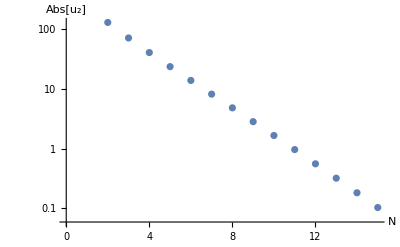

```mathematica
ListLogPlot[Abs[u2values], AxesLabel->{Style[HoldForm[N], 14],Style[HoldForm[Abs[Subscript[u, 2]]], 14]}, PlotRange->{{0,15},Automatic}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["u2value.png",%221,"PNG"]
```

u2value.png

#### u3

```mathematica
u3values = {{3,-9919.064618668466},{4,-8653.171927154015},{5,-6008.068449509373},{6,-3861.686270192115785503`21.586776988071325},{7,-2393.8},{8,-1452.89},{9,-869.1},{10,-513.97},{11,-300.996},{12,-174.724},{13,-100.6047},{14,-57.49155},{15,-32.62377}};
```

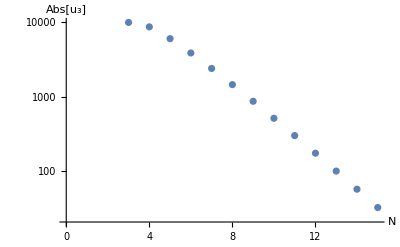

```mathematica
ListLogPlot[Abs[u3values],   AxesLabel->{Style[HoldForm[N], 14],Style[HoldForm[Abs[Subscript[u, 3]]], 14]}, PlotRange->{{0,15},Automatic}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["u3value.png",%222,"PNG"]
```

u3value.png

#### u4

```mathematica
u4values = {{4,-1.6371223133484824*^6},{5,-1.64119*^6},{6,-1.227828*^6},{7,-821795},{8,-520191},{9,-318695},{10,-191096.83},{11,-112816.1588},{12,-65796.4915},{13,-37988.625},{14,-21743.2811},{15,-12349.5}};
```

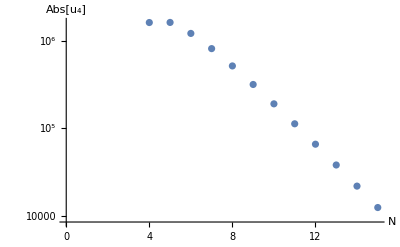

```mathematica
ListLogPlot[Abs[u4values],   AxesLabel->{Style[HoldForm[N], 14],Style[HoldForm[Abs[Subscript[u, 4]]], 14]}, PlotRange->{{0,15},Automatic}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["u4value.png",%225,"PNG"]
```

u4value.png

#### η

```mathematica
u2valuealone = Last/@u2values
```

{-127.62,-70.2116,-40.0636,-23.3201,-13.7144,-8.098,-4.78,-2.81,-1.65,-0.96034,-0.55567,-0.31935,-0.182298,-0.10338}

```mathematica
u2valuealone[[14]]
```

-0.10338

```mathematica
η2 = (8 u2valuealone[[1]])/(128 π^2+u2valuealone[[1]])
```

-0.898979

```mathematica
minηvalues = {{2, -(8 u2valuealone[[1]])/(128 π^2+u2valuealone[[1]])}}
```

{{2,0.898979}}

```mathematica
For[i=2,i<15,i++,minηvalues = Append[minηvalues, {i+1, -(8 *u2valuealone[[i]])/(128 π^2+u2valuealone[[i]])}]]
```

```mathematica
minηvalues
```

{{2,0.898979},{3,0.470785},{4,0.262015},{5,0.150454},{6,0.0878006},{7,0.051612},{8,0.0303847},{9,0.0178342},{10,0.0104624},{11,0.00608605},{12,0.00352037},{13,0.00202282},{14,0.00115458},{15,0.000654715}}

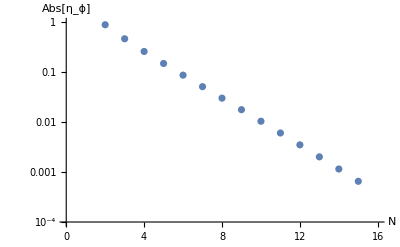

```mathematica
ListLogPlot[minηvalues,  AxesLabel->{Style[HoldForm[N],14],Style[HoldForm[Abs[Subscript[η, ϕ]]], 14]}, PlotRange->{{0,16}, {1, 0.0001}}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["AnomalousdimensionSingleScalarFieldlog.png",%254,"PNG"]
```

AnomalousdimensionSingleScalarFieldlog.png